Authors : Goran Malic* and Ileana Streinu*
*Smith College, Department of Computer Science, Northampton MA

# Enumeration of truncated combinatorial resultant trees for 3-connected circuits

We present the results of the enumeration algorithm for truncated combinatorial resultant trees described in [1] for 3-connected circuits on 6, 7 and 8 vertices.

[1] Goran Malic, Ileana Streinu, Enumerating combinatorial resultant trees, 2023, submitted to CGTA.

## Helper Functions

```mathematica
presentData[graphList_,nTrees_,nUnique_]:=Module[{data},
data=Table[{graphList[[i]],nTrees[[i]],nUnique[[i]]},{i,1,Length[graphList]}];
data =Join[{{"Circuit", "# of trunc trees", "# of unique circs appearing"}},data];
Grid[data,Frame->All]
]
```

## 6 vertices

### Graphs

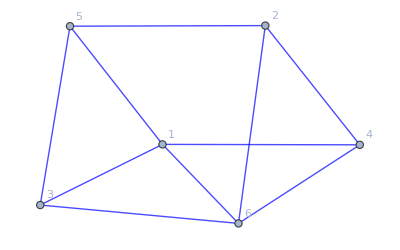
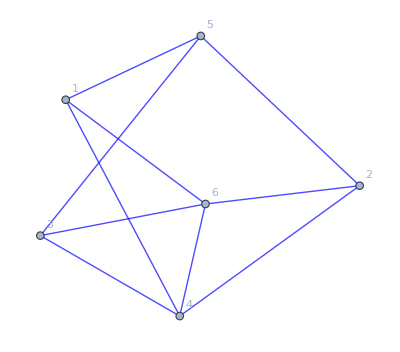
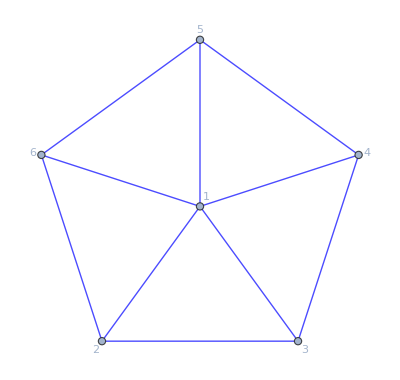
```mathematica
graphs6verts={-Graphics-,-Graphics-,-Graphics-};
```

### Data

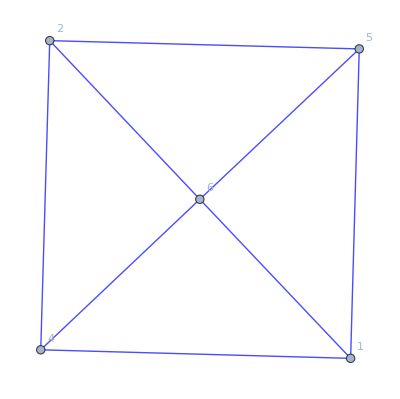
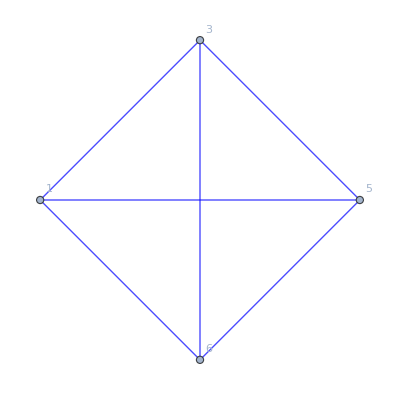
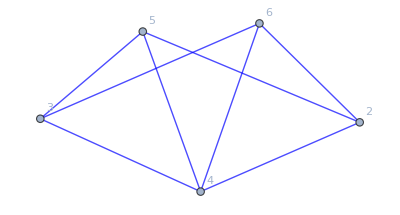
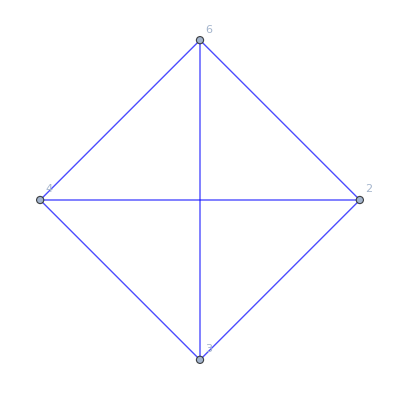
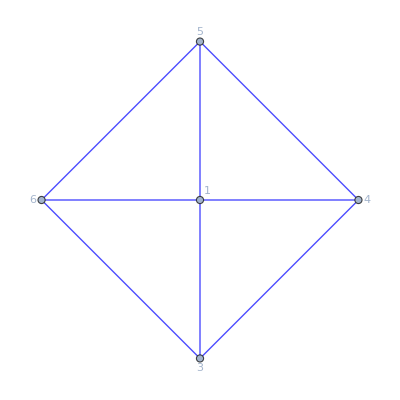
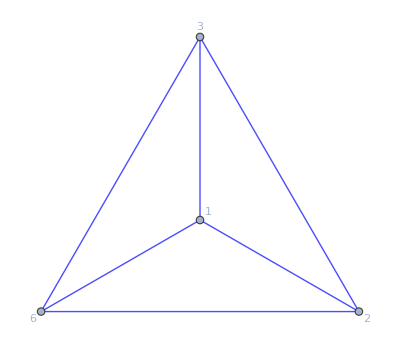
```mathematica
nodesSpace6verts={{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3}},{{1,{1,2,3,4},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{2,{5,6},<|1->1,2->2,4->4,5->5,6->6|>},{3,Null,<|1->1,3->3,5->5,6->6|>},{2,Null,<|6->1,2->2,1->3,4->5,5->6|>},{3,Null,<|1->1,6->2,3->4,5->6|>},{2,Null,<|1->1,2->2,4->3,5->4,6->6|>},{2,Null,<|1->1,2->2,6->3,4->5,5->6|>},{2,Null,<|6->1,1->3,2->4,4->5,5->6|>},{2,Null,<|1->1,2->2,6->4,4->5,5->6|>},{3,Null,<|6->2,1->4,3->5,5->6|>},{3,Null,<|1->1,3->4,5->5,6->6|>},{3,Null,<|1->1,6->2,3->5,5->6|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{2,10,11},{2,12,5}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,8}},{{1,{1,2,3,4,5,6},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{2,{7,8},<|2->2,3->3,4->4,5->5,6->6|>},{2,Null,<|5->1,6->3,4->4,2->5,3->6|>},{2,Null,<|2->2,3->3,5->4,6->5,4->6|>},{2,Null,<|5->1,6->3,2->4,3->5,4->6|>},{2,Null,<|5->1,6->2,4->4,2->5,3->6|>},{2,Null,<|5->1,6->2,2->4,3->5,4->6|>},{3,Null,<|2->2,3->3,4->4,6->6|>},{3,Null,<|2->2,3->3,4->4,6->5|>},{3,Null,<|3->3,4->4,6->5,2->6|>},{3,Null,<|3->2,4->4,6->5,2->6|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,3,6},{1,5,7},{2,8,9},{2,10,11}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3}},{{1,{1,2,3,4,5},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{2,{6,7},<|1->1,3->3,4->4,5->5,6->6|>},{3,Null,<|1->1,2->2,3->3,6->6|>},{2,Null,<|1->1,3->2,4->4,5->5,6->6|>},{3,Null,<|1->1,2->2,3->3,6->4|>},{2,Null,<|1->1,3->2,4->3,5->5,6->6|>},{3,Null,<|1->1,2->3,3->4,6->5|>},{2,Null,<|1->1,3->2,4->3,5->4,6->6|>},{3,Null,<|1->1,2->4,3->5,6->6|>},{2,Null,<|1->1,3->2,4->3,5->4,6->5|>},{3,Null,<|1->1,2->2,3->5,6->6|>},{3,Null,<|1->1,2->3,3->4,6->6|>},{3,Null,<|1->1,2->3,3->5,6->6|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},{2,9,12},{2,13,7}}}};
```

```mathematica
truncTreeEnum6verts={{{1,2,3,10,11},{1,2,3,12,5},{1,4,5},{1,6,7},{1,8,9}},{{1,2,3,8,9},{1,2,3,10,11},{1,4,5},{1,2,6,8,9},{1,2,6,10,11},{1,4,7},{1,3,6},{1,5,7}},{{1,2,3,9,12},{1,2,3,13,7},{1,4,5},{1,6,7},{1,8,9},{1,10,11}}};
```

```mathematica
nTruncTrees6verts=Length/@truncTreeEnum6verts;
```

```mathematica
nUnique6verts=Length/@nodeSpace6verts[[All,1]];
```

### Results

```mathematica
presentData[graphs6verts,nTruncTrees6verts,nUnique6verts]
```

Circuit | # of trunc trees | # of unique circs appearing
-Graphics- | 5 | 3
-Graphics- | 8 | 3
-Graphics- | 6 | 3

## 7 vertices

### Graphs

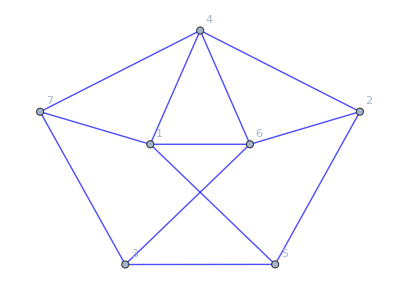
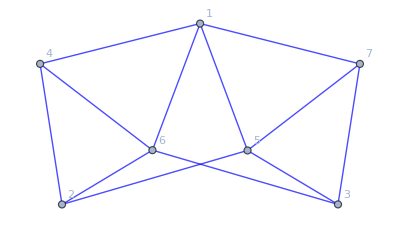
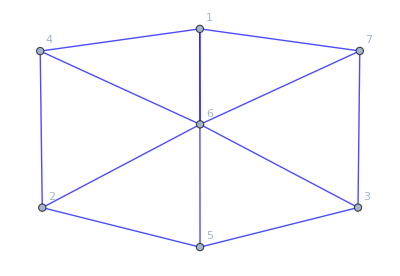
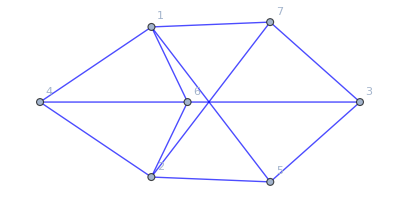
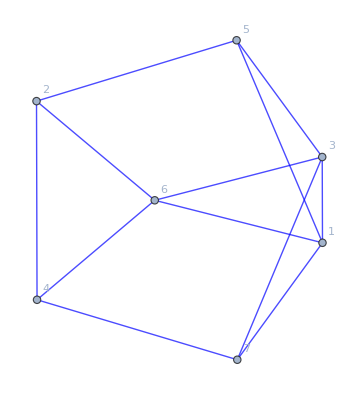
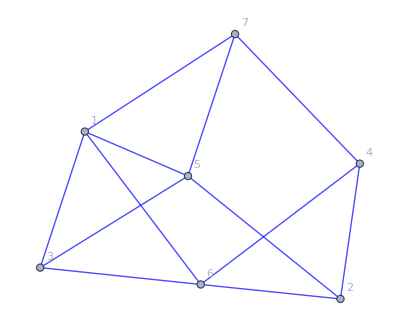
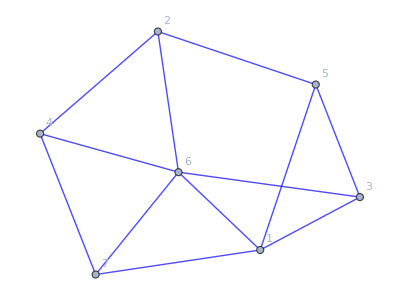
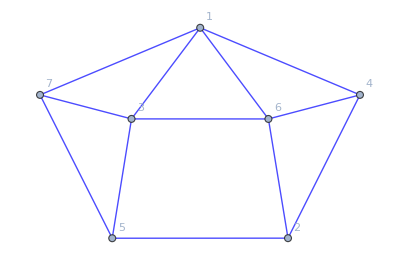
```mathematica
graphs7verts={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

### Data

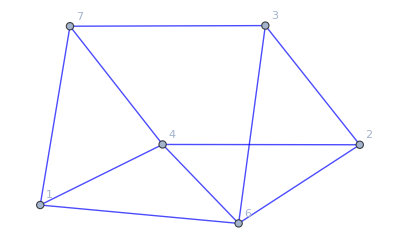
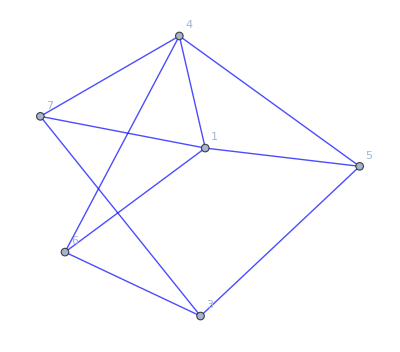
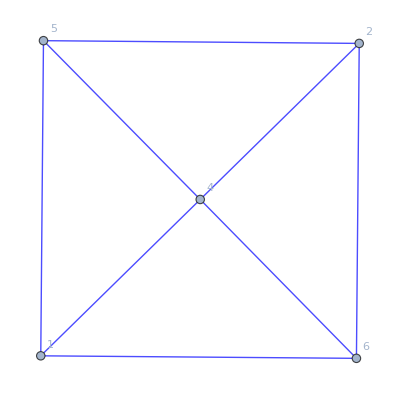
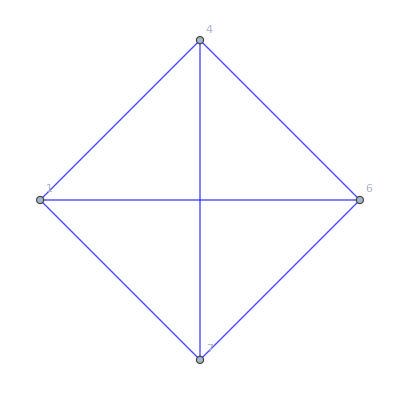
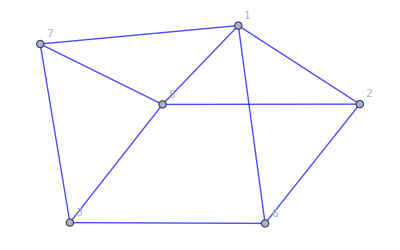
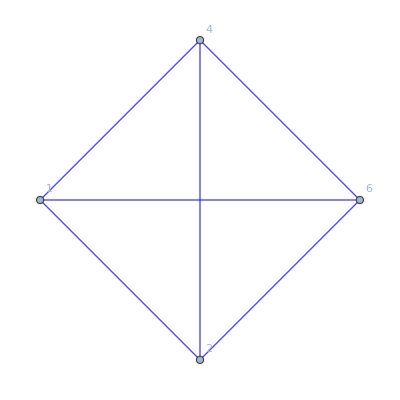
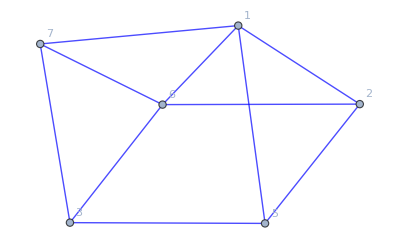
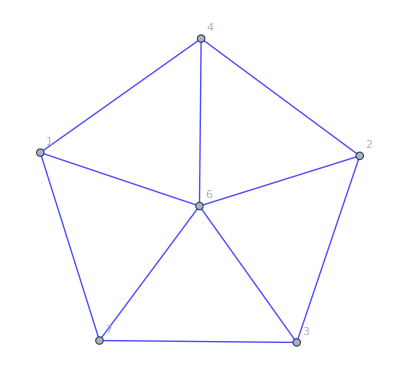
```mathematica
nodeSpace7verts={{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,4},{-Graphics-,5},{-Graphics-,15}},{{1,{1,2,3,4,5,6},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,{7,8,9,10},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{2,Null,<|3->1,4->2,1->3,2->4,7->5,6->6|>},{3,{11,12,13,14,15,16},<|1->1,3->3,4->4,5->5,6->6,7->7|>},{4,{17,18},<|1->1,2->2,4->4,5->5,6->6|>},{2,Null,<|4->1,3->3,1->4,2->5,6->6,7->7|>},{4,Null,<|1->1,2->2,5->4,6->5,4->6|>},{2,Null,<|6->1,7->2,4->4,3->5,1->6,2->7|>},{2,Null,<|6->1,7->3,2->4,1->5,3->6,4->7|>},{2,Null,<|6->1,7->2,2->3,1->4,3->5,4->6|>},{4,Null,<|4->1,2->3,1->4,5->6,6->7|>},{3,Null,<|5->1,6->2,7->3,1->4,3->5,4->6|>},{4,Null,<|1->1,2->3,4->4,5->6,6->7|>},{4,Null,<|5->2,2->3,1->4,4->6,6->7|>},{5,Null,<|1->1,4->4,6->6,7->7|>},{5,Null,<|6->2,7->3,1->4,4->6|>},{4,Null,<|1->1,2->2,4->4,5->6,6->7|>},{4,Null,<|4->2,2->3,1->4,5->6,6->7|>},{4,Null,<|1->1,2->2,6->3,5->4,4->6|>},{4,Null,<|4->1,2->3,1->4,5->5,6->7|>},{4,Null,<|1->1,2->3,4->4,5->5,6->7|>},{4,Null,<|4->1,2->3,1->4,5->5,6->6|>},{4,Null,<|1->1,2->3,4->4,5->5,6->6|>},{5,Null,<|7->2,1->4,4->5,6->6|>},{5,Null,<|1->1,4->4,6->5,7->6|>},{5,Null,<|1->1,7->2,4->4,6->6|>},{5,Null,<|1->1,7->2,4->4,6->5|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},{1,12,13},{2,14,15},{2,13,16},{2,17,18},{2,19,11},{4,11,20},{4,13,21},{4,11,22},{4,13,23},{4,20,22},{4,21,23},{5,24,25},{5,26,27}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,5}},{{1,{1,2,3,4},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,{5,6,7,8},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{2,Null,<|1->1,3->3,2->4,5->5,6->6,7->7|>},{4,{9,10},<|1->1,2->2,4->4,5->5,6->6|>},{2,Null,<|1->1,3->2,7->4,6->5,5->6,2->7|>},{4,Null,<|1->1,2->3,5->5,6->6,4->7|>},{2,Null,<|1->1,3->2,2->3,7->4,6->5,5->6|>},{3,Null,<|1->1,6->3,4->5,2->7|>},{4,Null,<|1->1,5->2,2->3,4->5,6->7|>},{4,Null,<|1->1,4->2,2->3,5->5,6->6|>},{4,Null,<|1->1,2->3,4->5,5->6,6->7|>},{3,Null,<|1->1,2->2,4->5,6->6|>},{4,Null,<|4->1,5->2,1->5,2->6,6->7|>},{4,Null,<|4->1,5->2,6->3,1->5,2->6|>},{3,Null,<|2->2,1->4,4->5,6->6|>},{3,Null,<|1->1,4->4,6->5,2->6|>},{3,Null,<|1->1,2->2,4->4,6->5|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{2,10,11},{2,12,13},{2,14,7},{2,15,9},{5,16,17},{5,3,18}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,8}},{{1,{1,2,3,4,5,6},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,{7,8,9,10},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{4,{11,12,13,14,15},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{2,Null,<|5->1,7->2,6->3,3->5,1->6,2->7|>},{2,Null,<|5->1,6->2,7->3,2->4,3->5,1->6|>},{2,Null,<|1->1,3->3,2->4,5->5,6->6,7->7|>},{5,{16,17},<|1->1,2->2,4->4,5->5,6->6|>},{2,Null,<|1->1,3->2,7->4,5->5,6->6,2->7|>},{5,Null,<|1->1,2->3,5->5,6->6,4->7|>},{2,Null,<|1->1,3->2,2->3,7->4,5->5,6->6|>},{3,Null,<|1->1,6->3,4->6,2->7|>},{5,Null,<|1->1,5->2,2->3,4->6,6->7|>},{5,Null,<|1->1,4->2,2->3,5->5,6->6|>},{5,Null,<|1->1,2->3,5->5,4->6,6->7|>},{3,Null,<|1->1,2->2,4->5,6->6|>},{5,Null,<|4->1,5->2,1->5,2->6,6->7|>},{5,Null,<|4->1,5->2,6->3,1->5,2->6|>},{5,Null,<|5->2,2->3,1->4,4->6,6->7|>},{3,Null,<|1->1,4->4,6->6,2->7|>},{5,Null,<|1->1,2->3,5->4,4->6,6->7|>},{3,Null,<|6->2,2->3,1->4,4->6|>},{5,Null,<|1->1,2->2,5->4,4->6,6->7|>},{3,Null,<|4->2,6->3,1->6,2->7|>},{5,Null,<|1->1,2->2,6->3,5->4,4->6|>},{3,Null,<|2->2,1->4,4->5,6->6|>},{3,Null,<|1->1,4->4,6->5,2->6|>},{3,Null,<|1->1,2->2,4->4,6->5|>}},{{1,2,3},{1,4,5},{1,4,6},{1,7,8},{1,9,10},{1,11,12},{2,13,14},{2,15,16},{2,17,10},{2,18,12},{4,19,20},{4,13,3},{4,21,22},{4,23,24},{4,25,12},{8,26,27},{8,3,28}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,10},{-Graphics-,12}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,{9,10,11,12,13,14},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{4,{15,16,17,18},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{2,Null,<|1->1,3->2,2->3,5->5,6->6,7->7|>},{4,Null,<|2->1,1->2,3->3,4->4,6->6,7->7|>},{2,Null,<|3->1,1->2,2->3,5->5,6->6,7->7|>},{4,Null,<|6->1,7->2,4->3,3->4,2->5,1->6|>},{4,Null,<|2->1,1->2,3->3,4->4,7->5,6->6|>},{5,{19},<|1->1,2->2,4->4,5->5,6->6,7->7|>},{2,Null,<|5->1,6->2,7->3,1->5,3->6,2->7|>},{6,{20,21},<|1->1,2->2,3->3,6->6,7->7|>},{6,Null,<|1->1,2->2,3->3,6->5,7->7|>},{6,Null,<|6->1,1->2,7->3,2->6,3->7|>},{6,Null,<|6->1,1->2,7->3,2->5,3->7|>},{6,Null,<|1->1,2->2,3->3,6->5,7->6|>},{6,Null,<|6->1,1->2,7->3,2->5,3->6|>},{6,Null,<|1->1,7->3,6->4,2->6,3->7|>},{6,Null,<|6->1,7->2,1->4,2->6,3->7|>},{6,Null,<|6->1,7->2,2->4,1->6,3->7|>},{3,Null,<|1->1,6->3,4->6,2->7|>},{6,Null,<|6->1,7->2,3->3,2->4,1->6|>},{6,Null,<|6->1,7->2,1->3,2->6,3->7|>},{3,Null,<|1->1,4->2,6->5,2->7|>},{3,Null,<|1->1,4->2,6->4,2->6|>},{3,Null,<|1->1,4->2,6->3,2->7|>},{3,Null,<|1->1,6->2,2->3,4->6|>},{3,Null,<|1->1,6->2,4->6,2->7|>}},{{1,2,3},{1,4,5},{1,6,7},{1,4,8},{1,6,9},{1,10,11},{1,8,5},{1,9,7},{2,12,13},{2,14,15},{2,12,16},{2,14,17},{2,13,16},{2,15,17},{4,12,3},{4,18,19},{4,20,21},{4,22,23},{10,24,25},{12,26,27},{12,21,28}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,6},{-Graphics-,7},{-Graphics-,15}},{{1,{1,2,3,4,5,6},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,{7,8,9,10},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{3,{11,12},<|1->1,2->2,3->3,5->5,6->6|>},{2,Null,<|3->1,2->2,1->3,4->4,6->6,7->7|>},{3,Null,<|3->1,2->2,1->3,5->5,6->6|>},{4,{13,14,15,16,17,18},<|1->1,3->3,4->4,5->5,6->6,7->7|>},{5,{19},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{4,Null,<|1->1,4->2,3->3,5->5,6->6,7->7|>},{5,Null,<|1->1,2->2,3->3,4->4,5->6,6->7|>},{2,Null,<|6->1,7->2,2->3,3->4,4->5,1->6|>},{3,Null,<|1->1,3->3,2->4,5->6,6->7|>},{2,Null,<|2->1,7->2,6->3,3->4,4->5,1->6|>},{3,Null,<|3->1,1->3,2->4,5->6,6->7|>},{3,Null,<|3->1,5->2,2->4,1->6,6->7|>},{6,Null,<|1->1,3->3,6->6,7->7|>},{6,Null,<|1->1,6->2,7->4,3->6|>},{3,Null,<|1->1,2->2,3->3,5->6,6->7|>},{3,Null,<|3->1,1->2,2->4,5->6,6->7|>},{3,Null,<|3->1,6->2,5->3,2->4,1->6|>},{6,Null,<|1->1,7->2,3->5,6->6|>},{6,Null,<|1->1,3->3,6->5,7->6|>},{6,Null,<|1->1,7->2,3->3,6->6|>},{6,Null,<|1->1,7->2,3->3,6->5|>},{3,Null,<|1->1,3->3,2->4,5->5,6->7|>},{3,Null,<|3->1,1->3,2->4,5->5,6->7|>},{3,Null,<|1->1,3->3,2->4,5->5,6->6|>},{3,Null,<|3->1,1->3,2->4,5->5,6->6|>},{6,Null,<|1->2,3->4,6->5,7->6|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},{1,12,13},{2,14,15},{2,11,16},{2,17,18},{2,19,13},{3,20,21},{3,22,23},{6,11,24},{6,13,25},{6,11,26},{6,13,27},{6,24,26},{6,25,27},{7,28,21}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,6},{-Graphics-,11},{-Graphics-,12}},{{1,{1,2,3,4,5,6,7},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,{8,9,10,11},<|1->1,2->2,4->4,5->5,6->6,7->7|>},{3,Null,<|1->1,3->3,5->5,6->6|>},{2,Null,<|6->1,2->3,7->4,5->5,4->6,1->7|>},{2,Null,<|4->1,1->2,5->4,6->5,7->6,2->7|>},{4,{12},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{2,Null,<|6->1,7->2,2->3,5->5,4->6,1->7|>},{2,Null,<|4->1,5->2,1->4,2->5,7->6,6->7|>},{2,Null,<|6->1,7->2,2->3,1->4,4->5,5->6|>},{2,Null,<|6->1,7->2,5->4,4->5,1->6,2->7|>},{5,{13,14,15,16,17},<|1->1,3->3,4->4,5->5,6->6,7->7|>},{6,{18,19},<|2->2,4->4,5->5,6->6,7->7|>},{3,Null,<|1->1,3->5,5->6,6->7|>},{6,Null,<|5->1,4->4,6->5,2->6,7->7|>},{3,Null,<|5->2,6->4,1->5,3->6|>},{6,Null,<|5->1,4->2,6->5,2->6,7->7|>},{6,Null,<|6->2,4->4,5->5,2->6,7->7|>},{6,Null,<|5->1,4->2,7->4,2->5,6->6|>},{6,Null,<|6->1,4->4,5->5,2->6,7->7|>},{3,Null,<|1->2,3->4,5->5,6->6|>},{6,Null,<|6->1,5->3,4->4,2->6,7->7|>},{3,Null,<|1->1,3->3,5->5,6->7|>},{6,Null,<|6->1,5->3,7->4,2->5,4->7|>},{3,Null,<|1->1,3->3,6->4,5->6|>},{6,Null,<|6->1,5->3,2->5,7->6,4->7|>},{3,Null,<|1->1,5->4,3->6,6->7|>},{6,Null,<|6->1,5->3,4->4,2->5,7->6|>},{3,Null,<|1->1,5->4,3->5,6->7|>},{3,Null,<|3->2,5->4,1->6,6->7|>},{3,Null,<|5->2,1->5,3->6,6->7|>},{3,Null,<|5->4,1->5,3->6,6->7|>}},{{1,2,3},{1,4,5},{1,4,6},{1,7,8},{1,9,10},{1,6,5},{1,9,11},{2,12,13},{2,14,15},{2,16,17},{2,18,19},{6,20,3},{11,19,3},{11,21,22},{11,23,24},{11,25,26},{11,27,28},{12,29,30},{12,31,15}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,5},{-Graphics-,6},{-Graphics-,8}},{{1,{1,2,3,4,5,6},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,{7,8,9,10,11},<|1->1,2->2,4->4,5->5,6->6,7->7|>},{3,Null,<|1->1,3->3,5->5,6->6|>},{2,Null,<|1->1,2->2,5->3,4->4,6->6,7->7|>},{4,{12,13},<|1->1,2->2,3->3,5->5,6->6|>},{5,{14,15,16,17},<|1->1,3->3,4->4,5->5,6->6,7->7|>},{5,Null,<|5->1,7->2,6->4,4->5,1->6,3->7|>},{6,{18},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{5,Null,<|1->1,4->2,3->3,5->5,6->6,7->7|>},{3,Null,<|3->2,5->4,1->6,6->7|>},{5,Null,<|1->1,4->2,3->3,7->4,5->5,6->6|>},{3,Null,<|1->1,5->4,3->6,6->7|>},{4,Null,<|5->2,2->4,1->5,3->6,6->7|>},{3,Null,<|1->1,3->5,5->6,6->7|>},{4,Null,<|1->1,5->2,2->4,3->6,6->7|>},{3,Null,<|1->1,6->2,3->5,5->6|>},{4,Null,<|1->1,2->4,5->5,3->6,6->7|>},{3,Null,<|5->2,6->4,1->5,3->6|>},{4,Null,<|1->1,2->2,5->5,3->6,6->7|>},{4,Null,<|1->1,2->2,6->4,5->5,3->6|>},{3,Null,<|6->2,1->3,3->5,5->6|>},{3,Null,<|1->1,6->2,3->3,5->6|>},{3,Null,<|1->1,6->2,3->3,5->5|>},{4,Null,<|1->1,5->3,2->4,3->6,6->7|>},{4,Null,<|1->1,3->3,2->4,5->5,6->6|>},{4,Null,<|3->1,1->3,5->5,6->6,2->7|>},{4,Null,<|1->1,2->4,5->5,6->6,3->7|>},{4,Null,<|3->1,1->3,2->4,5->5,6->6|>},{3,Null,<|1->2,3->4,5->5,6->6|>}},{{1,2,3},{1,4,5},{1,6,7},{1,6,8},{1,9,10},{1,11,12},{2,13,14},{2,15,16},{2,17,18},{2,19,10},{2,20,12},{5,21,3},{5,22,23},{6,17,3},{6,24,25},{6,26,27},{6,28,12},{8,29,3}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,10}},{{1,{1,2,3,4},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,{5,6,7,8},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{2,Null,<|1->1,3->3,2->4,5->5,6->6,7->7|>},{2,Null,<|6->1,7->2,2->3,3->4,5->5,1->6|>},{2,Null,<|3->1,2->2,7->3,6->4,1->6,5->7|>},{2,Null,<|6->1,5->2,1->3,7->5,2->6,3->7|>},{2,Null,<|3->1,2->2,7->3,6->4,5->5,1->6|>},{3,Null,<|1->1,4->3,6->5,2->7|>},{4,{9,10},<|1->1,2->2,3->3,5->5,7->7|>},{3,Null,<|1->1,2->2,4->3,6->6|>},{4,Null,<|1->1,3->3,5->5,2->6,7->7|>},{4,Null,<|1->1,7->2,2->3,5->5,3->6|>},{4,Null,<|3->1,5->2,1->3,2->6,7->7|>},{4,Null,<|1->1,7->2,2->3,5->5,3->7|>},{4,Null,<|3->1,5->2,1->3,7->5,2->6|>},{3,Null,<|4->2,1->3,6->5,2->7|>},{3,Null,<|1->1,6->2,4->3,2->7|>},{3,Null,<|1->1,6->2,4->3,2->5|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{2,10,11},{2,12,13},{2,14,15},{2,16,9},{10,17,18},{10,9,19}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,11},{-Graphics-,12}},{{1,{1,2,3,4,5,6,7,8,9},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,{10,11,12,13},<|1->1,2->2,4->4,5->5,6->6,7->7|>},{3,{14,15,16,17,18},<|1->1,3->3,4->4,5->5,6->6,7->7|>},{2,Null,<|7->1,6->2,1->4,2->5,4->6,5->7|>},{2,Null,<|1->1,6->3,7->4,2->5,4->6,5->7|>},{2,Null,<|1->1,2->2,7->3,6->4,5->5,4->6|>},{3,Null,<|3->1,4->2,5->3,6->4,7->5,1->6|>},{2,Null,<|4->1,2->3,1->4,5->5,6->6,7->7|>},{3,Null,<|3->1,4->2,1->4,7->5,6->6,5->7|>},{2,Null,<|6->1,7->2,2->3,1->4,5->5,4->6|>},{4,{19,20},<|1->1,2->2,4->4,5->5,7->7|>},{5,Null,<|1->1,2->2,4->4,6->6|>},{4,Null,<|1->1,4->4,5->5,2->6,7->7|>},{4,Null,<|4->1,5->2,2->4,7->5,1->6|>},{4,Null,<|4->1,5->2,1->4,2->6,7->7|>},{4,Null,<|4->1,5->2,2->4,7->5,1->7|>},{4,Null,<|4->1,5->2,1->4,7->5,2->6|>},{5,Null,<|1->1,4->4,6->5,2->7|>},{5,Null,<|1->1,4->3,2->5,6->6|>},{4,Null,<|1->1,4->3,7->5,2->6,5->7|>},{5,Null,<|1->1,4->4,6->6,2->7|>},{4,Null,<|1->1,4->3,2->4,7->5,5->7|>},{5,Null,<|1->1,4->3,6->4,2->6|>},{4,Null,<|1->1,4->3,5->4,2->6,7->7|>},{5,Null,<|1->1,4->3,6->5,2->7|>},{4,Null,<|1->1,4->3,5->4,7->5,2->6|>},{5,Null,<|1->1,4->2,6->5,2->7|>},{5,Null,<|1->1,6->2,4->4,2->7|>},{5,Null,<|1->1,6->2,4->4,2->5|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,8,10},{1,5,7},{1,10,9},{1,6,3},{2,11,12},{2,13,14},{2,15,16},{2,17,18},{3,13,19},{3,20,21},{3,22,23},{3,24,25},{3,26,18},{11,27,28},{11,18,29}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,8},{-Graphics-,9}},{{1,{1,2,3,4,5,6,7,8,9},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,{10,11,12,13},<|1->1,2->2,4->4,5->5,6->6,7->7|>},{3,{14,15},<|1->1,3->3,5->5,6->6,7->7|>},{4,{16,17,18,19,20},<|1->1,2->2,4->4,5->5,6->6,7->7|>},{3,Null,<|3->1,6->3,7->5,1->6,5->7|>},{2,Null,<|1->1,2->2,7->3,4->4,5->5,6->6|>},{4,Null,<|1->1,2->2,7->3,4->4,5->5,6->6|>},{5,{21,22,23,24,25,26},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{6,Null,<|1->1,2->2,4->4,6->6|>},{5,Null,<|1->1,3->3,2->4,5->5,6->6,7->7|>},{2,Null,<|7->1,4->2,6->4,2->5,1->6,5->7|>},{2,Null,<|4->1,7->2,2->3,1->4,5->5,6->6|>},{3,Null,<|1->1,6->2,7->5,3->6,5->7|>},{3,Null,<|1->1,3->4,5->5,6->6,7->7|>},{3,Null,<|3->1,7->2,1->4,5->5,6->6|>},{3,Null,<|3->1,7->2,6->4,1->6,5->7|>},{3,Null,<|3->1,7->2,5->5,6->6,1->7|>},{3,Null,<|3->1,7->2,6->4,5->5,1->6|>},{6,Null,<|1->1,6->5,4->6,2->7|>},{6,Null,<|1->1,4->3,2->5,6->6|>},{6,Null,<|1->1,4->3,6->5,2->7|>},{6,Null,<|1->1,4->3,6->6,2->7|>},{3,Null,<|6->2,3->4,7->5,1->6,5->7|>},{6,Null,<|1->1,4->4,6->6,2->7|>},{3,Null,<|3->1,6->2,7->5,1->6,5->7|>},{3,Null,<|3->1,6->4,7->5,1->6,5->7|>},{6,Null,<|6->2,1->4,2->5,4->6|>},{6,Null,<|4->2,6->5,1->6,2->7|>},{3,Null,<|1->1,7->2,3->3,5->5,6->6|>},{3,Null,<|3->1,5->2,6->3,7->5,1->6|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,10,11},{1,10,12},{1,6,3},{1,7,5},{2,13,9},{2,14,15},{2,16,17},{2,18,19},{3,19,20},{3,21,22},{4,23,24},{4,25,9},{4,26,27},{4,16,28},{4,18,19},{8,13,3},{8,25,5},{8,13,29},{8,25,30},{8,3,29},{8,5,30}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,8},{-Graphics-,15}},{{1,{1,2,3,4,5,6,7,8,9,10},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,{11,12,13,14},<|1->1,2->2,4->4,5->5,6->6,7->7|>},{3,{15,16},<|1->1,3->3,5->5,6->6,7->7|>},{2,Null,<|5->1,4->2,2->4,1->5,6->6,7->7|>},{3,Null,<|3->1,5->3,1->5,7->6,6->7|>},{2,Null,<|1->1,2->2,7->3,4->4,5->5,6->6|>},{2,Null,<|5->1,4->2,7->3,2->4,1->5,6->6|>},{4,{17,18,19,20,21,22},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{2,Null,<|6->1,1->2,7->4,4->5,5->6,2->7|>},{2,Null,<|1->1,6->2,5->3,4->4,7->5,2->6|>},{4,Null,<|1->1,3->3,2->4,5->5,6->6,7->7|>},{2,Null,<|4->1,7->2,1->4,6->5,5->6,2->7|>},{2,Null,<|7->1,4->2,5->3,6->4,1->5,2->6|>},{3,Null,<|1->1,5->2,3->5,7->6,6->7|>},{5,Null,<|1->1,2->2,4->4,6->6|>},{3,Null,<|3->1,7->2,5->4,1->6,6->7|>},{3,Null,<|3->1,7->2,5->5,6->6,1->7|>},{3,Null,<|1->1,3->4,5->5,6->6,7->7|>},{3,Null,<|3->1,7->2,1->4,5->5,6->6|>},{3,Null,<|3->1,7->2,5->4,6->5,1->6|>},{5,Null,<|1->1,4->5,2->6,6->7|>},{5,Null,<|1->1,4->3,2->5,6->6|>},{5,Null,<|1->1,4->3,2->6,6->7|>},{5,Null,<|1->1,4->3,2->5,6->7|>},{3,Null,<|3->1,5->2,1->5,7->6,6->7|>},{3,Null,<|1->1,7->2,3->3,5->5,6->6|>},{3,Null,<|3->1,6->2,5->3,1->5,7->6|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,8,10},{1,11,12},{1,11,13},{1,6,3},{1,7,5},{2,14,15},{2,16,17},{2,18,19},{2,20,21},{3,21,22},{3,23,24},{8,14,3},{8,25,5},{8,14,26},{8,25,27},{8,3,26},{8,5,27}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,14},{-Graphics-,20}},{{1,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,{19,20,21,22,23,24},<|2->2,3->3,4->4,5->5,6->6,7->7|>},{2,Null,<|2->1,3->3,4->4,5->5,6->6,7->7|>},{2,Null,<|2->2,3->3,4->4,6->5,5->6,7->7|>},{2,Null,<|2->1,3->3,4->4,6->5,5->6,7->7|>},{2,Null,<|2->2,3->3,6->4,4->5,5->6,7->7|>},{2,Null,<|2->1,3->3,6->4,4->5,5->6,7->7|>},{2,Null,<|2->1,3->2,4->4,5->5,6->6,7->7|>},{2,Null,<|2->1,3->2,4->4,6->5,5->6,7->7|>},{2,Null,<|2->1,3->2,6->4,4->5,5->6,7->7|>},{2,Null,<|2->1,3->2,7->3,4->4,5->5,6->6|>},{2,Null,<|2->1,3->2,7->3,4->4,6->5,5->6|>},{2,Null,<|2->1,3->2,7->3,6->4,4->5,5->6|>},{3,{25,26},<|3->3,4->4,5->5,6->6,7->7|>},{3,Null,<|3->2,4->4,5->5,6->6,7->7|>},{3,Null,<|3->3,5->4,4->5,6->6,7->7|>},{3,Null,<|3->2,5->4,4->5,6->6,7->7|>},{3,Null,<|3->2,7->3,4->4,5->5,6->6|>},{3,Null,<|3->2,7->3,5->4,4->5,6->6|>},{4,Null,<|3->3,4->4,6->6,7->7|>},{4,Null,<|3->3,4->4,6->5,7->7|>},{4,Null,<|4->4,6->5,3->6,7->7|>},{4,Null,<|7->3,4->4,6->5,3->6|>}},{{1,2,3},{1,4,5},{1,6,7},{1,2,8},{1,4,9},{1,6,10},{1,2,11},{1,4,12},{1,6,13},{1,3,8},{1,5,9},{1,7,10},{1,3,11},{1,5,12},{1,7,13},{1,8,11},{1,9,12},{1,10,13},{2,14,15},{2,16,17},{2,14,18},{2,16,19},{2,15,18},{2,17,19},{14,20,21},{14,22,23}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,14}},{{1,{1,2,3,4,5,6},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,{7,8,9,10,11},<|1->1,3->3,4->4,5->5,6->6,7->7|>},{3,Null,<|1->1,2->2,6->6,7->7|>},{2,Null,<|1->1,3->2,5->4,6->5,7->6,4->7|>},{3,Null,<|1->1,2->3,6->4,7->7|>},{2,Null,<|1->1,3->2,5->3,6->5,7->6,4->7|>},{3,Null,<|1->1,2->3,6->4,7->5|>},{2,Null,<|1->1,3->2,5->3,6->4,7->6,4->7|>},{3,Null,<|1->1,2->4,6->5,7->6|>},{2,Null,<|1->1,3->2,5->3,6->4,7->5,4->7|>},{3,Null,<|1->1,2->2,6->5,7->6|>},{2,Null,<|1->1,3->2,4->3,5->4,6->5,7->6|>},{3,Null,<|1->1,2->2,6->3,7->7|>},{4,{12,13},<|1->1,4->4,5->5,6->6,7->7|>},{4,Null,<|1->1,4->3,5->5,6->6,7->7|>},{4,Null,<|1->1,4->3,5->4,6->6,7->7|>},{4,Null,<|1->1,4->3,5->4,6->5,7->7|>},{3,Null,<|1->1,2->5,6->6,7->7|>},{4,Null,<|1->1,4->3,5->4,6->5,7->6|>},{3,Null,<|1->1,2->3,6->6,7->7|>},{3,Null,<|1->1,2->4,6->5,7->7|>},{3,Null,<|1->1,2->4,6->6,7->7|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},{1,12,13},{2,14,5},{2,15,7},{2,16,9},{2,17,18},{2,19,20},{14,18,21},{14,22,9}}}};
```

```mathematica
truncTreeEnum7verts={{{1,2,3,14,15},{1,2,3,13,16},{1,2,3,17,18},{1,2,3,19,11},{1,4,5,11,20,24,25},{1,4,5,11,20,26,27},{1,4,5,13,21,24,25},{1,4,5,13,21,26,27},{1,4,5,11,22,24,25},{1,4,5,11,22,26,27},{1,4,5,13,23,24,25},{1,4,5,13,23,26,27},{1,4,5,20,22,24,25},{1,4,5,20,22,26,27},{1,4,5,21,23,24,25},{1,4,5,21,23,26,27},{1,6,7},{1,8,9},{1,10,11},{1,12,13}},{{1,2,3,10,11},{1,2,3,12,13},{1,2,3,14,7},{1,2,3,15,9},{1,4,5,0,0,16,17},{1,4,5,0,0,3,18},{1,6,7},{1,8,9}},{{1,2,3,13,14},{1,2,3,15,16},{1,2,3,17,10},{1,2,3,18,12},{1,4,5,19,20},{1,4,5,13,3},{1,4,5,21,22},{1,4,5,23,24},{1,4,5,25,12},{1,4,6,19,20},{1,4,6,13,3},{1,4,6,21,22},{1,4,6,23,24},{1,4,6,25,12},{1,7,8,0,0,26,27},{1,7,8,0,0,3,28},{1,9,10},{1,11,12}},{{1,2,3,12,13,0,0,26,27},{1,2,3,12,13,0,0,21,28},{1,2,3,14,15},{1,2,3,12,16,0,0,26,27},{1,2,3,12,16,0,0,21,28},{1,2,3,14,17},{1,2,3,13,16},{1,2,3,15,17},{1,4,5,12,3,0,0,26,27},{1,4,5,12,3,0,0,21,28},{1,4,5,18,19},{1,4,5,20,21},{1,4,5,22,23},{1,6,7},{1,4,8,12,3,0,0,26,27},{1,4,8,12,3,0,0,21,28},{1,4,8,18,19},{1,4,8,20,21},{1,4,8,22,23},{1,6,9},{1,10,11,24,25},{1,8,5},{1,9,7}},{{1,2,3,14,15,20,21},{1,2,3,14,15,22,23},{1,2,3,11,16,20,21},{1,2,3,11,16,22,23},{1,2,3,17,18,20,21},{1,2,3,17,18,22,23},{1,2,3,19,13,20,21},{1,2,3,19,13,22,23},{1,4,5},{1,6,7,11,24,28,21},{1,6,7,13,25,28,21},{1,6,7,11,26,28,21},{1,6,7,13,27,28,21},{1,6,7,24,26,28,21},{1,6,7,25,27,28,21},{1,8,9},{1,10,11},{1,12,13}},{{1,2,3,12,13,0,0,29,30},{1,2,3,12,13,0,0,31,15},{1,2,3,14,15},{1,2,3,16,17},{1,2,3,18,19},{1,4,5},{1,4,6,0,0,20,3},{1,7,8},{1,9,10},{1,6,5,20,3},{1,9,11,0,0,19,3},{1,9,11,0,0,21,22},{1,9,11,0,0,23,24},{1,9,11,0,0,25,26},{1,9,11,0,0,27,28}},{{1,2,3,13,14},{1,2,3,15,16},{1,2,3,17,18},{1,2,3,19,10},{1,2,3,20,12},{1,4,5,0,0,21,3},{1,4,5,0,0,22,23},{1,6,7,17,3},{1,6,7,24,25},{1,6,7,26,27},{1,6,7,28,12},{1,6,8,17,3,29,3},{1,6,8,24,25,29,3},{1,6,8,26,27,29,3},{1,6,8,28,12,29,3},{1,9,10},{1,11,12}},{{1,2,3,10,11,0,0,17,18},{1,2,3,10,11,0,0,9,19},{1,2,3,12,13},{1,2,3,14,15},{1,2,3,16,9},{1,4,5},{1,6,7},{1,8,9}},{{1,2,3,11,12,13,19,27,28},{1,2,3,11,12,13,19,18,29},{1,2,3,11,12,20,21,27,28},{1,2,3,11,12,20,21,18,29},{1,2,3,11,12,22,23,27,28},{1,2,3,11,12,22,23,18,29},{1,2,3,11,12,24,25,27,28},{1,2,3,11,12,24,25,18,29},{1,2,3,11,12,26,18,27,28},{1,2,3,11,12,26,18,18,29},{1,2,3,13,14,13,19},{1,2,3,13,14,20,21},{1,2,3,13,14,22,23},{1,2,3,13,14,24,25},{1,2,3,13,14,26,18},{1,2,3,15,16,13,19},{1,2,3,15,16,20,21},{1,2,3,15,16,22,23},{1,2,3,15,16,24,25},{1,2,3,15,16,26,18},{1,2,3,17,18,13,19},{1,2,3,17,18,20,21},{1,2,3,17,18,22,23},{1,2,3,17,18,24,25},{1,2,3,17,18,26,18},{1,4,5},{1,2,6,11,12,0,0,27,28},{1,2,6,11,12,0,0,18,29},{1,2,6,13,14},{1,2,6,15,16},{1,2,6,17,18},{1,4,7},{1,8,9},{1,8,10},{1,5,7},{1,10,9},{1,6,3,0,0,13,19},{1,6,3,0,0,20,21},{1,6,3,0,0,22,23},{1,6,3,0,0,24,25},{1,6,3,0,0,26,18}},{{1,2,3,13,9,19,20},{1,2,3,13,9,21,22},{1,2,3,14,15,19,20},{1,2,3,14,15,21,22},{1,2,3,16,17,19,20},{1,2,3,16,17,21,22},{1,2,3,18,19,19,20},{1,2,3,18,19,21,22},{1,4,5,23,24},{1,4,5,25,9},{1,4,5,26,27},{1,4,5,16,28},{1,4,5,18,19},{1,2,6,13,9},{1,2,6,14,15},{1,2,6,16,17},{1,2,6,18,19},{1,4,7,23,24},{1,4,7,25,9},{1,4,7,26,27},{1,4,7,16,28},{1,4,7,18,19},{1,8,9,13,3,0,0,0,0,19,20},{1,8,9,13,3,0,0,0,0,21,22},{1,8,9,25,5},{1,8,9,13,29},{1,8,9,25,30},{1,8,9,3,29,0,0,19,20},{1,8,9,3,29,0,0,21,22},{1,8,9,5,30},{1,10,11},{1,10,12},{1,6,3,0,0,19,20},{1,6,3,0,0,21,22},{1,7,5}},{{1,2,3,14,15,21,22},{1,2,3,14,15,23,24},{1,2,3,16,17,21,22},{1,2,3,16,17,23,24},{1,2,3,18,19,21,22},{1,2,3,18,19,23,24},{1,2,3,20,21,21,22},{1,2,3,20,21,23,24},{1,4,5},{1,2,6,14,15},{1,2,6,16,17},{1,2,6,18,19},{1,2,6,20,21},{1,4,7},{1,8,9,14,3,0,0,0,0,21,22},{1,8,9,14,3,0,0,0,0,23,24},{1,8,9,25,5},{1,8,9,14,26},{1,8,9,25,27},{1,8,9,3,26,0,0,21,22},{1,8,9,3,26,0,0,23,24},{1,8,9,5,27},{1,8,10,14,3,0,0,0,0,21,22},{1,8,10,14,3,0,0,0,0,23,24},{1,8,10,25,5},{1,8,10,14,26},{1,8,10,25,27},{1,8,10,3,26,0,0,21,22},{1,8,10,3,26,0,0,23,24},{1,8,10,5,27},{1,11,12},{1,11,13},{1,6,3,0,0,21,22},{1,6,3,0,0,23,24},{1,7,5}},{{1,2,3,14,15,0,0,20,21},{1,2,3,14,15,0,0,22,23},{1,2,3,16,17},{1,2,3,14,18,0,0,20,21},{1,2,3,14,18,0,0,22,23},{1,2,3,16,19},{1,2,3,15,18},{1,2,3,17,19},{1,4,5},{1,6,7},{1,2,8,14,15,0,0,20,21},{1,2,8,14,15,0,0,22,23},{1,2,8,16,17},{1,2,8,14,18,0,0,20,21},{1,2,8,14,18,0,0,22,23},{1,2,8,16,19},{1,2,8,15,18},{1,2,8,17,19},{1,4,9},{1,6,10},{1,2,11,14,15,0,0,20,21},{1,2,11,14,15,0,0,22,23},{1,2,11,16,17},{1,2,11,14,18,0,0,20,21},{1,2,11,14,18,0,0,22,23},{1,2,11,16,19},{1,2,11,15,18},{1,2,11,17,19},{1,4,12},{1,6,13},{1,3,8},{1,5,9},{1,7,10},{1,3,11},{1,5,12},{1,7,13},{1,8,11},{1,9,12},{1,10,13}},{{1,2,3,14,5,0,0,18,21},{1,2,3,14,5,0,0,22,9},{1,2,3,15,7},{1,2,3,16,9},{1,2,3,17,18},{1,2,3,19,20},{1,4,5},{1,6,7},{1,8,9},{1,10,11},{1,12,13}}};
```

```mathematica
nTruncTrees7verts=Length/@truncTreeEnum7verts;
```

```mathematica
nUnique7verts=Length/@nodeSpace7verts[[All,1]];
```

### Results

```mathematica
presentData[graphs7verts,nTruncTrees7verts,nUnique7verts]
```

Circuit | # of trunc trees | # of unique circs appearing
-Graphics- | 20 | 5
-Graphics- | 8 | 4
-Graphics- | 18 | 5
-Graphics- | 23 | 6
-Graphics- | 18 | 6
-Graphics- | 15 | 6
-Graphics- | 17 | 6
-Graphics- | 8 | 4
-Graphics- | 41 | 5
-Graphics- | 35 | 6
-Graphics- | 35 | 5
-Graphics- | 39 | 4
-Graphics- | 11 | 4

## 8 vertices

### Graphs

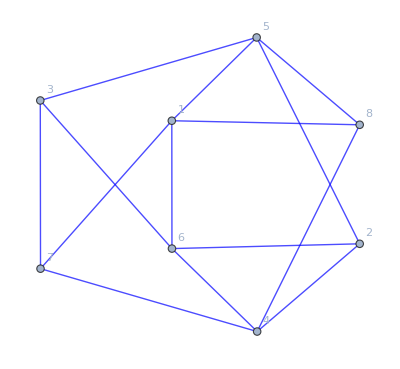
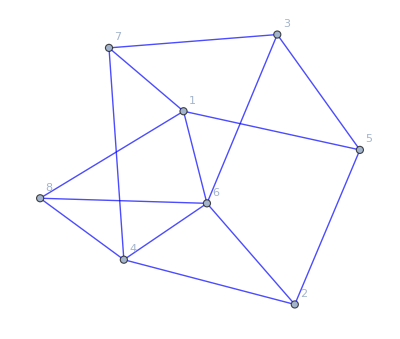
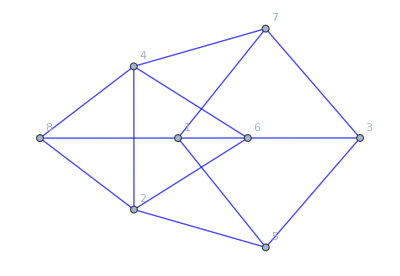
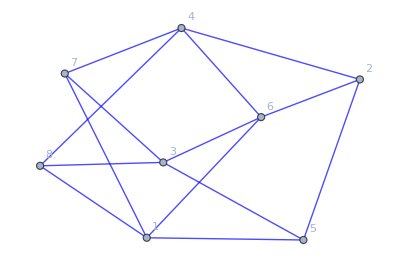
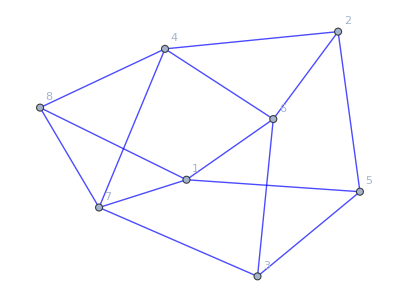
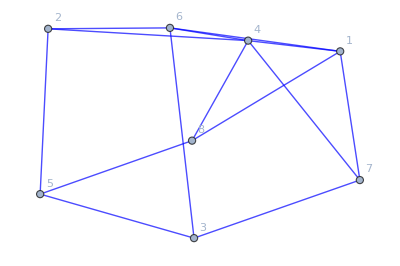
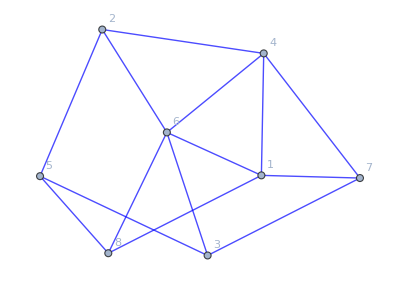
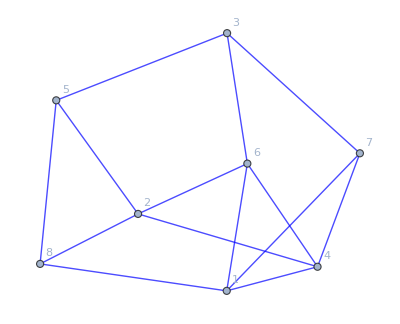
```mathematica
graphs8verts={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

### Data

```mathematica
nodeSpace8verts={{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,6},{-Graphics-,7},{-Graphics-,8},{-Graphics-,9},{-Graphics-,24},{-Graphics-,27},{-Graphics-,29},{-Graphics-,30},{-Graphics-,33}},{{1,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{16,17,18,19,20,21,22},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,{23,24,25,26,27,28,29,30,31},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{4,{32,33,34,35,36,37,38,39,40,41},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{4,Null,<|5->1,6->3,4->4,1->5,2->6,3->7,8->8|>},{5,{42,43,44,45,46,47},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{6,{48,49,50,51,52,53},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{7,{54,55,56,57,58,59,60,61},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{8,{62,63,64,65},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{6,Null,<|6->1,7->3,5->4,4->5,3->6,1->7,2->8|>},{8,Null,<|2->1,8->2,1->4,4->5,5->6,6->8|>},{7,Null,<|6->1,8->2,7->3,5->4,1->5,4->6,3->7|>},{3,Null,<|6->1,5->2,7->3,8->4,3->5,1->6,4->7|>},{4,Null,<|6->1,8->2,5->4,4->5,1->6,2->7,3->8|>},{6,Null,<|6->1,7->3,5->4,4->5,1->6,3->7,2->8|>},{2,Null,<|6->1,8->2,5->4,4->5,1->6,3->7,2->8|>},{5,Null,<|6->1,5->3,7->4,2->5,1->6,3->7,4->8|>},{4,Null,<|2->1,1->2,3->3,8->4,6->5,5->6,4->7|>},{3,Null,<|6->1,8->2,7->3,5->4,4->5,1->6,3->7|>},{6,Null,<|6->1,7->2,5->3,4->4,1->5,3->6,2->7|>},{8,Null,<|5->1,6->2,4->4,1->5,2->6,8->8|>},{3,Null,<|1->1,4->3,3->4,8->5,6->6,7->7,5->8|>},{8,Null,<|5->1,8->3,6->4,4->5,1->6,2->8|>},{9,{66},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{8,Null,<|5->1,6->2,8->3,4->5,1->6,2->8|>},{8,Null,<|1->1,4->2,2->4,8->5,6->6,5->8|>},{10,Null,<|1->1,3->3,5->5,6->6|>},{8,Null,<|5->1,6->2,8->3,2->4,1->5,4->6|>},{11,{67,68,69,70,71},<|1->1,3->3,4->4,5->5,6->6,8->8|>},{12,{72,73,74,75,76,77},<|1->1,3->3,4->4,6->6,7->7,8->8|>},{10,Null,<|1->1,6->3,5->5,3->8|>},{11,Null,<|1->1,3->3,4->4,5->5,6->7,8->8|>},{13,{78,79},<|1->1,3->3,4->4,6->6,7->7|>},{8,Null,<|4->1,5->3,1->4,2->5,8->7,6->8|>},{13,Null,<|6->1,1->3,7->4,4->6,3->7|>},{8,Null,<|4->1,5->3,1->4,2->5,8->6,6->8|>},{12,Null,<|1->1,3->3,4->4,6->5,7->6,8->7|>},{8,Null,<|5->1,8->3,6->4,4->5,1->7,2->8|>},{12,Null,<|6->2,7->3,3->4,4->5,1->6,8->8|>},{8,Null,<|8->1,6->3,2->4,1->5,4->6,5->8|>},{8,Null,<|8->1,6->2,2->4,1->5,4->6,5->8|>},{8,Null,<|1->1,2->3,4->4,5->5,6->6,8->8|>},{13,Null,<|4->2,3->3,1->4,6->5,7->6|>},{8,Null,<|2->1,8->3,1->4,4->5,5->6,6->8|>},{13,Null,<|4->2,3->3,7->4,6->5,1->6|>},{12,Null,<|6->1,7->2,8->3,3->4,4->5,1->6|>},{8,Null,<|5->1,6->3,4->4,1->5,2->6,8->8|>},{8,Null,<|5->1,2->2,8->3,6->4,4->6,1->7|>},{13,Null,<|1->1,4->2,3->3,6->5,7->6|>},{8,Null,<|8->1,2->2,5->3,6->4,4->6,1->7|>},{13,Null,<|6->1,7->2,1->3,4->5,3->6|>},{8,Null,<|8->1,6->2,5->3,2->4,1->5,4->6|>},{12,Null,<|1->1,4->2,3->3,6->5,7->6,8->7|>},{9,Null,<|1->1,2->2,3->3,4->4,5->6,6->7|>},{8,Null,<|6->2,5->3,4->4,1->5,2->6,8->7|>},{8,Null,<|1->1,4->3,2->4,8->5,6->6,5->7|>},{8,Null,<|1->1,8->2,2->3,4->4,5->6,6->7|>},{8,Null,<|8->1,5->2,6->3,2->4,1->5,4->6|>},{13,Null,<|6->1,7->3,1->4,4->6,3->7|>},{12,Null,<|4->1,3->3,1->4,6->5,7->6,8->7|>},{8,Null,<|1->1,4->3,2->4,8->5,5->6,6->7|>},{8,Null,<|1->1,2->3,4->4,5->5,6->7,8->8|>},{9,Null,<|5->1,6->4,1->5,2->6,4->7,3->8|>},{12,Null,<|6->1,8->3,7->4,4->5,1->6,3->7|>},{12,Null,<|1->1,4->3,3->4,6->5,7->6,8->7|>},{10,Null,<|1->1,6->4,5->5,3->8|>},{13,Null,<|4->2,1->4,6->5,7->6,3->8|>},{13,Null,<|6->1,7->4,4->5,3->6,1->8|>},{13,Null,<|6->1,4->2,7->4,1->5,3->8|>},{13,Null,<|6->1,1->2,7->4,4->5,3->6|>},{13,Null,<|6->1,7->4,1->5,4->6,3->8|>},{10,Null,<|6->2,3->4,1->5,5->6|>},{13,Null,<|6->1,7->2,1->4,4->5,3->6|>},{10,Null,<|1->2,5->4,6->5,3->6|>},{10,Null,<|1->1,5->3,6->5,3->6|>},{13,Null,<|1->1,3->3,4->4,6->6,7->8|>},{13,Null,<|1->1,4->3,7->4,6->5,3->8|>},{10,Null,<|1->1,3->3,6->4,5->6|>},{13,Null,<|1->1,4->3,6->5,7->6,3->8|>},{10,Null,<|1->1,6->4,5->6,3->8|>},{13,Null,<|1->1,7->4,6->5,4->6,3->8|>},{13,Null,<|1->1,3->3,4->4,6->5,7->6|>},{13,Null,<|1->1,3->3,4->4,6->7,7->8|>},{13,Null,<|6->1,1->3,7->4,4->7,3->8|>},{13,Null,<|6->1,1->3,7->4,4->6,3->8|>},{10,Null,<|1->1,3->3,6->4,5->7|>},{10,Null,<|1->1,3->3,5->6,6->7|>},{10,Null,<|1->1,3->4,5->6,6->7|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,10,11},{1,8,12},{1,10,13},{1,14,15},{1,16,17},{1,14,18},{1,16,19},{1,20,21},{1,12,9},{1,20,22},{2,23,9},{2,23,24},{2,25,26},{2,11,27},{2,28,29},{2,28,21},{2,24,9},{3,30,31},{3,32,33},{3,34,35},{3,32,29},{3,34,36},{3,29,33},{3,36,35},{3,37,38},{3,37,23},{4,39,40},{4,39,41},{4,42,43},{4,44,45},{4,42,9},{4,44,11},{4,9,43},{4,11,45},{4,46,47},{4,46,21},{6,48,49},{6,50,51},{6,28,33},{6,52,35},{6,37,24},{6,53,54},{7,55,56},{7,57,58},{7,52,35},{7,46,59},{7,60,43},{7,61,45},{8,38,23},{8,62,42},{8,38,37},{8,62,60},{8,23,37},{8,42,60},{8,63,64},{8,65,66},{9,67,68},{9,69,70},{9,71,72},{9,73,66},{24,74,75},{29,76,31},{29,77,78},{29,79,80},{29,81,27},{29,82,66},{30,83,76},{30,84,85},{30,83,33},{30,84,35},{30,76,33},{30,85,35},{33,86,78},{33,87,88}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,6},{-Graphics-,7},{-Graphics-,9},{-Graphics-,11},{-Graphics-,14},{-Graphics-,17},{-Graphics-,18},{-Graphics-,19},{-Graphics-,21},{-Graphics-,23},{-Graphics-,31},{-Graphics-,40}},{{1,{1,2,3,4,5,6,7,8,9,10,11,12,13},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{14,15,16,17,18,19},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{20,21,22,23,24,25},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{4,{26,27,28,29,30,31},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{3,Null,<|2->1,1->2,3->3,8->4,5->5,6->6,4->8|>},{5,{32,33,34,35},<|1->1,3->3,4->4,6->6,7->7,8->8|>},{6,{36,37,38,39,40,41,42,43,44},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,Null,<|7->1,8->3,6->4,1->6,4->7,3->8|>},{7,{45,46,47,48,49,50},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{4,Null,<|1->1,4->2,3->3,2->4,7->5,6->6,5->7|>},{8,{51,52,53,54,55,56,57,58},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{5,Null,<|7->1,8->2,6->4,4->5,1->6,3->8|>},{2,Null,<|4->1,3->3,1->4,2->5,6->6,7->7,8->8|>},{9,{59,60,61,62,63},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{8,Null,<|5->1,8->2,7->3,6->4,1->5,4->6,3->7|>},{6,Null,<|2->1,8->2,3->3,1->4,4->5,6->6,5->7|>},{10,{64,65,66,67,68,69,70},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{11,{71,72,73,74},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{12,{75,76,77,78,79,80,81,82,83,84},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{4,Null,<|6->1,5->2,7->3,2->4,1->5,3->6,4->7|>},{13,Null,<|1->1,4->4,6->6,8->8|>},{5,Null,<|8->2,4->3,1->4,6->6,7->7,3->8|>},{14,{85,86},<|1->1,4->4,6->6,7->7,8->8|>},{9,Null,<|1->1,2->2,5->3,4->4,6->6,8->8|>},{5,Null,<|3->1,8->2,1->3,4->4,6->6,7->7|>},{13,Null,<|6->2,8->3,4->4,1->6|>},{5,Null,<|7->1,8->2,6->4,1->6,4->7,3->8|>},{14,Null,<|8->2,7->3,6->4,1->6,4->7|>},{5,Null,<|3->1,8->2,4->3,1->4,6->6,7->7|>},{5,Null,<|1->2,3->3,8->4,7->5,6->6,4->8|>},{15,{87},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{5,Null,<|3->1,4->2,8->4,7->5,6->6,1->8|>},{14,Null,<|1->1,4->2,8->3,6->5,7->6|>},{5,Null,<|7->1,6->2,8->3,4->5,1->6,3->8|>},{13,Null,<|6->2,4->4,1->6,8->8|>},{13,Null,<|4->2,8->3,1->5,6->6|>},{5,Null,<|7->1,6->2,8->3,3->4,4->5,1->6|>},{5,Null,<|6->2,1->3,4->4,3->5,8->6,7->7|>},{5,Null,<|7->1,8->2,6->3,1->5,4->6,3->7|>},{16,{88,89,90,91,92,93},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{14,Null,<|1->1,8->2,4->3,6->5,7->6|>},{16,Null,<|7->1,6->2,2->3,1->5,4->6,3->7|>},{5,Null,<|7->1,8->2,6->3,4->5,1->6,3->7|>},{14,Null,<|4->2,7->3,6->4,8->6,1->7|>},{14,Null,<|1->1,6->3,4->4,8->6,7->8|>},{14,Null,<|1->1,8->3,4->4,6->6,7->7|>},{14,Null,<|8->1,6->3,1->6,4->7,7->8|>},{14,Null,<|1->1,4->4,8->6,6->7,7->8|>},{13,Null,<|1->1,8->3,6->6,4->7|>},{14,Null,<|8->1,7->3,6->4,1->6,4->7|>},{16,Null,<|1->2,4->3,2->4,7->5,6->6,3->8|>},{5,Null,<|3->1,4->3,8->4,7->5,6->6,1->8|>},{5,Null,<|7->1,8->3,6->4,4->5,1->6,3->8|>},{14,Null,<|6->2,7->3,8->4,1->5,4->6|>},{9,Null,<|1->1,4->3,2->4,8->5,6->6,5->8|>},{14,Null,<|6->2,7->3,4->4,1->5,8->6|>},{16,Null,<|1->1,4->2,3->3,2->4,7->5,6->6|>},{5,Null,<|1->1,8->2,3->3,4->4,6->6,7->7|>},{14,Null,<|8->1,6->2,7->3,1->5,4->6|>},{5,Null,<|1->1,4->2,3->3,8->4,7->5,6->6|>},{5,Null,<|3->1,4->2,1->3,8->4,7->5,6->6|>},{16,Null,<|6->1,2->3,7->4,1->5,4->6,3->7|>},{15,Null,<|1->1,2->2,8->3,3->4,5->5,6->6|>},{16,Null,<|6->1,7->2,2->3,1->5,4->6,3->7|>},{15,Null,<|1->1,2->2,8->3,3->4,5->6,6->7|>},{5,Null,<|1->1,3->3,4->4,7->5,6->6,8->8|>},{16,Null,<|7->1,2->3,6->4,1->5,4->6,3->7|>},{15,Null,<|5->1,6->4,1->5,2->6,8->7,3->8|>},{16,Null,<|1->1,3->3,4->4,6->5,7->6,2->7|>},{16,Null,<|6->1,7->3,2->4,1->5,4->6,3->7|>},{14,Null,<|6->2,4->4,1->5,8->6,7->8|>},{13,Null,<|1->1,6->5,4->6,8->8|>},{14,Null,<|1->1,6->2,4->4,8->6,7->8|>},{13,Null,<|1->1,8->2,6->5,4->6|>},{14,Null,<|1->1,4->4,6->5,8->6,7->8|>},{13,Null,<|4->2,8->4,1->5,6->6|>},{14,Null,<|1->1,4->2,6->5,8->6,7->8|>},{14,Null,<|1->1,4->2,7->4,6->5,8->6|>},{5,Null,<|7->1,6->2,8->4,3->5,4->6,1->7|>},{5,Null,<|7->1,8->2,6->4,1->5,4->6,3->7|>},{5,Null,<|1->1,4->4,3->5,6->6,7->7,8->8|>},{5,Null,<|3->1,8->2,4->4,1->5,6->6,7->7|>},{5,Null,<|1->1,4->2,6->4,7->5,8->6,3->7|>},{13,Null,<|1->1,8->3,6->5,4->7|>},{5,Null,<|1->1,4->3,8->5,7->6,6->7,3->8|>},{14,Null,<|1->1,4->3,8->5,6->6,7->7|>},{5,Null,<|1->1,4->3,3->4,8->5,7->6,6->7|>},{5,Null,<|8->2,3->3,4->4,1->5,6->6,7->7|>},{5,Null,<|4->2,3->3,8->4,7->5,6->6,1->7|>},{14,Null,<|1->1,4->3,6->5,7->6,8->7|>},{5,Null,<|3->1,4->2,8->4,7->5,6->6,1->7|>},{5,Null,<|3->2,4->3,1->4,6->5,7->6,8->7|>},{16,Null,<|1->1,4->2,3->3,6->5,7->6,2->7|>},{5,Null,<|1->2,4->3,3->4,8->5,7->6,6->7|>},{13,Null,<|4->4,1->6,6->7,8->8|>},{13,Null,<|1->1,6->6,4->7,8->8|>},{13,Null,<|1->1,4->4,6->7,8->8|>},{13,Null,<|1->2,6->3,4->5,8->6|>},{14,Null,<|1->1,8->2,4->3,6->6,7->7|>},{14,Null,<|1->1,7->2,4->3,8->6,6->7|>},{14,Null,<|1->1,8->2,4->4,6->6,7->7|>},{14,Null,<|1->1,7->2,4->4,8->6,6->7|>}},{{1,2,3},{1,2,4},{1,5,6},{1,7,8},{1,5,9},{1,7,10},{1,11,12},{1,13,14},{1,11,15},{1,13,16},{1,17,18},{1,17,19},{1,20,21},{2,22,23},{2,24,6},{2,24,25},{2,8,26},{2,27,28},{2,29,21},{3,30,31},{3,30,32},{3,24,33},{3,34,35},{3,14,36},{3,37,21},{4,38,39},{4,40,41},{4,25,33},{4,37,29},{4,42,28},{4,43,44},{6,45,46},{6,47,23},{6,48,49},{6,50,21},{7,51,52},{7,51,32},{7,53,54},{7,55,56},{7,53,12},{7,55,14},{7,12,54},{7,14,56},{7,57,21},{9,58,59},{9,25,33},{9,60,50},{9,61,46},{9,62,63},{9,64,65},{11,6,66},{11,8,53},{11,6,62},{11,8,67},{11,66,62},{11,53,67},{11,68,69},{11,70,21},{14,71,72},{14,73,74},{14,75,76},{14,77,35},{14,78,21},{17,27,79},{17,12,68},{17,12,80},{17,81,14},{17,68,80},{17,81,82},{17,83,21},{18,6,84},{18,85,23},{18,81,86},{18,87,21},{19,88,86},{19,89,90},{19,88,82},{19,89,91},{19,69,92},{19,69,80},{19,93,94},{19,93,79},{19,82,86},{19,91,90},{23,95,96},{23,97,21},{31,98,72},{40,28,99},{40,44,100},{40,28,101},{40,44,102},{40,99,101},{40,100,102}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,11},{-Graphics-,14},{-Graphics-,17},{-Graphics-,20},{-Graphics-,28},{-Graphics-,33},{-Graphics-,46}},{{1,{1,2,3,4,5,6,7,8,9,10},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{11,12,13,14},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{2,Null,<|1->1,4->2,3->3,2->4,7->5,6->6,8->8|>},{3,{15,16,17,18,19,20},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{4,{21,22,23,24,25,26},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,{27,28,29,30,31,32},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{3,Null,<|1->1,2->2,4->3,3->4,8->5,6->6,7->7|>},{3,Null,<|1->1,4->2,3->3,2->4,7->5,6->6,8->8|>},{4,Null,<|1->1,4->2,3->3,2->4,6->6,5->7,8->8|>},{3,Null,<|1->1,3->2,4->3,2->4,7->5,6->6,8->7|>},{6,{33,34,35,36,37,38,39,40,41,42},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{6,Null,<|6->1,5->2,8->3,7->4,2->5,1->6,4->7|>},{3,Null,<|6->1,2->2,7->3,8->4,3->5,4->6,1->7|>},{7,{43,44},<|1->1,2->2,4->4,6->6,8->8|>},{3,Null,<|6->1,8->2,7->3,2->4,1->5,4->6,3->7|>},{7,Null,<|1->1,4->2,2->4,6->6,8->8|>},{8,{45,46,47,48},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{7,Null,<|1->1,2->3,4->4,6->6,8->7|>},{8,Null,<|6->1,3->3,8->4,4->6,1->7,2->8|>},{9,Null,<|2->2,4->4,6->6,8->8|>},{8,Null,<|1->1,2->2,4->4,6->6,3->7,8->8|>},{9,Null,<|6->1,8->3,2->6,4->7|>},{8,Null,<|6->1,2->2,3->3,8->4,4->6,1->7|>},{8,Null,<|4->2,8->3,6->4,2->6,1->7,3->8|>},{8,Null,<|1->1,2->2,4->4,8->6,3->7,6->8|>},{8,Null,<|1->1,4->2,3->3,2->4,6->6,8->8|>},{8,Null,<|3->1,2->2,6->3,8->4,4->6,1->7|>},{10,{49,50,51,52,53,54},<|1->1,2->2,4->4,6->6,7->7,8->8|>},{7,Null,<|2->2,8->3,6->4,1->6,4->7|>},{7,Null,<|4->2,8->3,6->4,2->6,1->7|>},{10,Null,<|6->1,4->2,8->3,7->4,2->6,1->7|>},{8,Null,<|3->1,2->2,8->3,6->4,4->6,1->7|>},{11,{55,56,57,58,59},<|2->2,3->3,4->4,5->5,6->6,8->8|>},{8,Null,<|1->1,4->2,2->3,6->5,8->6,3->8|>},{8,Null,<|1->1,4->2,2->4,3->5,8->6,6->8|>},{7,Null,<|1->1,4->2,2->3,6->5,8->6|>},{8,Null,<|1->1,4->2,2->3,8->5,6->6,3->8|>},{8,Null,<|1->1,4->2,2->4,3->5,6->6,8->8|>},{9,Null,<|4->2,8->3,6->5,2->6|>},{8,Null,<|1->1,4->2,2->3,3->4,8->5,6->6|>},{7,Null,<|2->1,6->2,8->3,1->5,4->6|>},{8,Null,<|6->1,8->2,3->3,2->4,1->5,4->6|>},{7,Null,<|2->1,8->3,6->4,1->6,4->7|>},{8,Null,<|3->1,8->2,6->3,2->4,1->5,4->6|>},{10,Null,<|2->1,4->3,1->4,6->5,7->6,8->7|>},{12,{60},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{10,Null,<|2->1,1->2,4->3,6->5,7->6,8->7|>},{12,Null,<|1->1,2->2,3->3,4->4,5->6,6->7|>},{8,Null,<|1->1,4->2,2->4,3->5,6->7,8->8|>},{8,Null,<|1->1,4->2,2->4,3->5,8->6,6->7|>},{8,Null,<|6->1,4->2,8->4,3->5,1->7,2->8|>},{8,Null,<|6->1,8->2,4->4,1->5,3->7,2->8|>},{8,Null,<|6->1,4->2,8->4,3->5,2->6,1->7|>},{8,Null,<|6->1,8->2,4->4,1->5,2->6,3->7|>},{10,Null,<|1->1,2->2,4->4,6->5,7->6,8->8|>},{8,Null,<|1->1,2->2,4->4,6->5,3->7,8->8|>},{8,Null,<|1->1,2->2,4->4,6->5,8->6,3->7|>},{9,Null,<|6->1,4->2,2->6,8->8|>},{9,Null,<|6->1,2->2,4->4,8->8|>},{9,Null,<|6->1,4->2,8->4,2->6|>},{7,Null,<|6->2,8->3,2->4,1->6,4->8|>},{7,Null,<|1->1,2->3,4->4,6->6,8->8|>},{7,Null,<|1->1,6->3,4->4,2->6,8->8|>},{9,Null,<|6->1,8->3,4->4,2->6|>},{7,Null,<|1->1,6->2,8->3,4->4,2->6|>},{7,Null,<|1->1,2->2,4->4,6->7,8->8|>},{7,Null,<|1->1,4->2,2->4,6->7,8->8|>},{7,Null,<|1->1,2->2,4->4,6->6,8->7|>},{7,Null,<|1->1,4->2,2->4,6->6,8->7|>},{7,Null,<|2->2,8->3,6->4,1->6,4->8|>},{9,Null,<|2->2,4->3,6->5,8->8|>},{7,Null,<|2->2,6->3,4->4,1->5,8->8|>},{9,Null,<|2->2,8->3,4->4,6->6|>},{7,Null,<|2->2,6->3,1->5,4->6,8->8|>},{7,Null,<|2->2,4->4,1->5,6->6,8->8|>},{7,Null,<|2->2,8->3,6->4,1->5,4->6|>},{9,Null,<|2->2,4->4,6->5,8->8|>},{9,Null,<|6->2,2->4,4->5,8->6|>},{9,Null,<|6->1,2->3,4->5,8->6|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,3,6},{1,8,10},{1,11,12},{1,13,14},{1,15,16},{2,17,18},{2,19,20},{2,21,22},{2,23,14},{4,24,25},{4,26,27},{4,28,29},{4,21,30},{4,31,14},{4,32,16},{5,33,34},{5,33,35},{5,26,36},{5,37,20},{5,38,39},{5,40,16},{6,23,41},{6,27,36},{6,42,43},{6,44,18},{6,45,46},{6,47,48},{11,28,49},{11,28,50},{11,51,14},{11,52,16},{11,51,53},{11,52,54},{11,55,56},{11,55,57},{11,53,14},{11,54,16},{14,20,58},{14,59,60},{17,61,62},{17,63,20},{17,16,64},{17,65,14},{28,66,14},{28,67,16},{28,66,68},{28,67,69},{28,14,68},{28,16,69},{33,70,71},{33,72,73},{33,74,20},{33,75,39},{33,76,77},{46,78,79}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,8},{-Graphics-,9},{-Graphics-,17},{-Graphics-,20},{-Graphics-,23},{-Graphics-,27},{-Graphics-,28},{-Graphics-,30},{-Graphics-,64}},{{1,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{18,19,20,21,22,23,24,25},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{26,27,28,29,30,31},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{2,Null,<|3->1,2->2,4->3,1->4,6->6,7->7,8->8|>},{3,Null,<|3->1,2->2,1->3,4->4,5->5,6->6,8->8|>},{3,Null,<|6->1,2->2,8->3,5->4,4->5,1->6,3->7|>},{3,Null,<|3->1,2->2,1->3,4->4,5->5,6->6,8->7|>},{4,{32,33,34,35,36,37},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,{38,39,40,41,42,43},<|1->1,3->3,4->4,6->6,7->7,8->8|>},{3,Null,<|6->1,5->2,8->3,2->4,3->5,1->6,4->8|>},{5,Null,<|1->1,4->3,3->4,6->6,7->7,8->8|>},{3,Null,<|3->1,4->2,1->3,2->4,8->5,6->6,5->8|>},{5,Null,<|4->1,3->3,1->4,6->6,7->7,8->8|>},{4,Null,<|1->1,2->2,3->3,4->4,5->5,6->6,8->7|>},{3,Null,<|6->1,5->2,8->3,2->4,3->5,1->6,4->7|>},{3,Null,<|3->1,4->2,1->3,2->4,8->5,6->6,5->7|>},{6,{44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,Null,<|7->1,2->2,8->3,6->4,1->5,4->6,3->8|>},{2,Null,<|1->1,4->3,3->4,2->5,6->6,7->7,8->8|>},{7,{62,63,64,65,66,67,68,69,70},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{2,Null,<|7->1,2->2,8->3,6->4,1->5,4->6,3->7|>},{7,Null,<|1->1,2->2,3->3,4->4,5->5,6->6,8->7|>},{8,{71,72,73,74},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{8,Null,<|4->1,2->2,3->3,1->4,6->6,8->8|>},{8,Null,<|6->1,3->2,2->3,8->4,1->6,4->7|>},{8,Null,<|4->1,2->2,3->3,1->4,6->6,8->7|>},{9,Null,<|1->1,2->2,4->4,6->6|>},{10,{75},<|1->1,2->2,4->4,6->6,7->7,8->8|>},{5,Null,<|6->1,8->3,7->4,4->6,1->7,3->8|>},{11,{76,77},<|1->1,2->2,3->3,5->5,6->6|>},{5,Null,<|6->1,3->2,8->3,7->4,1->6,4->8|>},{11,Null,<|5->1,1->2,6->3,2->5,3->6|>},{5,Null,<|1->1,3->2,4->3,6->5,7->6,8->8|>},{11,Null,<|5->1,1->2,6->4,2->6,3->8|>},{8,Null,<|6->1,2->2,8->3,4->5,1->6,3->8|>},{11,Null,<|5->1,2->2,6->4,1->6,3->8|>},{8,Null,<|1->1,6->2,4->4,3->5,2->6,8->8|>},{8,Null,<|6->1,2->2,8->3,1->5,4->6,3->8|>},{8,Null,<|2->1,6->2,8->3,3->4,4->5,1->6|>},{8,Null,<|3->1,2->2,1->3,4->4,6->6,8->8|>},{11,Null,<|5->1,6->2,1->3,2->5,3->6|>},{5,Null,<|1->1,3->3,4->4,6->5,7->6,8->8|>},{10,Null,<|6->1,7->2,2->3,8->4,1->5,4->6|>},{5,Null,<|1->1,4->2,3->3,6->5,7->6,8->8|>},{10,Null,<|6->1,7->2,2->3,8->4,1->6,4->8|>},{8,Null,<|6->1,8->2,2->3,3->4,4->5,1->6|>},{11,Null,<|1->1,3->3,2->4,5->6,6->8|>},{8,Null,<|2->1,8->2,6->3,3->4,4->5,1->6|>},{11,Null,<|5->1,1->3,6->4,2->6,3->8|>},{11,Null,<|1->1,3->3,2->4,5->7,6->8|>},{11,Null,<|5->1,1->3,6->4,2->7,3->8|>},{11,Null,<|1->1,3->3,2->4,5->6,6->7|>},{11,Null,<|5->1,1->3,6->4,2->6,3->7|>},{5,Null,<|1->1,3->3,4->4,6->5,7->7,8->8|>},{5,Null,<|1->1,4->3,3->4,6->5,7->7,8->8|>},{5,Null,<|4->1,3->3,1->4,6->5,7->7,8->8|>},{5,Null,<|1->1,4->3,3->4,6->5,7->6,8->8|>},{5,Null,<|4->1,3->3,1->4,6->5,7->6,8->8|>},{5,Null,<|1->1,3->3,4->4,6->5,7->6,8->7|>},{5,Null,<|1->1,4->3,3->4,6->5,7->6,8->7|>},{5,Null,<|4->1,3->3,1->4,6->5,7->6,8->7|>},{8,Null,<|2->2,3->3,4->4,1->5,6->6,8->8|>},{11,Null,<|5->1,6->3,1->5,2->6,3->8|>},{12,{78,79,80,81,82},<|2->2,3->3,4->4,5->5,6->6,8->8|>},{11,Null,<|5->1,6->3,2->5,1->6,3->8|>},{8,Null,<|3->1,2->2,4->4,1->5,6->6,8->8|>},{12,Null,<|5->1,4->2,8->4,2->5,6->6,3->8|>},{5,Null,<|6->1,8->3,7->4,1->5,3->6,4->8|>},{9,Null,<|2->2,4->4,1->5,6->6|>},{5,Null,<|6->1,7->2,8->3,1->5,3->6,4->8|>},{8,Null,<|1->2,4->3,3->4,2->5,6->6,8->8|>},{8,Null,<|4->1,1->2,3->4,2->5,6->6,8->8|>},{11,Null,<|1->1,2->2,3->3,5->6,6->8|>},{9,Null,<|1->1,2->3,6->6,4->8|>},{11,Null,<|5->1,2->2,3->3,6->4,1->6|>},{9,Null,<|1->1,6->4,2->7,4->8|>},{9,Null,<|1->1,6->2,2->4,4->6|>},{9,Null,<|1->1,2->2,4->3,6->6|>},{9,Null,<|1->1,2->2,4->3,6->5|>},{9,Null,<|1->1,4->3,6->5,2->6|>},{9,Null,<|1->1,4->2,6->5,2->6|>},{11,Null,<|5->2,3->3,2->4,1->6,6->8|>},{9,Null,<|2->2,4->3,1->5,6->6|>},{11,Null,<|3->3,2->4,5->5,1->6,6->8|>},{11,Null,<|2->2,3->3,5->5,1->6,6->8|>},{9,Null,<|6->2,2->4,1->6,4->8|>},{11,Null,<|2->2,6->4,5->5,1->6,3->8|>},{9,Null,<|2->3,1->5,6->6,4->8|>},{11,Null,<|2->2,3->3,6->4,5->5,1->6|>},{9,Null,<|2->3,6->4,1->6,4->8|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,10,11},{1,12,13},{1,8,14},{1,10,15},{1,12,16},{1,17,18},{1,19,20},{1,17,21},{1,19,22},{1,14,9},{1,15,11},{1,16,13},{2,23,9},{2,24,13},{2,23,25},{2,24,26},{2,11,27},{2,28,29},{2,25,9},{2,26,13},{3,23,30},{3,31,32},{3,33,34},{3,35,36},{3,37,38},{3,39,24},{8,23,30},{8,40,41},{8,42,43},{8,44,45},{8,46,47},{8,48,49},{9,50,47},{9,51,49},{9,50,52},{9,51,53},{9,47,52},{9,49,53},{17,9,54},{17,11,55},{17,13,56},{17,9,42},{17,11,57},{17,13,58},{17,9,59},{17,11,60},{17,13,61},{17,54,42},{17,55,57},{17,56,58},{17,54,59},{17,55,60},{17,56,61},{17,42,59},{17,57,60},{17,58,61},{20,62,63},{20,64,65},{20,62,66},{20,64,67},{20,68,69},{20,70,71},{20,70,72},{20,66,63},{20,67,65},{23,47,27},{23,73,34},{23,36,74},{23,75,49},{28,76,77},{30,78,79},{30,80,81},{64,82,83},{64,84,69},{64,85,86},{64,87,88},{64,89,90}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,7},{-Graphics-,9},{-Graphics-,10},{-Graphics-,11},{-Graphics-,12},{-Graphics-,14},{-Graphics-,15},{-Graphics-,16},{-Graphics-,24},{-Graphics-,37},{-Graphics-,45}},{{1,{1,2,3,4,5,6,7,8,9},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{10,11,12,13},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{14,15,16,17,18,19},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{4,{20,21,22,23,24,25,26,27},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{5,{28},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{2,Null,<|4->1,3->3,1->4,2->5,6->6,7->7,8->8|>},{6,{29},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{4,Null,<|5->1,8->2,6->3,7->4,1->5,4->6,3->7|>},{7,{30,31,32,33,34,35,36,37,38},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{8,{39,40,41,42,43,44,45},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{9,{46,47,48,49,50,51},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{10,{52,53,54,55,56,57,58,59,60,61},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{3,Null,<|6->1,5->2,7->3,2->4,1->5,3->6,4->7|>},{11,Null,<|1->1,4->4,7->7,8->8|>},{12,{62,63,64,65},<|2->2,3->3,4->4,6->6,7->7,8->8|>},{13,{66,67},<|1->1,4->4,6->6,7->7,8->8|>},{12,Null,<|7->1,2->3,6->4,3->6,4->7,8->8|>},{11,Null,<|7->2,8->3,4->4,1->6|>},{12,Null,<|7->1,2->2,6->4,3->6,4->7,8->8|>},{13,Null,<|8->2,7->3,6->4,1->6,4->7|>},{12,Null,<|8->1,2->2,3->3,4->4,6->6,7->7|>},{12,Null,<|6->2,4->3,3->4,8->5,2->6,7->7|>},{12,Null,<|7->1,2->2,6->3,4->5,3->6,8->7|>},{14,{68,69,70,71,72,73},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{13,Null,<|1->1,8->2,4->3,6->5,7->6|>},{12,Null,<|8->1,2->2,4->3,3->4,6->6,7->7|>},{13,Null,<|1->1,4->2,8->3,6->5,7->6|>},{12,Null,<|7->1,6->2,2->3,8->4,3->5,4->6|>},{14,Null,<|7->1,6->2,2->3,1->5,4->6,3->7|>},{12,Null,<|7->1,2->2,6->3,3->5,4->6,8->7|>},{13,Null,<|4->2,7->3,6->4,8->6,1->7|>},{12,Null,<|4->1,8->3,3->4,7->6,6->7,2->8|>},{12,Null,<|4->1,8->3,3->4,7->5,6->7,2->8|>},{12,Null,<|7->1,2->3,6->4,3->5,4->7,8->8|>},{14,Null,<|6->1,2->3,7->4,1->5,4->6,3->7|>},{14,Null,<|7->1,2->3,6->4,1->5,4->6,3->7|>},{15,{74},<|1->1,4->4,5->5,6->6,7->7,8->8|>},{14,Null,<|1->1,3->3,4->4,6->5,2->6,7->7|>},{14,Null,<|6->1,7->3,2->4,1->5,4->6,3->7|>},{13,Null,<|1->1,4->2,8->4,6->5,7->6|>},{11,Null,<|1->1,7->4,4->7,8->8|>},{13,Null,<|1->1,4->2,6->4,7->5,8->6|>},{12,Null,<|2->2,8->3,3->4,4->5,6->6,7->7|>},{13,Null,<|1->1,4->3,8->5,6->6,7->7|>},{16,{75,76,77,78,79},<|2->2,3->3,4->4,5->5,6->6,7->7|>},{13,Null,<|1->1,4->3,6->5,8->6,7->7|>},{12,Null,<|8->1,2->2,3->4,4->5,6->6,7->7|>},{16,Null,<|5->1,7->2,4->4,3->5,6->6,2->7|>},{11,Null,<|4->2,8->4,1->5,7->6|>},{14,Null,<|1->1,4->2,3->3,6->5,2->6,7->7|>},{12,Null,<|4->2,3->3,8->4,2->5,6->6,7->7|>},{12,Null,<|7->1,6->2,2->4,8->5,4->6,3->7|>},{15,Null,<|1->1,6->2,4->4,5->6,7->7,8->8|>},{12,Null,<|4->1,7->2,3->4,8->5,6->7,2->8|>},{16,Null,<|5->1,7->2,4->4,3->5,6->7,2->8|>},{12,Null,<|4->1,6->2,3->4,8->5,2->6,7->7|>},{12,Null,<|7->1,6->2,2->4,8->5,3->6,4->7|>},{12,Null,<|4->1,3->4,8->5,7->6,6->7,2->8|>},{12,Null,<|4->1,3->2,6->4,7->5,2->6,8->7|>},{11,Null,<|1->1,8->3,7->5,4->7|>},{16,Null,<|5->1,4->3,7->4,2->5,6->7,3->8|>},{12,Null,<|7->1,6->3,2->4,8->5,3->6,4->7|>},{12,Null,<|4->1,3->3,2->5,7->6,6->7,8->8|>},{12,Null,<|4->1,3->3,8->4,2->5,7->6,6->7|>},{12,Null,<|3->2,8->3,2->4,7->5,6->6,4->7|>},{13,Null,<|1->1,4->3,6->5,7->6,8->7|>},{12,Null,<|8->1,3->2,2->4,7->5,6->6,4->7|>},{14,Null,<|1->1,3->3,4->4,6->5,7->6,2->7|>},{12,Null,<|8->2,3->3,4->4,6->5,7->6,2->7|>},{12,Null,<|7->1,2->2,6->4,4->5,3->6,8->7|>},{14,Null,<|1->1,4->2,3->3,6->5,7->6,2->7|>},{12,Null,<|4->2,3->3,8->4,2->5,7->6,6->7|>},{13,Null,<|1->2,7->3,6->4,8->6,4->8|>},{13,Null,<|7->3,6->4,1->6,4->7,8->8|>},{13,Null,<|6->3,8->4,1->6,4->7,7->8|>},{13,Null,<|6->2,8->4,1->6,4->7,7->8|>},{11,Null,<|4->4,1->6,7->7,8->8|>},{11,Null,<|1->1,7->6,4->7,8->8|>},{11,Null,<|1->1,4->4,7->6,8->8|>},{13,Null,<|1->1,8->2,4->3,6->6,7->7|>},{13,Null,<|1->1,7->2,4->3,8->6,6->7|>},{13,Null,<|1->1,8->2,4->4,6->6,7->7|>},{13,Null,<|1->1,7->2,4->4,8->6,6->7|>},{11,Null,<|1->1,7->4,4->5,8->6|>},{11,Null,<|4->2,8->3,1->5,7->6|>},{13,Null,<|6->2,7->3,4->4,1->5,8->6|>},{11,Null,<|8->3,4->4,1->6,7->7|>},{13,Null,<|7->3,6->4,1->5,8->6,4->7|>},{13,Null,<|6->2,7->3,1->5,8->6,4->7|>},{11,Null,<|4->2,8->4,1->6,7->7|>},{13,Null,<|7->2,4->4,1->5,8->6,6->7|>},{11,Null,<|8->3,1->5,7->6,4->7|>}},{{1,2,3},{1,4,5},{1,6,7},{1,4,8},{1,6,9},{1,10,11},{1,7,9},{1,10,12},{1,13,14},{2,15,16},{2,17,18},{2,19,20},{2,21,14},{3,22,23},{3,24,25},{3,26,27},{3,28,21},{3,29,20},{3,30,31},{4,32,33},{4,17,34},{4,32,35},{4,17,36},{4,33,35},{4,34,36},{4,37,38},{4,39,14},{5,40,41},{7,42,41},{9,43,44},{9,45,46},{9,43,47},{9,45,48},{9,38,49},{9,50,51},{9,50,52},{9,47,44},{9,48,46},{10,53,54},{10,19,55},{10,53,56},{10,19,57},{10,54,56},{10,58,47},{10,59,14},{11,32,60},{11,61,17},{11,61,62},{11,63,16},{11,58,44},{11,64,14},{12,43,44},{12,65,66},{12,43,47},{12,65,67},{12,68,69},{12,68,70},{12,71,72},{12,71,57},{12,47,44},{12,67,66},{15,73,74},{15,75,18},{15,76,20},{15,31,77},{16,77,78},{16,14,79},{24,20,80},{24,31,81},{24,20,82},{24,31,83},{24,80,82},{24,81,83},{37,41,84},{45,31,85},{45,86,87},{45,88,49},{45,89,90},{45,91,92}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,7},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,11},{-Graphics-,14},{-Graphics-,15},{-Graphics-,24},{-Graphics-,28},{-Graphics-,46}},{{1,{1,2,3,4,5,6,7,8,9,10,11},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{12,13,14,15,16,17,18,19,20},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,{21,22},<|1->1,3->3,4->4,6->6,7->7|>},{4,{23,24,25,26,27,28,29,30,31},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|4->1,3->3,1->4,6->6,7->7|>},{4,Null,<|6->1,5->3,4->4,8->5,2->6,3->7,1->8|>},{5,{32,33,34,35,36},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{6,{37,38,39,40,41,42},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{7,{43,44,45,46},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{8,{47,48,49,50,51,52},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{9,{53,54,55,56,57,58},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{4,Null,<|6->1,8->2,4->4,5->5,1->6,2->7,3->8|>},{6,Null,<|1->1,3->3,4->4,5->5,7->6,6->7,8->8|>},{10,{59,60,61,62,63,64,65},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{11,{66,67,68,69,70,71},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{7,Null,<|4->1,5->2,6->4,8->5,2->6,1->8|>},{4,Null,<|4->1,5->3,6->4,8->5,2->6,3->7,1->8|>},{7,Null,<|4->1,8->3,6->4,5->5,1->6,2->8|>},{7,Null,<|4->1,2->3,1->4,5->5,6->6,8->8|>},{7,Null,<|1->1,2->2,8->3,6->4,5->5,4->6|>},{5,Null,<|1->1,2->2,8->3,6->4,5->5,4->6|>},{5,Null,<|4->1,5->3,1->4,2->5,8->6,6->8|>},{7,Null,<|4->1,5->2,1->3,2->4,8->5,6->6|>},{12,Null,<|1->1,3->3,6->6,7->7|>},{12,Null,<|1->1,6->4,7->6,3->7|>},{12,Null,<|1->1,3->3,6->4,7->7|>},{12,Null,<|1->1,3->3,6->4,7->6|>},{13,{72,73,74,75,76,77},<|2->2,3->3,4->4,5->5,6->6,8->8|>},{12,Null,<|1->1,6->4,7->6,3->8|>},{5,Null,<|1->1,5->3,4->4,2->5,8->6,6->8|>},{3,Null,<|6->2,7->3,1->4,3->5,4->6|>},{7,Null,<|1->1,2->3,4->4,5->5,6->6,8->8|>},{3,Null,<|6->2,7->3,4->4,3->5,1->6|>},{13,Null,<|2->1,3->2,8->3,4->4,5->5,6->6|>},{7,Null,<|6->1,8->3,4->4,5->5,1->6,2->8|>},{3,Null,<|6->2,1->4,3->5,4->6,7->8|>},{3,Null,<|4->1,6->2,1->4,3->5,7->8|>},{12,Null,<|1->1,3->2,6->4,7->6|>},{3,Null,<|4->1,1->4,3->5,6->6,7->8|>},{12,Null,<|7->2,1->4,3->5,6->6|>},{3,Null,<|4->1,3->2,1->4,6->6,7->8|>},{12,Null,<|6->2,1->4,7->5,3->8|>},{3,Null,<|4->1,3->2,1->4,7->5,6->6|>},{12,Null,<|1->1,6->4,7->5,3->8|>},{13,Null,<|4->1,5->3,6->4,2->6,3->7,8->8|>},{14,{78},<|1->1,3->3,4->4,5->5,6->6,8->8|>},{13,Null,<|4->1,6->4,5->5,2->6,3->7,8->8|>},{14,Null,<|1->1,3->3,4->4,5->5,6->6,8->7|>},{7,Null,<|6->1,8->3,2->4,1->5,4->6,5->7|>},{3,Null,<|1->1,4->4,3->5,6->6,7->8|>},{7,Null,<|2->1,8->3,6->4,1->5,4->6,5->7|>},{3,Null,<|6->2,4->4,3->5,1->6,7->8|>},{3,Null,<|1->2,4->4,3->5,6->6,7->8|>},{3,Null,<|4->1,3->2,6->4,7->5,1->6|>},{7,Null,<|2->2,8->3,6->4,5->5,4->6,1->7|>},{7,Null,<|2->1,1->2,8->3,6->4,4->6,5->7|>},{3,Null,<|1->2,3->3,4->4,7->5,6->6|>},{5,Null,<|1->1,2->2,4->4,5->5,6->6,8->7|>},{7,Null,<|2->2,8->3,6->4,4->5,5->6,1->7|>},{7,Null,<|2->1,8->3,6->4,1->5,5->6,4->7|>},{5,Null,<|6->2,5->3,1->4,2->5,4->6,8->7|>},{12,Null,<|6->2,3->3,7->5,1->6|>},{7,Null,<|2->1,1->2,6->4,8->5,4->6,5->7|>},{7,Null,<|2->2,1->3,5->4,4->5,6->6,8->7|>},{7,Null,<|5->2,1->3,2->4,8->5,6->6,4->7|>},{7,Null,<|6->2,4->3,5->4,1->5,2->6,8->7|>},{13,Null,<|4->1,5->3,6->4,8->5,2->6,3->7|>},{7,Null,<|5->1,4->2,1->3,2->4,8->5,6->6|>},{7,Null,<|4->1,5->2,6->4,8->5,2->6,1->7|>},{7,Null,<|6->1,8->3,2->4,1->5,5->6,4->7|>},{3,Null,<|6->3,1->4,3->5,4->6,7->8|>},{3,Null,<|6->3,4->4,3->5,1->6,7->8|>},{12,Null,<|1->3,6->5,7->6,3->8|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,6,10},{1,8,11},{1,12,13},{1,12,14},{1,15,16},{1,10,7},{1,15,17},{2,18,7},{2,19,9},{2,18,20},{2,19,21},{2,16,22},{2,16,23},{2,9,21},{2,23,22},{2,20,7},{3,24,25},{3,26,27},{4,28,29},{4,30,31},{4,32,33},{4,30,7},{4,32,9},{4,7,31},{4,9,33},{4,34,35},{4,34,16},{7,36,29},{7,37,38},{7,39,40},{7,41,42},{7,43,44},{8,19,3},{8,32,5},{8,45,46},{8,47,48},{8,49,50},{8,51,39},{9,52,29},{9,39,40},{9,41,53},{9,54,50},{10,55,25},{10,20,3},{10,51,40},{10,56,57},{10,58,59},{10,58,60},{11,61,25},{11,21,3},{11,51,40},{11,56,62},{11,63,64},{11,63,48},{14,65,25},{14,60,59},{14,48,64},{14,60,58},{14,48,63},{14,56,66},{14,63,64},{15,23,3},{15,34,5},{15,67,43},{15,49,54},{15,56,68},{15,69,70},{28,71,36},{28,72,52},{28,71,31},{28,72,33},{28,36,31},{28,52,33},{46,73,29}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,6},{-Graphics-,7},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,12},{-Graphics-,13},{-Graphics-,18},{-Graphics-,19},{-Graphics-,50}},{{1,{1,2,3,4,5,6,7,8,9,10,11},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{12,13,14,15,16,17,18,19,20},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,{21,22},<|1->1,3->3,4->4,6->6,7->7|>},{2,Null,<|4->1,3->2,8->3,1->4,5->5,6->6,2->8|>},{3,Null,<|4->1,3->3,1->4,6->6,7->7|>},{4,{23,24,25,26,27,28},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{5,{29,30,31,32},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{6,{33,34,35,36,37,38},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{7,{39,40,41,42,43},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{8,{44,45,46,47,48,49},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{6,Null,<|4->1,8->2,3->3,1->4,5->5,6->6,7->7|>},{9,{50,51,52,53,54,55,56,57,58},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{10,{59,60,61,62,63,64,65},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{10,Null,<|4->1,8->2,3->3,1->4,5->5,6->6,7->7|>},{4,Null,<|4->1,8->2,3->3,1->4,5->5,6->6,7->7|>},{5,Null,<|6->1,5->2,2->4,8->5,4->6,1->8|>},{8,Null,<|4->1,3->3,1->4,5->5,6->6,7->7,2->8|>},{11,{66,67,68,69,70,71},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{12,Null,<|1->1,2->2,4->4,6->6|>},{11,Null,<|1->1,3->3,2->4,5->5,6->6,8->8|>},{5,Null,<|1->1,2->2,8->3,4->4,5->5,6->6|>},{3,Null,<|1->1,6->3,3->5,4->6,7->8|>},{3,Null,<|4->1,6->3,3->5,1->6,7->8|>},{5,Null,<|6->1,5->2,1->3,2->4,8->5,4->6|>},{7,Null,<|1->1,2->2,8->3,4->4,5->5,6->6|>},{12,Null,<|1->1,2->3,4->6,6->7|>},{12,Null,<|1->1,4->4,6->6,2->7|>},{12,Null,<|1->1,2->3,4->4,6->7|>},{12,Null,<|1->1,2->3,4->4,6->6|>},{5,Null,<|1->1,2->3,4->4,5->5,6->6,8->8|>},{5,Null,<|4->1,8->3,2->4,6->6,5->7,1->8|>},{5,Null,<|2->1,1->3,5->4,8->5,4->6,6->8|>},{5,Null,<|6->1,4->4,5->5,1->6,2->7,8->8|>},{5,Null,<|2->1,8->3,4->4,1->5,5->6,6->7|>},{11,Null,<|1->1,5->3,6->4,8->5,2->6,3->7|>},{3,Null,<|1->1,4->4,7->5,6->6,3->8|>},{5,Null,<|2->1,8->3,4->4,1->5,6->6,5->7|>},{3,Null,<|4->1,6->4,3->5,1->6,7->8|>},{3,Null,<|6->2,1->4,3->5,4->6,7->8|>},{12,Null,<|1->1,4->4,6->6,2->8|>},{12,Null,<|6->2,1->4,2->5,4->6|>},{3,Null,<|4->1,3->2,6->4,1->6,7->8|>},{3,Null,<|1->2,4->4,7->5,6->6,3->8|>},{3,Null,<|4->1,3->2,1->4,7->5,6->6|>},{7,Null,<|1->1,5->3,2->5,6->6,8->7,4->8|>},{7,Null,<|1->1,5->3,8->4,2->5,6->6,4->8|>},{12,Null,<|6->3,4->5,1->6,2->8|>},{5,Null,<|4->1,2->4,8->5,6->6,5->7,1->8|>},{5,Null,<|5->1,1->3,6->5,4->6,8->7,2->8|>},{13,{72},<|1->1,3->3,4->4,5->5,6->6,7->7|>},{5,Null,<|4->1,8->3,2->4,1->5,6->6,5->7|>},{12,Null,<|1->1,6->5,4->6,2->8|>},{3,Null,<|6->2,4->4,3->5,1->6,7->8|>},{3,Null,<|4->1,6->2,3->5,1->6,7->8|>},{12,Null,<|4->2,6->5,1->6,2->8|>},{3,Null,<|4->1,3->2,6->4,7->5,1->6|>},{5,Null,<|2->2,8->3,4->4,5->5,6->6,1->7|>},{5,Null,<|2->1,1->2,8->3,4->4,6->6,5->7|>},{3,Null,<|1->2,3->3,4->4,7->5,6->6|>},{7,Null,<|1->1,2->2,6->4,5->5,4->6,8->7|>},{5,Null,<|2->2,8->3,4->4,6->5,5->6,1->7|>},{7,Null,<|6->1,1->4,2->5,8->6,4->7,5->8|>},{5,Null,<|6->1,5->2,4->4,8->5,2->6,1->7|>},{5,Null,<|2->1,1->2,4->4,8->5,6->6,5->7|>},{5,Null,<|1->1,2->3,5->5,6->6,4->7,8->8|>},{5,Null,<|5->1,6->3,1->5,2->6,8->7,4->8|>},{5,Null,<|4->1,8->3,2->4,1->5,5->6,6->7|>},{5,Null,<|4->1,8->3,6->5,5->6,1->7,2->8|>},{3,Null,<|1->1,6->2,3->5,4->6,7->8|>},{3,Null,<|1->1,6->2,7->3,3->5,4->6|>},{3,Null,<|4->1,6->2,7->3,3->5,1->6|>},{12,Null,<|1->3,4->5,6->6,2->7|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,6,10},{1,8,11},{1,12,13},{1,12,14},{1,15,16},{1,11,9},{1,15,17},{2,18,19},{2,20,7},{2,20,21},{2,16,22},{2,9,23},{2,16,24},{2,9,25},{2,24,22},{2,25,23},{3,26,27},{3,28,29},{6,20,3},{6,30,5},{6,31,32},{6,33,34},{6,35,36},{6,37,38},{7,39,40},{7,38,41},{7,42,43},{7,44,36},{8,45,27},{8,46,5},{8,31,47},{8,48,49},{8,48,50},{8,51,52},{9,53,40},{9,54,19},{9,38,41},{9,42,55},{9,56,52},{10,57,27},{10,21,3},{10,37,41},{10,58,59},{10,60,61},{10,60,34},{12,16,62},{12,7,33},{12,16,63},{12,7,60},{12,48,9},{12,33,60},{12,48,64},{12,64,9},{12,63,62},{13,65,27},{13,31,66},{13,48,49},{13,48,50},{13,67,68},{13,50,49},{13,67,62},{18,22,69},{18,23,54},{18,22,70},{18,23,71},{18,69,70},{18,54,71},{50,72,27}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,6},{-Graphics-,7},{-Graphics-,11},{-Graphics-,12},{-Graphics-,13},{-Graphics-,20},{-Graphics-,29}},{{1,{1,2,3,4,5},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{6,7,8,9,10,11,12},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,{13,14},<|1->1,3->3,4->4,6->6,7->7|>},{4,{15,16,17,18,19,20},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|4->1,3->3,1->4,6->6,7->7|>},{5,{21,22,23,24,25,26},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{6,{27,28,29,30},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{2,Null,<|1->1,2->2,6->4,5->5,4->6,3->7,8->8|>},{2,Null,<|4->1,3->2,8->3,6->4,5->5,1->6,2->7|>},{5,Null,<|6->1,7->2,8->3,4->4,3->5,1->6,2->7|>},{7,{31},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{8,{32,33,34,35},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{9,Null,<|1->1,2->2,4->4,6->6|>},{8,Null,<|1->1,5->2,6->3,8->4,2->6,3->8|>},{8,Null,<|8->1,3->2,2->3,6->5,5->6,1->8|>},{8,Null,<|2->1,3->2,8->3,1->5,5->6,6->8|>},{8,Null,<|5->1,1->2,8->4,6->5,2->6,3->8|>},{8,Null,<|5->1,6->2,8->3,1->5,2->6,3->8|>},{8,Null,<|1->1,5->2,6->3,8->4,3->5,2->6|>},{10,{36,37,38,39,40},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{9,Null,<|1->1,2->3,4->6,6->7|>},{9,Null,<|1->1,4->4,6->6,2->7|>},{9,Null,<|1->1,2->3,4->4,6->7|>},{9,Null,<|1->1,2->3,4->4,6->6|>},{8,Null,<|2->2,3->3,1->4,5->5,6->6,8->8|>},{3,Null,<|4->1,3->2,1->4,6->6,7->8|>},{8,Null,<|2->2,3->3,6->4,5->5,1->6,8->8|>},{3,Null,<|4->1,3->2,6->4,1->6,7->8|>},{11,{41,42,43,44,45,46},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{7,Null,<|1->2,2->3,4->4,5->5,6->6,8->8|>},{8,Null,<|5->1,1->2,2->4,6->5,8->6,3->8|>},{3,Null,<|6->2,7->3,1->4,3->5,4->6|>},{3,Null,<|6->2,7->3,4->4,3->5,1->6|>},{11,Null,<|1->1,2->2,3->3,4->4,8->5,6->6|>},{11,Null,<|4->1,8->3,6->4,1->6,2->7,3->8|>},{8,Null,<|2->1,3->3,8->4,1->6,5->7,6->8|>},{8,Null,<|1->1,5->2,2->4,8->6,6->7,3->8|>},{8,Null,<|2->1,3->3,8->4,5->6,1->7,6->8|>},{8,Null,<|8->1,6->2,3->3,2->4,1->6,5->7|>},{8,Null,<|5->1,1->2,6->3,8->4,2->6,3->8|>},{8,Null,<|2->2,3->3,8->4,6->5,5->6,1->8|>},{8,Null,<|8->1,2->2,3->3,6->5,5->6,1->8|>},{9,Null,<|1->2,6->3,4->5,2->8|>},{3,Null,<|6->2,7->3,1->5,4->6,3->8|>},{9,Null,<|1->1,4->2,6->5,2->8|>},{9,Null,<|1->1,4->2,6->4,2->6|>},{3,Null,<|4->1,1->2,6->3,3->5,7->8|>},{9,Null,<|1->1,6->2,2->3,4->6|>},{3,Null,<|1->1,6->2,7->3,4->6,3->8|>},{3,Null,<|4->1,6->2,7->3,3->5,1->8|>},{3,Null,<|4->1,1->2,3->5,6->6,7->8|>},{3,Null,<|4->1,6->2,7->3,3->5,1->6|>},{3,Null,<|1->1,6->2,7->3,3->5,4->6|>},{3,Null,<|4->1,7->3,6->4,3->5,1->6|>},{9,Null,<|6->2,1->4,2->5,4->6|>},{3,Null,<|4->1,3->2,7->3,6->4,1->6|>},{9,Null,<|4->2,2->3,6->5,1->6|>},{3,Null,<|4->1,3->2,6->4,7->5,1->6|>},{9,Null,<|1->1,2->3,6->5,4->6|>},{3,Null,<|6->2,7->3,1->4,4->6,3->8|>},{3,Null,<|4->1,3->3,1->4,6->6,7->8|>},{3,Null,<|6->2,7->3,4->4,1->6,3->8|>},{3,Null,<|4->1,3->3,6->4,1->6,7->8|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},{2,12,13},{2,14,15},{2,11,16},{2,17,18},{2,11,19},{2,17,20},{2,19,16},{3,21,22},{3,23,24},{4,25,26},{4,27,28},{4,29,30},{4,31,32},{4,17,33},{4,34,11},{6,14,3},{6,29,5},{6,35,26},{6,36,28},{6,37,38},{6,39,40},{7,41,26},{7,42,13},{7,40,43},{7,17,44},{11,45,46},{12,47,48},{12,49,50},{12,51,52},{12,53,45},{20,33,24},{20,52,13},{20,54,55},{20,56,57},{20,58,59},{29,60,61},{29,62,63},{29,60,26},{29,62,28},{29,61,26},{29,63,28}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,6},{-Graphics-,7},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,12},{-Graphics-,16},{-Graphics-,17},{-Graphics-,18},{-Graphics-,37},{-Graphics-,38},{-Graphics-,52}},{{1,{1,2,3,4,5,6,7,8,9},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{10,11,12,13},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,{14,15},<|1->1,3->3,4->4,6->6,7->7|>},{4,{16,17,18,19,20,21},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|4->1,3->3,1->4,6->6,7->7|>},{5,{22,23,24,25,26,27,28,29,30,31},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{6,{32,33,34,35,36,37,38},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{7,{39,40,41,42},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{8,{43,44,45,46,47,48},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{9,{49,50,51,52,53,54},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{8,Null,<|3->1,2->2,1->3,5->4,4->5,6->6,8->7|>},{10,{55,56,57,58,59,60},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{7,Null,<|7->1,6->2,8->3,4->4,5->5,1->6,3->8|>},{10,Null,<|6->1,7->2,8->3,4->4,3->5,1->6,2->7|>},{7,Null,<|6->1,7->2,8->3,4->4,3->5,1->6,5->8|>},{11,{61},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{12,{62,63,64,65},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{13,Null,<|1->1,2->2,4->4,6->6|>},{12,Null,<|1->1,3->3,2->4,5->5,6->6,8->8|>},{12,Null,<|8->1,6->2,5->3,1->4,2->5,3->6|>},{12,Null,<|3->1,2->2,8->3,6->4,1->6,5->8|>},{12,Null,<|6->1,5->2,1->3,8->5,2->6,3->8|>},{12,Null,<|3->1,2->2,8->3,6->4,5->5,1->6|>},{13,Null,<|1->1,6->3,4->5,2->8|>},{13,Null,<|1->1,2->3,4->6,6->7|>},{13,Null,<|1->1,4->4,6->6,2->7|>},{13,Null,<|1->1,2->3,4->4,6->7|>},{13,Null,<|1->1,2->3,4->4,6->6|>},{12,Null,<|2->2,3->3,1->4,5->5,6->6,8->8|>},{3,Null,<|4->1,3->3,1->4,6->6,7->8|>},{12,Null,<|2->2,3->3,6->4,5->5,1->6,8->8|>},{3,Null,<|4->1,3->3,6->4,1->6,7->8|>},{12,Null,<|2->1,3->3,1->4,8->5,6->6,5->8|>},{3,Null,<|6->2,7->3,1->4,3->5,4->6|>},{12,Null,<|2->1,3->3,6->4,8->5,1->6,5->8|>},{3,Null,<|6->2,7->3,4->4,3->5,1->6|>},{14,{66,67,68,69,70,71},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{15,{72},<|2->2,3->3,4->4,5->5,6->6,8->8|>},{14,Null,<|1->1,2->2,3->3,4->4,8->5,6->6|>},{15,Null,<|2->1,3->3,4->4,5->5,6->6,8->8|>},{12,Null,<|1->1,3->3,2->4,5->5,6->7,8->8|>},{12,Null,<|2->1,3->3,1->4,8->5,6->7,5->8|>},{14,Null,<|4->1,8->3,6->4,1->6,2->7,3->8|>},{12,Null,<|6->1,5->3,1->4,8->5,2->7,3->8|>},{12,Null,<|6->1,5->3,1->4,8->5,2->6,3->8|>},{14,Null,<|4->1,8->3,6->4,3->5,1->6,2->7|>},{12,Null,<|1->1,5->3,6->4,3->5,2->7,8->8|>},{12,Null,<|1->1,5->3,6->4,3->5,2->6,8->8|>},{12,Null,<|6->2,5->3,1->4,3->5,2->6,8->8|>},{15,Null,<|6->2,5->3,4->4,3->5,2->6,8->8|>},{12,Null,<|6->1,8->3,2->4,5->5,1->6,3->8|>},{16,{73,74,75,76,77},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{12,Null,<|8->1,6->2,1->4,2->5,3->6,5->8|>},{12,Null,<|2->1,8->3,6->4,3->5,1->6,5->8|>},{13,Null,<|6->2,1->4,2->5,4->6|>},{12,Null,<|2->1,3->3,8->5,1->6,6->7,5->8|>},{12,Null,<|1->1,5->3,6->4,3->6,2->7,8->8|>},{13,Null,<|6->3,4->5,1->6,2->8|>},{12,Null,<|1->1,5->3,6->4,8->5,3->6,2->7|>},{3,Null,<|4->1,3->3,1->5,6->6,7->8|>},{12,Null,<|6->2,8->3,2->4,3->5,1->6,5->8|>},{15,Null,<|4->1,8->3,6->4,5->5,2->6,3->8|>},{12,Null,<|8->1,6->2,3->4,2->5,1->6,5->8|>},{12,Null,<|2->1,6->2,8->3,3->5,1->6,5->8|>},{16,Null,<|1->1,2->2,6->4,5->5,4->6,8->8|>},{16,Null,<|1->1,2->2,8->3,6->4,5->5,4->6|>},{3,Null,<|4->1,1->3,3->5,6->6,7->8|>},{12,Null,<|6->2,5->3,1->4,2->5,3->6,8->7|>},{12,Null,<|6->1,5->3,1->4,8->5,3->6,2->7|>},{12,Null,<|6->1,8->2,5->3,1->4,3->6,2->7|>},{3,Null,<|1->2,3->3,4->4,7->5,6->6|>},{16,Null,<|1->1,2->2,4->4,5->5,6->6,8->7|>},{12,Null,<|6->2,5->3,1->4,3->5,2->6,8->7|>},{12,Null,<|6->1,5->3,1->4,8->5,2->6,3->7|>},{3,Null,<|4->1,3->2,1->4,6->6,7->8|>},{3,Null,<|4->1,3->2,6->4,1->6,7->8|>},{12,Null,<|3->1,2->2,1->4,6->6,8->7,5->8|>},{12,Null,<|1->1,5->3,6->4,2->6,3->7,8->8|>},{12,Null,<|2->1,3->2,8->3,6->4,1->6,5->8|>},{3,Null,<|1->1,4->3,3->4,6->6,7->7|>},{13,Null,<|1->1,4->3,6->5,2->8|>},{3,Null,<|4->1,6->2,1->3,3->5,7->8|>},{13,Null,<|1->1,6->2,2->3,4->6|>},{3,Null,<|4->1,6->2,7->3,3->5,1->6|>},{3,Null,<|1->1,6->2,7->3,4->6,3->8|>},{3,Null,<|4->1,6->2,7->3,3->5,1->8|>},{3,Null,<|1->1,6->2,7->3,3->5,4->6|>},{3,Null,<|6->2,7->3,1->4,4->6,3->8|>},{3,Null,<|6->2,7->3,4->4,1->6,3->8|>},{13,Null,<|1->2,4->3,6->5,2->8|>},{13,Null,<|1->2,4->3,6->4,2->6|>},{3,Null,<|6->2,1->4,3->5,4->6,7->8|>},{13,Null,<|1->1,4->4,6->6,2->8|>},{3,Null,<|4->1,6->2,1->4,3->5,7->8|>},{3,Null,<|4->1,1->4,3->5,6->6,7->8|>},{13,Null,<|4->2,1->4,6->5,2->8|>},{3,Null,<|4->1,3->2,1->4,7->5,6->6|>},{13,Null,<|1->1,4->4,6->5,2->8|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,6,10},{1,8,11},{1,12,13},{1,14,15},{1,14,16},{2,17,18},{2,19,20},{2,21,22},{2,23,24},{3,25,26},{3,27,28},{4,29,30},{4,31,32},{4,33,34},{4,35,36},{4,37,38},{4,39,40},{6,41,19},{6,42,33},{6,41,3},{6,42,5},{6,19,3},{6,33,5},{6,43,44},{6,43,45},{6,46,47},{6,46,48},{7,49,45},{7,50,51},{7,49,52},{7,50,53},{7,54,55},{7,53,51},{7,20,19},{8,56,26},{8,35,5},{8,57,58},{8,59,60},{9,61,62},{9,61,63},{9,64,18},{9,54,55},{9,65,58},{9,66,67},{10,68,26},{10,20,3},{10,69,55},{10,70,71},{10,72,73},{10,72,74},{12,21,3},{12,37,5},{12,43,75},{12,57,76},{12,77,78},{12,70,79},{16,80,81},{17,82,83},{17,67,84},{17,85,86},{17,87,24},{37,88,30},{37,89,32},{37,88,75},{37,89,76},{37,30,75},{37,32,76},{38,90,91},{52,92,93},{52,94,18},{52,95,55},{52,75,96},{52,97,98}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,14},{-Graphics-,15},{-Graphics-,16},{-Graphics-,27},{-Graphics-,28},{-Graphics-,32}},{{1,{1,2,3,4,5,6,7,8,9,10},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{11,12,13,14,15,16},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{3,{17,18,19,20,21,22},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{4,{23,24,25,26,27,28,29},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{5,{30,31,32,33},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{6,{34,35,36,37,38,39},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{3,Null,<|7->1,6->2,5->3,1->4,2->5,4->6,8->7|>},{5,Null,<|4->1,5->2,6->4,8->5,2->6,1->7,7->8|>},{3,Null,<|1->1,5->3,7->4,2->5,8->6,4->7,6->8|>},{4,Null,<|4->1,8->2,3->3,1->4,5->5,7->6,6->7|>},{2,Null,<|4->1,8->2,3->3,1->4,5->5,7->6,6->7|>},{6,Null,<|4->1,3->3,1->4,5->5,7->6,6->7,2->8|>},{3,Null,<|4->1,8->2,1->4,5->5,7->6,6->7,2->8|>},{7,{40,41,42,43,44,45},<|1->1,3->3,4->4,5->5,7->7,8->8|>},{8,{46,47},<|1->1,3->3,4->4,6->6,7->7|>},{9,{48,49,50,51},<|1->1,3->3,4->4,5->5,7->7,8->8|>},{8,Null,<|4->1,3->3,1->4,6->6,7->7|>},{9,Null,<|4->1,8->3,3->4,5->6,7->7,1->8|>},{9,Null,<|3->1,1->3,5->4,8->5,4->7,7->8|>},{9,Null,<|7->1,4->4,5->5,3->6,1->7,8->8|>},{9,Null,<|3->1,8->3,4->4,1->5,7->6,5->7|>},{7,Null,<|1->1,5->3,7->4,8->5,4->6,3->7|>},{8,Null,<|1->1,4->4,7->5,6->7,3->8|>},{9,Null,<|3->1,8->3,4->4,1->5,5->6,7->7|>},{8,Null,<|4->1,6->4,3->5,1->7,7->8|>},{9,Null,<|7->1,3->2,4->4,5->5,1->7,8->8|>},{10,Null,<|1->1,2->2,4->4,6->6|>},{11,{52,53,54,55,56},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{10,Null,<|1->1,4->4,6->7,2->8|>},{10,Null,<|6->2,1->4,2->5,4->6|>},{9,Null,<|7->1,5->2,4->4,3->6,1->7,8->8|>},{12,{57},<|1->1,2->2,4->4,5->5,7->7,8->8|>},{9,Null,<|5->1,7->2,4->4,1->5,3->6,8->8|>},{11,Null,<|1->1,2->2,4->4,5->5,6->6,8->7|>},{9,Null,<|1->1,3->3,5->5,4->6,7->7,8->8|>},{10,Null,<|1->1,4->4,6->6,2->7|>},{9,Null,<|5->1,7->3,1->5,8->6,3->7,4->8|>},{9,Null,<|4->1,3->4,8->5,5->6,7->7,1->8|>},{9,Null,<|5->1,1->3,7->5,8->6,4->7,3->8|>},{12,Null,<|1->1,5->3,7->4,2->5,4->6,8->7|>},{9,Null,<|4->1,8->3,3->4,1->5,7->6,5->7|>},{9,Null,<|4->1,8->3,7->5,1->6,5->7,3->8|>},{11,Null,<|4->1,1->4,2->5,6->6,8->7,5->8|>},{9,Null,<|1->1,3->2,7->4,5->5,4->6,8->8|>},{9,Null,<|5->1,7->2,3->4,1->5,4->6,8->8|>},{9,Null,<|3->1,1->2,4->4,8->5,7->6,5->7|>},{9,Null,<|3->2,8->3,4->4,5->5,7->6,1->7|>},{9,Null,<|1->1,3->2,8->3,4->4,5->5,7->6|>},{9,Null,<|3->1,1->2,8->3,4->4,7->6,5->7|>},{8,Null,<|1->2,3->3,4->4,7->5,6->6|>},{9,Null,<|3->2,8->3,4->4,7->5,5->6,1->7|>},{8,Null,<|1->1,6->3,3->5,4->7,7->8|>},{8,Null,<|4->1,6->3,3->5,1->7,7->8|>},{8,Null,<|1->1,3->3,4->4,7->5,6->7|>},{8,Null,<|4->1,7->3,6->4,3->5,1->7|>},{10,Null,<|1->1,2->3,4->6,6->7|>},{10,Null,<|1->1,2->3,4->4,6->7|>},{10,Null,<|1->1,2->3,4->4,6->6|>},{8,Null,<|6->3,1->4,3->5,4->7,7->8|>},{8,Null,<|4->1,3->3,6->4,1->7,7->8|>},{8,Null,<|1->3,4->4,7->5,6->7,3->8|>},{10,Null,<|2->3,1->4,6->5,4->7|>},{8,Null,<|4->1,3->3,1->4,7->5,6->7|>},{8,Null,<|6->2,1->4,3->5,4->6,7->8|>},{10,Null,<|1->1,4->4,6->6,2->8|>},{8,Null,<|4->1,6->2,1->4,3->5,7->8|>},{8,Null,<|4->1,1->4,3->5,6->6,7->8|>},{8,Null,<|4->1,3->2,1->4,6->6,7->8|>},{10,Null,<|4->2,1->4,6->5,2->8|>},{8,Null,<|4->1,3->2,1->4,7->5,6->6|>},{10,Null,<|1->1,4->4,6->5,2->8|>},{10,Null,<|1->2,4->4,6->5,2->8|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,5,7},{1,8,10},{1,11,12},{1,10,9},{1,11,13},{2,14,15},{2,16,17},{2,18,19},{2,20,21},{2,22,23},{2,24,25},{3,26,27},{3,28,29},{3,20,30},{3,31,32},{3,31,33},{3,34,25},{4,35,36},{4,18,37},{4,38,39},{4,38,40},{4,41,42},{4,40,39},{4,41,43},{5,44,29},{5,20,30},{5,31,45},{5,46,38},{6,47,36},{6,48,15},{6,21,30},{6,49,50},{6,34,51},{6,34,24},{14,52,23},{14,53,25},{14,52,54},{14,53,55},{14,23,54},{14,25,55},{15,56,36},{15,57,58},{16,59,29},{16,60,61},{16,25,62},{16,63,23},{28,64,65},{28,66,27},{28,67,30},{28,68,69},{28,70,71},{32,72,29}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,6},{-Graphics-,7},{-Graphics-,8},{-Graphics-,10},{-Graphics-,20},{-Graphics-,21},{-Graphics-,25},{-Graphics-,28},{-Graphics-,49}},{{1,{1,2,3,4,5,6,7,8,9,10,11,12,13},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{14,15,16,17,18,19},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{20,21,22,23},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{4,{24,25,26,27,28,29,30},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{4,Null,<|4->1,5->2,7->3,2->4,1->5,3->6,6->8|>},{5,{31,32,33,34},<|1->1,3->3,4->4,6->6,7->7,8->8|>},{6,{35,36,37,38,39,40,41,42,43},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{7,{44,45,46,47,48},<|1->1,3->3,4->4,6->6,7->7,8->8|>},{4,Null,<|2->1,1->2,3->3,4->4,5->5,7->6,6->7|>},{8,{49,50,51,52,53,54},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{6,Null,<|6->1,5->3,4->4,2->5,1->6,3->7,8->8|>},{7,Null,<|1->1,6->2,4->4,8->5,3->6,7->8|>},{4,Null,<|3->1,1->3,2->4,7->5,4->6,5->7,6->8|>},{5,Null,<|6->1,7->2,4->4,3->5,1->6,8->8|>},{8,Null,<|7->1,6->2,5->3,4->4,3->5,2->6,1->7|>},{4,Null,<|7->1,6->2,5->3,4->4,3->5,2->6,1->7|>},{2,Null,<|6->1,7->2,4->4,3->5,1->6,2->7,8->8|>},{3,Null,<|6->1,5->3,4->4,3->5,1->6,2->7,8->8|>},{4,Null,<|6->1,7->2,5->3,4->4,3->5,1->6,2->7|>},{9,{55,56,57,58,59,60},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{10,Null,<|1->1,4->4,6->6,8->8|>},{5,Null,<|7->2,3->3,4->4,1->6,6->7,8->8|>},{10,Null,<|1->1,4->4,6->7,8->8|>},{5,Null,<|6->1,7->2,3->3,4->4,1->6,8->8|>},{11,{61},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{10,Null,<|4->2,8->3,1->4,6->6|>},{7,Null,<|1->1,6->2,4->4,3->6,8->7,7->8|>},{12,{62,63},<|2->2,3->3,4->4,6->6,7->7|>},{5,Null,<|8->1,7->2,3->3,4->4,1->6,6->7|>},{5,Null,<|4->2,8->3,7->4,6->5,1->6,3->8|>},{5,Null,<|8->1,3->2,1->4,6->5,7->6,4->8|>},{5,Null,<|6->1,1->2,4->3,3->4,8->5,7->6|>},{10,Null,<|4->2,8->3,1->5,6->6|>},{5,Null,<|6->1,1->2,7->3,8->4,3->5,4->6|>},{5,Null,<|4->2,1->3,6->4,7->5,8->6,3->7|>},{5,Null,<|8->1,3->2,7->3,6->4,1->5,4->7|>},{5,Null,<|8->1,1->2,3->3,4->4,7->6,6->7|>},{7,Null,<|1->1,4->2,3->3,8->4,7->5,6->6|>},{5,Null,<|4->1,1->2,3->3,8->4,7->5,6->7|>},{5,Null,<|4->1,3->2,1->3,6->4,7->5,8->7|>},{5,Null,<|6->1,7->2,1->3,4->4,3->5,8->7|>},{12,Null,<|4->1,7->3,2->4,3->6,6->8|>},{10,Null,<|1->1,8->3,4->4,6->7|>},{12,Null,<|2->1,3->3,4->4,7->7,6->8|>},{12,Null,<|4->1,6->3,7->4,3->6,2->8|>},{12,Null,<|4->1,2->4,3->6,7->7,6->8|>},{12,Null,<|4->1,6->3,7->4,3->6,2->7|>},{12,Null,<|2->1,3->3,4->4,6->6,7->7|>},{13,{64,65,66,67,68,69},<|2->2,3->3,4->4,5->5,6->6,8->8|>},{5,Null,<|8->1,3->3,1->4,6->5,7->6,4->8|>},{7,Null,<|1->1,3->3,4->4,7->5,6->6,8->8|>},{12,Null,<|7->2,6->3,2->4,4->5,3->6|>},{5,Null,<|6->1,7->3,4->4,3->5,1->6,8->8|>},{12,Null,<|7->2,6->3,4->4,3->5,2->6|>},{13,Null,<|2->1,3->2,8->3,4->4,5->5,6->6|>},{12,Null,<|7->3,2->4,3->6,4->7,6->8|>},{12,Null,<|4->1,3->3,2->4,7->7,6->8|>},{10,Null,<|6->3,1->4,4->6,8->8|>},{10,Null,<|8->3,1->4,6->6,4->7|>},{12,Null,<|4->1,3->3,2->4,6->6,7->7|>},{5,Null,<|3->2,4->3,1->4,6->5,7->6,8->7|>},{12,Null,<|4->1,3->3,7->4,6->5,2->7|>},{7,Null,<|1->1,8->2,3->3,4->4,6->6,7->7|>},{5,Null,<|8->1,4->2,3->3,1->4,6->5,7->6|>},{5,Null,<|4->1,8->2,3->3,1->4,6->5,7->7|>},{5,Null,<|8->1,3->2,4->3,1->4,6->5,7->6|>},{5,Null,<|6->1,1->3,4->4,3->5,7->6,8->7|>},{5,Null,<|4->1,3->2,8->3,7->4,6->5,1->6|>},{13,Null,<|4->1,5->3,6->4,2->5,8->6,3->7|>},{12,Null,<|4->1,3->2,2->4,7->5,6->6|>},{5,Null,<|4->1,3->3,8->4,7->5,1->6,6->7|>},{12,Null,<|4->1,3->2,7->4,6->5,2->6|>},{5,Null,<|4->1,3->2,1->4,6->5,7->6,8->7|>},{5,Null,<|4->1,3->3,8->4,7->5,6->6,1->7|>},{10,Null,<|1->2,4->3,6->4,8->6|>},{10,Null,<|1->1,4->3,6->4,8->7|>},{10,Null,<|4->2,8->3,6->6,1->7|>},{10,Null,<|6->2,1->4,8->6,4->7|>},{10,Null,<|6->2,8->3,1->4,4->7|>},{12,Null,<|7->3,2->4,4->5,3->6,6->8|>},{12,Null,<|7->2,2->4,4->5,3->6,6->8|>},{12,Null,<|7->3,4->4,3->5,2->6,6->8|>},{12,Null,<|7->2,4->4,3->5,2->6,6->8|>}},{{1,2,3},{1,2,4},{1,5,6},{1,7,8},{1,5,9},{1,7,10},{1,11,12},{1,13,14},{1,11,15},{1,13,16},{1,17,18},{1,17,19},{1,20,21},{2,22,23},{2,24,6},{2,24,25},{2,8,26},{2,27,28},{2,29,21},{3,30,31},{3,24,32},{3,14,33},{3,34,21},{4,35,36},{4,37,38},{4,25,32},{4,37,39},{4,25,40},{4,32,40},{4,41,26},{6,42,43},{6,44,45},{6,46,47},{6,48,21},{7,49,50},{7,49,31},{7,51,52},{7,53,54},{7,51,12},{7,53,14},{7,12,52},{7,14,54},{7,55,21},{8,56,23},{8,42,43},{8,57,58},{8,46,59},{8,60,21},{10,61,62},{10,63,64},{10,63,65},{10,66,43},{10,67,54},{10,41,26},{20,29,34},{20,68,48},{20,55,60},{20,69,70},{20,71,72},{20,73,74},{25,75,76},{28,77,78},{28,26,79},{49,80,81},{49,82,83},{49,80,52},{49,82,54},{49,81,52},{49,83,54}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,5},{-Graphics-,8},{-Graphics-,9},{-Graphics-,15},{-Graphics-,23},{-Graphics-,28},{-Graphics-,35},{-Graphics-,38},{-Graphics-,44}},{{1,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{16,17,18,19,20,21,22,23,24,25},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,{26,27,28,29,30,31},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,Null,<|4->1,3->2,8->3,1->4,6->5,5->6,2->8|>},{4,{32,33,34,35,36,37,38},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{4,Null,<|4->1,8->2,3->3,1->4,6->5,5->6,7->7|>},{3,Null,<|4->1,8->2,3->3,1->4,6->5,5->6,7->7|>},{5,{39,40,41,42,43,44},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{6,{45,46,47,48},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{4,Null,<|1->1,6->3,5->4,4->5,3->6,8->7,7->8|>},{6,Null,<|6->1,1->2,8->4,4->5,5->6,2->8|>},{3,Null,<|7->1,5->2,6->3,1->4,3->5,8->6,4->7|>},{4,Null,<|5->1,7->2,6->3,1->4,3->5,4->6,8->7|>},{4,Null,<|4->1,5->2,1->4,3->5,8->6,7->7,6->8|>},{7,{49,50,51,52,53,54,55,56,57},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{4,Null,<|1->1,6->2,4->4,8->5,3->6,7->7,5->8|>},{4,Null,<|1->1,6->3,7->4,8->5,3->6,4->7,5->8|>},{4,Null,<|7->1,5->2,6->3,1->4,3->5,8->6,4->7|>},{7,Null,<|8->1,4->2,3->3,1->4,6->5,7->6,5->7|>},{5,Null,<|4->1,8->2,3->3,1->4,6->5,5->6,7->7|>},{6,Null,<|4->1,8->2,1->4,6->5,5->6,2->8|>},{3,Null,<|1->1,6->3,5->4,4->5,3->6,8->7,7->8|>},{8,{58,59,60,61,62,63},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{6,Null,<|5->1,4->2,2->4,1->5,6->6,8->8|>},{6,Null,<|5->1,4->2,8->3,2->4,1->5,6->6|>},{8,Null,<|1->1,3->3,2->4,5->5,6->6,8->8|>},{6,Null,<|1->1,2->2,8->3,4->4,5->5,6->6|>},{9,{64,65},<|1->1,3->3,5->5,6->6,8->8|>},{9,Null,<|5->1,3->3,1->5,6->6,8->8|>},{6,Null,<|4->1,8->2,2->3,1->4,6->5,5->6|>},{6,Null,<|6->1,1->2,2->3,8->4,4->5,5->6|>},{6,Null,<|5->1,4->3,1->5,6->6,2->7,8->8|>},{9,Null,<|5->1,8->3,3->4,6->6,1->7|>},{6,Null,<|4->1,5->3,6->4,8->6,2->7,1->8|>},{10,Null,<|1->1,3->3,5->5,8->8|>},{6,Null,<|5->1,4->3,2->4,1->5,6->6,8->8|>},{10,Null,<|1->1,8->3,5->4,3->7|>},{11,{66,67,68,69,70},<|1->1,3->3,4->4,5->5,7->7,8->8|>},{6,Null,<|5->1,8->3,4->4,6->6,1->7,2->8|>},{6,Null,<|5->1,8->3,2->4,1->5,6->6,4->8|>},{6,Null,<|4->1,5->3,6->4,1->5,8->6,2->7|>},{6,Null,<|6->1,5->3,4->4,1->6,2->7,8->8|>},{6,Null,<|6->1,5->3,8->4,2->5,1->6,4->8|>},{12,{71},<|1->1,3->3,4->4,5->5,7->7,8->8|>},{6,Null,<|4->1,8->3,5->4,6->5,1->7,2->8|>},{11,Null,<|4->1,3->3,1->4,5->6,7->7,8->8|>},{6,Null,<|2->1,8->3,5->4,6->5,1->6,4->8|>},{6,Null,<|6->1,5->3,4->4,8->5,1->6,2->7|>},{6,Null,<|6->1,1->3,8->4,4->5,5->6,2->8|>},{9,Null,<|1->1,6->3,5->4,3->5,8->7|>},{6,Null,<|1->1,2->3,4->4,5->5,6->6,8->8|>},{9,Null,<|5->1,6->3,1->4,3->5,8->7|>},{6,Null,<|4->1,8->3,2->4,5->5,6->7,1->8|>},{6,Null,<|2->1,1->3,6->4,4->5,8->6,5->8|>},{6,Null,<|5->1,4->4,1->5,6->6,2->7,8->8|>},{6,Null,<|2->1,8->3,4->4,6->5,1->6,5->7|>},{8,Null,<|1->1,6->3,5->4,2->5,8->6,3->7|>},{9,Null,<|1->1,5->4,3->5,8->6,6->8|>},{6,Null,<|2->1,8->3,4->4,5->5,1->6,6->7|>},{9,Null,<|5->1,3->4,1->5,6->6,8->8|>},{9,Null,<|3->2,1->4,5->5,6->6,8->8|>},{10,Null,<|1->1,5->4,3->5,8->8|>},{10,Null,<|3->2,1->4,5->5,8->6|>},{9,Null,<|5->1,6->2,3->4,1->5,8->8|>},{9,Null,<|1->2,5->4,3->5,8->6,6->8|>},{9,Null,<|5->1,6->2,1->4,3->5,8->6|>},{6,Null,<|4->1,8->3,5->5,6->6,1->7,2->8|>},{11,Null,<|1->1,4->4,5->5,7->6,8->7,3->8|>},{6,Null,<|1->1,2->3,5->5,6->6,4->7,8->8|>},{6,Null,<|5->1,2->4,1->5,6->6,4->7,8->8|>},{6,Null,<|4->1,8->3,2->4,1->5,6->6,5->7|>},{11,Null,<|4->1,3->3,8->4,7->5,5->6,1->7|>},{6,Null,<|4->1,6->4,5->5,8->6,2->7,1->8|>},{11,Null,<|4->1,3->3,1->5,5->6,7->7,8->8|>},{6,Null,<|2->1,1->3,6->4,5->5,8->6,4->7|>},{9,Null,<|1->1,3->2,5->5,6->6,8->8|>},{9,Null,<|5->1,3->2,1->5,6->6,8->8|>},{9,Null,<|1->1,3->2,8->3,5->5,6->6|>},{9,Null,<|5->1,3->2,8->3,1->5,6->6|>},{10,Null,<|1->1,3->3,5->6,8->8|>},{10,Null,<|1->1,5->5,3->6,8->8|>},{10,Null,<|1->1,8->3,5->5,3->6|>},{9,Null,<|1->1,3->3,5->5,6->7,8->8|>},{10,Null,<|1->1,5->4,3->7,8->8|>},{9,Null,<|1->1,6->3,5->4,3->7,8->8|>},{9,Null,<|1->1,3->3,5->4,6->5,8->8|>},{9,Null,<|1->1,5->4,6->5,3->7,8->8|>},{10,Null,<|1->1,8->3,5->5,3->7|>},{10,Null,<|1->1,5->3,3->5,8->8|>},{10,Null,<|1->1,5->3,3->4,8->7|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,10,11},{1,8,12},{1,10,13},{1,14,15},{1,16,17},{1,14,18},{1,16,19},{1,20,21},{1,13,11},{1,20,22},{2,23,24},{2,23,25},{2,26,9},{2,26,27},{2,21,28},{2,11,29},{2,21,30},{2,11,31},{2,30,28},{2,31,29},{3,32,33},{3,34,35},{3,36,37},{3,38,39},{3,38,40},{3,41,29},{5,42,43},{5,42,44},{5,36,37},{5,45,46},{5,44,43},{5,45,47},{5,48,49},{8,26,50},{8,51,52},{8,53,54},{8,55,56},{8,57,58},{8,59,60},{9,61,62},{9,60,63},{9,64,65},{9,66,58},{15,67,68},{15,69,70},{15,67,71},{15,69,72},{15,73,74},{15,73,75},{15,70,72},{15,75,74},{15,71,68},{23,28,76},{23,29,77},{23,28,78},{23,29,79},{23,76,78},{23,77,79},{28,80,35},{28,81,82},{38,83,84},{38,85,35},{38,86,37},{38,87,88},{38,50,62},{44,89,90}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,13},{-Graphics-,14},{-Graphics-,17},{-Graphics-,18},{-Graphics-,28},{-Graphics-,35},{-Graphics-,42}},{{1,{1,2,3,4,5,6,7,8,9,10},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{11,12,13,14},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{15,16,17,18,19,20,21,22,23,24},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{4,{25,26,27,28,29,30},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{5,{31,32,33,34,35,36,37,38,39},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{6,{40,41,42,43,44,45,46},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{6,Null,<|2->1,1->2,3->3,4->4,5->5,7->6,6->7|>},{7,{47,48,49,50,51,52},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{8,{53,54,55,56,57,58},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{9,{59,60,61,62,63,64},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,Null,<|1->1,6->2,4->4,3->5,2->6,7->7,8->8|>},{6,Null,<|7->1,6->2,5->3,4->4,3->5,2->6,1->7|>},{10,{65,66,67,68,69,70,71,72,73},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{11,{74,75},<|1->1,2->2,4->4,6->6,8->8|>},{7,Null,<|4->1,8->2,5->3,6->4,1->5,2->6,3->7|>},{11,Null,<|1->1,6->2,4->4,2->6,8->8|>},{12,{76,77,78,79},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{13,Null,<|1->1,3->3,4->4,7->7|>},{12,Null,<|6->1,8->3,4->4,1->6,2->7,3->8|>},{13,Null,<|4->2,1->4,7->6,3->8|>},{12,Null,<|1->1,2->2,4->4,6->6,3->7,8->8|>},{11,Null,<|1->1,8->3,4->4,6->6,2->7|>},{12,Null,<|6->1,3->2,8->3,4->4,1->6,2->7|>},{12,Null,<|6->1,4->2,8->3,2->5,1->6,3->8|>},{12,Null,<|4->1,8->2,3->3,1->5,6->6,2->8|>},{12,Null,<|6->1,4->2,8->3,3->4,2->5,1->6|>},{12,Null,<|4->1,8->2,3->3,2->4,1->5,6->6|>},{14,{80,81,82,83,84,85},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{12,Null,<|1->1,6->2,4->3,3->5,2->6,8->8|>},{12,Null,<|1->1,6->2,4->3,8->4,3->5,2->6|>},{14,Null,<|1->1,2->2,4->4,3->5,6->6,8->8|>},{12,Null,<|1->1,2->2,3->3,4->5,6->6,8->8|>},{12,Null,<|1->1,2->2,3->3,8->4,4->5,6->6|>},{14,Null,<|2->2,3->3,4->4,6->6,1->7,8->8|>},{15,{86},<|1->1,2->2,4->4,6->6,7->7,8->8|>},{15,Null,<|1->1,2->2,8->3,4->4,6->6,7->7|>},{12,Null,<|1->1,6->2,4->4,2->6,3->7,8->8|>},{11,Null,<|2->2,6->3,1->4,8->6,4->7|>},{11,Null,<|8->2,6->3,1->4,2->6,4->7|>},{12,Null,<|3->1,6->2,8->3,4->4,2->6,1->7|>},{12,Null,<|3->1,2->2,8->3,4->4,6->6,1->7|>},{16,{87,88,89,90,91},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{12,Null,<|1->1,6->2,2->3,8->5,4->6,3->8|>},{16,Null,<|1->1,2->2,3->3,8->4,5->5,6->6|>},{12,Null,<|1->1,6->2,2->3,3->4,8->5,4->6|>},{13,Null,<|4->2,3->3,1->5,7->6|>},{16,Null,<|2->1,8->2,3->3,1->4,6->5,5->7|>},{12,Null,<|4->1,8->2,6->3,1->4,2->5,3->7|>},{12,Null,<|3->1,8->2,4->3,6->4,1->5,2->6|>},{12,Null,<|4->1,6->3,1->4,2->5,8->6,3->7|>},{12,Null,<|4->2,8->3,2->4,1->5,6->6,3->8|>},{12,Null,<|1->1,6->2,8->4,3->5,2->6,4->8|>},{12,Null,<|1->1,6->2,4->4,3->5,2->6,8->8|>},{11,Null,<|4->2,8->3,2->4,1->5,6->6|>},{11,Null,<|4->2,8->3,1->4,6->5,2->6|>},{12,Null,<|3->1,4->2,8->3,6->4,1->5,2->6|>},{14,Null,<|4->1,3->2,8->3,2->4,1->5,6->6|>},{12,Null,<|2->2,3->3,4->4,6->6,1->7,8->8|>},{12,Null,<|2->1,3->3,4->4,1->6,6->7,8->8|>},{16,Null,<|1->1,3->3,2->4,6->6,5->7,8->8|>},{13,Null,<|3->3,1->4,7->6,4->7|>},{16,Null,<|1->1,8->2,3->3,2->4,6->6,5->7|>},{12,Null,<|8->2,4->3,6->4,1->5,2->6,3->7|>},{11,Null,<|1->1,6->3,4->4,8->5,2->7|>},{12,Null,<|4->1,3->2,8->3,6->4,1->5,2->7|>},{12,Null,<|1->1,6->3,4->4,8->5,2->6,3->7|>},{12,Null,<|1->1,2->2,6->3,4->4,8->5,3->7|>},{13,Null,<|4->2,3->3,1->4,7->6|>},{12,Null,<|4->1,6->2,8->3,3->4,2->5,1->7|>},{13,Null,<|1->1,7->2,4->4,3->8|>},{13,Null,<|1->1,4->2,7->6,3->8|>},{13,Null,<|1->1,7->2,4->4,3->6|>},{11,Null,<|4->2,8->3,1->4,2->6,6->8|>},{11,Null,<|1->1,2->3,4->4,6->6,8->8|>},{11,Null,<|1->1,4->3,2->4,6->6,8->8|>},{13,Null,<|1->1,3->3,4->4,7->6|>},{11,Null,<|1->1,4->2,8->3,2->4,6->6|>},{11,Null,<|1->1,2->2,4->3,6->6,8->8|>},{11,Null,<|1->1,6->2,4->3,2->6,8->8|>},{11,Null,<|1->1,2->2,8->3,4->4,6->6|>},{11,Null,<|1->1,6->2,8->3,4->4,2->6|>},{13,Null,<|1->2,4->4,7->6,3->8|>},{13,Null,<|1->1,4->4,7->7,3->8|>},{11,Null,<|2->2,4->3,1->5,6->6,8->8|>},{13,Null,<|1->1,7->2,4->5,3->8|>},{13,Null,<|1->1,7->2,3->3,4->5|>},{11,Null,<|1->1,2->2,6->3,4->5,8->8|>},{13,Null,<|1->2,7->3,4->6,3->8|>},{11,Null,<|1->1,2->2,4->5,6->6,8->8|>},{11,Null,<|1->1,2->2,6->3,4->5,8->6|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,3,6},{1,8,10},{1,11,12},{1,13,14},{1,15,16},{2,17,18},{2,19,20},{2,21,22},{2,23,14},{3,24,14},{3,25,16},{3,24,26},{3,25,27},{3,28,29},{3,28,30},{3,31,32},{3,31,33},{3,26,14},{3,27,16},{4,34,35},{4,28,36},{4,37,38},{4,21,39},{4,40,14},{4,41,16},{5,42,14},{5,43,16},{5,42,44},{5,43,45},{5,28,29},{5,28,30},{5,31,46},{5,44,14},{5,45,16},{6,23,26},{6,36,30},{6,23,47},{6,36,48},{6,49,18},{6,50,33},{6,48,30},{8,51,52},{8,17,49},{8,53,54},{8,31,55},{8,56,14},{8,57,16},{9,58,59},{9,58,35},{9,17,18},{9,60,20},{9,21,61},{9,62,14},{10,63,64},{10,62,56},{10,62,65},{10,49,18},{10,66,55},{10,67,68},{13,23,26},{13,40,44},{13,23,47},{13,40,69},{13,56,62},{13,26,47},{13,56,65},{13,65,62},{13,69,44},{14,20,70},{14,71,72},{17,73,74},{17,75,20},{17,16,76},{17,77,14},{28,78,14},{28,79,16},{28,78,80},{28,79,81},{28,14,80},{28,16,81},{35,82,83},{42,84,85},{42,78,86},{42,87,88},{42,89,46},{42,90,71}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,5},{-Graphics-,6},{-Graphics-,7},{-Graphics-,9},{-Graphics-,10},{-Graphics-,19},{-Graphics-,20},{-Graphics-,26},{-Graphics-,32}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12,13,14},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{15,16,17,18},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|1->1,3->2,2->3,4->4,5->5,6->6,8->7|>},{4,{19,20,21,22,23,24},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,{25,26},<|1->1,3->3,4->4,6->6,7->7|>},{6,{27,28,29,30,31,32},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,Null,<|4->1,3->3,1->4,6->6,7->7|>},{7,{33,34,35,36,37,38,39,40,41},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{8,{42,43,44,45},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{7,Null,<|1->1,3->2,4->4,5->5,6->6,8->7,7->8|>},{8,Null,<|1->1,2->3,4->4,5->5,6->6,8->7|>},{4,Null,<|1->1,3->2,2->3,4->4,5->5,6->6,8->7|>},{5,Null,<|1->1,3->2,4->4,6->6,7->8|>},{6,Null,<|1->1,3->2,2->3,4->4,5->5,6->6,8->7|>},{5,Null,<|4->1,3->2,1->4,6->6,7->8|>},{8,Null,<|8->1,6->2,4->3,5->4,1->6,2->8|>},{8,Null,<|5->1,6->2,4->3,8->4,1->6,2->8|>},{9,{46,47,48,49,50,51},<|1->1,3->3,4->4,6->6,7->7,8->8|>},{10,{52},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{9,Null,<|1->1,3->2,4->4,6->6,7->7,8->8|>},{10,Null,<|1->1,2->2,3->3,4->4,6->6,8->7|>},{8,Null,<|1->1,5->2,2->3,4->4,8->6,6->7|>},{8,Null,<|4->1,5->2,2->3,1->4,8->6,6->7|>},{8,Null,<|6->1,8->2,5->3,2->5,1->6,4->8|>},{11,Null,<|1->1,4->4,6->6,8->8|>},{5,Null,<|4->1,3->2,1->3,6->5,7->6|>},{8,Null,<|8->1,6->2,5->4,4->5,1->6,2->8|>},{11,Null,<|6->2,8->3,1->5,4->6|>},{8,Null,<|6->1,8->2,5->3,4->4,2->5,1->6|>},{8,Null,<|1->1,2->2,4->3,6->5,8->6,5->8|>},{12,{53,54,55,56,57},<|1->1,3->3,4->4,5->5,6->6,8->8|>},{8,Null,<|1->1,2->2,4->3,8->5,6->6,5->8|>},{11,Null,<|1->1,8->3,4->5,6->6|>},{8,Null,<|1->1,2->2,4->3,5->4,6->5,8->6|>},{11,Null,<|1->1,8->3,4->6,6->7|>},{11,Null,<|1->1,4->4,6->6,8->7|>},{11,Null,<|1->1,8->3,4->4,6->7|>},{11,Null,<|1->1,8->3,4->4,6->6|>},{8,Null,<|6->1,5->2,8->3,4->4,2->5,1->6|>},{8,Null,<|1->1,2->3,8->4,6->5,5->6,4->8|>},{9,Null,<|1->1,3->2,4->4,6->5,7->6,8->8|>},{5,Null,<|4->1,3->3,1->4,6->5,7->6|>},{5,Null,<|4->1,3->3,6->4,7->5,1->6|>},{8,Null,<|1->1,4->2,2->3,5->4,6->5,8->6|>},{9,Null,<|6->1,7->2,8->3,1->4,3->5,4->6|>},{8,Null,<|1->1,2->3,4->4,5->5,6->7,8->8|>},{8,Null,<|1->1,2->3,4->4,5->5,6->6,8->8|>},{12,Null,<|1->1,3->3,4->4,5->5,6->7,8->8|>},{8,Null,<|1->1,2->3,8->4,6->5,5->7,4->8|>},{9,Null,<|1->1,3->3,4->4,6->5,7->6,8->7|>},{11,Null,<|1->1,4->4,6->5,8->8|>},{5,Null,<|4->1,3->2,6->5,7->6,1->8|>},{11,Null,<|1->1,6->2,4->5,8->8|>},{5,Null,<|4->1,3->2,6->4,7->5,1->8|>},{5,Null,<|1->1,4->4,3->5,6->6,7->8|>},{5,Null,<|4->1,3->2,1->5,6->6,7->8|>},{5,Null,<|1->1,3->3,4->4,6->7,7->8|>},{5,Null,<|1->1,3->3,4->4,6->6,7->8|>},{5,Null,<|4->1,3->3,1->4,6->7,7->8|>},{5,Null,<|4->1,3->3,1->4,6->6,7->8|>},{11,Null,<|1->2,4->3,6->6,8->8|>},{5,Null,<|1->1,6->3,4->5,3->6,7->8|>},{11,Null,<|1->1,6->3,4->5,8->8|>},{5,Null,<|1->1,6->3,4->4,3->5,7->8|>},{5,Null,<|1->1,3->3,4->4,6->5,7->6|>}},{{1,2,3},{1,2,4},{1,5,6},{1,7,8},{1,9,10},{1,11,12},{1,13,14},{1,15,16},{2,17,6},{2,18,8},{2,19,20},{2,21,22},{2,23,14},{2,24,16},{3,25,26},{3,17,27},{3,28,29},{3,30,16},{5,31,26},{5,17,27},{5,32,33},{5,32,10},{5,28,34},{5,35,16},{6,36,37},{6,38,39},{7,18,40},{7,41,10},{7,42,43},{7,28,44},{7,45,14},{7,46,16},{9,19,47},{9,19,48},{9,49,6},{9,50,8},{9,49,32},{9,50,41},{9,32,6},{9,41,8},{9,51,52},{10,53,26},{10,14,54},{10,55,16},{10,56,57},{19,58,59},{19,60,61},{19,58,6},{19,60,8},{19,59,6},{19,61,8},{20,62,26},{32,63,26},{32,59,64},{32,65,39},{32,56,34},{32,66,52}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,6},{-Graphics-,7},{-Graphics-,13},{-Graphics-,14},{-Graphics-,18},{-Graphics-,29}},{{1,{1,2,3,4,5},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{6,7,8,9,10,11,12},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,{13,14},<|1->1,3->3,4->4,6->6,7->7|>},{4,{15,16,17,18,19,20,21,22,23,24},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|4->1,3->3,1->4,6->6,7->7|>},{5,{25,26,27,28,29,30},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{6,{31,32,33,34},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{2,Null,<|1->1,8->2,6->4,5->5,4->6,3->7,2->8|>},{6,Null,<|6->1,5->3,4->4,2->5,1->6,8->7|>},{5,Null,<|1->1,8->2,3->3,4->4,5->5,6->6,7->7|>},{6,Null,<|1->1,8->2,6->4,5->5,4->6,2->8|>},{6,Null,<|6->1,5->2,4->3,8->5,1->6,2->8|>},{7,{35,36,37,38,39},<|1->1,3->3,4->4,5->5,6->6,8->8|>},{8,{40},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{6,Null,<|6->1,4->3,2->4,1->5,8->6,5->8|>},{6,Null,<|6->1,5->2,4->4,2->5,1->6,8->8|>},{6,Null,<|4->1,2->2,1->4,8->5,6->6,5->8|>},{9,Null,<|1->1,3->3,5->5,6->6|>},{6,Null,<|6->1,5->2,4->3,2->4,1->5,8->6|>},{9,Null,<|1->1,3->3,5->6,6->7|>},{9,Null,<|1->1,5->4,6->6,3->7|>},{9,Null,<|1->1,3->3,5->4,6->7|>},{9,Null,<|1->1,3->3,5->4,6->6|>},{6,Null,<|5->2,4->3,6->4,8->5,1->6,2->8|>},{3,Null,<|4->1,3->3,1->4,6->5,7->6|>},{6,Null,<|2->2,4->3,1->4,8->5,6->6,5->8|>},{3,Null,<|4->1,3->3,6->4,7->5,1->6|>},{6,Null,<|4->1,5->2,6->4,8->5,1->6,2->8|>},{10,{41,42,43,44,45,46},<|1->1,3->3,4->4,5->5,6->6,8->8|>},{6,Null,<|4->2,5->3,2->4,1->5,8->6,6->8|>},{10,Null,<|1->1,3->2,8->3,4->4,5->5,6->6|>},{6,Null,<|6->2,5->3,8->4,1->5,2->6,4->8|>},{6,Null,<|4->1,5->3,6->4,8->6,1->7,2->8|>},{6,Null,<|1->1,2->3,4->4,5->5,6->6,8->8|>},{6,Null,<|6->1,8->4,1->5,2->6,4->7,5->8|>},{10,Null,<|4->1,5->3,6->4,1->5,3->6,8->7|>},{3,Null,<|4->1,1->4,6->5,7->6,3->8|>},{6,Null,<|6->1,5->3,4->4,2->5,8->6,1->7|>},{3,Null,<|4->1,6->4,7->5,1->6,3->8|>},{3,Null,<|3->2,4->4,6->5,7->6,1->8|>},{3,Null,<|4->1,3->2,6->5,7->6,1->8|>},{9,Null,<|1->1,5->4,6->6,3->8|>},{3,Null,<|4->1,7->2,6->4,1->6,3->8|>},{3,Null,<|4->1,1->2,6->5,7->6,3->8|>},{9,Null,<|6->2,1->5,5->6,3->8|>},{3,Null,<|1->1,6->3,4->5,3->6,7->8|>},{3,Null,<|1->1,3->3,4->4,6->6,7->8|>},{9,Null,<|1->1,6->3,5->5,3->8|>},{3,Null,<|1->1,6->3,4->4,3->5,7->8|>},{3,Null,<|1->1,4->4,3->5,6->6,7->8|>},{3,Null,<|1->1,3->3,4->4,6->5,7->6|>},{9,Null,<|1->1,5->4,6->5,3->8|>},{9,Null,<|1->2,5->5,6->6,3->8|>},{9,Null,<|1->1,5->3,6->5,3->6|>},{3,Null,<|6->3,1->4,4->5,3->6,7->8|>},{3,Null,<|6->3,4->4,3->5,1->6,7->8|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},{2,12,13},{2,14,15},{2,12,16},{2,14,7},{2,15,7},{2,17,18},{2,19,11},{3,20,21},{3,22,23},{4,24,25},{4,26,27},{4,24,28},{4,26,17},{4,29,30},{4,29,7},{4,28,25},{4,17,27},{4,31,32},{4,31,11},{6,33,34},{6,15,3},{6,29,5},{6,35,9},{6,36,37},{6,38,39},{7,40,37},{7,41,42},{7,43,44},{7,39,45},{13,46,42},{13,47,48},{13,49,23},{13,50,18},{13,51,52},{14,53,54},{29,55,37},{29,56,39},{29,55,25},{29,56,27},{29,37,25},{29,39,27}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,4},{-Graphics-,6},{-Graphics-,7},{-Graphics-,9},{-Graphics-,10},{-Graphics-,11},{-Graphics-,14},{-Graphics-,15},{-Graphics-,22},{-Graphics-,39}},{{1,{1,2,3,4,5,6,7},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{8,9,10,11,12,13},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{2,Null,<|3->1,4->2,1->3,2->4,7->5,6->6,8->8|>},{3,{14,15,16,17},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,Null,<|4->1,3->2,1->3,8->4,7->5,6->6,2->8|>},{4,{18,19},<|1->1,3->3,4->4,6->6,7->7|>},{5,{20,21,22,23,24,25,26,27,28},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{4,Null,<|4->1,3->3,1->4,6->6,7->7|>},{6,{29,30,31,32,33,34},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{7,{35,36,37,38},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{8,{39,40,41,42},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{7,Null,<|6->1,5->3,4->4,2->5,1->6,8->7|>},{6,Null,<|1->1,8->2,3->3,4->4,5->5,6->6,7->7|>},{9,Null,<|2->2,4->4,6->6,8->8|>},{10,{43,44,45,46,47},<|2->2,3->3,4->4,6->6,7->7,8->8|>},{9,Null,<|4->1,6->4,2->6,8->7|>},{10,Null,<|4->1,2->2,8->3,7->4,6->6,3->8|>},{7,Null,<|4->1,5->3,6->4,8->6,1->7,2->8|>},{9,Null,<|6->2,2->3,4->6,8->8|>},{7,Null,<|4->1,5->2,6->4,8->6,1->7,2->8|>},{7,Null,<|8->2,2->3,1->4,6->6,5->7,4->8|>},{11,{48},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{7,Null,<|4->1,2->2,5->3,6->4,8->6,1->7|>},{7,Null,<|1->1,2->2,8->3,5->5,6->6,4->7|>},{7,Null,<|6->1,2->2,5->3,4->4,8->6,1->7|>},{4,Null,<|4->1,1->2,3->3,6->5,7->6|>},{7,Null,<|1->1,2->2,8->3,4->4,5->5,6->6|>},{7,Null,<|6->1,5->3,4->4,2->5,8->6,1->7|>},{9,Null,<|2->2,8->3,4->5,6->6|>},{9,Null,<|4->1,8->3,6->6,2->7|>},{9,Null,<|4->1,8->3,6->4,2->7|>},{9,Null,<|4->1,8->3,6->4,2->6|>},{7,Null,<|5->2,4->3,6->4,1->5,8->6,2->8|>},{4,Null,<|4->1,3->3,1->4,6->5,7->6|>},{10,Null,<|3->2,8->3,4->4,2->5,6->6,7->8|>},{4,Null,<|4->1,3->3,6->4,7->5,1->6|>},{7,Null,<|4->1,5->2,6->4,1->5,8->6,2->8|>},{10,Null,<|4->1,2->2,7->4,8->5,6->6,3->8|>},{12,{49,50,51,52,53,54},<|1->1,3->3,4->4,5->5,6->6,8->8|>},{7,Null,<|4->2,5->3,2->4,1->5,8->6,6->8|>},{12,Null,<|1->1,3->2,8->3,4->4,5->5,6->6|>},{7,Null,<|1->1,2->3,4->4,5->5,6->6,8->8|>},{7,Null,<|6->1,4->3,2->4,1->5,8->6,5->8|>},{7,Null,<|6->1,8->4,1->5,2->6,4->7,5->8|>},{12,Null,<|4->1,5->3,6->4,1->5,3->6,8->7|>},{4,Null,<|4->1,1->4,6->5,7->6,3->8|>},{4,Null,<|4->1,6->4,7->5,1->6,3->8|>},{4,Null,<|3->2,4->4,6->5,7->6,1->8|>},{4,Null,<|4->1,3->2,6->5,7->6,1->8|>},{9,Null,<|4->1,6->4,2->6,8->8|>},{4,Null,<|4->1,7->2,6->4,1->6,3->8|>},{4,Null,<|4->1,1->2,6->5,7->6,3->8|>},{9,Null,<|2->2,4->5,6->6,8->8|>},{7,Null,<|6->1,5->2,4->4,2->5,1->6,8->7|>},{9,Null,<|4->1,6->4,2->5,8->7|>},{7,Null,<|6->1,5->2,8->4,1->5,2->6,4->7|>},{4,Null,<|3->2,6->3,1->6,4->7,7->8|>},{9,Null,<|4->4,6->6,2->7,8->8|>},{4,Null,<|3->2,6->3,4->4,1->6,7->8|>},{9,Null,<|8->3,4->4,6->6,2->7|>},{4,Null,<|3->3,4->4,1->6,6->7,7->8|>},{4,Null,<|3->2,4->4,1->6,6->7,7->8|>},{9,Null,<|2->2,8->3,4->6,6->7|>},{4,Null,<|7->2,3->3,4->4,1->6,6->7|>},{9,Null,<|4->2,6->3,2->6,8->7|>},{4,Null,<|6->3,1->4,4->5,3->6,7->8|>},{4,Null,<|6->3,4->4,3->5,1->6,7->8|>}},{{1,2,3},{1,2,4},{1,5,6},{1,7,8},{1,9,10},{1,11,12},{1,13,14},{2,15,16},{2,17,6},{2,18,19},{2,20,21},{2,20,22},{2,23,14},{4,24,16},{4,25,26},{4,27,8},{4,28,29},{6,30,16},{6,31,32},{7,33,34},{7,35,36},{7,33,37},{7,35,38},{7,39,40},{7,39,10},{7,37,34},{7,38,36},{7,41,14},{9,18,42},{9,43,6},{9,39,8},{9,44,12},{9,45,46},{9,28,47},{10,48,46},{10,49,50},{10,51,52},{10,47,53},{11,20,54},{11,37,55},{11,44,10},{11,56,14},{15,57,58},{15,59,60},{15,61,19},{15,62,63},{15,64,14},{22,65,16},{39,66,46},{39,67,47},{39,66,34},{39,67,36},{39,46,34},{39,47,36}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,6},{-Graphics-,7},{-Graphics-,8},{-Graphics-,11},{-Graphics-,12},{-Graphics-,15},{-Graphics-,19},{-Graphics-,24},{-Graphics-,31}},{{1,{1,2,3,4,5,6},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{7,8,9,10,11,12,13},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{14,15,16,17},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{4,{18,19,20,21,22,23},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,Null,<|7->1,2->2,4->4,3->5,8->6,1->7,6->8|>},{5,{24,25,26,27},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{6,{28,29,30,31},<|1->1,3->3,4->4,5->5,6->6,7->7|>},{7,{32,33,34,35,36,37,38,39,40},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{6,Null,<|1->1,3->3,4->4,5->5,7->6,6->7|>},{4,Null,<|1->1,8->2,3->3,4->4,5->5,7->6,6->7|>},{8,{41,42,43,44,45},<|1->1,2->2,4->4,6->6,7->7,8->8|>},{9,{46,47,48,49,50,51,52,53},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{6,Null,<|4->1,3->2,1->4,7->6,6->7,5->8|>},{6,Null,<|7->2,4->3,5->4,1->6,6->7,3->8|>},{10,Null,<|1->1,4->4,6->6,7->7|>},{6,Null,<|4->1,3->3,1->4,7->6,6->7,5->8|>},{6,Null,<|5->2,6->3,7->4,3->6,4->7,1->8|>},{6,Null,<|6->2,5->3,7->4,3->6,1->7,4->8|>},{11,{54},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{6,Null,<|4->1,5->2,3->3,1->4,6->6,7->7|>},{6,Null,<|6->2,3->3,1->4,5->6,7->7,4->8|>},{6,Null,<|7->1,5->2,6->3,3->5,1->6,4->7|>},{6,Null,<|1->1,5->2,3->3,4->4,6->6,7->7|>},{12,{55,56},<|1->1,2->2,3->3,5->5,6->6|>},{6,Null,<|7->1,5->2,6->3,4->4,3->5,1->6|>},{12,Null,<|1->1,3->3,2->4,5->6,6->7|>},{10,Null,<|6->2,7->3,1->5,4->6|>},{6,Null,<|7->1,5->3,4->4,3->5,1->7,6->8|>},{6,Null,<|1->1,4->3,5->4,7->5,6->7,3->8|>},{12,Null,<|2->1,3->3,1->4,5->6,6->7|>},{13,{57,58,59,60,61,62},<|1->1,3->3,4->4,5->5,7->7,8->8|>},{6,Null,<|1->1,6->4,7->5,4->6,5->7,3->8|>},{13,Null,<|4->1,5->3,7->4,1->5,3->6,8->7|>},{12,Null,<|1->1,2->4,5->5,6->7,3->8|>},{12,Null,<|1->1,5->4,6->5,2->7,3->8|>},{6,Null,<|1->1,7->2,6->4,4->6,5->7,3->8|>},{10,Null,<|1->1,7->2,4->5,6->6|>},{6,Null,<|6->1,7->2,5->4,4->5,1->6,3->8|>},{10,Null,<|1->1,4->4,6->7,7->8|>},{6,Null,<|4->1,5->2,7->4,6->5,1->6,3->8|>},{6,Null,<|1->1,3->2,4->4,5->5,6->6,7->7|>},{12,Null,<|1->1,3->3,5->5,2->6,6->7|>},{10,Null,<|1->1,7->3,4->5,6->6|>},{12,Null,<|1->1,3->3,5->4,6->5,2->6|>},{12,Null,<|2->1,1->4,3->5,5->6,6->7|>},{12,Null,<|1->1,3->3,2->5,5->6,6->7|>},{6,Null,<|1->1,7->2,5->4,4->5,6->7,3->8|>},{8,Null,<|1->1,2->2,7->4,6->5,4->7,8->8|>},{8,Null,<|4->1,8->2,1->4,2->5,7->6,6->7|>},{6,Null,<|1->1,3->2,4->4,5->5,7->6,6->7|>},{6,Null,<|4->1,3->2,6->4,7->5,1->7,5->8|>},{6,Null,<|1->1,3->2,6->4,7->5,5->6,4->7|>},{12,Null,<|6->2,2->4,1->6,5->7,3->8|>},{12,Null,<|1->1,6->2,2->4,5->7,3->8|>},{10,Null,<|1->1,7->2,4->4,6->6|>},{12,Null,<|1->1,3->2,2->4,5->6,6->8|>},{12,Null,<|1->1,2->4,5->6,6->7,3->8|>},{10,Null,<|6->2,1->4,4->6,7->8|>},{12,Null,<|1->1,3->2,2->4,5->6,6->7|>},{10,Null,<|6->2,1->4,4->7,7->8|>},{13,Null,<|1->1,3->2,8->3,5->5,4->6,7->7|>},{13,Null,<|5->1,4->2,7->3,1->5,3->6,8->7|>},{13,Null,<|1->1,3->2,8->3,4->5,7->6,5->7|>},{13,Null,<|1->1,3->2,8->3,4->5,5->6,7->7|>},{10,Null,<|1->2,4->3,6->6,7->7|>},{10,Null,<|1->1,6->2,7->3,4->6|>},{10,Null,<|1->1,6->2,7->3,4->5|>},{12,Null,<|5->3,2->4,1->5,3->7,6->8|>},{12,Null,<|5->3,1->4,3->5,2->7,6->8|>},{12,Null,<|1->1,3->3,2->4,5->5,6->7|>},{12,Null,<|1->1,3->3,5->4,6->5,2->7|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},{1,12,13},{2,14,15},{2,16,17},{2,13,18},{2,13,19},{2,20,21},{2,19,18},{2,20,11},{3,22,15},{3,23,24},{3,25,26},{3,7,27},{4,16,28},{4,29,30},{4,31,26},{4,32,7},{4,33,34},{4,9,35},{6,36,37},{6,38,39},{6,32,40},{6,41,13},{7,42,15},{7,30,43},{7,44,26},{7,45,46},{8,36,47},{8,13,48},{8,36,49},{8,13,50},{8,51,11},{8,47,49},{8,51,52},{8,52,11},{8,50,48},{11,53,15},{11,54,55},{11,56,39},{11,57,58},{11,59,60},{12,61,15},{12,19,62},{12,7,63},{12,9,64},{12,7,41},{12,9,50},{12,41,63},{12,50,64},{19,65,15},{24,27,37},{24,66,67},{31,68,34},{31,69,35},{31,68,70},{31,69,71},{31,34,70},{31,35,71}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,7},{-Graphics-,9},{-Graphics-,11},{-Graphics-,14},{-Graphics-,16},{-Graphics-,18},{-Graphics-,26},{-Graphics-,33}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12,13,14},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{15,16,17,18},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{4,{19},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{5,{20,21,22,23,24,25},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{6,{26,27},<|1->1,3->3,4->4,6->6,7->7|>},{7,{28,29,30,31,32,33},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{6,Null,<|4->1,3->3,1->4,6->6,7->7|>},{8,{34,35,36,37,38,39,40,41,42},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{6,Null,<|4->1,3->2,1->4,6->6,7->8|>},{9,{43,44,45,46,47,48},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{6,Null,<|4->1,3->2,6->4,1->6,7->8|>},{5,Null,<|1->1,2->2,6->4,5->5,4->6,3->7,8->8|>},{10,{49,50,51,52},<|1->1,3->3,4->4,5->5,6->6,7->7|>},{2,Null,<|6->1,7->2,8->3,4->4,3->5,1->6,2->7|>},{11,{53},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{10,Null,<|7->1,6->2,5->3,4->4,1->6,3->8|>},{12,{54,55,56,57,58,59},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{12,Null,<|4->1,8->3,6->4,1->6,2->7,3->8|>},{10,Null,<|1->1,3->3,4->4,7->6,6->7,5->8|>},{10,Null,<|7->1,6->2,1->4,4->6,5->7,3->8|>},{10,Null,<|1->1,3->3,4->4,6->6,7->7,5->8|>},{10,Null,<|4->1,5->2,3->3,1->4,7->6,6->7|>},{10,Null,<|6->1,7->2,5->3,4->4,1->6,3->8|>},{10,Null,<|1->1,4->2,3->3,5->5,6->6,7->8|>},{13,Null,<|1->1,2->2,4->4,6->6|>},{13,Null,<|1->1,6->3,4->5,2->8|>},{10,Null,<|1->1,3->3,4->4,5->5,6->6,7->8|>},{10,Null,<|7->1,6->2,4->4,5->5,1->6,3->8|>},{6,Null,<|4->1,3->3,1->5,6->6,7->8|>},{6,Null,<|1->1,4->3,3->4,6->6,7->7|>},{13,Null,<|1->1,4->3,6->5,2->8|>},{14,{60,61,62,63,64},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{14,Null,<|1->1,2->3,5->4,6->5,8->6,3->8|>},{13,Null,<|1->1,2->3,4->5,6->6|>},{10,Null,<|1->1,3->2,4->3,5->4,6->5,7->6|>},{10,Null,<|1->1,3->2,4->3,7->5,6->6,5->8|>},{13,Null,<|1->1,2->3,4->6,6->7|>},{13,Null,<|1->1,4->4,6->6,2->7|>},{13,Null,<|1->1,2->3,4->4,6->7|>},{13,Null,<|1->1,2->3,4->4,6->6|>},{11,Null,<|1->1,2->3,4->4,5->5,6->6,8->8|>},{10,Null,<|1->1,3->3,7->4,6->5,5->6,4->8|>},{10,Null,<|1->1,3->3,5->4,6->5,7->6,4->8|>},{10,Null,<|7->1,6->2,1->4,5->5,4->6,3->8|>},{6,Null,<|4->1,3->3,1->4,6->5,7->6|>},{6,Null,<|4->1,3->3,6->4,7->5,1->6|>},{12,Null,<|1->1,2->2,3->3,4->4,8->5,6->6|>},{10,Null,<|1->1,3->3,4->4,5->5,6->7,7->8|>},{14,Null,<|1->1,2->3,5->4,6->5,8->7,3->8|>},{10,Null,<|1->1,3->3,7->4,6->5,5->7,4->8|>},{12,Null,<|4->1,8->3,6->4,1->5,2->6,3->7|>},{13,Null,<|1->1,4->4,6->5,2->8|>},{10,Null,<|1->1,3->3,6->5,7->6,5->7,4->8|>},{6,Null,<|4->1,3->3,6->5,7->6,1->8|>},{14,Null,<|1->1,5->4,6->5,8->6,3->7,2->8|>},{10,Null,<|1->1,3->3,7->5,6->6,5->7,4->8|>},{10,Null,<|1->1,3->3,4->4,5->5,7->6,6->7|>},{13,Null,<|1->1,4->5,6->6,2->8|>},{6,Null,<|4->1,3->3,6->5,7->6,1->7|>},{13,Null,<|1->1,2->3,4->5,6->7|>},{6,Null,<|4->1,3->3,6->4,7->5,1->7|>},{6,Null,<|1->1,4->4,3->5,6->6,7->7|>},{6,Null,<|4->1,3->3,1->5,6->6,7->7|>},{13,Null,<|1->1,4->2,6->5,2->8|>},{13,Null,<|1->1,4->2,6->4,2->6|>},{6,Null,<|6->2,7->3,1->4,4->6,3->8|>},{6,Null,<|4->1,3->3,1->4,6->6,7->8|>},{6,Null,<|6->2,7->3,4->4,1->6,3->8|>},{6,Null,<|4->1,3->3,6->4,1->6,7->8|>},{6,Null,<|1->1,6->2,7->3,4->6,3->8|>},{6,Null,<|1->1,3->2,6->3,4->5,7->8|>},{13,Null,<|1->1,6->2,2->3,4->6|>},{6,Null,<|1->1,6->3,4->5,3->6,7->8|>},{13,Null,<|1->1,6->2,4->6,2->8|>},{6,Null,<|1->1,3->2,4->5,6->6,7->8|>},{6,Null,<|1->1,6->2,7->3,4->5,3->6|>},{13,Null,<|1->1,6->2,4->5,2->8|>}},{{1,2,3},{1,2,4},{1,5,6},{1,7,8},{1,9,10},{1,11,12},{1,13,14},{1,15,16},{2,17,6},{2,18,8},{2,19,10},{2,20,12},{2,21,22},{2,23,24},{3,25,26},{3,17,27},{3,28,10},{3,29,30},{4,31,32},{5,33,26},{5,17,27},{5,34,10},{5,29,35},{5,36,37},{5,36,16},{6,38,39},{6,40,41},{7,18,42},{7,43,10},{7,44,12},{7,45,46},{7,29,47},{7,48,16},{9,19,49},{9,19,28},{9,50,6},{9,51,8},{9,50,34},{9,51,43},{9,34,6},{9,43,8},{9,52,53},{11,54,39},{11,20,55},{11,44,8},{11,56,57},{11,56,14},{11,58,59},{14,60,39},{14,6,61},{14,62,8},{14,63,64},{16,65,66},{18,67,68},{18,69,70},{18,67,10},{18,69,12},{18,68,10},{18,70,12},{33,71,27},{33,72,73},{33,74,75},{33,76,35},{33,77,78}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,7},{-Graphics-,9},{-Graphics-,10},{-Graphics-,11},{-Graphics-,12},{-Graphics-,19},{-Graphics-,26},{-Graphics-,32}},{{1,{1,2,3,4,5,6,7},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{8,9,10,11,12,13},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{14,15,16,17,18,19,20},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{4,{21,22,23,24,25,26,27,28,29,30},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{5,{31,32,33,34},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{6,{35,36},<|1->1,3->3,4->4,6->6,7->7|>},{7,{37,38,39,40,41,42,43,44,45},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{6,Null,<|4->1,3->3,1->4,6->6,7->7|>},{8,{46,47,48,49,50,51},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{9,Null,<|2->2,4->4,6->6,8->8|>},{10,{52,53,54,55,56,57},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{11,{58,59,60,61},<|1->1,3->3,4->4,5->5,6->6,7->7|>},{8,Null,<|1->1,8->2,3->3,4->4,5->5,6->6,7->7|>},{11,Null,<|6->1,7->2,1->4,3->5,4->6,5->8|>},{11,Null,<|5->2,6->3,7->4,1->6,4->7,3->8|>},{9,Null,<|4->1,6->4,2->6,8->7|>},{11,Null,<|4->1,5->2,6->3,7->4,1->6,3->8|>},{11,Null,<|4->1,3->3,1->4,7->6,6->7,5->8|>},{12,{62,63,64,65,66},<|1->1,2->2,4->4,6->6,7->7,8->8|>},{11,Null,<|4->2,3->3,1->4,6->6,5->7,7->8|>},{11,Null,<|4->1,3->3,1->4,6->6,7->7,5->8|>},{11,Null,<|4->1,5->2,3->3,1->4,7->6,6->7|>},{6,Null,<|1->2,3->3,4->4,6->6,7->8|>},{11,Null,<|4->2,3->3,1->4,5->5,6->6,7->8|>},{11,Null,<|4->1,3->3,1->4,7->5,6->6,5->8|>},{13,{67},<|2->2,3->3,4->4,5->5,6->6,8->8|>},{11,Null,<|4->1,5->3,6->4,7->5,1->6,3->8|>},{12,Null,<|1->1,2->2,4->4,7->5,6->6,8->8|>},{11,Null,<|4->1,5->2,7->4,6->5,1->6,3->8|>},{11,Null,<|1->1,7->3,6->4,5->5,4->6,3->8|>},{11,Null,<|6->1,5->3,4->4,3->5,1->6,7->8|>},{14,{68,69,70,71,72,73},<|1->1,3->3,4->4,6->6,7->7,8->8|>},{11,Null,<|1->1,3->3,4->4,5->5,6->7,7->8|>},{11,Null,<|1->1,3->3,4->4,5->5,6->6,7->8|>},{11,Null,<|1->1,7->3,6->4,5->5,4->7,3->8|>},{11,Null,<|6->1,7->3,1->4,3->5,4->7,5->8|>},{11,Null,<|6->1,7->3,1->4,3->5,4->6,5->8|>},{14,Null,<|1->1,3->3,4->4,6->5,7->6,8->7|>},{11,Null,<|4->1,3->3,1->4,7->5,6->7,5->8|>},{11,Null,<|1->1,4->3,5->4,6->5,7->6,3->8|>},{9,Null,<|4->1,8->3,6->5,2->6|>},{11,Null,<|1->1,3->2,4->3,5->4,6->5,7->6|>},{9,Null,<|4->1,8->3,6->6,2->7|>},{9,Null,<|4->1,8->3,6->4,2->7|>},{9,Null,<|4->1,8->3,6->4,2->6|>},{12,Null,<|8->2,6->3,4->4,1->5,2->6,7->8|>},{6,Null,<|4->1,3->3,1->4,6->5,7->6|>},{11,Null,<|5->2,4->3,7->4,6->5,1->6,3->8|>},{6,Null,<|4->1,3->3,6->4,7->5,1->6|>},{14,Null,<|6->1,7->3,1->4,3->5,4->6,8->8|>},{14,Null,<|6->1,7->2,8->3,1->4,3->5,4->6|>},{11,Null,<|1->2,3->3,7->4,6->5,5->6,4->8|>},{11,Null,<|1->1,7->4,6->5,5->6,4->7,3->8|>},{6,Null,<|4->1,1->4,6->5,7->6,3->8|>},{11,Null,<|1->1,3->3,4->4,5->5,7->6,6->7|>},{6,Null,<|4->1,6->4,7->5,1->6,3->8|>},{6,Null,<|4->1,6->4,7->5,1->7,3->8|>},{11,Null,<|1->1,5->2,7->4,6->5,4->7,3->8|>},{9,Null,<|4->1,8->2,6->4,2->6|>},{9,Null,<|4->1,6->4,2->5,8->7|>},{11,Null,<|1->1,3->2,7->4,6->5,5->6,4->7|>},{13,Null,<|4->1,5->2,6->4,8->5,2->7,3->8|>},{6,Null,<|4->1,3->3,6->5,7->6,1->7|>},{9,Null,<|4->1,8->3,6->5,2->7|>},{6,Null,<|4->1,3->3,6->4,7->5,1->7|>},{6,Null,<|1->1,4->4,3->5,6->6,7->7|>},{6,Null,<|4->1,3->3,1->5,6->6,7->7|>},{6,Null,<|7->2,1->4,4->6,6->7,3->8|>},{6,Null,<|4->1,7->2,1->4,6->7,3->8|>},{6,Null,<|4->1,3->2,1->4,6->6,7->8|>},{9,Null,<|4->1,6->4,2->7,8->8|>},{6,Null,<|4->1,1->4,6->6,7->7,3->8|>},{6,Null,<|4->1,3->2,1->4,6->6,7->7|>},{9,Null,<|2->2,4->4,6->7,8->8|>},{9,Null,<|4->3,6->5,2->6,8->8|>},{9,Null,<|4->2,6->4,2->6,8->8|>},{6,Null,<|1->1,3->3,4->4,6->7,7->8|>},{6,Null,<|1->1,3->3,4->4,6->6,7->8|>},{6,Null,<|4->1,3->3,1->4,6->7,7->8|>},{6,Null,<|4->1,3->3,1->4,6->6,7->8|>}},{{1,2,3},{1,2,4},{1,5,6},{1,7,8},{1,9,10},{1,11,12},{1,13,14},{2,15,16},{2,17,6},{2,18,10},{2,19,20},{2,19,21},{2,22,23},{3,24,25},{3,26,27},{3,24,28},{3,26,29},{3,17,30},{3,31,10},{3,29,27},{4,32,33},{4,32,34},{4,35,6},{4,36,8},{4,35,30},{4,36,37},{4,30,6},{4,37,8},{4,38,39},{4,38,25},{5,17,30},{5,40,10},{5,29,41},{5,42,14},{6,43,16},{6,44,45},{7,46,47},{7,48,49},{7,46,28},{7,48,29},{7,50,10},{7,28,47},{7,29,49},{7,51,52},{7,51,14},{9,18,31},{9,40,6},{9,50,8},{9,53,12},{9,38,54},{9,55,56},{11,19,57},{11,58,59},{11,28,60},{11,53,10},{11,61,62},{11,61,14},{12,63,16},{12,6,64},{12,65,8},{12,66,67},{19,68,16},{19,69,59},{19,70,71},{19,72,10},{19,73,74},{26,75,76},{32,77,78},{32,79,80},{32,77,6},{32,79,8},{32,78,6},{32,80,8}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,5},{-Graphics-,6},{-Graphics-,9},{-Graphics-,10},{-Graphics-,17},{-Graphics-,34},{-Graphics-,38}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12,13,14},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{15,16,17,18,19,20,21,22,23,24},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|1->1,3->2,2->3,6->4,5->5,4->6,8->7|>},{4,{25,26,27,28,29,30,31,32,33},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,{34,35},<|1->1,3->3,4->4,6->6,7->7|>},{2,Null,<|4->1,3->2,8->3,6->4,2->5,1->6,7->8|>},{5,Null,<|4->1,3->3,1->4,6->6,7->7|>},{6,{36,37,38,39,40,41},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{7,{42,43,44,45},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{6,Null,<|1->1,3->2,6->4,5->5,4->6,8->7,7->8|>},{7,Null,<|1->1,2->3,6->4,5->5,4->6,8->7|>},{4,Null,<|1->1,3->2,2->3,6->4,5->5,4->6,8->7|>},{5,Null,<|1->1,7->2,4->4,6->6,3->8|>},{2,Null,<|4->1,8->2,3->3,1->4,2->5,6->6,7->7|>},{5,Null,<|4->1,3->2,6->4,1->6,7->8|>},{8,{46,47,48,49,50,51},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{7,Null,<|5->1,4->2,6->3,1->4,8->6,2->8|>},{7,Null,<|1->1,2->3,6->4,8->6,4->7,5->8|>},{7,Null,<|6->1,2->2,5->3,4->4,1->6,8->8|>},{7,Null,<|8->1,4->2,1->4,5->6,6->7,2->8|>},{7,Null,<|6->1,5->2,2->3,1->4,4->6,8->7|>},{8,Null,<|1->1,8->2,2->3,6->4,4->6,3->7|>},{7,Null,<|6->1,5->2,2->3,1->4,8->6,4->7|>},{7,Null,<|1->1,8->2,2->3,5->5,4->6,6->8|>},{7,Null,<|4->1,8->2,5->3,2->5,1->6,6->8|>},{7,Null,<|1->1,8->2,2->3,6->4,5->5,4->6|>},{7,Null,<|4->1,8->2,5->3,6->4,2->5,1->6|>},{7,Null,<|8->1,4->2,1->3,6->5,5->6,2->8|>},{7,Null,<|1->1,2->2,8->3,4->4,5->5,6->6|>},{8,Null,<|1->1,2->2,4->4,3->5,6->6,8->8|>},{7,Null,<|5->1,4->2,6->3,1->5,8->6,2->8|>},{7,Null,<|6->1,2->2,5->3,4->4,8->5,1->6|>},{9,{52,53,54,55,56},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{7,Null,<|1->1,2->2,6->3,4->5,8->6,5->8|>},{9,Null,<|1->1,3->2,8->3,5->4,6->5,2->6|>},{7,Null,<|1->1,2->2,6->3,5->4,4->5,8->6|>},{10,Null,<|1->1,3->3,5->5,6->6|>},{10,Null,<|1->1,3->3,5->6,6->7|>},{10,Null,<|1->1,5->4,6->6,3->7|>},{10,Null,<|1->1,3->3,5->4,6->7|>},{10,Null,<|1->1,3->3,5->4,6->6|>},{7,Null,<|1->1,2->3,4->5,8->6,5->7,6->8|>},{5,Null,<|4->1,3->3,6->5,7->6,1->8|>},{7,Null,<|1->1,2->3,5->4,4->5,8->6,6->8|>},{9,Null,<|1->1,5->4,6->5,2->6,3->7,8->8|>},{7,Null,<|1->1,2->3,8->5,4->6,5->7,6->8|>},{7,Null,<|1->1,2->3,6->4,5->5,8->6,4->7|>},{10,Null,<|1->1,5->5,6->6,3->8|>},{5,Null,<|4->1,3->2,6->5,7->6,1->8|>},{10,Null,<|1->1,6->2,5->5,3->8|>},{5,Null,<|4->1,3->2,6->4,7->5,1->8|>},{10,Null,<|1->1,5->4,6->6,3->8|>},{5,Null,<|1->1,4->4,6->5,7->6,3->8|>},{5,Null,<|4->1,3->2,6->4,1->5,7->8|>},{5,Null,<|1->1,3->2,6->3,4->6,7->8|>},{5,Null,<|4->1,3->2,6->3,1->6,7->8|>},{5,Null,<|1->1,7->2,3->3,4->4,6->6|>},{5,Null,<|4->1,3->2,7->3,6->4,1->6|>},{10,Null,<|1->1,6->2,3->3,5->5|>},{5,Null,<|1->1,6->2,7->3,4->5,3->8|>},{10,Null,<|1->1,6->3,5->6,3->8|>},{5,Null,<|1->1,6->3,4->5,3->6,7->8|>},{5,Null,<|1->1,7->2,4->5,6->6,3->8|>},{5,Null,<|1->1,6->2,7->3,4->5,3->6|>},{10,Null,<|1->1,6->2,5->6,3->8|>}},{{1,2,3},{1,2,4},{1,5,6},{1,7,8},{1,9,10},{1,11,12},{1,13,14},{1,15,16},{2,17,6},{2,18,8},{2,19,20},{2,21,22},{2,23,14},{2,24,16},{3,25,14},{3,26,16},{3,25,27},{3,26,28},{3,17,29},{3,17,30},{3,31,32},{3,31,33},{3,27,14},{3,28,16},{5,34,14},{5,35,16},{5,34,36},{5,35,37},{5,17,29},{5,17,30},{5,31,38},{5,36,14},{5,37,16},{6,39,40},{6,41,42},{9,43,40},{9,19,44},{9,45,8},{9,46,47},{9,46,12},{9,48,49},{10,50,16},{10,14,51},{10,52,53},{10,54,55},{17,56,14},{17,57,16},{17,56,58},{17,57,59},{17,14,58},{17,16,59},{34,56,60},{34,61,62},{34,63,51},{34,64,38},{34,65,66}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,6},{-Graphics-,7},{-Graphics-,14},{-Graphics-,15},{-Graphics-,16},{-Graphics-,26}},{{1,{1,2,3,4,5,6},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{7,8,9,10,11,12,13,14},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{15,16,17,18,19,20,21,22,23,24},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,Null,<|4->1,3->3,1->4,2->5,6->6,7->7,8->8|>},{3,Null,<|1->1,2->2,4->4,5->5,6->6,7->7,3->8|>},{4,{25,26,27,28,29,30},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{5,{31,32,33,34},<|1->1,3->3,4->4,5->5,6->6,7->7|>},{4,Null,<|1->1,2->2,4->4,5->5,7->6,6->7,8->8|>},{5,Null,<|1->1,3->3,4->4,5->5,7->6,6->7|>},{4,Null,<|4->1,5->2,8->3,1->4,2->5,6->6,7->7|>},{5,Null,<|4->1,5->2,1->4,6->6,7->7,3->8|>},{4,Null,<|4->1,5->2,8->3,1->4,2->5,7->6,6->7|>},{5,Null,<|4->1,5->2,1->4,7->6,6->7,3->8|>},{6,{35,36,37,38,39,40},<|2->2,3->3,4->4,6->6,7->7,8->8|>},{7,Null,<|1->1,4->4,6->6,7->7|>},{8,{41},<|1->1,3->3,4->4,6->6,7->7,8->8|>},{6,Null,<|8->2,6->3,2->4,4->6,3->7,7->8|>},{6,Null,<|7->2,3->3,4->4,6->6,2->7,8->8|>},{6,Null,<|7->2,3->3,4->4,2->6,6->7,8->8|>},{5,Null,<|4->1,5->2,3->3,1->4,6->6,7->7|>},{5,Null,<|4->1,5->2,3->3,1->4,7->6,6->7|>},{6,Null,<|6->1,8->2,2->3,7->4,4->6,3->7|>},{5,Null,<|1->1,6->2,3->3,4->4,5->5,7->7|>},{5,Null,<|1->1,6->2,3->3,4->4,5->5,7->6|>},{5,Null,<|1->1,3->2,6->3,7->4,5->5,4->7|>},{9,{42,43},<|1->1,3->3,4->4,6->6,7->7|>},{5,Null,<|7->1,5->2,6->3,1->4,3->5,4->7|>},{9,Null,<|4->1,3->3,1->4,6->6,7->7|>},{5,Null,<|1->1,3->2,6->3,7->4,5->5,4->6|>},{5,Null,<|7->1,5->2,6->3,1->4,3->5,4->6|>},{6,Null,<|6->1,2->3,7->4,4->5,3->6,8->7|>},{5,Null,<|4->1,5->2,3->3,1->4,6->5,7->7|>},{5,Null,<|4->1,5->2,3->3,1->4,6->5,7->6|>},{6,Null,<|6->1,8->2,7->4,4->6,3->7,2->8|>},{9,Null,<|1->1,7->2,4->4,3->5,6->6|>},{9,Null,<|4->1,3->2,6->4,7->5,1->6|>},{6,Null,<|6->1,2->2,4->4,3->5,7->6,8->8|>},{9,Null,<|1->1,4->4,6->6,7->7,3->8|>},{5,Null,<|4->1,3->2,6->4,7->5,1->6,5->8|>},{9,Null,<|4->1,1->4,6->6,7->7,3->8|>},{5,Null,<|1->1,4->4,5->5,6->6,7->7,3->8|>},{5,Null,<|4->1,3->2,7->4,6->5,1->6,5->8|>},{5,Null,<|1->1,3->2,6->4,7->5,4->6,5->7|>},{9,Null,<|4->1,3->3,6->5,1->6,7->7|>},{7,Null,<|1->1,7->3,4->5,6->6|>},{9,Null,<|4->1,3->3,6->4,7->5,1->6|>},{9,Null,<|1->1,4->4,3->5,6->6,7->7|>},{9,Null,<|4->1,3->3,1->5,6->6,7->7|>},{9,Null,<|3->2,6->3,1->6,4->7,7->8|>},{9,Null,<|7->2,4->4,1->6,6->7,3->8|>},{9,Null,<|3->2,6->3,4->6,1->7,7->8|>},{9,Null,<|7->2,4->4,6->6,1->7,3->8|>},{9,Null,<|7->2,3->3,4->4,1->6,6->7|>},{9,Null,<|7->2,3->3,4->4,6->6,1->7|>},{7,Null,<|1->3,4->6,6->7,7->8|>},{7,Null,<|1->1,7->3,4->6,6->7|>},{7,Null,<|1->1,7->3,4->4,6->7|>},{7,Null,<|1->1,7->3,4->4,6->6|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},{1,12,13},{2,14,15},{2,16,17},{2,11,18},{2,13,19},{2,11,20},{2,13,21},{2,20,18},{2,21,19},{3,22,23},{3,22,24},{3,25,26},{3,27,28},{3,25,29},{3,27,30},{3,29,26},{3,30,28},{3,31,32},{3,31,33},{6,34,35},{6,11,36},{6,37,38},{6,39,40},{6,41,42},{6,43,13},{7,44,15},{7,26,45},{7,46,28},{7,47,48},{14,49,50},{14,51,52},{14,49,53},{14,51,54},{14,50,53},{14,52,54},{16,55,15},{26,56,15},{26,57,58}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,10},{-Graphics-,11},{-Graphics-,13},{-Graphics-,15},{-Graphics-,20}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12,13,14,15},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|1->1,3->3,5->5,7->7|>},{4,{16,17,18,19,20,21},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{5,{22,23,24,25},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{6,{26},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{4,Null,<|1->1,4->2,3->3,5->5,6->6,7->7,8->8|>},{5,Null,<|1->1,4->2,2->4,8->5,6->6,5->8|>},{2,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{7,{27,28},<|1->1,3->3,5->5,6->6,7->7|>},{8,{29,30,31,32},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{5,Null,<|5->1,6->2,4->4,1->5,2->6,8->8|>},{9,{33,34,35,36,37,38},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{5,Null,<|5->1,8->3,6->4,4->5,1->6,2->8|>},{10,{39},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{5,Null,<|5->1,6->2,8->3,4->5,1->6,2->8|>},{5,Null,<|2->1,8->2,1->4,4->5,5->6,6->8|>},{3,Null,<|1->1,3->3,5->5,7->6|>},{5,Null,<|5->1,6->2,8->3,2->4,1->5,4->6|>},{11,{40,41,42,43,44},<|1->1,3->3,4->4,5->5,6->6,8->8|>},{11,Null,<|5->1,4->3,6->4,1->5,8->7,3->8|>},{5,Null,<|1->1,2->3,4->4,5->5,6->6,8->8|>},{5,Null,<|1->1,4->3,2->4,5->5,6->6,8->7|>},{5,Null,<|5->1,6->3,4->5,1->6,2->7,8->8|>},{7,Null,<|1->1,3->4,5->5,6->6,7->8|>},{5,Null,<|5->1,6->4,4->5,1->6,8->7,2->8|>},{5,Null,<|5->1,6->3,8->4,4->5,1->6,2->7|>},{3,Null,<|1->1,7->4,5->5,3->8|>},{7,Null,<|5->2,7->4,1->5,3->6,6->8|>},{7,Null,<|1->1,5->2,3->4,7->5,6->8|>},{7,Null,<|1->1,7->2,3->4,5->5,6->6|>},{7,Null,<|1->1,3->4,7->5,5->6,6->8|>},{3,Null,<|7->2,3->4,1->5,5->6|>},{7,Null,<|1->1,3->2,7->4,5->5,6->6|>},{7,Null,<|1->1,3->3,7->5,5->6,6->7|>},{3,Null,<|1->2,5->4,7->5,3->6|>},{3,Null,<|3->3,1->5,5->6,7->7|>},{3,Null,<|1->1,5->5,7->6,3->7|>},{3,Null,<|1->1,3->3,5->6,7->7|>},{5,Null,<|5->1,8->2,6->3,4->5,1->6,2->7|>},{3,Null,<|1->1,7->2,3->4,5->6|>},{5,Null,<|5->1,6->2,2->4,1->5,4->6,8->7|>},{5,Null,<|5->1,6->3,1->4,4->5,2->7,8->8|>},{5,Null,<|5->1,6->3,4->4,1->5,2->6,8->8|>},{10,Null,<|5->1,6->3,4->4,1->5,2->6,3->7|>},{3,Null,<|1->1,7->4,5->6,3->8|>},{11,Null,<|1->1,4->4,5->5,6->6,3->7,8->8|>},{3,Null,<|1->1,5->3,7->5,3->6|>},{7,Null,<|7->1,6->3,5->4,1->6,3->8|>},{3,Null,<|1->1,7->3,5->5,3->8|>},{7,Null,<|7->1,5->3,3->4,1->5,6->8|>},{3,Null,<|1->1,3->3,7->4,5->6|>},{7,Null,<|7->1,5->3,1->5,3->6,6->8|>},{7,Null,<|7->1,3->4,1->5,5->6,6->8|>},{7,Null,<|7->1,6->3,5->4,1->5,3->6|>}},{{1,2,3},{1,4,5},{1,4,6},{1,7,8},{1,9,10},{1,11,12},{1,6,5},{1,11,13},{2,14,5},{2,14,15},{2,16,8},{2,17,18},{2,19,20},{2,19,12},{2,15,5},{4,21,22},{4,21,23},{4,14,3},{4,24,25},{4,26,10},{4,27,28},{5,29,25},{5,30,31},{5,32,33},{5,34,28},{6,35,36},{10,37,38},{10,39,3},{11,19,3},{11,27,34},{11,40,41},{11,42,10},{13,43,44},{13,43,45},{13,20,3},{13,24,46},{13,47,10},{13,27,28},{15,36,48},{20,49,50},{20,51,52},{20,53,46},{20,54,18},{20,55,28}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,10},{-Graphics-,13},{-Graphics-,16}},{{1,{1,2,3,4,5,6},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{7,8,9,10,11,12},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|1->1,3->3,5->5,7->7|>},{4,{13,14,15,16},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{5,{17,18,19,20},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{6,{21},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{4,Null,<|1->1,4->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|5->2,7->4,1->6,3->8|>},{2,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{7,{22,23},<|1->1,3->3,5->5,6->6,7->7|>},{4,Null,<|1->1,4->2,3->3,8->4,5->5,6->6,7->7|>},{3,Null,<|1->1,7->4,5->6,3->8|>},{8,{24,25,26,27,28},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{7,Null,<|1->1,3->2,7->3,5->5,6->6|>},{5,Null,<|6->1,8->3,5->4,1->5,4->6,2->8|>},{9,{29},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{5,Null,<|6->1,5->2,8->3,1->5,4->6,2->8|>},{8,Null,<|1->1,2->2,4->4,3->5,6->6,8->8|>},{3,Null,<|1->1,3->3,5->5,7->6|>},{5,Null,<|6->1,5->2,8->3,2->4,1->5,4->6|>},{5,Null,<|6->1,5->3,4->5,1->6,2->7,8->8|>},{7,Null,<|1->1,3->4,5->5,6->6,7->8|>},{5,Null,<|6->1,5->4,1->5,4->6,8->7,2->8|>},{5,Null,<|6->1,5->3,8->4,4->5,1->6,2->7|>},{7,Null,<|5->2,7->4,1->5,3->6,6->8|>},{7,Null,<|1->1,5->2,3->4,7->6,6->8|>},{7,Null,<|1->1,7->2,3->4,5->5,6->6|>},{7,Null,<|1->1,3->4,5->5,7->6,6->8|>},{3,Null,<|7->2,3->4,1->5,5->6|>},{7,Null,<|1->1,3->2,7->4,5->5,6->6|>},{7,Null,<|1->1,3->3,7->5,5->6,6->7|>},{3,Null,<|1->2,5->4,7->5,3->6|>},{3,Null,<|3->3,1->5,5->6,7->7|>},{3,Null,<|1->1,5->5,7->6,3->7|>},{3,Null,<|1->1,3->3,5->6,7->7|>},{7,Null,<|1->2,6->3,5->4,7->6,3->8|>},{3,Null,<|1->1,7->3,5->6,3->8|>},{7,Null,<|1->1,5->3,3->4,7->6,6->8|>},{3,Null,<|5->2,3->3,7->4,1->6|>},{7,Null,<|1->1,3->2,5->3,7->6,6->8|>},{3,Null,<|1->1,7->2,3->3,5->6|>},{7,Null,<|1->1,3->2,6->3,5->4,7->6|>},{3,Null,<|1->1,5->3,7->5,3->6|>}},{{1,2,3},{1,4,5},{1,4,6},{1,7,8},{1,9,10},{1,11,12},{2,13,14},{2,15,5},{2,15,16},{2,17,8},{2,18,19},{2,20,12},{4,15,3},{4,21,22},{4,23,10},{4,24,12},{5,25,22},{5,26,27},{5,28,29},{5,30,12},{6,31,32},{10,33,34},{10,35,3},{13,36,37},{13,38,39},{13,40,8},{13,26,41},{13,42,12},{16,32,43}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,7},{-Graphics-,10}},{{1,{1,2,3,4},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|1->1,3->3,5->5,7->7|>},{2,Null,<|6->1,5->2,8->3,2->5,1->6,4->7,3->8|>},{3,Null,<|5->2,7->4,1->6,3->8|>},{2,Null,<|2->1,1->2,3->4,8->5,6->6,4->7,5->8|>},{4,{9,10},<|1->1,3->3,5->5,6->6,7->7|>},{2,Null,<|6->1,5->2,8->3,3->4,2->5,1->6,4->7|>},{4,Null,<|1->1,3->2,7->4,5->6,6->8|>},{5,{11,12,13,14},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{4,Null,<|1->1,3->2,7->3,5->5,6->6|>},{5,Null,<|6->1,8->2,3->3,1->5,2->6,4->8|>},{5,Null,<|1->1,2->2,4->4,3->5,6->6,8->8|>},{3,Null,<|1->1,3->3,5->5,7->6|>},{5,Null,<|6->1,8->2,3->3,4->4,1->5,2->6|>},{3,Null,<|3->3,1->5,5->6,7->7|>},{3,Null,<|1->1,5->5,7->6,3->7|>},{3,Null,<|1->1,3->3,5->6,7->7|>},{4,Null,<|7->2,6->3,5->4,1->6,3->8|>},{4,Null,<|1->1,3->2,7->3,5->6,6->8|>},{4,Null,<|1->1,3->2,5->3,7->6,6->8|>},{4,Null,<|1->1,7->2,3->4,5->6,6->8|>},{3,Null,<|1->1,7->2,3->3,5->6|>},{4,Null,<|1->1,3->2,6->3,5->4,7->6|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{2,10,11},{2,12,5},{2,13,14},{2,15,9},{7,16,17},{7,18,3},{10,19,20},{10,21,5},{10,22,23},{10,24,9}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,6},{-Graphics-,9},{-Graphics-,10},{-Graphics-,15},{-Graphics-,16},{-Graphics-,19},{-Graphics-,20}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12,13,14},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|1->1,3->3,5->5,7->7|>},{4,{15,16,17,18,19,20,21,22},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{4,Null,<|6->1,7->2,8->3,5->4,1->5,3->6,4->8|>},{5,{23},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{4,Null,<|1->1,4->2,3->3,5->5,6->6,7->7,8->8|>},{4,Null,<|6->1,5->2,8->3,7->4,4->5,1->6,3->8|>},{6,{24,25,26,27},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{7,{28,29,30,31,32,33},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{6,Null,<|3->1,2->2,1->3,4->4,5->5,6->6,7->7|>},{7,Null,<|5->1,8->2,6->3,4->4,3->5,1->6,2->8|>},{5,Null,<|5->1,6->3,7->4,2->5,1->6,4->7,3->8|>},{5,Null,<|6->1,5->3,7->4,2->5,1->6,4->7,3->8|>},{8,{34,35,36,37},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{9,{38,39},<|1->1,2->2,3->3,5->5,6->6|>},{8,Null,<|3->1,2->2,1->3,4->4,6->6,8->8|>},{9,Null,<|5->1,6->2,1->3,2->5,3->6|>},{10,{40,41,42,43,44,45},<|1->1,3->3,4->4,5->5,6->6,8->8|>},{11,{46},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{10,Null,<|1->1,4->2,3->3,5->5,6->6,8->8|>},{11,Null,<|1->1,2->2,3->3,4->4,5->6,6->8|>},{8,Null,<|6->1,8->2,2->3,3->4,4->5,1->6|>},{9,Null,<|1->1,3->3,2->4,5->6,6->8|>},{8,Null,<|2->1,8->2,6->3,3->4,4->5,1->6|>},{9,Null,<|5->1,1->3,6->4,2->6,3->8|>},{8,Null,<|1->1,4->3,3->4,6->5,2->7,8->8|>},{10,Null,<|1->1,4->3,3->4,5->5,6->6,8->8|>},{8,Null,<|4->1,1->3,3->4,6->5,2->7,8->8|>},{10,Null,<|4->1,3->3,1->4,5->5,6->6,8->8|>},{8,Null,<|6->1,8->3,2->4,1->5,4->6,3->7|>},{8,Null,<|4->1,1->3,3->4,6->5,8->6,2->7|>},{11,Null,<|5->1,6->3,1->5,2->6,3->7,4->8|>},{10,Null,<|5->1,8->3,6->4,4->5,1->6,3->8|>},{9,Null,<|5->1,6->3,1->5,2->6,3->7|>},{3,Null,<|1->2,5->4,7->5,3->6|>},{9,Null,<|5->1,6->2,1->4,2->5,3->6|>},{8,Null,<|6->1,2->2,8->3,1->5,4->6,3->7|>},{3,Null,<|1->1,7->2,3->4,5->6|>},{8,Null,<|6->1,8->2,3->4,4->5,1->6,2->7|>},{9,Null,<|5->1,6->3,2->5,3->6,1->7|>},{8,Null,<|3->1,2->2,4->3,1->4,6->6,8->8|>},{8,Null,<|4->1,1->2,3->3,2->4,8->5,6->6|>},{8,Null,<|1->1,4->3,3->4,2->5,6->6,8->8|>},{9,Null,<|5->1,6->2,3->4,2->5,1->6|>},{8,Null,<|6->1,8->2,1->4,4->5,3->6,2->8|>},{8,Null,<|6->1,8->3,2->4,3->5,4->6,1->8|>},{10,Null,<|5->1,6->2,8->3,3->4,4->5,1->6|>},{9,Null,<|5->1,6->3,1->4,2->6,3->8|>},{9,Null,<|1->1,2->2,3->3,5->6,6->8|>},{9,Null,<|5->1,1->2,6->4,2->6,3->8|>},{9,Null,<|5->1,2->2,6->4,1->6,3->8|>},{3,Null,<|1->1,7->3,5->6,3->8|>},{9,Null,<|5->1,2->2,3->3,6->4,1->6|>},{3,Null,<|1->1,7->2,3->3,5->6|>},{3,Null,<|1->1,7->2,3->3,5->5|>},{3,Null,<|1->1,3->3,5->5,7->6|>},{3,Null,<|1->1,3->2,5->5,7->6|>},{9,Null,<|1->1,3->3,2->4,5->5,6->8|>},{9,Null,<|5->1,1->3,6->4,2->5,3->8|>},{9,Null,<|1->1,3->3,2->4,5->5,6->6|>},{9,Null,<|5->1,1->3,6->4,2->5,3->6|>},{3,Null,<|1->1,5->3,7->5,3->6|>}},{{1,2,3},{1,4,5},{1,4,6},{1,7,8},{1,9,10},{1,11,12},{1,9,13},{1,11,14},{2,15,16},{2,17,18},{2,19,20},{2,21,22},{2,23,24},{2,25,26},{4,27,28},{4,29,30},{4,27,31},{4,29,32},{4,19,3},{4,33,34},{4,31,28},{4,32,30},{6,35,36},{9,23,3},{9,31,37},{9,38,39},{9,40,41},{10,42,43},{10,28,37},{10,44,45},{10,46,47},{10,23,24},{10,48,49},{15,24,39},{15,50,51},{15,52,53},{15,54,26},{16,55,56},{16,57,58},{19,24,59},{19,26,60},{19,24,61},{19,26,62},{19,59,61},{19,60,62},{20,36,63}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,7},{-Graphics-,8},{-Graphics-,24},{-Graphics-,29},{-Graphics-,31}},{{1,{1,2,3,4,5,6,7,8,9,10,11},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{12,13,14,15,16,17,18,19,20},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,{21,22,23,24,25,26},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{4,{27,28,29,30},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{5,{31,32,33,34,35,36,37},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{6,{38,39,40,41,42},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{7,{43,44,45,46},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{8,{47,48,49,50},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{5,Null,<|6->1,8->2,7->3,4->4,5->5,1->6,3->7|>},{3,Null,<|8->1,6->2,7->3,4->4,3->5,1->6,5->7|>},{2,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{4,Null,<|3->1,4->3,7->4,2->5,1->6,6->7,5->8|>},{3,Null,<|6->1,8->2,7->3,4->4,5->5,1->6,3->7|>},{7,Null,<|6->1,8->2,7->3,4->4,5->5,1->6,3->7|>},{8,Null,<|4->1,5->2,6->4,8->5,2->6,1->8|>},{3,Null,<|1->1,5->3,4->4,3->5,8->6,7->7,6->8|>},{8,Null,<|4->1,8->3,6->4,5->5,1->6,2->8|>},{8,Null,<|4->1,2->3,1->4,5->5,6->6,8->8|>},{8,Null,<|1->1,2->2,8->3,6->4,5->5,4->6|>},{6,Null,<|1->1,2->2,8->3,6->4,5->5,4->6|>},{6,Null,<|4->1,5->3,1->4,2->5,8->6,6->8|>},{8,Null,<|4->1,5->2,1->3,2->4,8->5,6->6|>},{8,Null,<|4->1,6->3,5->5,1->6,2->7,8->8|>},{9,Null,<|1->1,4->4,6->6,8->8|>},{8,Null,<|4->1,6->3,1->4,5->5,2->7,8->8|>},{9,Null,<|1->1,8->3,4->4,6->6|>},{9,Null,<|1->1,8->3,6->5,4->7|>},{6,Null,<|4->1,5->3,1->4,8->6,2->7,6->8|>},{10,{51,52},<|1->1,3->3,5->5,7->7,8->8|>},{8,Null,<|6->1,4->3,5->4,8->5,2->6,1->7|>},{11,{53},<|1->1,3->3,4->4,5->5,7->7,8->8|>},{8,Null,<|6->1,5->2,4->3,8->5,2->6,1->7|>},{9,Null,<|1->1,8->2,4->4,6->6|>},{8,Null,<|6->1,8->2,2->3,1->4,4->6,5->7|>},{8,Null,<|2->1,8->2,6->3,1->5,5->6,4->7|>},{8,Null,<|5->1,1->3,6->4,4->5,8->7,2->8|>},{6,Null,<|1->1,5->3,4->4,2->5,8->6,6->8|>},{8,Null,<|5->1,4->3,6->4,1->5,2->6,8->7|>},{8,Null,<|6->1,4->4,8->5,2->6,5->7,1->8|>},{8,Null,<|2->1,1->3,5->4,8->5,6->6,4->7|>},{8,Null,<|6->1,8->3,2->4,4->5,5->6,1->7|>},{9,Null,<|1->1,4->4,6->5,8->8|>},{10,Null,<|3->2,7->4,5->5,1->6,8->8|>},{10,Null,<|1->1,3->2,7->4,5->5,8->8|>},{10,Null,<|1->1,7->4,5->5,3->6,8->8|>},{9,Null,<|6->2,1->4,8->5,4->6|>},{10,Null,<|1->1,5->2,7->4,3->6,8->8|>},{9,Null,<|4->2,1->4,6->5,8->8|>},{10,Null,<|1->1,5->2,7->4,8->5,3->6|>},{8,Null,<|5->1,1->3,4->5,6->6,8->7,2->8|>},{10,Null,<|1->1,7->3,5->5,3->6,8->7|>},{8,Null,<|4->1,1->4,5->5,6->6,2->7,8->8|>},{9,Null,<|8->3,6->5,1->6,4->7|>},{8,Null,<|5->1,1->3,2->4,4->5,6->6,8->7|>},{10,Null,<|3->2,1->4,5->5,7->6,8->8|>},{10,Null,<|7->2,1->4,5->5,3->6,8->8|>},{10,Null,<|1->1,5->2,3->4,8->5,7->6|>},{10,Null,<|7->1,1->4,5->5,3->6,8->8|>},{9,Null,<|6->3,4->5,1->7,8->8|>},{9,Null,<|1->1,6->3,4->7,8->8|>},{9,Null,<|1->1,6->5,4->7,8->8|>},{9,Null,<|1->1,4->3,6->5,8->7|>}},{{1,2,3},{1,2,4},{1,5,6},{1,7,8},{1,5,9},{1,7,10},{1,11,12},{1,11,13},{1,14,15},{1,9,6},{1,14,16},{2,17,6},{2,18,8},{2,17,19},{2,18,20},{2,15,21},{2,15,22},{2,8,20},{2,22,21},{2,19,6},{3,23,24},{3,25,26},{3,21,27},{3,28,29},{3,30,31},{3,30,17},{4,32,33},{4,22,27},{4,30,19},{4,34,35},{5,31,17},{5,36,37},{5,31,30},{5,36,38},{5,17,30},{5,39,40},{5,41,42},{6,43,24},{6,44,33},{6,45,46},{6,47,48},{6,49,42},{7,50,24},{7,18,51},{7,52,53},{7,54,45},{8,55,24},{8,45,46},{8,47,56},{8,57,58},{29,59,60},{29,61,27},{31,62,42}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,9},{-Graphics-,12},{-Graphics-,13},{-Graphics-,18},{-Graphics-,19},{-Graphics-,21},{-Graphics-,44}},{{1,{1,2,3,4,5,6,7,8,9,10,11},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{12,13,14,15,16,17,18,19,20,21},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{4,{22,23,24,25,26,27,28,29,30},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,{31,32,33,34},<|1->1,3->3,5->5,6->6,7->7,8->8|>},{6,{35,36,37,38},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,Null,<|1->1,3->3,2->4,5->5,6->6,7->7,8->8|>},{5,Null,<|6->1,7->2,3->4,5->5,1->6,8->8|>},{7,{39,40,41,42,43,44,45},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{4,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{5,Null,<|6->1,7->3,5->5,1->6,3->7,8->8|>},{8,{46,47,48,49,50,51},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{9,{52,53,54,55},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{5,Null,<|3->1,8->3,1->5,5->6,6->7,7->8|>},{8,Null,<|2->1,1->2,3->3,4->4,7->5,6->6,5->7|>},{5,Null,<|5->1,6->3,1->5,3->6,8->7,7->8|>},{5,Null,<|1->1,5->2,7->4,8->5,3->6,6->8|>},{10,{56,57,58,59,60},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{11,{61,62,63,64,65,66},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{5,Null,<|3->1,5->2,1->3,8->5,7->6,6->7|>},{12,{67,68},<|1->1,2->2,5->5,6->6,8->8|>},{12,Null,<|6->1,2->2,5->5,1->6,8->8|>},{5,Null,<|3->1,7->2,8->3,1->5,5->6,6->7|>},{5,Null,<|5->1,7->2,6->3,1->5,3->6,8->7|>},{11,Null,<|1->1,3->2,5->5,6->6,2->7,8->8|>},{5,Null,<|7->1,5->2,6->3,8->5,3->6,1->7|>},{11,Null,<|1->1,3->3,2->4,5->5,6->6,8->8|>},{5,Null,<|6->1,7->2,8->3,3->4,5->5,1->6|>},{12,Null,<|1->1,2->3,5->5,6->6,8->8|>},{12,Null,<|6->1,2->3,5->5,1->6,8->8|>},{5,Null,<|1->1,5->2,6->3,7->4,8->5,3->6|>},{10,Null,<|1->1,2->2,8->3,4->4,5->5,6->6|>},{12,Null,<|6->1,1->3,5->5,2->7,8->8|>},{3,Null,<|1->1,6->3,4->6,2->8|>},{3,Null,<|1->1,2->3,6->5,4->7|>},{12,Null,<|1->1,2->3,6->6,5->7,8->8|>},{12,Null,<|6->1,2->3,5->5,1->7,8->8|>},{12,Null,<|6->1,1->3,5->5,2->6,8->7|>},{5,Null,<|3->1,1->3,5->4,8->5,7->6,6->7|>},{5,Null,<|3->1,8->2,7->3,6->4,1->6,5->7|>},{5,Null,<|7->1,8->2,3->3,6->5,5->6,1->7|>},{5,Null,<|7->2,8->3,3->4,1->5,5->6,6->7|>},{5,Null,<|7->1,8->3,3->4,6->5,5->6,1->7|>},{13,{69},<|2->2,3->3,4->4,5->5,6->6,7->7|>},{5,Null,<|7->1,6->3,5->4,8->5,3->6,1->7|>},{10,Null,<|1->1,2->2,6->4,5->5,4->6,8->7|>},{5,Null,<|7->1,6->2,1->4,8->5,3->6,5->7|>},{5,Null,<|5->1,6->3,7->4,1->5,3->6,8->7|>},{3,Null,<|6->2,1->4,2->5,4->6|>},{5,Null,<|5->2,6->3,7->4,8->5,3->6,1->7|>},{3,Null,<|1->1,4->4,6->6,2->7|>},{10,Null,<|1->1,2->2,5->3,4->4,6->6,8->7|>},{12,Null,<|8->2,1->3,5->5,6->6,2->7|>},{10,Null,<|1->1,2->2,4->4,5->5,6->6,8->7|>},{3,Null,<|2->3,6->5,1->6,4->7|>},{5,Null,<|3->1,8->3,7->4,1->5,5->6,6->7|>},{12,Null,<|6->1,5->2,1->4,8->5,2->6|>},{5,Null,<|1->1,5->2,7->4,8->5,3->6,6->7|>},{12,Null,<|6->1,5->3,8->5,2->6,1->7|>},{12,Null,<|2->2,6->4,5->5,1->6,8->8|>},{3,Null,<|1->1,4->4,6->6,2->8|>},{12,Null,<|6->1,2->4,5->5,1->6,8->8|>},{12,Null,<|6->1,5->2,2->4,1->6,8->8|>},{3,Null,<|4->2,6->5,1->6,2->8|>},{12,Null,<|6->1,5->2,2->4,8->5,1->6|>},{3,Null,<|1->1,6->5,4->6,2->8|>},{12,Null,<|1->1,2->2,8->3,5->5,6->6|>},{12,Null,<|6->1,2->2,8->3,5->5,1->6|>},{3,Null,<|1->1,4->2,6->5,2->8|>},{3,Null,<|1->1,6->2,4->6,2->8|>},{3,Null,<|1->1,6->2,2->5,4->6|>},{3,Null,<|1->3,4->5,6->6,2->7|>},{3,Null,<|1->2,4->4,6->5,2->6|>}},{{1,2,3},{1,4,5},{1,4,6},{1,7,8},{1,7,9},{1,10,11},{1,10,12},{1,13,14},{1,15,16},{1,13,17},{1,15,18},{2,19,5},{2,19,20},{2,14,21},{2,16,22},{2,14,23},{2,16,24},{2,25,11},{2,25,26},{2,23,21},{2,24,22},{4,19,3},{4,27,8},{4,27,28},{4,17,29},{4,18,30},{4,17,31},{4,18,32},{4,31,29},{4,32,30},{5,33,34},{5,29,35},{5,36,37},{5,38,30},{6,20,3},{6,31,35},{6,39,28},{6,40,41},{9,42,43},{9,44,45},{9,42,46},{9,44,47},{9,28,39},{9,48,49},{9,47,45},{12,50,51},{12,26,3},{12,45,44},{12,45,47},{12,52,53},{12,54,55},{13,23,3},{13,31,35},{13,56,57},{13,58,59},{18,60,61},{18,22,3},{18,62,49},{18,63,64},{18,65,66},{19,29,21},{19,30,22},{19,29,67},{19,30,68},{19,21,67},{19,22,68},{21,69,70},{21,66,71},{44,72,73}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,6},{-Graphics-,9},{-Graphics-,10},{-Graphics-,11},{-Graphics-,12},{-Graphics-,14},{-Graphics-,16},{-Graphics-,35}},{{1,{1,2,3,4,5,6,7},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{8,9,10,11,12,13,14},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{2,Null,<|1->1,5->2,6->3,8->4,3->5,2->6,7->8|>},{2,Null,<|1->1,3->2,2->3,5->5,6->6,8->7,7->8|>},{4,{15,16,17,18},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,Null,<|1->1,5->2,8->4,3->5,2->6,6->7,7->8|>},{2,Null,<|6->1,7->2,8->3,5->5,1->6,2->7,3->8|>},{5,{19,20,21,22,23,24},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{6,{25,26,27,28},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{7,{29,30,31,32,33,34},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{8,{35},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{8,Null,<|1->1,5->2,6->3,2->5,4->7,8->8|>},{9,{36,37,38,39},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{9,Null,<|5->1,2->2,6->3,1->5,3->7,8->8|>},{10,{40,41,42,43,44},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{9,Null,<|2->1,5->2,1->3,3->5,8->6,6->7|>},{9,Null,<|5->1,2->2,1->3,6->5,8->6,3->7|>},{9,Null,<|2->1,1->2,3->5,8->6,5->7,6->8|>},{9,Null,<|8->1,5->2,6->3,3->5,2->6,1->7|>},{9,Null,<|2->1,8->2,3->3,1->5,5->6,6->7|>},{3,Null,<|1->1,4->2,6->5,2->8|>},{9,Null,<|1->1,5->2,6->3,8->4,3->5,2->6|>},{3,Null,<|1->1,2->3,6->5,4->7|>},{9,Null,<|2->1,1->3,5->4,3->5,8->6,6->7|>},{9,Null,<|6->1,8->2,3->3,2->4,5->5,1->6|>},{9,Null,<|2->1,3->2,8->3,6->4,1->6,5->7|>},{9,Null,<|8->1,3->2,2->3,6->5,5->6,1->7|>},{9,Null,<|5->2,6->3,8->4,3->5,2->6,1->7|>},{3,Null,<|1->1,4->4,6->6,2->7|>},{9,Null,<|8->1,6->3,5->4,3->5,2->6,1->7|>},{8,Null,<|6->2,8->3,4->4,2->5,1->6,5->7|>},{9,Null,<|8->1,6->2,1->4,3->5,2->6,5->7|>},{10,Null,<|1->1,5->2,3->3,8->4,2->6,6->7|>},{11,{45,46},<|2->2,3->3,5->5,6->6,7->7|>},{10,Null,<|1->1,5->2,8->4,3->5,2->6,6->7|>},{3,Null,<|2->3,6->5,1->6,4->7|>},{9,Null,<|2->1,3->3,8->4,1->5,5->6,6->7|>},{11,Null,<|6->1,5->2,3->4,2->5,7->6|>},{9,Null,<|1->1,5->2,8->4,3->5,2->6,6->7|>},{11,Null,<|6->1,5->3,2->5,7->6,3->7|>},{10,Null,<|1->1,5->2,3->3,2->5,6->7,8->8|>},{9,Null,<|5->1,1->2,6->3,2->5,3->6,8->8|>},{9,Null,<|5->1,6->2,1->3,2->5,3->6,8->7|>},{9,Null,<|2->1,3->2,8->3,1->5,5->6,6->8|>},{9,Null,<|2->1,3->3,1->5,5->6,6->7,8->8|>},{11,Null,<|6->1,5->2,2->5,7->6,3->8|>},{9,Null,<|2->1,3->2,1->5,5->6,8->7,6->8|>},{3,Null,<|1->1,4->2,6->4,2->6|>},{11,Null,<|6->1,3->2,7->3,5->5,2->8|>},{3,Null,<|1->1,6->2,2->3,4->6|>},{11,Null,<|3->1,7->2,2->3,6->6,5->8|>},{11,Null,<|6->1,7->2,2->3,5->5,3->8|>},{11,Null,<|6->1,3->2,5->5,7->6,2->8|>},{11,Null,<|6->1,7->2,2->3,5->5,3->6|>},{11,Null,<|3->1,7->2,2->3,5->5,6->6|>},{11,Null,<|3->2,7->3,5->5,6->6,2->8|>},{3,Null,<|1->1,6->2,4->6,2->8|>},{11,Null,<|6->1,3->2,5->3,7->6,2->8|>},{3,Null,<|1->2,6->3,4->5,2->8|>},{3,Null,<|4->2,2->3,6->5,1->6|>},{11,Null,<|6->1,3->2,5->3,2->5,7->6|>},{3,Null,<|4->2,2->3,6->5,1->7|>},{3,Null,<|6->2,2->3,1->6,4->7|>}},{{1,2,3},{1,4,5},{1,4,6},{1,7,8},{1,7,9},{1,10,11},{1,10,12},{2,13,14},{2,15,16},{2,13,17},{2,15,18},{2,14,17},{2,19,20},{2,21,22},{6,17,3},{6,23,24},{6,25,26},{6,27,28},{9,29,30},{9,20,3},{9,31,32},{9,31,33},{9,34,35},{9,36,37},{10,21,3},{10,23,24},{10,38,39},{10,40,41},{11,42,43},{11,42,44},{11,45,24},{11,46,47},{11,48,41},{11,21,22},{12,22,49},{14,50,51},{14,52,53},{14,54,55},{14,56,22},{16,57,58},{16,50,51},{16,59,60},{16,54,61},{16,62,22},{35,63,64},{35,61,37}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,11},{-Graphics-,13},{-Graphics-,14},{-Graphics-,38},{-Graphics-,40}},{{1,{1,2,3,4,5,6,7,8,9},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{10,11,12,13,14,15,16,17,18,19},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{4,{20,21,22,23},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,{24,25},<|1->1,3->3,5->5,7->7,8->8|>},{6,{26,27,28,29},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,Null,<|1->1,5->3,3->5,7->7,8->8|>},{4,Null,<|1->1,2->2,3->3,4->4,5->5,6->6,8->7|>},{6,Null,<|1->1,2->2,3->3,4->4,5->5,6->6,8->7|>},{2,Null,<|1->1,5->3,6->4,3->5,2->6,7->7,8->8|>},{7,{30,31,32,33,34,35,36},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{7,Null,<|1->1,2->2,3->3,4->4,5->5,6->6,8->7|>},{8,{37,38,39,40,41,42},<|1->1,2->2,3->3,5->5,7->7,8->8|>},{9,{43,44,45,46},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{9,Null,<|1->1,2->2,3->3,5->5,6->6,8->7|>},{9,Null,<|2->1,1->2,3->3,8->5,6->6,5->8|>},{9,Null,<|2->1,6->2,8->3,3->5,1->6,5->8|>},{9,Null,<|2->1,1->2,3->3,8->5,6->6,5->7|>},{9,Null,<|2->1,6->2,8->3,3->5,1->6,5->7|>},{8,Null,<|1->1,3->3,5->5,7->6,2->7,8->8|>},{9,Null,<|1->1,6->2,5->3,3->5,2->6,8->8|>},{9,Null,<|1->1,6->2,5->3,3->5,2->6,8->7|>},{9,Null,<|2->1,3->3,1->4,8->5,6->6,5->8|>},{9,Null,<|5->1,6->2,8->3,2->4,1->5,3->6|>},{9,Null,<|3->1,1->2,5->3,6->4,2->6,8->8|>},{9,Null,<|6->1,8->2,2->3,5->5,1->6,3->8|>},{9,Null,<|3->1,1->2,5->3,6->4,8->5,2->6|>},{3,Null,<|1->1,6->3,4->5,2->8|>},{3,Null,<|6->3,4->5,1->7,2->8|>},{3,Null,<|1->1,6->3,4->7,2->8|>},{3,Null,<|1->1,2->3,6->5,4->7|>},{9,Null,<|2->1,8->3,6->4,3->5,1->6,5->8|>},{5,Null,<|1->1,5->2,3->4,8->5,7->6|>},{9,Null,<|3->1,1->2,6->4,8->5,2->6,5->8|>},{5,Null,<|1->1,5->3,8->5,7->6,3->8|>},{9,Null,<|6->2,8->3,2->4,3->5,1->6,5->8|>},{9,Null,<|6->1,8->3,2->4,5->5,1->6,3->8|>},{10,{47},<|2->2,3->3,4->4,5->5,6->6,8->8|>},{9,Null,<|6->1,5->3,1->4,8->5,2->6,3->8|>},{11,{48,49,50,51,52},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{9,Null,<|5->1,6->2,2->4,1->5,3->6,8->8|>},{9,Null,<|1->1,5->3,6->4,3->5,2->6,8->8|>},{3,Null,<|6->2,1->4,2->5,4->6|>},{5,Null,<|1->1,7->2,3->3,5->5,8->8|>},{5,Null,<|1->1,7->2,5->3,3->5,8->8|>},{5,Null,<|1->1,8->2,3->3,5->5,7->7|>},{5,Null,<|1->1,8->2,5->3,3->5,7->7|>},{5,Null,<|7->2,3->3,5->5,1->6,8->8|>},{5,Null,<|1->1,7->2,5->3,3->6,8->8|>},{3,Null,<|1->1,6->2,2->3,4->6|>},{5,Null,<|1->1,3->2,5->3,7->6,8->8|>},{3,Null,<|1->2,6->3,4->5,2->8|>},{5,Null,<|1->1,3->2,5->3,8->5,7->6|>},{3,Null,<|1->3,4->5,6->6,2->8|>},{3,Null,<|1->2,4->4,6->5,2->6|>},{5,Null,<|7->2,3->4,5->5,1->6,8->8|>},{3,Null,<|1->1,4->4,6->6,2->8|>},{5,Null,<|1->1,7->2,3->4,5->5,8->8|>},{5,Null,<|1->1,3->4,5->5,7->6,8->8|>},{5,Null,<|1->1,5->2,3->4,7->6,8->8|>},{3,Null,<|4->2,1->4,6->5,2->8|>},{3,Null,<|1->1,4->4,6->5,2->8|>}},{{1,2,3},{1,4,5},{1,6,7},{1,4,8},{1,6,9},{1,10,11},{1,10,12},{1,8,5},{1,9,7},{2,13,14},{2,13,15},{2,16,5},{2,17,7},{2,16,18},{2,17,19},{2,20,21},{2,20,22},{2,18,5},{2,19,7},{4,16,3},{4,23,24},{4,25,26},{4,27,28},{5,29,30},{5,28,31},{6,17,3},{6,32,33},{6,34,35},{6,27,28},{11,36,37},{11,38,39},{11,36,40},{11,38,41},{11,42,43},{11,41,39},{11,24,23},{13,44,5},{13,45,7},{13,44,46},{13,45,47},{13,5,46},{13,7,47},{14,48,49},{14,44,50},{14,51,52},{14,53,45},{38,54,55},{40,56,57},{40,58,3},{40,59,43},{40,60,61},{40,33,62}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,5},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,11},{-Graphics-,13},{-Graphics-,17},{-Graphics-,22}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12,13,14,15},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{2,Null,<|1->1,3->3,2->4,5->5,6->6,7->7,8->8|>},{4,{16},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{2,Null,<|3->1,8->2,2->3,7->4,1->5,5->6,6->7|>},{4,Null,<|1->1,2->2,6->4,5->5,4->6,7->7,8->8|>},{5,{17,18,19,20},<|1->1,3->3,5->5,6->6,7->7,8->8|>},{6,{21,22,23,24},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{7,{25,26,27,28,29},<|1->1,3->3,5->5,6->6,7->7,8->8|>},{8,{30,31,32,33,34,35},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{8,Null,<|2->1,1->2,3->3,4->4,7->5,6->6,5->7|>},{9,{36,37,38,39},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{3,Null,<|1->1,6->5,4->7,2->8|>},{5,Null,<|1->1,6->2,3->3,5->5,7->7,8->8|>},{5,Null,<|1->1,7->2,5->3,3->5,8->6,6->7|>},{10,{40},<|1->1,2->2,5->5,6->6,7->7,8->8|>},{5,Null,<|1->1,8->2,3->3,5->5,7->6,6->7|>},{5,Null,<|7->1,1->2,6->5,8->6,5->7,3->8|>},{5,Null,<|8->1,1->2,3->3,6->5,7->6,5->7|>},{5,Null,<|7->1,8->2,6->3,5->5,1->6,3->7|>},{11,{41,42},<|1->1,2->2,4->4,5->5,6->6|>},{3,Null,<|1->1,4->5,6->7,2->8|>},{11,Null,<|5->3,4->5,1->6,2->7,6->8|>},{11,Null,<|1->1,2->5,5->6,6->7,4->8|>},{11,Null,<|1->1,5->3,2->5,4->7,6->8|>},{11,Null,<|1->1,4->3,2->5,5->6,6->7|>},{11,Null,<|1->1,2->5,5->6,4->7,6->8|>},{3,Null,<|2->3,6->5,1->6,4->7|>},{11,Null,<|1->1,2->3,4->5,5->6,6->7|>},{5,Null,<|7->1,1->4,6->5,8->6,5->7,3->8|>},{5,Null,<|8->1,3->2,5->4,6->5,7->6,1->7|>},{5,Null,<|5->1,1->2,8->4,7->6,3->7,6->8|>},{5,Null,<|8->1,6->2,3->5,1->6,7->7,5->8|>},{5,Null,<|5->1,1->2,8->4,6->5,7->6,3->7|>},{11,Null,<|5->3,2->5,1->6,4->7,6->8|>},{3,Null,<|1->1,4->6,6->7,2->8|>},{3,Null,<|1->1,2->3,4->6,6->7|>},{11,Null,<|1->1,2->3,5->6,4->7,6->8|>},{3,Null,<|6->3,4->5,1->7,2->8|>},{11,Null,<|1->1,2->3,6->5,5->6,4->7|>},{5,Null,<|8->2,3->3,1->4,5->5,7->6,6->7|>},{10,Null,<|6->1,8->3,2->4,7->5,1->6,5->7|>},{5,Null,<|8->1,3->2,7->4,6->5,5->6,1->7|>},{7,Null,<|1->1,5->2,6->3,8->4,3->5,7->6|>},{5,Null,<|1->1,3->3,8->4,5->5,7->6,6->7|>},{3,Null,<|6->2,1->4,2->5,4->6|>},{7,Null,<|1->1,5->2,8->4,3->5,7->6,6->7|>},{5,Null,<|5->1,1->2,3->3,8->4,6->5,7->6|>},{3,Null,<|1->1,2->3,6->5,4->7|>},{5,Null,<|7->1,6->3,8->4,5->5,1->6,3->7|>},{11,Null,<|1->1,2->2,4->4,6->5,5->6|>},{3,Null,<|1->1,4->2,6->5,2->6|>},{3,Null,<|1->2,4->4,6->5,2->6|>},{3,Null,<|1->1,4->4,6->5,2->6|>},{3,Null,<|1->1,4->2,6->4,2->6|>},{3,Null,<|1->1,4->2,6->4,2->5|>}},{{1,2,3},{1,4,5},{1,4,6},{1,7,8},{1,9,10},{1,7,11},{1,9,12},{1,13,14},{2,15,16},{2,8,17},{2,8,18},{2,19,10},{2,17,18},{2,19,20},{2,21,14},{5,22,23},{8,24,25},{8,26,27},{8,28,29},{8,30,14},{9,19,3},{9,31,32},{9,33,34},{9,35,14},{10,36,37},{10,26,38},{10,39,40},{10,28,29},{10,41,14},{11,42,43},{11,42,44},{11,18,3},{11,45,27},{11,46,47},{11,48,29},{13,21,3},{13,49,50},{13,51,52},{13,35,41},{17,23,53},{22,54,55},{22,56,57}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,6},{-Graphics-,8},{-Graphics-,10},{-Graphics-,21},{-Graphics-,28}},{{1,{1,2,3,4,5,6},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{7,8,9,10},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,4->4,6->6,8->8|>},{4,{11,12,13,14,15,16},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|1->1,8->3,4->5,6->7|>},{5,{17,18,19,20,21,22},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{4,Null,<|6->1,5->2,8->3,1->5,2->6,4->7,3->8|>},{6,{23,24,25,26},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{4,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{7,{27,28},<|1->1,3->3,5->5,6->6,7->7|>},{2,Null,<|1->1,3->2,2->3,7->4,6->5,5->6,8->7|>},{7,Null,<|1->1,3->2,7->4,5->6,6->8|>},{6,Null,<|1->1,2->2,4->3,6->5,8->6,5->8|>},{6,Null,<|1->1,2->3,8->5,6->6,5->7,4->8|>},{7,Null,<|1->1,3->2,5->5,6->6,7->8|>},{6,Null,<|1->1,2->2,6->5,8->6,4->7,5->8|>},{6,Null,<|1->1,4->2,2->3,8->5,6->6,5->7|>},{3,Null,<|1->1,6->2,4->6,8->8|>},{6,Null,<|8->1,6->2,4->3,5->4,1->6,2->8|>},{7,Null,<|1->1,3->2,7->3,5->5,6->6|>},{8,{29,30,31,32,33},<|1->1,3->3,4->4,5->5,6->6,8->8|>},{6,Null,<|1->1,2->2,4->3,8->5,6->6,5->8|>},{6,Null,<|8->1,6->2,5->4,4->5,1->6,2->8|>},{3,Null,<|1->1,8->3,4->5,6->6|>},{6,Null,<|1->1,2->2,4->3,5->4,6->5,8->6|>},{6,Null,<|1->1,2->3,6->4,8->5,5->7,4->8|>},{6,Null,<|1->1,2->3,8->4,6->5,5->6,4->8|>},{9,{34},<|1->1,3->3,4->4,5->5,6->6,7->7|>},{8,Null,<|1->1,4->4,5->5,6->6,3->7,8->8|>},{6,Null,<|1->1,2->3,4->4,8->5,6->6,5->7|>},{3,Null,<|1->1,4->4,6->5,8->8|>},{7,Null,<|7->1,3->2,1->4,5->6,6->8|>},{3,Null,<|1->1,6->2,4->5,8->8|>},{7,Null,<|1->1,3->2,5->4,6->5,7->8|>},{7,Null,<|7->1,1->4,3->5,5->6,6->8|>},{7,Null,<|1->1,3->2,7->5,5->6,6->8|>},{3,Null,<|8->3,1->5,4->6,6->7|>},{3,Null,<|1->1,4->5,6->6,8->7|>},{3,Null,<|1->1,8->3,4->6,6->7|>},{7,Null,<|7->1,5->3,1->5,3->6,6->8|>},{7,Null,<|7->1,3->3,1->4,5->6,6->8|>},{3,Null,<|1->1,6->3,4->5,8->8|>},{7,Null,<|7->1,5->3,1->4,3->5,6->8|>},{3,Null,<|1->1,8->3,4->4,6->6|>},{7,Null,<|7->1,3->3,1->4,5->5,6->6|>},{3,Null,<|1->1,4->3,6->5,8->7|>},{3,Null,<|1->1,4->3,6->4,8->6|>}},{{1,2,3},{1,4,5},{1,6,7},{1,6,8},{1,9,10},{1,11,12},{2,13,5},{2,14,15},{2,16,10},{2,17,18},{4,13,3},{4,19,20},{4,21,22},{4,21,8},{4,23,24},{4,25,12},{6,14,3},{6,26,27},{6,26,28},{6,21,5},{6,29,10},{6,30,31},{8,15,3},{8,32,33},{8,34,12},{8,35,36},{10,37,38},{10,39,5},{21,40,3},{21,41,42},{21,43,44},{21,35,24},{21,45,31},{28,46,47}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,6},{-Graphics-,7},{-Graphics-,8},{-Graphics-,9},{-Graphics-,11},{-Graphics-,14},{-Graphics-,33}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12,13,14},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,{15,16,17,18},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{4,{19},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|6->1,5->2,4->4,2->5,1->6,8->8|>},{5,{20,21,22,23,24,25},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{6,{26,27,28,29},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{7,{30,31,32,33,34,35,36},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{8,Null,<|1->1,3->3,5->5,7->7|>},{7,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{9,{37,38},<|1->1,3->3,5->5,6->6,7->7|>},{6,Null,<|1->1,8->2,3->3,4->4,5->5,6->6,7->7|>},{3,Null,<|6->1,8->2,1->4,2->5,4->6,5->8|>},{10,{39,40,41,42,43},<|1->1,2->2,3->3,5->5,7->7,8->8|>},{3,Null,<|6->1,8->2,5->3,1->5,2->6,4->8|>},{3,Null,<|6->1,5->2,8->3,1->5,2->6,4->7|>},{3,Null,<|1->1,2->2,4->3,8->5,6->6,5->8|>},{3,Null,<|1->1,2->3,8->5,6->6,5->7,4->8|>},{9,Null,<|1->1,3->2,5->5,6->6,7->8|>},{3,Null,<|1->1,2->2,8->5,6->6,4->7,5->8|>},{3,Null,<|1->1,4->2,2->3,8->5,6->6,5->7|>},{8,Null,<|1->1,7->2,5->5,3->8|>},{8,Null,<|1->1,5->4,7->6,3->8|>},{9,Null,<|7->1,3->2,1->4,5->6,6->8|>},{9,Null,<|1->1,3->2,5->4,6->5,7->8|>},{9,Null,<|1->1,3->2,7->4,5->6,6->8|>},{9,Null,<|7->1,1->4,3->5,5->6,6->8|>},{9,Null,<|1->1,3->2,7->5,5->6,6->8|>},{9,Null,<|1->1,3->3,7->5,5->6,6->7|>},{8,Null,<|1->2,5->5,7->6,3->8|>},{3,Null,<|1->1,2->3,6->4,8->5,5->7,4->8|>},{3,Null,<|1->1,2->3,8->4,6->5,5->6,4->8|>},{11,{44},<|1->1,3->3,4->4,5->5,6->6,7->7|>},{10,Null,<|5->1,3->3,1->4,2->5,7->6,8->8|>},{10,Null,<|5->1,1->4,2->5,7->6,3->7,8->8|>},{3,Null,<|1->1,2->3,4->4,8->5,6->6,5->7|>},{8,Null,<|1->1,5->4,7->5,3->8|>},{3,Null,<|1->1,4->3,5->4,6->5,8->6,2->8|>},{3,Null,<|1->1,5->4,6->5,8->6,4->7,2->8|>},{9,Null,<|1->1,7->4,5->5,6->6,3->8|>},{11,Null,<|4->1,5->2,6->3,1->5,3->6,7->8|>},{3,Null,<|4->1,5->2,6->4,8->5,1->6,2->8|>},{8,Null,<|1->1,3->3,5->5,7->6|>},{3,Null,<|1->1,2->2,4->3,5->4,6->5,8->6|>},{8,Null,<|3->3,1->5,5->6,7->7|>},{8,Null,<|1->1,5->5,7->6,3->7|>},{8,Null,<|1->1,3->3,5->6,7->7|>},{9,Null,<|3->2,5->3,7->5,1->7,6->8|>},{8,Null,<|1->1,5->5,7->7,3->8|>},{9,Null,<|1->1,3->2,5->3,7->5,6->8|>},{9,Null,<|1->1,3->3,7->5,5->7,6->8|>},{8,Null,<|5->2,7->3,1->5,3->8|>},{9,Null,<|1->1,3->2,7->5,5->7,6->8|>},{8,Null,<|7->2,3->3,1->5,5->7|>},{9,Null,<|1->1,6->2,3->3,7->5,5->7|>},{8,Null,<|1->1,5->3,7->5,3->7|>},{8,Null,<|1->1,5->3,7->4,3->6|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,7,5},{1,10,11},{1,12,13},{2,14,15},{2,14,16},{2,17,9},{2,18,19},{2,20,11},{2,21,22},{3,19,23},{3,24,22},{3,25,26},{3,27,28},{4,29,30},{6,18,23},{6,31,32},{6,31,33},{6,34,9},{6,35,11},{6,36,37},{7,18,23},{7,38,9},{7,39,11},{7,36,40},{8,17,34},{8,41,38},{8,17,3},{8,41,5},{8,38,5},{8,42,43},{8,44,13},{11,45,46},{11,47,9},{14,48,49},{14,50,9},{14,51,52},{14,53,54},{14,55,22},{33,56,57}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,7},{-Graphics-,10},{-Graphics-,11},{-Graphics-,12},{-Graphics-,13},{-Graphics-,16}},{{1,{1,2,3,4,5,6},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{7,8,9,10,11,12},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{2,Null,<|1->1,3->2,8->3,7->4,2->5,5->6,6->8|>},{3,Null,<|1->1,2->3,4->5,6->7|>},{2,Null,<|1->1,3->3,2->4,5->5,6->6,7->7,8->8|>},{4,{13,14},<|1->1,2->2,4->4,6->6,8->8|>},{2,Null,<|1->1,3->2,7->4,2->5,5->6,8->7,6->8|>},{4,Null,<|1->1,2->3,6->5,8->6,4->7|>},{5,{15,16,17,18},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{6,{19,20,21,22,23,24},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{7,{25},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{8,{26,27,28,29},<|1->1,2->2,3->3,5->5,7->7,8->8|>},{8,Null,<|1->1,5->2,3->3,2->5,7->6,8->8|>},{7,Null,<|1->1,8->2,2->3,4->5,5->6,6->7|>},{9,{30,31,32,33,34},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{8,Null,<|1->1,3->3,5->5,2->6,7->7,8->8|>},{3,Null,<|1->1,6->2,4->6,2->8|>},{9,Null,<|1->1,2->2,5->5,6->6,3->7,8->8|>},{8,Null,<|1->1,8->2,3->3,5->5,2->6,7->7|>},{3,Null,<|1->1,6->2,4->5,2->8|>},{3,Null,<|6->2,1->4,4->6,2->8|>},{3,Null,<|1->1,4->4,6->6,2->8|>},{3,Null,<|1->1,6->2,4->4,2->8|>},{8,Null,<|1->1,3->2,8->3,7->4,2->5,5->6|>},{8,Null,<|1->1,3->3,8->4,5->5,2->6,7->7|>},{4,Null,<|1->1,2->2,4->4,6->5,8->6|>},{8,Null,<|1->1,3->2,7->4,2->5,5->6,8->7|>},{9,Null,<|5->1,6->2,2->3,1->5,8->7,3->8|>},{8,Null,<|2->1,5->2,7->3,1->5,3->6,8->8|>},{8,Null,<|2->1,7->2,5->3,1->5,3->6,8->7|>},{8,Null,<|1->1,3->2,8->3,5->5,2->6,7->8|>},{4,Null,<|1->1,2->2,6->5,8->6,4->8|>},{8,Null,<|1->1,3->2,5->5,2->6,8->7,7->8|>},{3,Null,<|1->1,4->2,6->5,2->8|>},{3,Null,<|1->1,4->2,6->4,2->6|>},{4,Null,<|4->1,2->2,6->3,1->5,8->8|>},{4,Null,<|1->1,2->3,4->5,6->7,8->8|>},{4,Null,<|1->1,8->2,2->3,6->5,4->8|>},{4,Null,<|4->1,2->2,1->5,6->7,8->8|>},{4,Null,<|1->1,8->2,2->3,6->5,4->7|>},{4,Null,<|1->1,8->2,2->3,4->5,6->7|>},{4,Null,<|4->1,6->2,8->3,1->6,2->8|>},{3,Null,<|1->1,6->3,4->5,2->8|>},{3,Null,<|1->1,6->2,2->3,4->6|>},{4,Null,<|4->1,6->3,1->5,2->6,8->8|>},{4,Null,<|4->1,2->2,1->5,6->6,8->8|>},{3,Null,<|1->1,2->3,4->5,6->6|>},{4,Null,<|4->1,6->2,8->3,1->5,2->6|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},{1,10,12},{2,13,14},{2,13,15},{2,16,5},{2,17,18},{2,19,9},{2,20,21},{7,22,23},{7,24,3},{10,20,3},{10,25,5},{10,26,27},{10,28,9},{11,29,30},{11,29,31},{11,32,5},{11,17,33},{11,34,9},{11,20,21},{12,35,36},{13,37,5},{13,38,39},{13,40,41},{13,42,21},{16,43,44},{16,37,45},{16,46,18},{16,47,48},{16,49,21}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,7},{-Graphics-,9}},{{1,{1,2,3,4},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|1->1,3->3,5->5,7->7|>},{4,{9,10,11,12},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{3,Null,<|7->2,1->4,5->6,3->8|>},{2,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{5,{13,14},<|1->1,3->3,5->5,6->6,7->7|>},{4,Null,<|1->1,8->2,3->3,4->4,5->5,6->6,7->7|>},{6,{15,16,17,18},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{6,Null,<|6->1,8->2,1->3,2->4,4->6,5->8|>},{6,Null,<|4->1,2->3,1->4,8->5,6->6,5->8|>},{6,Null,<|4->1,6->3,8->4,1->5,2->6,5->8|>},{6,Null,<|6->1,8->2,2->4,1->5,4->6,5->8|>},{3,Null,<|1->1,3->3,5->5,7->6|>},{6,Null,<|4->1,5->2,6->3,8->4,1->5,2->6|>},{6,Null,<|4->1,5->3,2->5,1->6,8->7,6->8|>},{3,Null,<|1->1,5->4,7->6,3->8|>},{6,Null,<|4->1,8->4,1->5,2->6,6->7,5->8|>},{6,Null,<|4->1,5->3,6->4,2->5,1->6,8->7|>},{5,Null,<|1->1,7->4,5->5,6->6,3->8|>},{3,Null,<|3->3,1->5,5->6,7->7|>},{3,Null,<|1->1,5->5,7->6,3->7|>},{3,Null,<|1->1,3->3,5->6,7->7|>},{5,Null,<|7->2,1->4,3->5,5->6,6->8|>},{5,Null,<|1->1,3->2,5->4,6->5,7->6|>},{5,Null,<|1->1,3->2,7->4,5->6,6->8|>},{5,Null,<|1->1,3->2,5->4,6->5,7->8|>},{5,Null,<|1->1,7->2,5->4,6->5,3->8|>},{3,Null,<|1->1,3->2,5->4,7->6|>},{5,Null,<|1->1,3->2,7->4,5->5,6->6|>},{3,Null,<|7->2,1->4,5->5,3->8|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{2,10,11},{2,12,5},{2,13,14},{2,15,9},{4,16,17},{4,12,3},{4,18,7},{4,19,20},{7,21,22},{7,23,3},{9,24,25},{9,26,27},{9,28,29},{9,30,31}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,11},{-Graphics-,14},{-Graphics-,16},{-Graphics-,21},{-Graphics-,29}},{{1,{1,2,3,4,5,6,7},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{8,9,10,11,12,13,14},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{4,{15,16,17,18},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|1->1,2->3,4->5,6->7|>},{2,Null,<|1->1,3->3,2->4,5->5,6->6,7->7,8->8|>},{2,Null,<|8->1,7->2,6->3,5->4,2->5,3->6,1->8|>},{5,{19},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{6,{20,21,22,23,24,25},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{7,{26,27,28,29},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{8,{30,31,32,33,34,35},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{4,Null,<|2->1,1->2,3->3,4->4,8->5,6->6,5->8|>},{7,Null,<|2->1,1->2,3->3,4->4,5->5,6->6,7->8|>},{9,{36,37,38,39},<|1->1,2->2,3->3,5->5,7->7,8->8|>},{9,Null,<|1->1,5->2,3->3,2->5,7->6,8->8|>},{10,{40},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{9,Null,<|5->1,1->2,3->3,8->5,7->6,2->8|>},{9,Null,<|1->1,3->3,5->5,2->6,7->7,8->8|>},{9,Null,<|1->1,7->2,8->3,2->5,5->6,3->8|>},{9,Null,<|5->1,7->2,2->3,3->5,1->6,8->7|>},{11,{41,42,43,44,45},<|1->1,2->2,3->3,5->5,7->7,8->8|>},{9,Null,<|7->1,5->2,2->3,3->5,1->6,8->8|>},{9,Null,<|3->1,1->2,8->3,7->4,5->6,2->8|>},{3,Null,<|1->1,6->3,4->5,2->8|>},{9,Null,<|5->1,3->3,1->4,8->5,7->6,2->8|>},{9,Null,<|7->1,8->2,1->3,3->4,5->6,2->8|>},{9,Null,<|5->1,2->2,7->3,8->4,1->5,3->6|>},{9,Null,<|7->1,2->2,5->3,3->5,1->6,8->8|>},{12,{46,47},<|1->1,2->2,3->3,4->4,6->6|>},{3,Null,<|1->1,4->3,6->5,2->7|>},{11,Null,<|8->2,5->3,1->5,3->6,7->7,2->8|>},{12,Null,<|1->1,2->3,3->5,4->6,6->7|>},{11,Null,<|1->1,3->2,5->3,2->5,7->6,8->8|>},{3,Null,<|4->2,6->3,1->6,2->8|>},{9,Null,<|1->1,8->2,3->3,5->5,2->6,7->7|>},{3,Null,<|4->2,6->3,1->5,2->8|>},{9,Null,<|5->1,2->3,7->4,3->5,1->6,8->7|>},{12,Null,<|1->1,2->2,6->4,3->5,4->6|>},{9,Null,<|5->1,2->2,8->4,1->5,3->6,7->7|>},{9,Null,<|2->2,5->3,3->5,1->6,7->7,8->8|>},{12,Null,<|3->2,4->3,1->5,2->6,6->8|>},{12,Null,<|2->2,6->3,1->5,3->7,4->8|>},{12,Null,<|1->1,4->2,2->3,3->5,6->7|>},{12,Null,<|1->1,4->2,6->3,3->5,2->8|>},{12,Null,<|1->1,2->3,6->5,3->7,4->8|>},{12,Null,<|1->1,4->2,2->3,3->5,6->8|>},{12,Null,<|1->1,4->2,2->3,6->5,3->7|>},{3,Null,<|1->1,4->2,6->3,2->6|>},{12,Null,<|3->2,4->3,6->5,1->7,2->8|>},{3,Null,<|1->1,2->2,4->5,6->7|>},{12,Null,<|1->1,3->2,4->3,6->5,2->8|>},{3,Null,<|1->1,6->2,4->5,2->8|>},{12,Null,<|1->1,4->2,6->5,3->7,2->8|>},{3,Null,<|6->3,1->5,4->7,2->8|>},{3,Null,<|1->2,4->3,6->4,2->6|>},{3,Null,<|1->1,4->3,6->4,2->6|>},{3,Null,<|1->1,4->2,6->4,2->6|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},{1,8,12},{1,10,13},{2,14,15},{2,14,16},{2,17,5},{2,18,19},{2,20,21},{2,16,15},{2,20,22},{4,17,3},{4,23,24},{4,25,26},{4,27,28},{8,29,30},{9,31,32},{9,14,15},{9,14,16},{9,33,5},{9,18,34},{9,35,36},{10,20,3},{10,27,5},{10,37,38},{10,39,32},{11,40,32},{11,21,22},{11,21,20},{11,28,5},{11,18,41},{11,35,36},{14,42,43},{14,44,5},{14,45,46},{14,47,36},{16,48,30},{21,49,50},{21,51,5},{21,45,52},{21,53,54},{21,47,36},{29,55,56},{29,57,48}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,5},{-Graphics-,6},{-Graphics-,7},{-Graphics-,10},{-Graphics-,11},{-Graphics-,16},{-Graphics-,17},{-Graphics-,20},{-Graphics-,41}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12,13,14},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{2,Null,<|1->1,8->3,6->4,5->5,2->6,7->7,3->8|>},{4,{15},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{5,{16,17,18,19},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{6,{20,21},<|1->1,3->3,5->5,6->6,7->7|>},{5,Null,<|1->1,2->2,4->4,7->5,6->6,5->7,8->8|>},{6,Null,<|1->1,3->3,6->5,7->6,5->7|>},{7,{22,23,24,25},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{8,{26,27,28,29,30,31,32,33,34},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{7,Null,<|1->1,2->2,3->3,4->4,7->5,6->6,5->7|>},{8,Null,<|1->1,2->2,3->3,7->5,6->6,5->7,8->8|>},{4,Null,<|1->1,8->2,5->4,4->5,7->6,6->7,2->8|>},{4,Null,<|1->1,8->2,5->4,6->5,7->6,4->7,2->8|>},{9,{35,36,37,38,39,40},<|1->1,2->2,3->3,5->5,7->7,8->8|>},{10,{41},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{9,Null,<|1->1,3->3,5->5,2->6,7->7,8->8|>},{10,Null,<|1->1,2->2,5->5,6->6,7->7,3->8|>},{11,{42,43,44,45},<|1->1,2->2,5->5,6->6,7->7,8->8|>},{11,Null,<|1->1,2->2,7->5,6->6,5->7,8->8|>},{11,Null,<|1->1,6->2,8->3,5->5,2->6,7->7|>},{6,Null,<|1->1,7->2,5->5,6->7,3->8|>},{11,Null,<|1->1,6->2,8->3,7->5,2->6,5->7|>},{6,Null,<|1->1,7->2,6->5,5->7,3->8|>},{6,Null,<|1->1,3->2,5->4,6->6,7->8|>},{3,Null,<|1->1,4->5,6->7,2->8|>},{11,Null,<|5->1,2->2,6->4,7->5,1->6,8->8|>},{11,Null,<|1->1,2->4,5->5,6->6,7->7,8->8|>},{11,Null,<|6->1,7->2,5->4,2->5,1->6,8->8|>},{11,Null,<|1->1,8->2,7->4,6->5,5->6,2->7|>},{11,Null,<|6->1,8->2,1->5,2->6,5->7,7->8|>},{3,Null,<|2->3,1->5,4->6,6->7|>},{3,Null,<|1->1,4->5,6->6,2->7|>},{3,Null,<|1->1,2->3,4->5,6->7|>},{3,Null,<|1->1,2->3,4->5,6->6|>},{11,Null,<|1->1,8->2,6->3,7->4,2->5,5->6|>},{11,Null,<|1->1,8->3,6->4,5->5,2->6,7->7|>},{6,Null,<|1->1,3->2,5->4,6->5,7->6|>},{11,Null,<|1->1,8->2,7->4,2->5,5->6,6->7|>},{12,{46,47,48,49,50},<|2->2,3->3,5->5,6->6,7->7,8->8|>},{11,Null,<|8->2,6->3,5->5,2->6,1->7,7->8|>},{12,Null,<|6->1,7->2,5->5,3->6,2->7,8->8|>},{11,Null,<|6->1,8->2,5->5,2->6,1->7,7->8|>},{11,Null,<|6->2,8->3,5->5,2->6,7->7,1->8|>},{11,Null,<|2->1,7->2,1->5,8->6,6->7,5->8|>},{9,Null,<|1->1,3->2,8->3,5->5,2->6,7->7|>},{3,Null,<|6->2,1->5,4->7,2->8|>},{6,Null,<|3->2,6->3,5->5,1->7,7->8|>},{6,Null,<|3->2,6->3,1->5,5->7,7->8|>},{6,Null,<|1->1,7->2,3->3,5->5,6->7|>},{6,Null,<|1->1,7->2,3->3,6->5,5->7|>},{3,Null,<|1->1,4->2,6->3,2->6|>},{3,Null,<|1->1,4->3,6->5,2->7|>},{3,Null,<|1->1,2->2,4->5,6->6|>},{6,Null,<|5->1,3->2,1->5,6->6,7->8|>},{6,Null,<|1->1,5->5,6->6,7->7,3->8|>},{6,Null,<|1->1,7->2,6->5,5->6,3->8|>},{6,Null,<|5->1,3->2,1->5,6->6,7->7|>},{3,Null,<|6->2,2->3,1->5,4->6|>},{6,Null,<|6->2,7->3,5->5,1->6,3->8|>},{3,Null,<|6->3,1->5,4->7,2->8|>},{6,Null,<|6->3,5->5,1->6,3->7,7->8|>},{3,Null,<|6->2,1->5,4->6,2->8|>},{6,Null,<|7->2,5->5,1->6,6->7,3->8|>},{6,Null,<|6->2,7->3,5->5,1->6,3->7|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},{1,12,13},{1,10,14},{1,12,15},{2,16,17},{2,18,19},{2,20,7},{2,21,9},{2,22,23},{2,24,25},{5,26,27},{6,20,3},{6,28,27},{6,29,30},{6,31,32},{7,33,34},{7,35,36},{10,22,3},{10,37,35},{10,38,39},{10,40,9},{11,41,7},{11,42,9},{11,41,43},{11,42,44},{11,18,45},{11,18,46},{11,43,7},{11,44,9},{11,47,48},{16,49,23},{16,50,25},{16,49,51},{16,50,52},{16,23,51},{16,25,52},{17,53,54},{20,23,55},{20,56,27},{20,57,58},{20,59,25},{41,49,60},{41,61,62},{41,63,64},{41,65,33},{41,66,48}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,8},{-Graphics-,9},{-Graphics-,12},{-Graphics-,14},{-Graphics-,15},{-Graphics-,29}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12,13,14},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,{15,16},<|1->1,2->2,4->4,6->6,8->8|>},{4,{17,18,19,20},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|4->1,8->2,6->4,1->6,2->8|>},{2,Null,<|1->1,2->2,3->3,8->4,5->5,6->6,7->7|>},{4,Null,<|1->1,3->2,2->3,7->4,6->5,5->6,8->7|>},{5,{21,22,23,24,25,26,27,28,29},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{6,Null,<|1->1,3->3,5->5,7->7|>},{5,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{3,Null,<|4->1,8->3,6->5,2->6,1->7|>},{7,{30,31,32,33},<|1->1,2->2,3->3,5->5,7->7,8->8|>},{7,Null,<|5->1,7->2,8->3,3->5,2->6,1->8|>},{8,{34},<|1->1,3->3,5->5,6->6,7->7,8->8|>},{9,{35,36,37,38,39},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{7,Null,<|5->1,8->3,1->5,3->6,2->7,7->8|>},{6,Null,<|1->1,7->2,5->5,3->8|>},{9,Null,<|1->1,2->2,5->5,6->6,3->7,8->8|>},{7,Null,<|5->1,7->2,8->3,1->5,3->6,2->7|>},{6,Null,<|1->1,7->2,5->6,3->8|>},{6,Null,<|1->1,3->2,5->4,7->6|>},{6,Null,<|1->1,7->2,5->4,3->8|>},{6,Null,<|1->1,5->4,7->6,3->8|>},{7,Null,<|5->1,8->2,7->3,3->5,1->6,2->8|>},{3,Null,<|4->1,8->2,6->5,2->6,1->8|>},{7,Null,<|5->1,8->2,3->5,1->6,7->7,2->8|>},{9,Null,<|1->1,3->2,8->3,5->4,6->5,2->6|>},{7,Null,<|5->1,8->2,7->3,2->4,3->5,1->6|>},{10,{40,41,42,43,44,45},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{7,Null,<|1->1,3->2,5->3,7->5,2->6,8->8|>},{7,Null,<|5->1,8->2,1->3,3->4,2->5,7->6|>},{10,Null,<|1->1,2->2,4->4,3->5,6->6,8->8|>},{6,Null,<|1->1,3->3,5->5,7->6|>},{3,Null,<|1->1,6->2,2->3,4->5,8->8|>},{3,Null,<|4->1,8->3,1->5,6->7,2->8|>},{3,Null,<|1->1,2->2,4->5,6->7,8->8|>},{3,Null,<|4->1,8->3,6->5,1->7,2->8|>},{3,Null,<|4->1,2->2,8->3,1->5,6->7|>},{3,Null,<|4->1,1->2,8->3,6->5,2->8|>},{6,Null,<|1->1,5->3,7->6,3->8|>},{6,Null,<|1->1,5->3,7->5,3->7|>},{3,Null,<|1->1,8->2,6->3,4->6,2->8|>},{6,Null,<|1->1,7->2,3->3,5->5|>},{6,Null,<|1->1,7->3,5->6,3->8|>},{3,Null,<|1->1,6->3,4->5,8->6,2->8|>},{3,Null,<|1->1,2->2,4->5,6->6,8->8|>},{3,Null,<|1->1,6->2,2->3,4->5,8->6|>},{3,Null,<|4->1,8->2,6->3,1->6,2->8|>},{3,Null,<|1->1,2->2,8->3,4->4,6->6|>},{3,Null,<|4->1,8->2,2->3,6->4,1->6|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,10,11},{1,6,3},{1,7,5},{2,12,13},{2,12,14},{2,15,9},{2,16,17},{2,18,11},{2,19,20},{3,20,21},{3,22,23},{4,24,9},{4,16,25},{4,26,11},{4,19,20},{8,15,3},{8,24,5},{8,15,27},{8,24,28},{8,29,30},{8,29,31},{8,32,33},{8,27,3},{8,28,5},{12,34,9},{12,35,17},{12,36,37},{12,38,39},{14,40,41},{15,42,43},{15,34,44},{15,45,17},{15,46,33},{15,47,20},{29,42,3},{29,48,5},{29,42,49},{29,48,50},{29,3,49},{29,5,50}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,15},{-Graphics-,17},{-Graphics-,20},{-Graphics-,25}},{{1,{1,2,3,4,5,6,7,8,9},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{10,11,12,13,14,15,16},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{2,Null,<|5->1,1->2,8->3,7->4,2->5,3->6,6->8|>},{3,{17,18,19,20},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{4,{21,22,23,24,25,26},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,{27,28,29,30,31,32},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{3,Null,<|3->1,1->2,2->3,7->4,6->5,5->6,8->7|>},{6,{33,34,35,36,37,38,39,40,41},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{7,Null,<|1->1,3->3,5->5,7->7|>},{8,{42},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{6,Null,<|4->1,5->2,8->3,1->4,2->5,6->6,3->8|>},{2,Null,<|3->1,2->2,1->3,8->4,5->5,6->6,7->7|>},{5,Null,<|3->1,2->2,1->3,5->5,6->6,7->7,4->8|>},{2,Null,<|8->1,1->2,5->3,6->4,2->5,3->6,7->8|>},{9,{43,44,45,46},<|1->1,2->2,3->3,5->5,7->7,8->8|>},{9,Null,<|5->1,7->2,8->3,3->5,2->6,1->8|>},{10,{47},<|1->1,3->3,5->5,6->6,7->7,8->8|>},{9,Null,<|5->1,3->2,1->3,7->5,2->6,8->8|>},{9,Null,<|3->1,1->3,5->5,8->6,7->7,2->8|>},{11,{48,49,50,51,52},<|1->1,2->2,3->3,5->5,7->7,8->8|>},{9,Null,<|3->1,7->2,2->3,5->5,8->6,1->8|>},{9,Null,<|5->1,7->2,8->3,1->5,3->6,2->7|>},{9,Null,<|7->1,5->2,8->3,3->5,1->6,2->8|>},{9,Null,<|8->2,5->3,3->5,1->6,7->7,2->8|>},{12,{53,54},<|1->1,3->3,5->5,6->6,7->7|>},{9,Null,<|7->1,8->2,5->3,3->5,1->6,2->8|>},{12,Null,<|5->2,6->3,1->5,3->6,7->8|>},{9,Null,<|3->1,2->2,1->3,5->5,8->6,7->7|>},{7,Null,<|5->2,7->3,1->6,3->8|>},{9,Null,<|5->2,8->3,7->4,3->5,1->6,2->8|>},{12,Null,<|1->1,3->2,7->4,5->5,6->6|>},{7,Null,<|1->1,3->2,5->4,7->6|>},{11,Null,<|1->1,3->2,2->3,7->4,5->6,8->8|>},{9,Null,<|5->1,8->2,7->3,2->4,3->5,1->6|>},{9,Null,<|3->1,1->2,7->4,8->5,5->6,2->8|>},{9,Null,<|3->1,1->2,2->3,7->4,8->5,5->6|>},{9,Null,<|5->1,7->2,8->3,3->4,1->5,2->7|>},{9,Null,<|5->1,7->2,8->3,1->4,3->5,2->6|>},{10,Null,<|1->1,3->3,5->4,6->5,7->6,8->7|>},{11,Null,<|5->1,7->2,8->3,1->4,3->5,2->6|>},{9,Null,<|5->1,8->3,7->4,1->5,3->6,2->7|>},{7,Null,<|1->1,3->2,5->4,7->5|>},{11,Null,<|5->1,7->2,1->4,3->5,2->6,8->7|>},{9,Null,<|5->1,3->2,2->3,7->4,1->6,8->8|>},{9,Null,<|7->1,8->2,1->3,3->4,5->6,2->8|>},{11,Null,<|1->1,3->2,5->3,7->5,2->6,8->8|>},{9,Null,<|5->1,8->2,1->3,3->4,2->5,7->6|>},{12,Null,<|1->1,5->3,6->4,7->6,3->8|>},{7,Null,<|1->1,5->3,7->5,3->7|>},{12,Null,<|7->1,5->2,6->3,1->5,3->8|>},{12,Null,<|1->1,3->3,7->5,5->7,6->8|>},{7,Null,<|1->1,7->2,5->5,3->8|>},{12,Null,<|7->1,6->2,1->5,5->7,3->8|>},{12,Null,<|1->1,3->3,5->5,7->7,6->8|>},{12,Null,<|1->1,6->2,3->3,7->5,5->7|>},{12,Null,<|1->1,7->2,3->3,5->5,6->8|>},{7,Null,<|1->1,5->3,7->6,3->8|>},{12,Null,<|5->2,6->3,7->5,1->7,3->8|>},{7,Null,<|1->1,3->2,5->5,7->7|>},{12,Null,<|1->1,5->2,6->3,7->5,3->8|>},{12,Null,<|1->1,6->2,7->5,5->7,3->8|>},{7,Null,<|7->3,1->5,5->7,3->8|>},{7,Null,<|5->2,7->3,1->5,3->8|>},{7,Null,<|3->3,1->5,5->6,7->7|>},{7,Null,<|1->1,5->5,7->6,3->7|>},{7,Null,<|1->1,3->3,5->6,7->7|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,10,11},{1,12,13},{1,12,14},{1,7,5},{2,15,16},{2,15,17},{2,18,9},{2,19,20},{2,17,16},{2,19,21},{2,22,23},{4,24,25},{4,26,9},{4,19,27},{4,28,29},{5,30,31},{5,23,32},{5,33,26},{5,33,34},{5,35,27},{5,36,29},{6,22,32},{6,37,38},{6,37,39},{6,40,9},{6,41,42},{6,43,25},{8,18,44},{8,26,33},{8,18,40},{8,26,34},{8,45,46},{8,44,40},{8,45,47},{8,47,46},{8,34,33},{10,48,49},{15,50,9},{15,51,52},{15,53,54},{15,55,56},{17,57,49},{20,58,59},{20,60,9},{20,51,52},{20,61,62},{20,55,63},{25,64,65},{25,66,9}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,8},{-Graphics-,13},{-Graphics-,22},{-Graphics-,23},{-Graphics-,31}},{{1,{1,2,3,4,5,6,7,8,9},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{10},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,{11,12,13,14,15,16},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{4,{17,18,19,20,21,22,23,24},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,Null,<|1->1,3->3,5->5,7->7|>},{6,{25,26,27,28,29,30},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{3,Null,<|4->1,5->2,2->4,8->5,1->6,6->8|>},{7,{31,32,33,34},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{3,Null,<|4->1,5->2,2->4,1->5,8->6,6->8|>},{6,Null,<|1->1,3->2,8->3,7->4,5->5,6->6,4->7|>},{7,Null,<|1->1,8->2,3->3,4->4,5->5,6->6,7->7|>},{4,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{8,{35,36},<|1->1,3->3,5->5,6->6,7->7|>},{8,Null,<|1->1,3->3,7->5,5->6,6->7|>},{5,Null,<|1->2,5->5,7->6,3->8|>},{8,Null,<|1->1,7->2,5->5,6->6,3->8|>},{8,Null,<|1->1,7->2,5->4,6->6,3->8|>},{8,Null,<|1->1,3->2,5->5,6->6,7->8|>},{8,Null,<|1->1,3->2,5->4,6->6,7->8|>},{8,Null,<|1->1,7->2,5->4,6->5,3->8|>},{8,Null,<|1->1,3->2,5->4,6->5,7->8|>},{9,{37},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{10,{38,39,40,41},<|1->1,3->3,4->4,5->5,6->6,8->8|>},{10,Null,<|1->1,3->3,4->4,6->5,5->6,8->8|>},{10,Null,<|1->1,8->2,3->3,4->4,5->5,6->6|>},{10,Null,<|1->1,8->2,3->3,4->4,6->5,5->6|>},{3,Null,<|4->1,5->2,1->4,2->5,8->6,6->8|>},{5,Null,<|1->1,3->3,5->5,7->6|>},{10,Null,<|1->1,8->3,5->5,6->6,4->7,3->8|>},{5,Null,<|1->1,5->4,7->5,3->8|>},{11,{42,43,44,45,46},<|1->1,3->3,4->4,5->5,7->7,8->8|>},{10,Null,<|6->1,5->3,1->5,8->6,3->7,4->8|>},{10,Null,<|6->1,4->3,3->4,1->5,8->6,5->8|>},{10,Null,<|1->1,4->4,5->5,6->6,3->7,8->8|>},{10,Null,<|1->1,8->3,3->4,5->5,6->6,4->7|>},{8,Null,<|1->1,7->4,5->5,6->6,3->8|>},{5,Null,<|1->1,5->4,7->6,3->8|>},{10,Null,<|1->1,4->4,6->5,5->6,3->7,8->8|>},{5,Null,<|3->3,1->5,5->6,7->7|>},{5,Null,<|1->1,5->5,7->6,3->7|>},{5,Null,<|1->1,3->3,5->6,7->7|>},{5,Null,<|1->1,5->3,7->5,3->6|>},{8,Null,<|7->1,5->3,1->5,3->6,6->8|>},{8,Null,<|1->1,6->3,5->4,7->5,3->8|>},{8,Null,<|1->1,7->3,5->5,6->6,3->8|>},{8,Null,<|1->1,5->4,7->5,6->6,3->8|>},{8,Null,<|7->1,3->3,1->4,5->5,6->6|>},{8,Null,<|3->3,1->4,7->5,5->7,6->8|>},{5,Null,<|1->1,5->4,7->5,3->7|>},{8,Null,<|1->1,3->3,7->5,5->7,6->8|>},{8,Null,<|1->1,5->4,7->5,6->7,3->8|>},{5,Null,<|7->3,1->5,5->7,3->8|>},{8,Null,<|1->1,3->3,5->4,7->5,6->7|>},{5,Null,<|7->3,1->4,5->5,3->8|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,6,10},{1,8,11},{1,12,13},{1,10,7},{1,11,9},{2,14,15},{3,16,17},{3,18,19},{3,16,20},{3,18,21},{3,17,20},{3,19,21},{4,22,3},{4,23,7},{4,24,9},{4,23,25},{4,24,26},{4,27,28},{4,25,7},{4,26,9},{6,29,30},{6,31,32},{6,31,33},{6,23,5},{6,34,13},{6,35,36},{8,29,37},{8,24,5},{8,38,13},{8,35,36},{13,39,40},{13,41,5},{22,15,42},{23,43,30},{23,44,45},{23,46,28},{23,47,36},{31,48,49},{31,50,30},{31,44,5},{31,51,52},{31,53,54}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,6},{-Graphics-,7},{-Graphics-,9},{-Graphics-,13},{-Graphics-,16},{-Graphics-,26}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12,13,14},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{15,16,17,18,19,20},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{4,{21,22,23,24},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{3,Null,<|2->1,1->2,3->3,8->4,5->5,6->6,4->8|>},{5,Null,<|1->1,3->3,6->6,7->7|>},{6,{25,26,27,28,29,30},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{4,Null,<|1->1,2->2,3->4,5->5,6->6,7->8|>},{7,{31},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{6,Null,<|1->1,4->2,3->3,5->5,6->6,7->7,8->8|>},{5,Null,<|6->2,7->4,1->6,3->8|>},{3,Null,<|2->1,1->2,8->4,5->5,6->6,3->7,4->8|>},{8,{32,33},<|1->1,3->3,5->5,6->6,7->7|>},{6,Null,<|1->1,4->2,3->3,8->4,5->5,6->6,7->7|>},{5,Null,<|1->1,7->4,6->6,3->8|>},{9,{34,35,36,37,38},<|2->2,3->3,4->4,6->6,7->7,8->8|>},{5,Null,<|1->1,6->6,7->7,3->8|>},{9,Null,<|7->1,2->2,3->3,4->4,6->6,8->8|>},{9,Null,<|7->1,4->3,2->4,6->6,8->7,3->8|>},{5,Null,<|6->2,3->3,7->4,1->6|>},{9,Null,<|7->1,2->2,4->3,6->6,8->7,3->8|>},{9,Null,<|7->1,2->2,4->4,6->6,3->7,8->8|>},{5,Null,<|7->2,3->3,1->6,6->7|>},{9,Null,<|7->1,2->2,4->3,3->4,6->6,8->7|>},{4,Null,<|6->2,7->3,2->4,1->5,3->6,5->8|>},{10,{39},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{4,Null,<|7->1,5->2,2->4,1->5,3->6,6->8|>},{8,Null,<|1->1,3->2,7->3,5->5,6->6|>},{4,Null,<|1->1,3->2,2->3,5->5,6->6,7->8|>},{9,Null,<|7->1,2->2,4->4,3->5,6->6,8->8|>},{5,Null,<|7->2,3->3,1->5,6->6|>},{4,Null,<|1->1,3->2,2->3,7->4,5->5,6->6|>},{8,Null,<|6->2,7->3,1->5,3->6,5->7|>},{8,Null,<|1->1,6->2,3->3,7->6,5->7|>},{8,Null,<|1->1,7->2,3->3,5->5,6->6|>},{8,Null,<|1->1,3->3,5->5,7->6,6->7|>},{4,Null,<|1->1,2->3,3->4,5->5,6->6,7->8|>},{4,Null,<|1->1,3->3,2->4,5->5,6->6,7->7|>},{4,Null,<|6->1,7->3,5->4,1->5,3->6,2->8|>},{4,Null,<|6->1,5->3,1->5,3->6,2->7,7->8|>},{8,Null,<|1->1,3->4,5->5,6->6,7->8|>},{4,Null,<|6->1,5->4,1->5,3->6,7->7,2->8|>},{4,Null,<|6->1,5->3,7->4,1->5,3->6,2->7|>},{5,Null,<|1->2,6->4,7->5,3->6|>},{5,Null,<|3->3,1->5,6->6,7->7|>},{5,Null,<|1->1,6->5,7->6,3->7|>},{5,Null,<|1->1,3->3,6->5,7->7|>},{8,Null,<|1->2,6->3,5->4,7->6,3->8|>},{5,Null,<|7->3,1->6,6->7,3->8|>},{8,Null,<|5->3,3->4,7->6,1->7,6->8|>},{8,Null,<|3->2,5->3,7->6,1->7,6->8|>},{8,Null,<|5->2,3->4,7->6,1->7,6->8|>},{8,Null,<|3->2,6->3,5->4,7->6,1->7|>},{5,Null,<|7->4,1->6,6->7,3->8|>},{5,Null,<|1->2,6->3,7->5,3->6|>},{5,Null,<|1->1,6->5,7->6,3->8|>}},{{1,2,3},{1,2,4},{1,5,6},{1,7,8},{1,7,9},{1,10,11},{1,12,13},{1,14,15},{2,16,17},{2,18,6},{2,19,20},{2,21,11},{2,22,23},{2,24,15},{3,25,26},{3,25,27},{3,18,28},{3,29,11},{3,30,31},{3,32,15},{4,33,13},{4,34,35},{4,28,6},{4,36,31},{7,19,37},{7,19,38},{7,39,6},{7,40,41},{7,42,13},{7,43,15},{9,36,44},{13,45,46},{13,6,47},{16,48,49},{16,50,20},{16,51,11},{16,52,23},{16,53,54},{26,55,56}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,6},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,12},{-Graphics-,25},{-Graphics-,28},{-Graphics-,31},{-Graphics-,47}},{{1,{1,2,3,4,5,6,7,8,9,10,11,12,13},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{14,15,16,17,18,19},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{20,21,22,23,24,25},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{2,Null,<|4->1,7->2,1->3,3->4,6->6,2->7,8->8|>},{3,Null,<|3->1,2->2,1->3,4->4,5->5,6->6,8->8|>},{4,{26,27,28,29},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{4,Null,<|5->1,7->2,6->3,3->5,1->6,2->7|>},{5,{30,31,32,33,34,35},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{6,Null,<|1->1,3->3,6->6,7->7|>},{7,{36,37,38,39,40,41,42,43},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{7,Null,<|5->1,7->2,8->3,6->4,1->5,3->6,4->8|>},{8,{44},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{7,Null,<|1->1,4->2,3->3,5->5,6->6,7->7,8->8|>},{8,Null,<|1->1,2->2,3->3,4->4,6->6,7->7,5->8|>},{7,Null,<|5->1,6->2,8->3,7->4,4->5,1->6,3->8|>},{2,Null,<|1->1,4->2,3->3,2->4,8->5,6->6,7->7|>},{4,Null,<|6->1,5->3,7->4,1->6,2->7,3->8|>},{2,Null,<|4->1,3->2,1->3,7->4,8->5,6->6,2->7|>},{4,Null,<|5->1,6->3,7->4,1->6,2->7,3->8|>},{3,Null,<|6->1,5->2,8->3,2->4,3->5,1->6,4->8|>},{3,Null,<|3->1,4->2,1->3,2->4,8->5,6->6,5->8|>},{4,Null,<|6->1,2->2,7->3,5->4,1->6,3->8|>},{6,Null,<|1->1,7->2,3->4,6->6|>},{4,Null,<|6->1,7->2,5->3,1->6,2->7,3->8|>},{9,{45,46},<|1->1,2->2,4->4,6->6,8->8|>},{4,Null,<|6->1,2->2,5->4,1->6,7->7,3->8|>},{9,Null,<|1->1,4->3,6->6,2->7,8->8|>},{10,{47,48,49,50,51},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{4,Null,<|5->1,2->2,7->3,6->4,1->6,3->8|>},{9,Null,<|2->1,6->2,8->3,1->5,4->6|>},{11,{52,53,54,55,56,57},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{9,Null,<|1->1,2->2,4->3,6->5,8->6|>},{11,Null,<|6->1,2->2,8->3,1->5,4->6,3->8|>},{4,Null,<|1->1,2->2,3->3,5->5,6->6,7->8|>},{9,Null,<|1->1,6->2,4->4,2->6,8->8|>},{4,Null,<|6->1,1->2,5->4,7->5,2->6,3->8|>},{4,Null,<|1->1,2->2,3->3,6->5,5->6,7->8|>},{4,Null,<|2->1,1->2,3->3,7->4,5->5,6->6|>},{9,Null,<|1->1,8->2,4->3,2->6,6->7|>},{9,Null,<|1->1,4->3,6->5,2->6,8->7|>},{6,Null,<|1->1,3->2,6->5,7->6|>},{9,Null,<|2->1,8->2,1->5,4->6,6->7|>},{9,Null,<|1->1,4->3,6->5,8->6,2->7|>},{4,Null,<|7->1,2->2,6->3,5->4,1->6,3->8|>},{9,Null,<|1->1,4->2,2->3,6->5,8->6|>},{11,Null,<|6->1,2->3,8->4,1->5,4->6,3->8|>},{12,{58},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{11,Null,<|6->1,8->2,2->3,1->5,4->6,3->8|>},{12,Null,<|1->1,2->2,3->3,4->4,5->6,6->8|>},{4,Null,<|1->1,3->2,2->3,7->4,5->5,6->6|>},{9,Null,<|2->1,8->3,6->4,1->6,4->8|>},{4,Null,<|2->1,3->2,1->3,7->4,5->5,6->6|>},{9,Null,<|1->1,2->3,4->4,6->6,8->8|>},{11,Null,<|6->1,8->3,2->4,1->5,4->6,3->8|>},{11,Null,<|8->1,2->3,6->4,1->5,4->6,3->8|>},{4,Null,<|1->1,3->3,2->4,5->5,6->6,7->7|>},{4,Null,<|5->1,6->3,7->4,3->5,1->6,2->7|>},{12,Null,<|5->1,6->3,1->5,2->6,4->7,3->8|>},{11,Null,<|1->1,3->3,4->4,6->5,8->6,2->8|>},{6,Null,<|1->2,6->4,7->5,3->6|>},{6,Null,<|6->2,7->4,1->6,3->8|>},{6,Null,<|1->1,7->2,6->6,3->8|>},{6,Null,<|1->1,6->2,7->4,3->8|>},{9,Null,<|6->2,8->3,4->4,2->6,1->7|>},{6,Null,<|1->1,3->2,6->6,7->7|>},{9,Null,<|1->1,6->2,8->3,4->4,2->6|>},{9,Null,<|1->1,4->3,8->4,2->6,6->7|>},{6,Null,<|6->2,3->3,7->4,1->6|>},{9,Null,<|1->1,8->2,4->4,2->6,6->7|>},{6,Null,<|3->3,7->4,1->6,6->7|>},{9,Null,<|2->2,8->3,6->4,1->6,4->8|>},{9,Null,<|1->1,2->2,4->3,6->6,8->8|>},{9,Null,<|1->2,8->3,6->4,2->6,4->8|>},{9,Null,<|1->1,6->2,4->3,2->6,8->8|>},{6,Null,<|1->1,6->3,7->5,3->6|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,10,11},{1,10,12},{1,13,14},{1,13,15},{1,16,17},{1,18,19},{1,16,20},{1,18,21},{2,22,9},{2,17,23},{2,24,25},{2,26,27},{2,28,29},{2,28,19},{3,22,30},{3,31,32},{3,33,25},{3,34,35},{3,36,37},{3,38,29},{6,39,32},{6,30,9},{6,40,41},{6,42,43},{8,22,30},{8,44,45},{8,46,47},{8,48,49},{8,50,51},{8,52,53},{10,17,54},{10,19,55},{10,17,56},{10,19,57},{10,46,9},{10,58,59},{10,56,54},{10,57,55},{12,40,60},{25,61,62},{25,63,23},{28,64,65},{28,66,9},{28,67,23},{28,39,68},{28,69,70},{31,71,72},{31,73,74},{31,71,25},{31,73,35},{31,72,25},{31,74,35},{47,60,75}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,7},{-Graphics-,9},{-Graphics-,13},{-Graphics-,28},{-Graphics-,39}},{{1,{1,2,3,4,5,6,7,8,9,10},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{11,12,13,14,15,16,17,18,19},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|1->1,3->3,6->6,7->7|>},{4,{20,21,22,23},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{5,{24,25,26,27,28},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{6,{29,30,31,32,33,34},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{7,{35,36,37,38},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{6,Null,<|7->1,4->2,5->3,1->4,8->5,6->6,3->7|>},{8,{39,40,41,42,43,44},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{4,Null,<|6->1,8->3,7->4,5->5,1->6,4->7,3->8|>},{6,Null,<|7->1,5->2,4->3,3->4,8->5,6->6,1->7|>},{9,{45,46,47,48,49,50},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{7,Null,<|4->1,5->2,6->4,8->5,2->6,1->8|>},{6,Null,<|6->1,8->3,7->4,5->5,1->6,4->7,3->8|>},{7,Null,<|4->1,8->3,6->4,5->5,1->6,2->8|>},{7,Null,<|4->1,2->3,1->4,5->5,6->6,8->8|>},{7,Null,<|1->1,2->2,8->3,6->4,5->5,4->6|>},{5,Null,<|1->1,2->2,8->3,6->4,5->5,4->6|>},{5,Null,<|4->1,5->3,1->4,2->5,8->6,6->8|>},{7,Null,<|4->1,5->2,1->3,2->4,8->5,6->6|>},{7,Null,<|4->1,5->3,1->4,6->6,2->7,8->8|>},{7,Null,<|2->1,8->3,6->4,1->5,5->6,4->8|>},{7,Null,<|6->1,4->4,8->5,2->6,5->7,1->8|>},{7,Null,<|2->1,1->3,5->4,8->5,6->6,4->7|>},{7,Null,<|6->1,8->3,2->4,5->5,4->6,1->7|>},{3,Null,<|1->1,6->4,7->5,3->8|>},{10,{51,52},<|2->2,4->4,5->5,6->6,8->8|>},{3,Null,<|1->1,6->4,7->6,3->8|>},{10,Null,<|6->1,2->2,4->4,5->5,8->8|>},{3,Null,<|1->1,3->2,6->4,7->6|>},{10,Null,<|6->1,4->4,5->5,2->6,8->8|>},{3,Null,<|7->2,1->4,3->5,6->6|>},{10,Null,<|6->1,5->2,4->4,2->6,8->8|>},{3,Null,<|6->2,1->4,7->5,3->8|>},{10,Null,<|6->1,5->2,4->4,8->5,2->6|>},{5,Null,<|1->1,5->3,2->5,4->6,8->7,6->8|>},{7,Null,<|5->1,4->3,1->5,6->6,2->7,8->8|>},{11,{53},<|1->1,3->3,4->4,5->5,6->6,8->8|>},{7,Null,<|4->1,1->4,5->5,6->6,2->7,8->8|>},{3,Null,<|3->3,7->5,1->6,6->7|>},{5,Null,<|1->1,5->3,6->4,2->5,4->6,8->7|>},{10,Null,<|2->2,6->4,5->5,4->6,8->8|>},{10,Null,<|4->2,6->4,5->5,2->6,8->8|>},{10,Null,<|6->1,5->2,2->4,8->5,4->6|>},{10,Null,<|4->1,6->4,5->5,2->6,8->8|>},{5,Null,<|6->2,5->3,1->4,2->5,4->6,8->7|>},{3,Null,<|1->1,6->4,7->6,3->7|>},{5,Null,<|1->1,6->2,5->3,2->5,4->6,8->7|>},{5,Null,<|1->1,2->2,5->3,6->4,4->6,8->7|>},{3,Null,<|6->2,3->3,7->5,1->6|>},{5,Null,<|1->1,2->2,6->4,5->5,4->6,8->7|>},{7,Null,<|6->1,2->2,8->3,5->5,4->6,1->7|>},{7,Null,<|5->1,1->2,4->3,8->5,6->6,2->7|>},{7,Null,<|5->1,4->2,1->3,2->4,8->5,6->6|>},{7,Null,<|4->1,5->2,2->4,8->5,6->6,1->7|>},{10,Null,<|6->1,5->3,8->5,2->6,4->7|>},{3,Null,<|7->2,1->4,6->6,3->8|>},{3,Null,<|1->4,7->5,6->6,3->8|>},{3,Null,<|1->3,6->5,7->6,3->8|>}},{{1,2,3},{1,4,5},{1,6,7},{1,4,8},{1,6,9},{1,10,11},{1,10,12},{1,13,14},{1,8,5},{1,13,15},{2,16,5},{2,17,7},{2,16,18},{2,17,19},{2,14,20},{2,14,21},{2,7,19},{2,21,20},{2,18,5},{4,16,3},{4,22,23},{4,24,25},{4,26,27},{5,28,29},{5,30,31},{5,32,33},{5,34,35},{5,36,27},{6,37,29},{6,17,3},{6,22,38},{6,22,39},{6,40,41},{6,42,32},{7,43,29},{7,32,33},{7,34,44},{7,45,46},{9,47,48},{9,49,31},{9,19,3},{9,42,33},{9,50,51},{9,52,41},{13,53,31},{13,21,3},{13,26,36},{13,50,54},{13,50,55},{13,56,57},{28,35,58},{28,59,33},{39,60,29}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,7},{-Graphics-,8},{-Graphics-,12},{-Graphics-,14},{-Graphics-,15},{-Graphics-,18},{-Graphics-,19},{-Graphics-,40}},{{1,{1,2,3,4,5,6,7,8,9,10},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{11,12,13,14,15,16,17,18,19},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{2,Null,<|1->1,3->2,2->3,7->4,5->5,6->6,8->8|>},{3,Null,<|1->1,2->3,4->6,6->7|>},{2,Null,<|1->1,3->3,2->4,5->5,6->6,7->7,8->8|>},{4,{20,21,22,23},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{5,{24,25,26,27,28,29},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,Null,<|1->1,3->2,7->4,5->5,6->6,2->7,8->8|>},{4,Null,<|1->1,2->3,5->5,6->6,4->7,8->8|>},{5,Null,<|1->1,3->2,2->3,7->4,5->5,6->6,4->7|>},{6,{30,31,32,33,34,35},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{4,Null,<|4->1,8->3,5->5,6->6,1->7,2->8|>},{7,{36,37,38,39,40,41},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{8,{42,43,44,45,46},<|1->1,3->3,5->5,6->6,7->7,8->8|>},{4,Null,<|6->1,5->2,2->4,8->5,4->6,1->8|>},{8,Null,<|1->1,5->2,8->4,3->5,6->6,7->8|>},{9,{47,48,49,50,51,52},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{10,{53,54},<|1->1,2->2,5->5,6->6,8->8|>},{10,Null,<|6->1,2->2,5->5,1->6,8->8|>},{4,Null,<|4->1,2->2,8->3,5->5,6->6,1->7|>},{8,Null,<|1->1,8->2,3->3,5->5,6->6,7->7|>},{9,Null,<|1->1,3->2,5->5,6->6,2->7,8->8|>},{4,Null,<|2->1,5->2,1->3,8->5,4->6,6->7|>},{10,Null,<|2->2,1->4,5->5,6->6,8->8|>},{3,Null,<|1->1,4->4,6->6,2->8|>},{10,Null,<|6->1,2->4,5->5,1->6,8->8|>},{3,Null,<|6->2,1->4,2->5,4->6|>},{10,Null,<|6->1,5->2,2->4,1->6,8->8|>},{10,Null,<|1->2,6->4,8->5,2->6,5->8|>},{10,Null,<|6->1,5->2,1->4,8->5,2->6|>},{10,Null,<|1->1,6->4,8->5,2->6,5->8|>},{4,Null,<|2->2,8->3,4->4,5->5,6->6,1->7|>},{3,Null,<|1->1,4->4,6->6,2->7|>},{4,Null,<|1->1,2->2,8->3,4->4,5->5,6->6|>},{8,Null,<|1->1,3->3,8->4,5->5,6->6,7->7|>},{8,Null,<|1->1,5->2,3->3,8->4,6->6,7->7|>},{10,Null,<|1->2,5->3,6->4,8->5,2->6|>},{4,Null,<|2->1,1->2,6->4,8->5,4->6,5->7|>},{11,{55},<|2->2,3->3,4->4,5->5,6->6,7->7|>},{4,Null,<|2->1,1->3,5->4,8->5,4->6,6->7|>},{4,Null,<|6->1,5->2,1->3,2->4,8->5,4->6|>},{4,Null,<|4->1,8->3,2->4,5->5,6->6,1->7|>},{4,Null,<|5->1,1->2,6->3,8->5,4->6,2->7|>},{4,Null,<|5->1,6->2,1->3,2->4,8->5,4->6|>},{4,Null,<|6->1,5->2,2->4,8->5,4->6,1->7|>},{10,Null,<|6->1,5->3,8->5,2->6,1->7|>},{8,Null,<|8->2,3->3,1->4,5->5,6->6,7->7|>},{8,Null,<|1->1,5->2,7->3,8->4,3->5,6->6|>},{3,Null,<|4->2,2->3,6->5,1->6|>},{8,Null,<|1->1,5->2,8->4,3->5,6->6,7->7|>},{3,Null,<|2->3,6->5,1->6,4->7|>},{10,Null,<|2->3,5->5,1->6,6->7,8->8|>},{3,Null,<|1->1,4->6,6->7,2->8|>},{10,Null,<|6->1,2->3,5->5,1->6,8->8|>},{10,Null,<|6->1,5->3,1->6,2->7,8->8|>},{3,Null,<|6->3,4->5,1->6,2->8|>},{10,Null,<|6->1,5->5,1->6,2->7,8->8|>},{10,Null,<|6->1,5->3,8->5,1->6,2->7|>},{3,Null,<|1->1,6->5,4->6,2->8|>},{10,Null,<|1->1,2->3,5->5,6->6,8->8|>},{10,Null,<|1->1,2->2,8->3,5->5,6->6|>},{10,Null,<|6->1,2->2,8->3,5->5,1->6|>},{3,Null,<|1->1,4->2,6->5,2->8|>},{3,Null,<|1->1,6->2,4->6,2->8|>},{3,Null,<|1->1,6->2,2->5,4->6|>},{3,Null,<|1->3,4->5,6->6,2->7|>},{3,Null,<|1->2,4->4,6->5,2->6|>}},{{1,2,3},{1,4,5},{1,6,7},{1,6,8},{1,9,10},{1,9,11},{1,12,13},{1,14,15},{1,12,16},{1,14,17},{2,18,5},{2,13,19},{2,15,20},{2,13,21},{2,15,22},{2,23,10},{2,23,24},{2,21,19},{2,22,20},{7,25,26},{7,27,28},{7,29,30},{7,31,32},{8,33,34},{8,35,5},{8,36,28},{8,37,38},{8,39,40},{8,39,41},{12,21,3},{12,42,5},{12,43,31},{12,37,44},{12,37,45},{12,46,47},{14,48,34},{14,22,3},{14,49,5},{14,36,28},{14,37,50},{14,51,52},{15,53,54},{15,55,5},{15,56,57},{15,58,52},{15,59,60},{18,61,19},{18,55,20},{18,61,62},{18,55,63},{18,19,62},{18,20,63},{19,64,65},{19,60,66},{40,67,68}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,6},{-Graphics-,7},{-Graphics-,11},{-Graphics-,14},{-Graphics-,15},{-Graphics-,28},{-Graphics-,30}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{4,{13,14,15,16,17,18,19},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|1->1,2->3,4->6,6->7|>},{5,{20,21,22,23,24,25},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{6,{26,27,28,29},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{6,Null,<|1->1,3->2,2->3,7->4,5->5,6->6,8->8|>},{4,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{4,Null,<|3->1,8->2,4->3,2->5,1->6,6->7,5->8|>},{7,{30,31,32,33,34,35},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{5,Null,<|1->1,2->2,3->3,4->4,8->5,6->6,7->7|>},{6,Null,<|3->1,2->2,1->3,8->5,6->6,7->7,5->8|>},{8,{36},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{9,{37,38,39,40},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{9,Null,<|1->1,6->2,5->3,2->6,8->7,3->8|>},{9,Null,<|8->1,2->2,3->3,6->5,5->6,1->8|>},{9,Null,<|2->1,1->2,3->5,8->6,5->7,6->8|>},{9,Null,<|8->1,5->2,6->3,3->5,2->6,1->7|>},{9,Null,<|2->1,8->2,3->3,5->5,1->6,6->7|>},{3,Null,<|1->1,4->2,6->5,2->8|>},{9,Null,<|1->1,5->2,6->3,8->4,2->6,3->8|>},{9,Null,<|8->1,3->2,2->3,6->5,5->6,1->8|>},{9,Null,<|2->1,3->2,8->3,1->5,5->6,6->8|>},{9,Null,<|5->1,1->2,8->4,6->5,2->6,3->8|>},{9,Null,<|5->1,6->2,8->3,1->5,2->6,3->8|>},{9,Null,<|1->1,5->2,6->3,8->4,3->5,2->6|>},{10,{41,42,43,44,45},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{9,Null,<|1->1,5->3,6->4,2->6,8->7,3->8|>},{11,{46,47},<|1->1,2->2,4->4,6->6,8->8|>},{9,Null,<|1->1,5->2,8->4,2->6,6->7,3->8|>},{11,Null,<|1->1,2->3,6->6,4->7,8->8|>},{10,Null,<|1->1,2->2,5->3,4->4,6->6,3->7|>},{9,Null,<|5->1,6->2,1->3,2->6,8->7,3->8|>},{9,Null,<|5->1,1->2,6->3,8->4,2->6,3->8|>},{9,Null,<|3->2,2->3,6->5,5->6,8->7,1->8|>},{9,Null,<|5->1,1->3,6->5,2->6,8->7,3->8|>},{11,Null,<|6->2,8->3,4->5,1->6,2->8|>},{3,Null,<|1->2,6->3,4->5,2->8|>},{9,Null,<|5->2,6->3,8->4,3->5,2->6,1->7|>},{3,Null,<|1->1,4->4,6->6,2->7|>},{9,Null,<|8->1,6->3,5->4,3->5,2->6,1->7|>},{8,Null,<|6->2,8->3,4->4,2->5,1->6,5->7|>},{9,Null,<|8->1,6->2,1->4,3->5,2->6,5->7|>},{11,Null,<|8->2,4->3,2->5,1->6,6->7|>},{10,Null,<|1->1,2->2,4->4,5->5,6->6,3->7|>},{3,Null,<|2->3,6->5,1->6,4->7|>},{3,Null,<|1->1,4->2,6->4,2->6|>},{11,Null,<|1->1,4->2,6->3,2->5,8->8|>},{3,Null,<|1->1,6->2,2->3,4->6|>},{11,Null,<|4->1,6->2,8->3,1->6,2->8|>},{11,Null,<|1->1,6->2,8->3,2->5,4->8|>},{11,Null,<|1->1,4->2,2->5,6->6,8->8|>},{11,Null,<|1->1,6->2,8->3,2->5,4->6|>},{11,Null,<|4->1,6->2,8->3,2->5,1->6|>},{11,Null,<|6->2,8->3,1->4,2->5,4->6|>},{3,Null,<|1->1,2->3,4->4,6->6|>},{11,Null,<|1->1,8->3,6->4,2->5,4->6|>},{3,Null,<|6->2,1->4,2->5,4->6|>},{11,Null,<|1->1,2->2,8->3,6->4,4->6|>},{3,Null,<|4->2,2->3,6->5,1->6|>},{11,Null,<|1->1,2->2,6->4,8->5,4->6|>},{3,Null,<|1->1,2->3,6->5,4->6|>},{3,Null,<|6->2,1->4,4->6,2->8|>},{3,Null,<|1->1,4->4,6->6,2->8|>},{3,Null,<|1->1,6->2,4->4,2->8|>}},{{1,2,3},{1,4,5},{1,6,7},{1,6,8},{1,9,10},{1,9,11},{1,12,13},{1,12,14},{2,15,5},{2,16,17},{2,18,19},{2,20,21},{4,15,3},{4,22,23},{4,14,24},{4,25,26},{4,14,27},{4,25,28},{4,27,24},{6,16,3},{6,22,5},{6,29,30},{6,31,32},{6,33,34},{6,33,35},{7,36,32},{7,23,5},{7,37,38},{7,34,39},{11,40,41},{11,19,3},{11,42,43},{11,42,44},{11,33,45},{11,46,47},{14,21,48},{15,49,50},{15,51,52},{15,53,54},{15,55,21},{28,56,57},{28,54,3},{28,58,59},{28,60,61},{28,62,63},{30,64,65},{30,66,3}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,9},{-Graphics-,10},{-Graphics-,11},{-Graphics-,13},{-Graphics-,15},{-Graphics-,18},{-Graphics-,20}},{{1,{1,2,3,4,5,6,7,8,9,10,11},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{12,13,14,15,16,17},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{18,19,20,21},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{4,{22,23,24,25,26,27,28,29,30},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{5,{31,32,33,34,35,36,37},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{6,{38},<|1->1,3->3,4->4,6->6,7->7,8->8|>},{5,Null,<|6->1,5->2,4->3,3->4,2->5,1->6,8->7|>},{5,Null,<|6->1,5->3,4->4,2->5,1->6,3->7,8->8|>},{7,{39,40,41,42,43},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{8,{44},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{9,{45,46,47,48},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{5,Null,<|2->1,8->2,3->3,4->4,6->5,1->6,5->7|>},{10,{49,50,51,52,53,54},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{5,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{11,{55},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{5,Null,<|2->1,3->2,8->3,5->4,6->5,1->6,4->7|>},{10,Null,<|5->1,4->2,7->3,2->4,1->5,6->6,3->7|>},{12,Null,<|1->1,4->4,6->6,8->8|>},{7,Null,<|8->2,6->3,1->4,4->6,2->7,5->8|>},{13,{56,57},<|1->1,4->4,6->6,7->7,8->8|>},{9,Null,<|1->1,2->2,5->3,4->4,6->6,8->8|>},{9,Null,<|1->1,2->2,4->3,5->4,6->6,8->7|>},{9,Null,<|1->1,2->3,4->4,6->6,5->7,8->8|>},{12,Null,<|4->2,8->3,1->4,6->6|>},{9,Null,<|1->1,2->2,4->4,6->6,5->7,8->8|>},{12,Null,<|4->2,8->3,6->6,1->7|>},{7,Null,<|1->1,2->2,6->3,5->4,4->6,8->7|>},{9,Null,<|4->2,8->3,2->4,1->5,6->6,5->8|>},{9,Null,<|8->1,5->2,6->4,1->5,2->6,4->8|>},{9,Null,<|1->1,6->2,4->3,5->4,8->5,2->6|>},{12,Null,<|4->2,8->3,1->5,6->6|>},{9,Null,<|1->1,6->2,2->3,8->4,5->5,4->6|>},{9,Null,<|1->1,4->2,6->3,8->5,2->6,5->7|>},{9,Null,<|1->1,4->2,2->3,8->4,6->6,5->7|>},{9,Null,<|1->1,2->2,6->3,5->5,4->6,8->7|>},{7,Null,<|1->1,4->2,6->3,5->4,8->5,2->6|>},{7,Null,<|1->1,2->2,4->3,5->5,6->6,8->7|>},{9,Null,<|6->1,5->3,4->4,2->5,1->6,8->8|>},{6,Null,<|1->1,3->3,4->4,7->5,6->6,8->8|>},{9,Null,<|2->1,8->2,5->3,4->4,6->5,1->6|>},{9,Null,<|1->1,2->2,8->3,5->4,4->5,6->6|>},{9,Null,<|4->1,5->2,8->3,2->4,1->5,6->6|>},{12,Null,<|1->1,4->3,6->6,8->7|>},{13,Null,<|4->2,8->4,1->5,6->6,7->8|>},{12,Null,<|1->1,4->4,6->5,8->8|>},{13,Null,<|1->1,4->2,8->4,6->6,7->8|>},{12,Null,<|1->1,8->2,4->4,6->5|>},{13,Null,<|1->1,8->4,4->5,6->6,7->8|>},{12,Null,<|6->2,1->4,4->5,8->6|>},{13,Null,<|1->1,6->2,8->4,4->5,7->8|>},{12,Null,<|4->2,1->4,6->6,8->8|>},{13,Null,<|1->1,6->2,8->4,4->5,7->6|>},{13,Null,<|1->1,6->3,4->5,8->6,7->7|>},{13,Null,<|4->2,1->4,6->5,8->6,7->8|>},{13,Null,<|1->1,4->4,7->5,6->6,8->8|>},{13,Null,<|1->1,8->2,4->4,7->5,6->6|>},{13,Null,<|1->1,6->2,4->4,7->5,8->6|>},{7,Null,<|5->2,6->3,1->4,2->5,4->6,8->7|>},{9,Null,<|1->1,2->3,8->4,5->5,6->6,4->7|>},{9,Null,<|1->1,2->2,4->4,5->5,6->6,8->7|>},{9,Null,<|1->1,8->2,2->3,4->5,6->6,5->7|>},{13,Null,<|1->1,8->3,4->5,6->6,7->7|>},{9,Null,<|1->1,2->3,8->4,4->5,6->6,5->7|>},{9,Null,<|1->1,2->2,5->4,4->5,6->6,8->7|>},{12,Null,<|8->3,1->5,6->6,4->7|>},{13,Null,<|1->1,6->3,4->5,7->6,8->7|>},{12,Null,<|1->4,6->6,4->7,8->8|>},{12,Null,<|1->1,4->4,6->7,8->8|>},{12,Null,<|1->1,6->6,4->7,8->8|>}},{{1,2,3},{1,2,4},{1,5,6},{1,5,7},{1,8,9},{1,10,11},{1,8,12},{1,10,13},{1,14,15},{1,14,16},{1,17,18},{2,19,20},{2,21,6},{2,21,22},{2,23,24},{2,25,26},{2,27,18},{3,28,29},{3,21,30},{3,11,31},{3,32,18},{4,33,34},{4,35,27},{4,33,36},{4,35,32},{4,22,37},{4,34,36},{4,22,30},{4,30,37},{4,32,27},{5,21,30},{5,38,9},{5,39,11},{5,38,40},{5,39,41},{5,11,41},{5,42,18},{6,43,18},{9,44,45},{9,46,47},{9,48,49},{9,50,51},{9,52,18},{10,53,18},{11,54,55},{11,46,56},{11,48,49},{11,57,18},{13,58,59},{13,58,60},{13,61,56},{13,41,62},{13,63,49},{13,64,65},{15,66,18},{20,67,68},{20,69,18}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,14},{-Graphics-,20},{-Graphics-,22},{-Graphics-,28},{-Graphics-,34},{-Graphics-,38}},{{1,{1,2,3,4,5,6,7,8,9,10,11,12},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{13,14,15,16,17,18,19,20,21,22},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,{23,24,25,26},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{4,{27,28,29,30,31,32,33},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{2,Null,<|1->1,3->2,2->3,7->4,5->5,6->6,8->8|>},{3,Null,<|1->1,2->3,5->5,6->6,4->7,8->8|>},{4,Null,<|1->1,3->2,2->3,7->4,5->5,6->6,4->7|>},{2,Null,<|1->1,3->3,2->4,5->5,6->6,7->7,8->8|>},{3,Null,<|5->1,4->2,2->4,1->5,6->6,8->8|>},{4,Null,<|5->1,4->2,7->3,2->4,1->5,6->6,3->7|>},{2,Null,<|1->1,3->2,7->4,5->5,6->6,2->7,8->8|>},{3,Null,<|5->1,4->3,1->5,6->6,2->7,8->8|>},{4,Null,<|5->1,7->2,4->3,3->4,1->5,6->6,2->7|>},{5,{34,35,36,37,38,39},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7|>},{3,Null,<|2->1,8->3,6->5,1->6,5->7,4->8|>},{5,Null,<|5->1,4->2,7->3,2->4,1->5,6->6,3->7|>},{3,Null,<|6->1,5->3,2->5,1->6,8->7,4->8|>},{3,Null,<|2->1,8->2,5->4,6->5,1->6,4->8|>},{3,Null,<|6->1,5->2,8->4,2->5,1->6,4->8|>},{6,{40,41,42,43,44,45},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{3,Null,<|2->1,6->2,1->3,4->5,8->6,5->7|>},{7,{46,47},<|1->1,2->2,5->5,6->6,8->8|>},{7,Null,<|5->1,2->2,1->5,6->6,8->8|>},{3,Null,<|2->1,4->2,8->3,6->5,1->6,5->7|>},{3,Null,<|6->1,4->2,5->3,2->5,1->6,8->7|>},{6,Null,<|1->1,3->2,5->5,6->6,2->7,8->8|>},{3,Null,<|4->1,6->2,5->3,2->5,8->6,1->7|>},{8,Null,<|1->1,2->2,4->4,6->6|>},{7,Null,<|5->1,1->2,2->4,6->6,8->8|>},{8,Null,<|1->1,2->2,4->5,6->8|>},{7,Null,<|1->1,2->2,5->4,6->5,8->8|>},{7,Null,<|5->1,2->2,1->4,6->6,8->8|>},{7,Null,<|5->1,1->2,2->4,8->5,6->6|>},{9,{48},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{3,Null,<|6->1,2->2,5->3,4->4,1->6,8->7|>},{3,Null,<|6->1,2->2,1->3,4->5,5->6,8->7|>},{3,Null,<|1->1,2->2,8->3,4->4,5->5,6->6|>},{10,{49,50,51,52,53},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{3,Null,<|2->1,1->2,5->4,4->5,8->6,6->7|>},{10,Null,<|1->1,6->2,3->3,4->4,2->6,5->7|>},{3,Null,<|6->1,5->2,1->3,8->5,2->6,4->7|>},{3,Null,<|6->1,1->2,5->3,4->4,8->5,2->6|>},{3,Null,<|2->1,8->2,4->3,5->4,6->5,1->6|>},{8,Null,<|1->1,6->3,2->6,4->7|>},{3,Null,<|2->1,8->3,4->4,6->5,1->6,5->7|>},{7,Null,<|5->1,6->2,1->4,2->5,8->6|>},{3,Null,<|2->1,8->2,5->4,6->5,1->6,4->7|>},{7,Null,<|5->1,6->3,2->5,8->6,1->7|>},{7,Null,<|1->1,2->3,5->5,6->6,8->8|>},{7,Null,<|5->1,2->3,1->5,6->6,8->8|>},{7,Null,<|1->1,2->2,8->3,5->5,6->6|>},{7,Null,<|5->1,2->2,8->3,1->5,6->6|>},{8,Null,<|1->1,4->2,2->6,6->8|>},{8,Null,<|1->1,4->5,2->6,6->8|>},{8,Null,<|1->1,2->2,4->5,6->6|>},{8,Null,<|1->1,4->3,2->6,6->7|>},{8,Null,<|1->1,4->2,2->4,6->6|>},{7,Null,<|1->2,6->3,5->4,2->5,8->6|>},{8,Null,<|1->1,6->2,4->4,2->5|>},{7,Null,<|5->1,1->2,6->3,2->5,8->6|>},{7,Null,<|5->1,1->2,8->3,2->4,6->6|>},{8,Null,<|1->1,2->2,6->3,4->5|>},{7,Null,<|5->1,1->2,6->3,2->4,8->5|>},{8,Null,<|4->2,6->3,1->4,2->6|>},{8,Null,<|4->2,6->3,1->5,2->6|>}},{{1,2,3},{1,2,4},{1,5,6},{1,5,7},{1,8,9},{1,8,10},{1,11,12},{1,11,13},{1,14,15},{1,16,17},{1,14,18},{1,16,19},{2,20,6},{2,20,21},{2,15,22},{2,17,23},{2,15,24},{2,17,25},{2,26,12},{2,26,27},{2,24,22},{2,25,23},{3,22,28},{3,29,30},{3,31,32},{3,33,23},{4,24,28},{4,34,21},{4,35,36},{4,34,37},{4,35,38},{4,37,21},{4,39,27},{14,24,28},{14,40,41},{14,40,42},{14,43,44},{14,45,46},{14,47,48},{20,49,22},{20,50,23},{20,49,51},{20,50,52},{20,22,51},{20,23,52},{22,53,30},{22,54,55},{34,56,57},{38,58,59},{38,60,28},{38,61,62},{38,63,64},{38,33,65}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,8},{-Graphics-,10},{-Graphics-,11},{-Graphics-,12},{-Graphics-,19},{-Graphics-,20},{-Graphics-,22},{-Graphics-,28},{-Graphics-,44}},{{1,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{17,18,19,20,21,22,23},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,{24,25},<|1->1,2->2,4->4,6->6,8->8|>},{4,{26,27,28,29,30,31},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,6->2,4->4,2->6,8->8|>},{2,Null,<|1->1,2->2,3->3,8->4,5->5,6->6,7->7|>},{4,Null,<|1->1,2->2,3->3,8->4,5->5,6->6,7->7|>},{5,{32},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{2,Null,<|1->1,3->2,2->3,5->5,6->6,8->7,7->8|>},{6,{33,34,35,36,37,38,39,40,41},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{7,{42,43,44,45,46,47,48,49,50},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{8,{51,52,53,54,55,56,57,58,59,60},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{6,Null,<|1->1,6->2,3->3,4->4,7->5,2->6,8->8|>},{2,Null,<|1->1,3->2,2->3,7->4,5->5,6->6,8->7|>},{7,Null,<|1->1,2->2,3->3,8->4,5->5,6->6,7->7|>},{8,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{2,Null,<|5->1,7->2,8->3,1->5,6->6,2->7,3->8|>},{2,Null,<|5->1,7->2,8->3,3->4,1->5,6->6,2->7|>},{9,{61},<|1->1,2->2,3->3,6->6,7->7,8->8|>},{10,{62,63,64,65},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{10,Null,<|6->1,2->2,5->3,1->6,3->7,8->8|>},{11,{66,67,68,69,70},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{10,Null,<|2->1,6->2,1->3,8->5,3->6,5->7|>},{10,Null,<|6->1,2->2,1->3,8->5,5->6,3->7|>},{10,Null,<|2->1,1->2,8->5,3->6,6->7,5->8|>},{10,Null,<|8->1,6->2,5->3,2->5,3->6,1->7|>},{10,Null,<|2->1,8->2,3->3,6->5,1->6,5->7|>},{12,Null,<|1->1,2->2,6->6,8->8|>},{12,Null,<|2->2,1->4,6->6,8->8|>},{12,Null,<|1->1,6->2,2->4,8->8|>},{12,Null,<|1->1,6->2,2->4,8->6|>},{11,Null,<|1->1,6->2,3->3,2->6,5->7,8->8|>},{10,Null,<|6->1,1->2,5->3,3->5,2->6,8->8|>},{10,Null,<|6->1,5->2,1->3,3->5,2->6,8->7|>},{10,Null,<|2->1,3->2,8->3,6->5,1->6,5->8|>},{12,Null,<|1->1,8->3,6->6,2->7|>},{10,Null,<|2->1,3->3,6->5,1->6,5->7,8->8|>},{3,Null,<|1->1,6->2,4->5,8->6,2->8|>},{10,Null,<|2->1,3->2,6->5,1->6,8->7,5->8|>},{3,Null,<|1->1,6->3,4->5,8->6,2->7|>},{12,Null,<|1->1,2->3,6->6,8->7|>},{10,Null,<|6->1,2->2,5->3,8->4,1->6,3->7|>},{11,Null,<|1->1,6->2,3->3,8->4,2->6,5->7|>},{13,{71,72,73,74,75,76},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{10,Null,<|6->1,5->2,2->3,1->6,8->7,3->8|>},{10,Null,<|6->1,5->2,2->3,3->4,1->6,8->7|>},{13,Null,<|1->1,2->2,4->4,6->6,3->7,8->8|>},{12,Null,<|2->2,8->3,6->6,1->7|>},{10,Null,<|6->1,1->2,2->3,8->5,5->6,3->8|>},{11,Null,<|1->1,6->2,2->3,8->5,3->6,5->7|>},{10,Null,<|1->1,2->2,3->3,8->4,5->5,6->6|>},{10,Null,<|2->1,3->2,8->3,5->4,6->5,1->6|>},{10,Null,<|6->1,1->2,2->3,3->4,8->5,5->6|>},{13,Null,<|1->1,2->2,4->4,3->5,6->6,8->8|>},{10,Null,<|6->1,5->2,8->3,2->5,1->6,3->8|>},{10,Null,<|6->1,5->2,8->3,3->4,2->5,1->6|>},{3,Null,<|1->1,2->2,4->3,6->6,8->8|>},{12,Null,<|1->1,6->2,8->3,2->5|>},{3,Null,<|2->1,4->2,8->3,1->5,6->8|>},{3,Null,<|1->1,4->2,8->3,6->6,2->8|>},{3,Null,<|1->1,2->2,4->5,6->6,8->8|>},{3,Null,<|1->1,4->2,8->3,2->5,6->6|>},{3,Null,<|2->1,4->2,8->3,1->5,6->6|>},{3,Null,<|2->2,4->3,1->5,6->6,8->8|>},{12,Null,<|1->1,6->2,2->5,8->8|>},{3,Null,<|1->1,2->2,6->3,4->5,8->8|>},{12,Null,<|1->2,6->3,2->6,8->8|>},{12,Null,<|2->2,8->3,1->5,6->6|>},{3,Null,<|1->1,2->2,6->3,4->5,8->6|>},{3,Null,<|1->1,6->2,4->3,2->6,8->8|>},{3,Null,<|1->1,2->2,8->3,4->4,6->6|>},{3,Null,<|1->1,6->2,8->3,4->4,2->6|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,10,11},{1,8,12},{1,10,13},{1,8,14},{1,10,15},{1,12,9},{1,12,14},{1,16,17},{1,16,18},{1,6,3},{1,7,5},{2,19,20},{2,21,22},{2,19,23},{2,21,24},{2,20,23},{2,25,26},{2,27,28},{3,29,30},{3,28,31},{4,32,33},{4,32,34},{4,35,36},{4,37,38},{4,39,40},{4,27,28},{8,5,41},{10,21,3},{10,32,5},{10,21,42},{10,32,43},{10,44,45},{10,44,46},{10,47,48},{10,42,3},{10,43,5},{11,21,22},{11,45,49},{11,21,24},{11,45,50},{11,33,32},{11,49,50},{11,33,34},{11,34,32},{11,24,22},{12,20,3},{12,35,5},{12,20,51},{12,35,52},{12,44,49},{12,44,53},{12,54,55},{12,54,56},{12,51,3},{12,52,5},{19,28,41},{20,57,58},{20,59,60},{20,61,62},{20,63,28},{22,64,65},{22,57,58},{22,66,67},{22,61,68},{22,69,28},{44,57,3},{44,70,5},{44,57,71},{44,70,72},{44,3,71},{44,5,72}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,13},{-Graphics-,16},{-Graphics-,27}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12,13,14},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,4->4,6->6,8->8|>},{4,{15,16,17,18,19,20},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{5,{21,22,23,24},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{6,{25,26,27,28},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{2,Null,<|6->1,5->2,8->3,7->4,2->5,1->6,3->8|>},{3,Null,<|1->1,8->3,4->6,6->7|>},{4,Null,<|6->1,8->3,7->4,2->5,1->6,4->7,3->8|>},{6,Null,<|6->1,5->2,8->3,2->5,1->6,4->7,3->8|>},{5,Null,<|6->1,5->2,7->4,2->5,1->6,3->8|>},{2,Null,<|6->1,5->2,7->4,2->5,1->6,8->7,3->8|>},{7,{29,30},<|1->1,3->3,5->5,6->6,7->7|>},{2,Null,<|1->1,2->2,3->3,8->4,5->5,6->6,7->7|>},{7,Null,<|1->1,3->2,7->4,5->6,6->8|>},{8,{31,32,33,34,35},<|1->1,2->2,3->3,6->6,7->7,8->8|>},{5,Null,<|1->1,3->2,2->3,5->5,6->6,7->8|>},{5,Null,<|6->1,5->2,7->3,1->5,3->6,2->8|>},{5,Null,<|6->1,5->3,1->5,3->6,2->7,7->8|>},{7,Null,<|1->1,3->2,5->5,6->6,7->8|>},{5,Null,<|6->1,5->2,1->5,3->6,7->7,2->8|>},{5,Null,<|6->1,7->2,5->3,1->5,3->6,2->7|>},{3,Null,<|1->1,6->2,4->6,8->8|>},{5,Null,<|3->1,1->2,7->3,2->4,6->6,5->8|>},{5,Null,<|3->1,1->3,2->4,6->6,7->7,5->8|>},{5,Null,<|1->1,2->2,3->3,6->6,7->7,5->8|>},{9,{36},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{5,Null,<|3->1,1->2,2->4,6->6,7->7,5->8|>},{3,Null,<|6->2,8->3,1->6,4->7|>},{8,Null,<|1->1,2->2,3->3,8->4,6->6,7->7|>},{7,Null,<|6->2,7->3,1->5,3->6,5->7|>},{7,Null,<|1->1,6->2,3->3,7->6,5->7|>},{7,Null,<|1->1,7->2,3->3,5->5,6->6|>},{7,Null,<|1->1,3->2,7->3,5->5,6->6|>},{7,Null,<|1->1,3->3,5->5,7->6,6->7|>},{3,Null,<|6->2,8->3,1->5,4->6|>},{5,Null,<|3->1,1->2,2->4,7->5,6->6,5->8|>},{5,Null,<|1->1,3->2,2->3,7->4,5->5,6->6|>},{3,Null,<|8->3,1->5,4->6,6->7|>},{3,Null,<|1->1,4->5,6->6,8->7|>},{3,Null,<|1->1,8->3,4->5,6->7|>},{7,Null,<|3->2,5->3,7->6,1->7,6->8|>},{3,Null,<|1->1,4->6,6->7,8->8|>},{7,Null,<|1->1,3->2,5->3,7->6,6->8|>},{7,Null,<|1->1,3->3,7->6,5->7,6->8|>},{3,Null,<|4->2,6->3,1->6,8->8|>},{7,Null,<|1->1,3->2,7->6,5->7,6->8|>},{3,Null,<|1->2,4->3,6->6,8->8|>}},{{1,2,3},{1,4,5},{1,4,6},{1,7,8},{1,9,10},{1,9,11},{1,12,13},{1,14,15},{2,16,17},{2,16,5},{2,18,8},{2,19,20},{2,21,13},{2,22,23},{4,16,3},{4,24,8},{4,25,26},{4,25,27},{4,28,29},{4,30,15},{5,31,13},{5,32,33},{5,34,8},{5,35,36},{6,17,3},{6,24,34},{6,37,36},{6,38,15},{13,39,40},{13,8,41},{16,42,43},{16,44,8},{16,45,46},{16,47,29},{16,32,23},{27,48,3}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,10},{-Graphics-,16},{-Graphics-,18}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12,13,14},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{4,{15,16,17,18,19,20},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{5,{21},<|1->1,3->3,5->5,6->6,7->7,8->8|>},{6,{22,23,24,25},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{2,Null,<|1->1,3->2,2->3,7->4,8->5,6->6,5->8|>},{3,Null,<|1->1,2->3,4->6,6->7|>},{2,Null,<|1->1,3->3,2->4,5->5,6->6,7->7,8->8|>},{7,{26,27},<|1->1,2->2,4->4,6->6,8->8|>},{2,Null,<|1->1,3->2,7->4,8->5,6->6,2->7,5->8|>},{7,Null,<|1->1,2->3,6->5,8->6,4->7|>},{4,Null,<|1->1,2->2,3->3,4->4,8->5,6->6,7->7|>},{6,Null,<|1->1,3->2,2->3,8->5,6->6,4->7,5->8|>},{5,Null,<|1->1,3->2,5->4,6->5,8->6,7->8|>},{8,{28,29,30,31},<|1->1,2->2,3->3,6->6,7->7,8->8|>},{8,Null,<|6->1,7->2,8->3,2->5,3->6,1->8|>},{9,{32,33,34,35,36},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{8,Null,<|6->1,8->3,3->5,1->6,2->7,7->8|>},{3,Null,<|1->1,6->2,4->6,2->8|>},{9,Null,<|1->1,2->2,5->5,6->6,3->7,8->8|>},{8,Null,<|6->1,7->2,8->3,3->5,1->6,2->7|>},{3,Null,<|1->1,6->2,4->5,2->8|>},{8,Null,<|1->1,3->2,2->3,7->4,6->6,8->8|>},{8,Null,<|1->1,3->3,2->4,6->6,7->7,8->8|>},{8,Null,<|1->1,3->2,7->4,6->6,2->7,8->8|>},{7,Null,<|1->1,2->3,6->6,4->7,8->8|>},{9,Null,<|5->1,6->2,2->3,3->4,1->6,8->7|>},{8,Null,<|3->1,2->2,1->3,6->6,7->7,8->8|>},{8,Null,<|3->1,1->2,2->3,7->4,6->6,8->8|>},{3,Null,<|1->1,4->3,6->6,2->7|>},{3,Null,<|1->1,4->3,6->5,2->8|>},{3,Null,<|1->1,6->3,4->5,2->8|>},{8,Null,<|6->1,8->3,7->4,2->5,3->6,1->8|>},{8,Null,<|1->1,3->2,7->4,2->5,6->6,8->8|>},{7,Null,<|1->1,2->3,4->5,6->6,8->8|>},{3,Null,<|6->2,1->4,4->6,2->8|>},{3,Null,<|1->1,4->4,6->6,2->8|>},{3,Null,<|1->1,6->2,4->4,2->8|>},{7,Null,<|4->1,6->2,8->3,1->6,2->8|>},{7,Null,<|1->1,2->3,4->6,6->7,8->8|>},{7,Null,<|4->1,8->2,1->6,6->7,2->8|>},{7,Null,<|1->1,8->2,2->3,4->6,6->7|>},{7,Null,<|1->1,4->2,2->3,6->6,8->8|>},{7,Null,<|4->1,2->2,6->3,1->5,8->8|>},{3,Null,<|1->1,6->2,2->3,4->6|>},{7,Null,<|4->1,6->3,1->5,2->6,8->8|>},{7,Null,<|4->1,2->2,1->5,6->6,8->8|>},{3,Null,<|1->1,2->3,4->5,6->6|>},{7,Null,<|4->1,6->2,8->3,1->5,2->6|>}},{{1,2,3},{1,4,5},{1,4,6},{1,7,8},{1,9,10},{1,11,12},{1,13,14},{1,13,15},{2,16,17},{2,16,5},{2,18,8},{2,19,20},{2,21,12},{2,22,23},{4,16,3},{4,24,8},{4,25,10},{4,26,27},{4,28,29},{4,28,30},{5,31,32},{6,17,3},{6,24,33},{6,34,10},{6,35,36},{10,37,38},{10,39,3},{16,40,8},{16,41,20},{16,42,27},{16,43,44},{18,40,33},{18,45,46},{18,47,20},{18,48,49},{18,50,23}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,5},{-Graphics-,6},{-Graphics-,7},{-Graphics-,10},{-Graphics-,12},{-Graphics-,16},{-Graphics-,18}},{{1,{1,2,3,4,5,6},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{7,8,9,10,11,12},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{3,{13,14,15,16,17,18,19},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,Null,<|6->1,8->3,1->4,3->5,4->6,2->7,5->8|>},{4,{20,21,22,23},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,Null,<|1->1,3->3,6->6,7->7|>},{6,{24,25,26,27,28,29},<|1->1,3->3,4->4,5->5,6->6,7->7,8->8|>},{5,Null,<|7->2,1->4,6->6,3->8|>},{4,Null,<|1->1,2->2,4->4,5->5,6->6,3->7,8->8|>},{7,{30,31},<|1->1,3->3,5->5,6->6,7->7|>},{6,Null,<|1->1,3->2,8->3,7->4,5->5,6->6,4->7|>},{8,{32,33,34,35},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{8,Null,<|8->2,1->3,2->4,4->6,6->7,5->8|>},{5,Null,<|1->1,6->4,7->6,3->7|>},{8,Null,<|6->1,8->2,1->3,2->4,4->6,5->8|>},{9,{36,37,38,39,40},<|1->1,3->3,4->4,6->6,7->7,8->8|>},{8,Null,<|6->1,8->2,2->4,4->6,1->7,5->8|>},{10,{41},<|2->2,3->3,4->4,6->6,7->7,8->8|>},{8,Null,<|6->1,8->3,1->4,4->6,2->7,5->8|>},{9,Null,<|1->1,3->2,8->3,7->4,6->6,4->7|>},{7,Null,<|7->2,3->3,1->4,5->6,6->8|>},{8,Null,<|6->2,5->3,4->4,8->5,1->6,2->8|>},{8,Null,<|6->1,5->3,4->4,2->5,1->6,8->8|>},{10,Null,<|2->2,3->3,4->4,7->5,6->6,8->8|>},{8,Null,<|6->1,8->3,1->4,2->5,4->6,5->8|>},{9,Null,<|1->1,3->2,6->4,4->5,7->6,8->8|>},{8,Null,<|6->1,8->2,2->4,1->5,4->6,5->8|>},{8,Null,<|4->1,2->3,1->4,8->5,6->6,5->8|>},{8,Null,<|1->1,8->3,6->4,5->5,4->6,2->8|>},{8,Null,<|4->1,6->3,8->4,1->5,2->6,5->8|>},{5,Null,<|1->1,3->3,6->5,7->6|>},{8,Null,<|4->1,5->2,6->3,8->4,1->5,2->6|>},{8,Null,<|4->1,5->3,1->5,2->6,8->7,6->8|>},{5,Null,<|1->1,6->4,7->6,3->8|>},{8,Null,<|1->1,2->3,5->5,4->6,6->7,8->8|>},{8,Null,<|4->1,8->4,1->5,2->6,6->7,5->8|>},{8,Null,<|4->1,5->3,6->4,1->5,2->6,8->7|>},{7,Null,<|1->1,7->4,5->5,6->6,3->8|>},{5,Null,<|3->3,1->5,6->6,7->7|>},{5,Null,<|1->1,6->5,7->6,3->7|>},{5,Null,<|1->1,3->3,6->5,7->7|>},{7,Null,<|7->2,1->4,3->5,5->6,6->8|>},{7,Null,<|1->1,3->2,5->4,6->5,7->6|>},{7,Null,<|1->1,3->2,7->4,5->6,6->8|>},{7,Null,<|1->1,3->2,5->4,6->5,7->8|>},{7,Null,<|1->1,7->2,5->4,6->5,3->8|>},{5,Null,<|1->1,3->2,6->4,7->6|>},{7,Null,<|1->1,3->2,7->4,5->5,6->6|>},{5,Null,<|7->2,1->4,6->5,3->8|>},{7,Null,<|3->3,1->4,7->6,5->7,6->8|>},{7,Null,<|1->1,3->3,7->6,5->7,6->8|>},{7,Null,<|1->1,6->3,5->4,7->6,3->8|>},{7,Null,<|1->1,5->4,7->6,6->7,3->8|>},{5,Null,<|7->3,1->6,6->7,3->8|>},{7,Null,<|1->1,3->3,5->4,7->6,6->7|>},{5,Null,<|7->3,1->4,6->6,3->8|>},{5,Null,<|1->3,6->6,7->7,3->8|>},{5,Null,<|1->2,6->4,7->6,3->8|>}},{{1,2,3},{1,2,4},{1,5,6},{1,7,8},{1,9,10},{1,11,12},{2,13,14},{2,15,6},{2,16,8},{2,17,18},{2,17,19},{2,20,21},{3,22,23},{3,24,25},{3,22,26},{3,24,27},{3,15,28},{3,29,8},{3,27,25},{5,15,28},{5,30,8},{5,27,31},{5,32,12},{7,33,34},{7,16,35},{7,16,29},{7,30,6},{7,36,10},{7,37,38},{10,39,40},{10,6,41},{12,42,43},{12,44,45},{12,46,47},{12,48,49},{16,50,14},{16,51,34},{16,52,6},{16,53,54},{16,55,56},{18,57,58}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,13},{-Graphics-,16},{-Graphics-,18},{-Graphics-,19},{-Graphics-,36}},{{1,{1,2,3,4,5,6,7,8,9,10,11},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{12,13,14,15,16,17},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,{18,19},<|1->1,2->2,4->4,6->6,8->8|>},{4,{20,21,22,23,24,25},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|4->1,8->2,6->4,1->6,2->8|>},{2,Null,<|1->1,2->2,3->3,8->4,5->5,6->6,7->7|>},{4,Null,<|1->1,2->2,3->3,8->4,5->5,6->6,7->7|>},{5,{26,27,28,29,30,31,32,33,34},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{6,{35,36,37,38,39,40,41},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{7,{42,43,44,45,46,47,48,49,50,51},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{6,Null,<|1->1,2->2,3->3,8->4,5->5,6->6,7->7|>},{5,Null,<|6->1,2->2,7->3,4->4,3->5,1->6,8->8|>},{8,Null,<|1->1,3->3,6->6,7->7|>},{5,Null,<|6->1,2->2,4->4,3->5,1->6,7->7,8->8|>},{3,Null,<|4->1,8->3,6->5,2->6,1->7|>},{9,{52,53,54,55},<|1->1,2->2,3->3,6->6,7->7,8->8|>},{9,Null,<|1->1,6->2,3->3,7->5,2->6,8->8|>},{10,{56},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{11,{57,58,59,60,61},<|1->1,2->2,3->3,5->5,6->6,8->8|>},{9,Null,<|1->1,3->3,2->5,6->6,7->7,8->8|>},{8,Null,<|1->1,7->2,6->5,3->8|>},{11,Null,<|1->1,2->2,5->5,6->6,3->7,8->8|>},{9,Null,<|1->1,8->2,3->3,2->5,6->6,7->7|>},{8,Null,<|1->1,7->2,6->6,3->8|>},{8,Null,<|1->1,3->2,6->4,7->6|>},{8,Null,<|1->1,7->2,6->4,3->8|>},{8,Null,<|1->1,6->4,7->6,3->8|>},{11,Null,<|5->1,6->2,8->3,1->6,2->7,3->8|>},{9,Null,<|2->1,6->2,7->3,3->5,1->6,8->8|>},{9,Null,<|2->1,7->2,6->3,3->5,1->6,8->7|>},{9,Null,<|1->1,3->2,8->3,2->5,6->6,7->8|>},{3,Null,<|4->1,8->2,6->5,2->6,1->8|>},{9,Null,<|1->1,3->2,2->5,6->6,8->7,7->8|>},{9,Null,<|1->1,2->2,3->3,8->4,6->6,7->7|>},{11,Null,<|5->1,6->2,8->3,3->4,1->6,2->7|>},{12,{62,63,64,65,66,67},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{12,Null,<|1->1,2->2,4->4,6->6,3->7,8->8|>},{9,Null,<|7->1,2->2,8->3,6->6,1->7,3->8|>},{9,Null,<|8->1,3->2,7->3,2->4,1->6,6->7|>},{9,Null,<|6->1,2->2,1->3,8->5,7->6,3->8|>},{9,Null,<|8->1,7->2,3->3,6->5,2->6,1->8|>},{9,Null,<|1->1,6->2,3->3,8->4,7->5,2->6|>},{9,Null,<|2->1,6->2,7->3,8->4,3->5,1->6|>},{9,Null,<|1->1,3->2,6->3,2->4,7->5,8->6|>},{12,Null,<|1->1,2->2,4->4,3->5,6->6,8->8|>},{9,Null,<|7->1,2->2,8->3,1->5,6->6,3->8|>},{9,Null,<|8->1,3->2,7->3,2->4,6->5,1->6|>},{3,Null,<|1->1,8->2,6->3,4->6,2->8|>},{3,Null,<|4->1,8->3,1->6,6->7,2->8|>},{3,Null,<|4->1,2->2,8->3,6->6,1->8|>},{3,Null,<|1->1,8->2,4->6,6->7,2->8|>},{3,Null,<|4->1,2->2,8->3,6->6,1->7|>},{3,Null,<|4->1,2->2,8->3,1->6,6->7|>},{8,Null,<|1->1,6->3,7->6,3->7|>},{8,Null,<|1->1,6->2,7->3,3->5|>},{8,Null,<|1->1,7->2,3->3,6->5|>},{3,Null,<|1->1,6->2,2->3,4->5,8->8|>},{8,Null,<|1->1,7->3,6->6,3->8|>},{3,Null,<|1->1,6->3,4->5,8->6,2->8|>},{3,Null,<|1->1,2->2,4->5,6->6,8->8|>},{8,Null,<|1->1,3->3,6->5,7->6|>},{3,Null,<|1->1,6->2,2->3,4->5,8->6|>},{3,Null,<|4->1,8->2,6->3,1->6,2->8|>},{3,Null,<|1->1,2->2,8->3,4->4,6->6|>},{3,Null,<|4->1,8->2,2->3,6->4,1->6|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,8,9},{1,8,10},{1,8,11},{1,12,13},{1,14,15},{1,6,3},{1,7,5},{2,16,17},{2,16,18},{2,19,13},{2,20,21},{2,22,15},{2,23,24},{3,24,25},{3,26,27},{4,28,29},{4,28,30},{4,31,13},{4,20,32},{4,33,15},{4,23,24},{8,16,3},{8,28,5},{8,16,34},{8,28,35},{8,36,13},{8,37,38},{8,37,39},{8,34,3},{8,35,5},{9,16,17},{9,16,18},{9,40,13},{9,20,41},{9,30,28},{9,18,17},{9,30,29},{10,17,3},{10,29,5},{10,17,42},{10,29,43},{10,36,40},{10,36,44},{10,45,46},{10,45,47},{10,42,3},{10,43,5},{16,48,13},{16,49,50},{16,51,52},{16,53,24},{18,54,55},{19,48,56},{19,57,58},{19,59,21},{19,60,61},{19,62,24},{36,48,3},{36,63,5},{36,48,64},{36,63,65},{36,3,64},{36,5,65}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,14},{-Graphics-,15},{-Graphics-,16},{-Graphics-,18},{-Graphics-,23},{-Graphics-,28}},{{1,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{17,18,19,20,21,22,23},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,{24,25,26,27,28,29},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{4,{30,31,32,33,34,35},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{5,{36,37,38,39,40,41},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{2,Null,<|6->1,3->2,2->3,7->4,8->5,1->6,5->8|>},{4,Null,<|1->1,3->2,2->3,7->4,5->5,6->6,8->8|>},{3,Null,<|6->1,3->2,2->3,7->4,8->5,1->6,4->7|>},{4,Null,<|3->1,1->2,2->3,7->4,5->5,6->6,8->7|>},{3,Null,<|3->1,2->2,1->3,8->4,6->6,7->7,4->8|>},{3,Null,<|2->1,3->2,6->3,8->5,1->6,4->7,7->8|>},{2,Null,<|2->1,3->2,6->3,5->4,8->5,1->6,7->8|>},{2,Null,<|3->1,2->2,1->3,8->4,5->5,6->6,7->7|>},{6,{42,43,44,45,46,47,48,49,50},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{7,Null,<|1->1,3->3,6->6,7->7|>},{8,{51,52,53,54},<|1->1,2->2,3->3,6->6,7->7,8->8|>},{8,Null,<|1->1,6->2,3->3,7->5,2->6,8->8|>},{9,{55},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{8,Null,<|6->1,1->2,3->3,7->5,8->6,2->8|>},{8,Null,<|1->1,3->3,2->5,6->6,7->7,8->8|>},{8,Null,<|1->1,7->2,8->3,6->5,2->6,3->8|>},{8,Null,<|6->1,7->2,2->3,1->5,3->6,8->7|>},{10,{56,57,58,59,60},<|1->1,2->2,3->3,6->6,7->7,8->8|>},{8,Null,<|7->1,6->2,2->3,1->5,3->6,8->8|>},{7,Null,<|1->1,3->2,6->4,7->6|>},{8,Null,<|6->1,1->2,8->3,7->4,3->6,2->8|>},{10,Null,<|1->1,3->3,2->4,6->6,7->7,8->8|>},{11,{61,62},<|1->1,2->2,4->4,6->6,8->8|>},{8,Null,<|6->1,1->2,7->4,3->6,8->7,2->8|>},{7,Null,<|7->3,1->6,6->7,3->8|>},{8,Null,<|6->1,1->2,2->3,7->4,3->6,8->7|>},{9,Null,<|5->1,3->2,6->3,2->4,1->6,7->8|>},{8,Null,<|2->2,6->3,1->5,3->6,7->7,8->8|>},{11,Null,<|1->1,8->3,6->5,2->6,4->7|>},{8,Null,<|7->1,2->2,6->3,1->5,3->6,8->8|>},{11,Null,<|6->2,2->3,1->5,8->6,4->8|>},{8,Null,<|1->1,8->2,3->3,2->5,6->6,7->7|>},{7,Null,<|6->2,7->3,1->6,3->8|>},{10,Null,<|2->2,3->3,1->4,6->6,7->7,8->8|>},{7,Null,<|1->1,6->4,7->6,3->7|>},{10,Null,<|1->1,3->2,2->3,7->4,6->6,8->8|>},{7,Null,<|7->2,1->4,6->6,3->8|>},{10,Null,<|1->1,3->2,7->4,6->6,2->7,8->8|>},{10,Null,<|1->1,3->2,8->3,7->4,6->6,2->7|>},{10,Null,<|6->1,7->2,8->3,1->4,3->5,2->6|>},{8,Null,<|6->1,2->2,7->3,8->4,1->5,3->6|>},{8,Null,<|7->1,2->2,3->3,1->4,6->6,8->8|>},{10,Null,<|1->1,3->2,6->3,7->5,2->6,8->8|>},{8,Null,<|6->1,2->2,3->3,1->4,8->5,7->6|>},{11,Null,<|8->2,4->3,1->6,6->7,2->8|>},{11,Null,<|1->1,2->2,8->3,6->6,4->7|>},{11,Null,<|1->1,2->2,4->3,6->6,8->8|>},{11,Null,<|1->1,8->3,4->6,6->7,2->8|>},{11,Null,<|1->1,2->2,8->3,6->6,4->8|>},{11,Null,<|1->1,2->2,8->3,4->6,6->7|>},{7,Null,<|1->1,6->3,7->6,3->7|>},{7,Null,<|1->1,6->2,7->3,3->5|>},{11,Null,<|6->2,2->3,4->6,1->7,8->8|>},{7,Null,<|1->1,3->2,6->6,7->7|>},{11,Null,<|1->1,6->2,2->3,4->6,8->8|>},{7,Null,<|1->1,7->2,6->6,3->8|>},{11,Null,<|1->1,2->2,4->6,6->7,8->8|>},{7,Null,<|1->1,7->2,6->4,3->8|>},{7,Null,<|1->1,6->4,7->6,3->8|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,2,8},{1,4,9},{1,10,11},{1,3,6},{1,10,12},{1,3,8},{1,10,13},{1,14,15},{1,13,11},{1,9,5},{1,13,12},{1,9,7},{2,16,17},{2,16,18},{2,19,15},{2,20,21},{2,22,23},{2,18,17},{2,22,24},{3,23,25},{3,26,15},{3,27,28},{3,29,30},{3,31,16},{3,31,32},{4,33,34},{4,23,24},{4,23,22},{4,35,15},{4,20,36},{4,37,38},{5,39,40},{5,23,25},{5,41,15},{5,27,42},{5,43,30},{5,44,38},{14,19,26},{14,35,41},{14,19,45},{14,35,46},{14,47,48},{14,26,45},{14,47,49},{14,49,48},{14,46,41},{16,50,51},{16,52,15},{16,53,54},{16,55,38},{18,56,57},{23,58,59},{23,60,15},{23,53,61},{23,62,30},{23,55,38},{28,42,25},{28,63,64}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,6},{-Graphics-,7},{-Graphics-,19},{-Graphics-,22},{-Graphics-,24},{-Graphics-,25}},{{1,{1,2,3,4,5,6,7,8},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{9,10,11,12,13,14,15},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{3,{16,17,18,19,20,21},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{2,Null,<|2->1,1->2,3->3,8->4,6->5,5->6,4->8|>},{3,Null,<|2->1,1->2,3->3,5->5,6->6,7->7|>},{4,{22,23,24,25,26,27,28,29},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{5,{30,31,32,33},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{4,Null,<|5->1,6->2,7->3,1->5,2->6,3->7,8->8|>},{5,Null,<|5->1,6->2,4->4,1->5,2->6,8->8|>},{2,Null,<|5->1,6->2,4->4,1->5,2->6,3->7,8->8|>},{3,Null,<|5->1,6->2,7->3,1->5,2->6,3->7|>},{2,Null,<|6->1,5->2,8->4,2->5,1->6,3->7,4->8|>},{3,Null,<|5->1,6->2,7->3,2->5,1->6,3->7|>},{4,Null,<|1->1,2->2,3->3,8->4,6->5,5->6,7->7|>},{5,Null,<|8->1,6->2,2->4,1->5,4->6,5->8|>},{4,Null,<|6->1,5->2,7->3,8->4,1->5,2->6,3->7|>},{5,Null,<|1->1,4->2,2->4,8->5,6->6,5->8|>},{5,Null,<|8->1,5->3,6->4,2->5,1->6,4->8|>},{6,{34},<|1->1,2->2,3->3,4->4,5->5,6->6|>},{5,Null,<|8->1,6->2,5->3,2->5,1->6,4->8|>},{5,Null,<|4->1,5->2,1->4,2->5,8->6,6->8|>},{7,Null,<|1->1,3->3,5->5,6->6|>},{5,Null,<|8->1,6->2,5->3,4->4,1->5,2->6|>},{8,{35,36,37,38,39},<|1->1,3->3,4->4,5->5,6->6,8->8|>},{9,{40,41},<|1->1,2->2,3->3,6->6,7->7|>},{9,Null,<|1->1,2->2,3->3,6->5,7->7|>},{9,Null,<|6->1,7->2,1->3,2->6,3->7|>},{9,Null,<|6->1,7->2,1->3,2->5,3->7|>},{9,Null,<|1->1,2->2,3->3,6->5,7->6|>},{9,Null,<|6->1,7->2,1->3,2->5,3->6|>},{5,Null,<|8->1,6->2,5->3,2->5,1->7,4->8|>},{5,Null,<|1->1,2->2,4->3,8->5,6->7,5->8|>},{5,Null,<|1->1,2->2,4->3,8->5,6->6,5->8|>},{6,Null,<|5->1,6->2,1->5,2->6,4->7,3->8|>},{3,Null,<|1->1,3->2,2->3,5->5,6->6,7->7|>},{7,Null,<|1->1,6->2,5->5,3->8|>},{9,Null,<|1->2,7->4,6->5,2->6,3->8|>},{9,Null,<|6->1,7->2,1->5,2->6,3->8|>},{9,Null,<|6->1,1->2,7->4,2->6,3->8|>},{9,Null,<|6->1,7->2,3->4,2->5,1->8|>},{9,Null,<|6->1,7->2,1->4,2->6,3->8|>},{9,Null,<|6->1,7->2,2->5,3->6,1->8|>},{7,Null,<|5->2,6->4,1->6,3->8|>},{7,Null,<|1->2,5->4,6->5,3->6|>},{7,Null,<|1->1,5->3,6->5,3->6|>},{9,Null,<|1->1,3->3,2->4,6->6,7->8|>},{7,Null,<|1->1,6->3,5->5,3->8|>},{9,Null,<|1->1,2->3,7->4,6->5,3->8|>},{7,Null,<|1->1,3->3,6->4,5->6|>},{9,Null,<|1->1,2->3,6->5,7->6,3->8|>},{7,Null,<|1->1,6->4,5->6,3->8|>},{9,Null,<|1->1,7->4,6->5,2->6,3->8|>},{9,Null,<|1->1,3->3,2->4,6->5,7->6|>},{7,Null,<|1->1,6->4,5->5,3->8|>},{7,Null,<|1->1,6->2,3->3,5->7|>},{7,Null,<|1->1,6->2,3->3,5->6|>},{7,Null,<|1->1,3->3,5->6,6->7|>},{7,Null,<|1->1,3->2,5->6,6->7|>}},{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},{1,12,13},{1,14,15},{1,16,17},{2,18,17},{2,18,19},{2,20,7},{2,21,22},{2,23,24},{2,23,15},{2,19,17},{3,25,26},{3,27,28},{3,25,29},{3,27,30},{3,26,29},{3,28,30},{6,31,20},{6,32,33},{6,31,3},{6,32,5},{6,20,3},{6,33,5},{6,34,13},{6,35,36},{7,37,38},{7,39,36},{7,40,41},{7,42,43},{19,44,45},{24,46,47},{24,48,49},{24,50,51},{24,52,22},{24,53,54},{25,55,56},{25,57,58}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,6},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,14},{-Graphics-,15},{-Graphics-,16},{-Graphics-,18}},{{1,{1,2,3,4,5,6,7,8,9},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{10,11,12,13,14,15},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{2,Null,<|1->1,2->2,3->3,4->4,7->5,6->6,8->8|>},{2,Null,<|2->1,1->2,3->3,8->4,6->6,7->7,4->8|>},{2,Null,<|2->1,1->2,3->3,8->4,7->5,6->6,4->8|>},{3,{16,17,18,19,20,21},<|1->1,2->2,3->3,5->5,6->6,7->7|>},{3,Null,<|2->1,1->2,3->3,5->5,6->6,7->7|>},{4,{22,23,24,25,26,27,28,29},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{5,Null,<|2->2,4->4,6->6,8->8|>},{6,{30},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{3,Null,<|5->1,6->2,7->3,1->5,2->6,3->7|>},{4,Null,<|1->1,2->2,3->3,8->4,5->5,6->6,7->7|>},{5,Null,<|6->1,4->4,2->6,8->8|>},{7,{31,32,33,34,35},<|1->1,2->2,3->3,4->4,6->6,8->8|>},{8,{36,37},<|1->1,2->2,3->3,6->6,7->7|>},{9,{38,39,40,41},<|1->1,3->3,4->4,6->6,7->7,8->8|>},{9,Null,<|7->1,8->2,6->4,1->6,4->7,3->8|>},{10,{42},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{9,Null,<|1->1,4->2,3->3,6->6,7->7,8->8|>},{7,Null,<|1->1,2->2,4->4,6->6,3->7,8->8|>},{5,Null,<|6->1,8->3,2->6,4->7|>},{9,Null,<|1->1,4->2,3->3,8->4,6->6,7->7|>},{8,Null,<|3->1,6->2,7->3,1->6,2->7|>},{8,Null,<|3->1,6->2,7->3,1->5,2->7|>},{8,Null,<|1->1,2->2,3->3,6->5,7->7|>},{8,Null,<|3->1,6->2,7->3,1->5,2->6|>},{8,Null,<|1->1,2->2,3->3,6->5,7->6|>},{9,Null,<|1->1,4->2,3->3,7->5,6->6,8->8|>},{9,Null,<|7->1,6->2,8->3,1->6,4->7,3->8|>},{9,Null,<|7->1,6->2,8->3,4->5,1->6,3->8|>},{10,Null,<|6->1,7->2,1->5,2->6,3->7,4->8|>},{3,Null,<|1->1,3->2,2->3,5->5,6->6,7->7|>},{5,Null,<|6->1,4->2,2->6,8->8|>},{8,Null,<|1->1,6->2,2->4,3->6,7->8|>},{5,Null,<|6->1,2->2,4->5,8->7|>},{8,Null,<|1->2,7->3,6->4,3->6,2->8|>},{5,Null,<|6->1,4->3,2->6,8->8|>},{8,Null,<|1->1,6->3,2->4,3->6,7->8|>},{5,Null,<|2->2,8->3,4->4,6->6|>},{8,Null,<|1->1,2->2,6->3,3->6,7->8|>},{5,Null,<|6->1,4->2,8->3,2->6|>},{8,Null,<|1->1,2->2,7->3,6->4,3->6|>},{5,Null,<|4->2,8->3,6->6,2->7|>},{5,Null,<|6->1,4->2,8->3,2->7|>},{8,Null,<|1->1,3->3,2->4,6->6,7->7|>},{8,Null,<|3->1,6->3,1->6,2->7,7->8|>},{8,Null,<|1->1,2->4,6->6,7->7,3->8|>},{8,Null,<|1->1,2->4,3->6,6->7,7->8|>},{8,Null,<|3->1,7->3,6->4,1->6,2->7|>},{5,Null,<|6->2,2->4,4->6,8->7|>},{5,Null,<|6->1,2->3,4->6,8->7|>}},{{1,2,3},{1,4,5},{1,2,6},{1,4,7},{1,3,6},{1,5,7},{1,8,9},{1,10,11},{1,12,13},{2,14,15},{2,16,17},{2,16,18},{2,19,9},{2,20,21},{2,22,13},{6,23,24},{6,15,25},{6,23,26},{6,15,27},{6,24,26},{6,25,27},{8,19,28},{8,29,30},{8,19,6},{8,29,7},{8,28,6},{8,30,7},{8,31,11},{8,32,33},{10,34,35},{14,36,37},{14,38,39},{14,40,9},{14,34,41},{14,42,13},{15,43,21},{15,44,41},{16,38,45},{16,46,47},{16,48,21},{16,49,13},{18,50,51}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,8},{-Graphics-,10},{-Graphics-,12},{-Graphics-,13},{-Graphics-,14},{-Graphics-,18},{-Graphics-,21},{-Graphics-,23},{-Graphics-,25}},{{1,{1,2,3,4,5,6,7,8,9,10,11},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{12,13,14,15,16,17,18,19,20},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{4,{21,22,23,24,25,26,27},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,{28,29,30,31,32,33,34,35,36,37},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{6,{38,39,40,41,42,43},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{2,Null,<|3->1,2->2,1->3,8->5,6->6,7->7,5->8|>},{7,{44,45,46,47},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{7,Null,<|7->1,6->2,4->3,3->4,1->6,2->7|>},{8,{48,49,50,51,52,53,54,55},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{8,Null,<|3->1,1->2,2->3,4->5,7->6,8->7,6->8|>},{9,{56,57,58,59},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{10,{60},<|1->1,2->2,4->4,5->5,6->6,7->7,8->8|>},{11,{61,62,63,64,65,66},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{9,Null,<|1->1,2->2,3->3,4->4,5->5,6->6,8->7|>},{8,Null,<|1->1,2->2,3->3,4->4,8->5,6->6,7->7|>},{8,Null,<|1->1,2->2,3->3,6->5,7->6,8->7,4->8|>},{12,{67},<|1->1,2->2,4->4,5->5,6->6,8->8|>},{7,Null,<|6->1,1->2,2->3,7->5,4->7,3->8|>},{7,Null,<|6->1,1->2,2->3,7->5,4->6,3->8|>},{13,{68,69,70,71,72},<|1->1,2->2,3->3,5->5,7->7,8->8|>},{13,Null,<|1->1,2->2,3->3,5->5,7->6,8->8|>},{14,{73,74},<|1->1,2->2,3->3,6->6,7->7|>},{14,Null,<|6->1,1->2,7->3,2->6,3->7|>},{15,{75,76,77,78,79,80},<|1->1,2->2,3->3,6->6,7->7,8->8|>},{7,Null,<|3->1,1->2,2->3,4->5,7->7,6->8|>},{7,Null,<|3->1,1->2,2->3,4->5,7->6,6->8|>},{15,Null,<|1->1,2->2,3->3,8->5,6->6,7->7|>},{3,Null,<|1->1,4->2,6->5,2->8|>},{7,Null,<|6->1,7->2,4->3,3->4,1->6,2->8|>},{7,Null,<|3->1,2->2,1->3,4->5,7->6,6->8|>},{7,Null,<|1->1,2->2,3->3,6->5,7->6,4->8|>},{7,Null,<|7->1,6->2,3->4,4->5,1->6,2->8|>},{7,Null,<|7->1,4->2,3->3,6->5,1->6,2->8|>},{7,Null,<|6->1,7->2,4->3,3->4,2->5,1->6|>},{13,Null,<|1->1,5->2,7->3,8->4,3->5,2->6|>},{7,Null,<|7->1,6->2,1->3,4->5,3->7,2->8|>},{7,Null,<|7->1,6->2,1->3,4->5,3->6,2->8|>},{14,Null,<|6->1,7->2,1->3,2->6,3->7|>},{15,Null,<|1->1,3->2,2->3,6->6,7->7,8->8|>},{7,Null,<|3->1,2->2,1->3,4->5,7->7,6->8|>},{15,Null,<|1->1,3->2,2->3,8->5,6->6,7->7|>},{7,Null,<|1->1,2->2,3->3,6->5,7->7,4->8|>},{13,Null,<|2->2,3->3,1->4,5->5,7->6,8->8|>},{14,Null,<|6->1,7->2,1->4,2->6,3->8|>},{7,Null,<|7->1,6->2,4->3,3->4,1->6,2->8|>},{3,Null,<|1->2,6->3,4->5,2->8|>},{3,Null,<|4->2,2->3,6->5,1->6|>},{7,Null,<|7->1,6->2,4->3,3->4,2->5,1->6|>},{7,Null,<|7->1,6->2,4->3,1->5,2->6,3->8|>},{14,Null,<|6->1,7->2,3->3,2->4,1->6|>},{14,Null,<|1->1,7->3,6->4,2->6,3->7|>},{14,Null,<|6->1,7->2,1->4,2->6,3->7|>},{14,Null,<|6->1,7->2,2->4,1->6,3->7|>},{3,Null,<|1->1,2->3,4->6,6->7|>},{15,Null,<|3->1,1->2,2->3,6->6,7->7,8->8|>},{12,Null,<|1->1,2->2,4->4,6->6,5->7,8->8|>},{15,Null,<|6->1,7->2,8->3,3->6,1->7,2->8|>},{7,Null,<|1->2,2->3,3->4,4->5,7->6,6->8|>},{14,Null,<|2->2,3->3,1->5,6->6,7->8|>},{14,Null,<|6->1,1->2,7->5,2->7,3->8|>},{3,Null,<|1->1,4->2,6->4,2->6|>},{7,Null,<|1->2,2->3,6->5,7->6,4->7,3->8|>},{7,Null,<|7->1,6->2,4->5,3->6,2->7,1->8|>},{7,Null,<|7->1,4->2,3->3,6->5,1->7,2->8|>},{7,Null,<|3->1,2->2,1->3,4->5,7->6,6->7|>},{15,Null,<|3->1,1->2,2->5,6->6,7->7,8->8|>},{14,Null,<|2->2,3->3,1->5,6->6,7->7|>},{7,Null,<|7->1,6->2,4->5,3->6,1->7,2->8|>},{14,Null,<|2->2,3->3,7->5,6->6,1->7|>},{7,Null,<|3->1,1->2,2->3,4->5,7->6,6->7|>},{15,Null,<|6->1,7->2,8->3,2->5,3->6,1->7|>},{14,Null,<|6->1,7->2,1->5,2->7,3->8|>},{14,Null,<|1->2,2->3,7->5,6->7,3->8|>},{3,Null,<|1->1,6->2,4->7,2->8|>},{14,Null,<|6->1,1->2,2->3,7->5,3->8|>},{3,Null,<|1->1,6->2,2->3,4->7|>},{14,Null,<|6->1,1->2,7->3,2->7,3->8|>},{3,Null,<|4->2,2->3,6->5,1->7|>},{14,Null,<|6->1,1->2,7->3,3->5,2->7|>},{3,Null,<|1->1,6->2,2->3,4->6|>},{3,Null,<|1->1,2->2,4->6,6->7|>},{14,Null,<|1->1,2->2,3->3,6->7,7->8|>},{14,Null,<|1->1,2->2,3->3,6->6,7->8|>},{14,Null,<|6->1,1->2,7->3,2->6,3->8|>}},{{1,2,3},{1,4,5},{1,6,7},{1,4,8},{1,6,9},{1,10,11},{1,10,12},{1,13,14},{1,13,15},{1,16,17},{1,16,18},{2,19,20},{2,21,22},{2,19,23},{2,21,24},{2,20,23},{2,22,24},{2,25,26},{2,25,27},{2,28,29},{4,20,3},{4,30,31},{4,18,32},{4,33,34},{4,18,35},{4,33,36},{4,35,32},{5,19,20},{5,37,38},{5,19,23},{5,37,39},{5,20,23},{5,38,39},{5,40,41},{5,40,31},{5,42,43},{5,42,32},{6,44,45},{6,22,3},{6,46,47},{6,33,48},{6,49,50},{6,49,18},{8,23,3},{8,51,39},{8,52,53},{8,54,55},{10,25,3},{10,30,40},{10,46,56},{10,30,8},{10,46,9},{10,57,58},{10,8,40},{10,9,56},{12,59,45},{12,27,3},{12,46,47},{12,33,60},{13,61,62},{14,63,64},{14,65,66},{14,67,68},{14,69,70},{14,71,61},{14,72,73},{18,29,62},{21,74,75},{21,76,77},{21,78,47},{21,61,79},{21,80,29},{23,77,81},{23,55,82},{25,83,84},{25,78,85},{25,83,23},{25,78,24},{25,84,23},{25,85,24}}},{{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,8},{-Graphics-,10},{-Graphics-,12},{-Graphics-,20},{-Graphics-,22},{-Graphics-,34},{-Graphics-,47}},{{1,{1,2,3,4,5,6,7,8,9},<|1->1,2->2,3->3,4->4,5->5,6->6,7->7,8->8|>},{2,{10,11,12,13,14,15,16,17,18,19},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{3,Null,<|1->1,2->2,4->4,6->6|>},{4,{20,21,22,23},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{5,{24,25,26,27,28,29,30,31,32},<|1->1,2->2,3->3,5->5,6->6,7->7,8->8|>},{4,Null,<|2->1,1->2,3->3,4->4,8->5,6->6,5->8|>},{5,Null,<|2->1,1->2,3->3,8->5,6->6,7->7,5->8|>},{6,{33,34,35,36},<|1->1,2->2,3->3,4->4,6->6,7->7|>},{6,Null,<|7->1,6->2,4->3,3->4,1->6,2->7|>},{7,{37,38,39,40,41,42,43,44},<|1->1,2->2,3->3,4->4,6->6,7->7,8->8|>},{7,Null,<|3->1,1->2,2->3,4->5,7->6,8->7,6->8|>},{8,{45,46,47,48},<|1->1,2->2,3->3,4->4,5->5,6->6,8->8|>},{7,Null,<|1->1,2->2,3->3,4->4,8->5,6->6,7->7|>},{7,Null,<|1->1,3->2,2->3,6->5,7->6,8->7,4->8|>},{8,Null,<|2->1,1->2,3->3,4->4,8->5,6->6,5->8|>},{6,Null,<|1->1,7->2,6->3,2->5,3->7,4->8|>},{6,Null,<|1->1,7->2,6->3,2->5,3->6,4->8|>},{6,Null,<|7->1,1->2,6->3,4->5,3->7,2->8|>},{6,Null,<|7->1,1->2,6->3,4->5,3->6,2->8|>},{9,{49,50},<|1->1,2->2,3->3,6->6,7->7|>},{9,Null,<|6->1,1->2,7->3,2->6,3->7|>},{10,{51,52,53,54,55,56},<|1->1,2->2,3->3,6->6,7->7,8->8|>},{6,Null,<|3->1,1->2,2->3,4->5,7->7,6->8|>},{6,Null,<|3->1,1->2,2->3,4->5,7->6,6->8|>},{10,Null,<|1->1,2->2,3->3,8->5,6->6,7->7|>},{6,Null,<|1->1,3->2,2->3,6->5,7->7,4->8|>},{6,Null,<|1->1,3->2,2->3,6->5,7->6,4->8|>},{6,Null,<|1->1,6->3,7->4,2->5,3->6,4->8|>},{6,Null,<|4->1,3->2,2->3,1->4,7->5,6->6|>},{6,Null,<|6->1,7->2,4->3,3->4,1->6,2->8|>},{6,Null,<|3->1,2->2,1->3,4->5,7->6,6->8|>},{6,Null,<|6->1,7->2,4->3,3->4,2->5,1->6|>},{3,Null,<|1->1,6->3,4->5,2->8|>},{11,{57,58,59,60,61},<|1->1,2->2,3->3,5->5,7->7,8->8|>},{11,Null,<|1->1,2->2,3->3,5->5,7->6,8->8|>},{9,Null,<|6->1,7->2,1->3,2->6,3->7|>},{10,Null,<|1->1,3->2,2->3,6->6,7->7,8->8|>},{6,Null,<|3->1,2->2,1->3,4->5,7->7,6->8|>},{10,Null,<|1->1,3->2,2->3,8->5,6->6,7->7|>},{9,Null,<|6->1,7->2,3->3,2->4,1->6|>},{9,Null,<|1->1,7->3,6->4,2->6,3->7|>},{9,Null,<|6->1,7->2,1->4,2->6,3->7|>},{9,Null,<|6->1,7->2,2->4,1->6,3->7|>},{3,Null,<|1->1,2->3,4->6,6->7|>},{6,Null,<|7->1,6->2,4->3,3->4,1->6,2->8|>},{10,Null,<|3->1,1->2,2->3,6->6,7->7,8->8|>},{12,{62},<|1->1,2->2,4->4,6->6,7->7,8->8|>},{10,Null,<|6->1,7->2,8->3,3->6,1->7,2->8|>},{6,Null,<|1->2,2->3,3->4,4->5,7->6,6->8|>},{9,Null,<|6->1,7->2,1->4,2->6,3->8|>},{3,Null,<|1->2,6->3,4->5,2->8|>},{6,Null,<|7->1,6->2,3->4,4->5,1->6,2->8|>},{9,Null,<|2->2,3->3,1->5,6->6,7->8|>},{3,Null,<|1->1,6->2,2->3,4->7|>},{3,Null,<|1->1,6->2,2->3,4->6|>},{3,Null,<|1->1,2->2,4->6,6->7|>},{9,Null,<|1->1,2->2,3->3,6->7,7->8|>},{9,Null,<|1->1,2->2,3->3,6->6,7->8|>},{9,Null,<|6->1,1->2,7->3,2->7,3->8|>},{9,Null,<|6->1,1->2,7->3,2->6,3->8|>},{9,Null,<|2->2,1->3,7->5,6->7,3->8|>},{3,Null,<|1->1,6->3,4->7,2->8|>},{9,Null,<|6->1,2->2,1->3,7->5,3->8|>},{9,Null,<|6->1,1->3,7->5,2->7,3->8|>},{3,Null,<|4->2,2->3,6->5,1->7|>},{9,Null,<|6->1,7->2,1->3,2->7,3->8|>},{9,Null,<|6->1,7->2,1->3,3->5,2->7|>},{3,Null,<|1->1,4->2,6->7,2->8|>},{3,Null,<|1->1,4->2,6->4,2->6|>}},{{1,2,3},{1,4,5},{1,6,7},{1,4,8},{1,6,9},{1,10,11},{1,10,12},{1,13,14},{1,13,15},{2,16,17},{2,18,19},{2,16,20},{2,18,21},{2,17,20},{2,19,21},{2,22,23},{2,22,24},{2,25,26},{2,25,27},{4,17,3},{4,28,29},{4,30,31},{4,32,33},{5,16,17},{5,34,35},{5,16,20},{5,34,36},{5,17,20},{5,35,36},{5,37,38},{5,37,31},{5,39,33},{8,20,3},{8,40,36},{8,41,42},{8,43,44},{10,22,3},{10,30,37},{10,45,46},{10,30,8},{10,45,9},{10,47,48},{10,8,37},{10,9,46},{12,49,50},{12,24,3},{12,45,51},{12,52,53},{20,54,55},{20,44,56},{22,57,58},{22,5
```

```mathematica
truncTreeEnum8verts={{{1,2,3,23,9,30,31,0,0,67,68,83,76},{1,2,3,23,9,30,31,0,0,67,68,84,85},{1,2,3,23,9,30,31,0,0,67,68,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,23,9,30,31,0,0,67,68,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,23,9,30,31,0,0,67,68,84,35},{1,2,3,23,9,30,31,0,0,67,68,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,23,9,30,31,0,0,67,68,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,23,9,30,31,0,0,67,68,85,35},{1,2,3,23,9,30,31,0,0,69,70,83,76},{1,2,3,23,9,30,31,0,0,69,70,84,85},{1,2,3,23,9,30,31,0,0,69,70,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,23,9,30,31,0,0,69,70,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,23,9,30,31,0,0,69,70,84,35},{1,2,3,23,9,30,31,0,0,69,70,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,23,9,30,31,0,0,69,70,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,23,9,30,31,0,0,69,70,85,35},{1,2,3,23,9,30,31,0,0,71,72,83,76},{1,2,3,23,9,30,31,0,0,71,72,84,85},{1,2,3,23,9,30,31,0,0,71,72,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,23,9,30,31,0,0,71,72,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,23,9,30,31,0,0,71,72,84,35},{1,2,3,23,9,30,31,0,0,71,72,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,23,9,30,31,0,0,71,72,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,23,9,30,31,0,0,71,72,85,35},{1,2,3,23,9,30,31,0,0,73,66,83,76},{1,2,3,23,9,30,31,0,0,73,66,84,85},{1,2,3,23,9,30,31,0,0,73,66,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,23,9,30,31,0,0,73,66,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,23,9,30,31,0,0,73,66,84,35},{1,2,3,23,9,30,31,0,0,73,66,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,23,9,30,31,0,0,73,66,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,23,9,30,31,0,0,73,66,85,35},{1,2,3,23,9,32,33,0,0,67,68,0,0,86,78},{1,2,3,23,9,32,33,0,0,67,68,0,0,87,88},{1,2,3,23,9,32,33,0,0,69,70,0,0,86,78},{1,2,3,23,9,32,33,0,0,69,70,0,0,87,88},{1,2,3,23,9,32,33,0,0,71,72,0,0,86,78},{1,2,3,23,9,32,33,0,0,71,72,0,0,87,88},{1,2,3,23,9,32,33,0,0,73,66,0,0,86,78},{1,2,3,23,9,32,33,0,0,73,66,0,0,87,88},{1,2,3,23,9,34,35,0,0,67,68},{1,2,3,23,9,34,35,0,0,69,70},{1,2,3,23,9,34,35,0,0,71,72},{1,2,3,23,9,34,35,0,0,73,66},{1,2,3,23,9,32,29,0,0,67,68,0,0,76,31},{1,2,3,23,9,32,29,0,0,67,68,0,0,77,78},{1,2,3,23,9,32,29,0,0,67,68,0,0,79,80},{1,2,3,23,9,32,29,0,0,67,68,0,0,81,27},{1,2,3,23,9,32,29,0,0,67,68,0,0,82,66},{1,2,3,23,9,32,29,0,0,69,70,0,0,76,31},{1,2,3,23,9,32,29,0,0,69,70,0,0,77,78},{1,2,3,23,9,32,29,0,0,69,70,0,0,79,80},{1,2,3,23,9,32,29,0,0,69,70,0,0,81,27},{1,2,3,23,9,32,29,0,0,69,70,0,0,82,66},{1,2,3,23,9,32,29,0,0,71,72,0,0,76,31},{1,2,3,23,9,32,29,0,0,71,72,0,0,77,78},{1,2,3,23,9,32,29,0,0,71,72,0,0,79,80},{1,2,3,23,9,32,29,0,0,71,72,0,0,81,27},{1,2,3,23,9,32,29,0,0,71,72,0,0,82,66},{1,2,3,23,9,32,29,0,0,73,66,0,0,76,31},{1,2,3,23,9,32,29,0,0,73,66,0,0,77,78},{1,2,3,23,9,32,29,0,0,73,66,0,0,79,80},{1,2,3,23,9,32,29,0,0,73,66,0,0,81,27},{1,2,3,23,9,32,29,0,0,73,66,0,0,82,66},{1,2,3,23,9,34,36,0,0,67,68},{1,2,3,23,9,34,36,0,0,69,70},{1,2,3,23,9,34,36,0,0,71,72},{1,2,3,23,9,34,36,0,0,73,66},{1,2,3,23,9,29,33,0,0,67,68,76,31,86,78},{1,2,3,23,9,29,33,0,0,67,68,76,31,87,88},{1,2,3,23,9,29,33,0,0,67,68,77,78,86,78},{1,2,3,23,9,29,33,0,0,67,68,77,78,87,88},{1,2,3,23,9,29,33,0,0,67,68,79,80,86,78},{1,2,3,23,9,29,33,0,0,67,68,79,80,87,88},{1,2,3,23,9,29,33,0,0,67,68,81,27,86,78},{1,2,3,23,9,29,33,0,0,67,68,81,27,87,88},{1,2,3,23,9,29,33,0,0,67,68,82,66,86,78},{1,2,3,23,9,29,33,0,0,67,68,82,66,87,88},{1,2,3,23,9,29,33,0,0,69,70,76,31,86,78},{1,2,3,23,9,29,33,0,0,69,70,76,31,87,88},{1,2,3,23,9,29,33,0,0,69,70,77,78,86,78},{1,2,3,23,9,29,33,0,0,69,70,77,78,87,88},{1,2,3,23,9,29,33,0,0,69,70,79,80,86,78},{1,2,3,23,9,29,33,0,0,69,70,79,80,87,88},{1,2,3,23,9,29,33,0,0,69,70,81,27,86,78},{1,2,3,23,9,29,33,0,0,69,70,81,27,87,88},{1,2,3,23,9,29,33,0,0,69,70,82,66,86,78},{1,2,3,23,9,29,33,0,0,69,70,82,66,87,88},{1,2,3,23,9,29,33,0,0,71,72,76,31,86,78},{1,2,3,23,9,29,33,0,0,71,72,76,31,87,88},{1,2,3,23,9,29,33,0,0,71,72,77,78,86,78},{1,2,3,23,9,29,33,0,0,71,72,77,78,87,88},{1,2,3,23,9,29,33,0,0,71,72,79,80,86,78},{1,2,3,23,9,29,33,0,0,71,72,79,80,87,88},{1,2,3,23,9,29,33,0,0,71,72,81,27,86,78},{1,2,3,23,9,29,33,0,0,71,72,81,27,87,88},{1,2,3,23,9,29,33,0,0,71,72,82,66,86,78},{1,2,3,23,9,29,33,0,0,71,72,82,66,87,88},{1,2,3,23,9,29,33,0,0,73,66,76,31,86,78},{1,2,3,23,9,29,33,0,0,73,66,76,31,87,88},{1,2,3,23,9,29,33,0,0,73,66,77,78,86,78},{1,2,3,23,9,29,33,0,0,73,66,77,78,87,88},{1,2,3,23,9,29,33,0,0,73,66,79,80,86,78},{1,2,3,23,9,29,33,0,0,73,66,79,80,87,88},{1,2,3,23,9,29,33,0,0,73,66,81,27,86,78},{1,2,3,23,9,29,33,0,0,73,66,81,27,87,88},{1,2,3,23,9,29,33,0,0,73,66,82,66,86,78},{1,2,3,23,9,29,33,0,0,73,66,82,66,87,88},{1,2,3,23,9,36,35,0,0,67,68},{1,2,3,23,9,36,35,0,0,69,70},{1,2,3,23,9,36,35,0,0,71,72},{1,2,3,23,9,36,35,0,0,73,66},{1,2,3,23,9,37,38,0,0,67,68},{1,2,3,23,9,37,38,0,0,69,70},{1,2,3,23,9,37,38,0,0,71,72},{1,2,3,23,9,37,38,0,0,73,66},{1,2,3,23,9,37,23,0,0,67,68},{1,2,3,23,9,37,23,0,0,69,70},{1,2,3,23,9,37,23,0,0,71,72},{1,2,3,23,9,37,23,0,0,73,66},{1,2,3,23,24,30,31,0,0,74,75,83,76},{1,2,3,23,24,30,31,0,0,74,75,84,85},{1,2,3,23,24,30,31,0,0,74,75,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,23,24,30,31,0,0,74,75,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,23,24,30,31,0,0,74,75,84,35},{1,2,3,23,24,30,31,0,0,74,75,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,23,24,30,31,0,0,74,75,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,23,24,30,31,0,0,74,75,85,35},{1,2,3,23,24,32,33,0,0,74,75,0,0,86,78},{1,2,3,23,24,32,33,0,0,74,75,0,0,87,88},{1,2,3,23,24,34,35,0,0,74,75},{1,2,3,23,24,32,29,0,0,74,75,0,0,76,31},{1,2,3,23,24,32,29,0,0,74,75,0,0,77,78},{1,2,3,23,24,32,29,0,0,74,75,0,0,79,80},{1,2,3,23,24,32,29,0,0,74,75,0,0,81,27},{1,2,3,23,24,32,29,0,0,74,75,0,0,82,66},{1,2,3,23,24,34,36,0,0,74,75},{1,2,3,23,24,29,33,0,0,74,75,76,31,86,78},{1,2,3,23,24,29,33,0,0,74,75,76,31,87,88},{1,2,3,23,24,29,33,0,0,74,75,77,78,86,78},{1,2,3,23,24,29,33,0,0,74,75,77,78,87,88},{1,2,3,23,24,29,33,0,0,74,75,79,80,86,78},{1,2,3,23,24,29,33,0,0,74,75,79,80,87,88},{1,2,3,23,24,29,33,0,0,74,75,81,27,86,78},{1,2,3,23,24,29,33,0,0,74,75,81,27,87,88},{1,2,3,23,24,29,33,0,0,74,75,82,66,86,78},{1,2,3,23,24,29,33,0,0,74,75,82,66,87,88},{1,2,3,23,24,36,35,0,0,74,75},{1,2,3,23,24,37,38,0,0,74,75},{1,2,3,23,24,37,23,0,0,74,75},{1,2,3,25,26,30,31,0,0,0,0,83,76},{1,2,3,25,26,30,31,0,0,0,0,84,85},{1,2,3,25,26,30,31,0,0,0,0,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,25,26,30,31,0,0,0,0,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,25,26,30,31,0,0,0,0,84,35},{1,2,3,25,26,30,31,0,0,0,0,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,25,26,30,31,0,0,0,0,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,25,26,30,31,0,0,0,0,85,35},{1,2,3,25,26,32,33,0,0,0,0,0,0,86,78},{1,2,3,25,26,32,33,0,0,0,0,0,0,87,88},{1,2,3,25,26,34,35},{1,2,3,25,26,32,29,0,0,0,0,0,0,76,31},{1,2,3,25,26,32,29,0,0,0,0,0,0,77,78},{1,2,3,25,26,32,29,0,0,0,0,0,0,79,80},{1,2,3,25,26,32,29,0,0,0,0,0,0,81,27},{1,2,3,25,26,32,29,0,0,0,0,0,0,82,66},{1,2,3,25,26,34,36},{1,2,3,25,26,29,33,0,0,0,0,76,31,86,78},{1,2,3,25,26,29,33,0,0,0,0,76,31,87,88},{1,2,3,25,26,29,33,0,0,0,0,77,78,86,78},{1,2,3,25,26,29,33,0,0,0,0,77,78,87,88},{1,2,3,25,26,29,33,0,0,0,0,79,80,86,78},{1,2,3,25,26,29,33,0,0,0,0,79,80,87,88},{1,2,3,25,26,29,33,0,0,0,0,81,27,86,78},{1,2,3,25,26,29,33,0,0,0,0,81,27,87,88},{1,2,3,25,26,29,33,0,0,0,0,82,66,86,78},{1,2,3,25,26,29,33,0,0,0,0,82,66,87,88},{1,2,3,25,26,36,35},{1,2,3,25,26,37,38},{1,2,3,25,26,37,23},{1,2,3,11,27,30,31,0,0,0,0,83,76},{1,2,3,11,27,30,31,0,0,0,0,84,85},{1,2,3,11,27,30,31,0,0,0,0,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,11,27,30,31,0,0,0,0,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,11,27,30,31,0,0,0,0,84,35},{1,2,3,11,27,30,31,0,0,0,0,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,11,27,30,31,0,0,0,0,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,11,27,30,31,0,0,0,0,85,35},{1,2,3,11,27,32,33,0,0,0,0,0,0,86,78},{1,2,3,11,27,32,33,0,0,0,0,0,0,87,88},{1,2,3,11,27,34,35},{1,2,3,11,27,32,29,0,0,0,0,0,0,76,31},{1,2,3,11,27,32,29,0,0,0,0,0,0,77,78},{1,2,3,11,27,32,29,0,0,0,0,0,0,79,80},{1,2,3,11,27,32,29,0,0,0,0,0,0,81,27},{1,2,3,11,27,32,29,0,0,0,0,0,0,82,66},{1,2,3,11,27,34,36},{1,2,3,11,27,29,33,0,0,0,0,76,31,86,78},{1,2,3,11,27,29,33,0,0,0,0,76,31,87,88},{1,2,3,11,27,29,33,0,0,0,0,77,78,86,78},{1,2,3,11,27,29,33,0,0,0,0,77,78,87,88},{1,2,3,11,27,29,33,0,0,0,0,79,80,86,78},{1,2,3,11,27,29,33,0,0,0,0,79,80,87,88},{1,2,3,11,27,29,33,0,0,0,0,81,27,86,78},{1,2,3,11,27,29,33,0,0,0,0,81,27,87,88},{1,2,3,11,27,29,33,0,0,0,0,82,66,86,78},{1,2,3,11,27,29,33,0,0,0,0,82,66,87,88},{1,2,3,11,27,36,35},{1,2,3,11,27,37,38},{1,2,3,11,27,37,23},{1,2,3,28,29,30,31,0,0,76,31,83,76},{1,2,3,28,29,30,31,0,0,76,31,84,85},{1,2,3,28,29,30,31,0,0,76,31,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,28,29,30,31,0,0,76,31,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,28,29,30,31,0,0,76,31,84,35},{1,2,3,28,29,30,31,0,0,76,31,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,28,29,30,31,0,0,76,31,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,28,29,30,31,0,0,76,31,85,35},{1,2,3,28,29,30,31,0,0,77,78,83,76},{1,2,3,28,29,30,31,0,0,77,78,84,85},{1,2,3,28,29,30,31,0,0,77,78,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,28,29,30,31,0,0,77,78,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,28,29,30,31,0,0,77,78,84,35},{1,2,3,28,29,30,31,0,0,77,78,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,28,29,30,31,0,0,77,78,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,28,29,30,31,0,0,77,78,85,35},{1,2,3,28,29,30,31,0,0,79,80,83,76},{1,2,3,28,29,30,31,0,0,79,80,84,85},{1,2,3,28,29,30,31,0,0,79,80,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,28,29,30,31,0,0,79,80,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,28,29,30,31,0,0,79,80,84,35},{1,2,3,28,29,30,31,0,0,79,80,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,28,29,30,31,0,0,79,80,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,28,29,30,31,0,0,79,80,85,35},{1,2,3,28,29,30,31,0,0,81,27,83,76},{1,2,3,28,29,30,31,0,0,81,27,84,85},{1,2,3,28,29,30,31,0,0,81,27,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,28,29,30,31,0,0,81,27,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,28,29,30,31,0,0,81,27,84,35},{1,2,3,28,29,30,31,0,0,81,27,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,28,29,30,31,0,0,81,27,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,28,29,30,31,0,0,81,27,85,35},{1,2,3,28,29,30,31,0,0,82,66,83,76},{1,2,3,28,29,30,31,0,0,82,66,84,85},{1,2,3,28,29,30,31,0,0,82,66,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,28,29,30,31,0,0,82,66,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,28,29,30,31,0,0,82,66,84,35},{1,2,3,28,29,30,31,0,0,82,66,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,28,29,30,31,0,0,82,66,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,28,29,30,31,0,0,82,66,85,35},{1,2,3,28,29,32,33,0,0,76,31,0,0,86,78},{1,2,3,28,29,32,33,0,0,76,31,0,0,87,88},{1,2,3,28,29,32,33,0,0,77,78,0,0,86,78},{1,2,3,28,29,32,33,0,0,77,78,0,0,87,88},{1,2,3,28,29,32,33,0,0,79,80,0,0,86,78},{1,2,3,28,29,32,33,0,0,79,80,0,0,87,88},{1,2,3,28,29,32,33,0,0,81,27,0,0,86,78},{1,2,3,28,29,32,33,0,0,81,27,0,0,87,88},{1,2,3,28,29,32,33,0,0,82,66,0,0,86,78},{1,2,3,28,29,32,33,0,0,82,66,0,0,87,88},{1,2,3,28,29,34,35,0,0,76,31},{1,2,3,28,29,34,35,0,0,77,78},{1,2,3,28,29,34,35,0,0,79,80},{1,2,3,28,29,34,35,0,0,81,27},{1,2,3,28,29,34,35,0,0,82,66},{1,2,3,28,29,32,29,0,0,76,31,0,0,76,31},{1,2,3,28,29,32,29,0,0,76,31,0,0,77,78},{1,2,3,28,29,32,29,0,0,76,31,0,0,79,80},{1,2,3,28,29,32,29,0,0,76,31,0,0,81,27},{1,2,3,28,29,32,29,0,0,76,31,0,0,82,66},{1,2,3,28,29,32,29,0,0,77,78,0,0,76,31},{1,2,3,28,29,32,29,0,0,77,78,0,0,77,78},{1,2,3,28,29,32,29,0,0,77,78,0,0,79,80},{1,2,3,28,29,32,29,0,0,77,78,0,0,81,27},{1,2,3,28,29,32,29,0,0,77,78,0,0,82,66},{1,2,3,28,29,32,29,0,0,79,80,0,0,76,31},{1,2,3,28,29,32,29,0,0,79,80,0,0,77,78},{1,2,3,28,29,32,29,0,0,79,80,0,0,79,80},{1,2,3,28,29,32,29,0,0,79,80,0,0,81,27},{1,2,3,28,29,32,29,0,0,79,80,0,0,82,66},{1,2,3,28,29,32,29,0,0,81,27,0,0,76,31},{1,2,3,28,29,32,29,0,0,81,27,0,0,77,78},{1,2,3,28,29,32,29,0,0,81,27,0,0,79,80},{1,2,3,28,29,32,29,0,0,81,27,0,0,81,27},{1,2,3,28,29,32,29,0,0,81,27,0,0,82,66},{1,2,3,28,29,32,29,0,0,82,66,0,0,76,31},{1,2,3,28,29,32,29,0,0,82,66,0,0,77,78},{1,2,3,28,29,32,29,0,0,82,66,0,0,79,80},{1,2,3,28,29,32,29,0,0,82,66,0,0,81,27},{1,2,3,28,29,32,29,0,0,82,66,0,0,82,66},{1,2,3,28,29,34,36,0,0,76,31},{1,2,3,28,29,34,36,0,0,77,78},{1,2,3,28,29,34,36,0,0,79,80},{1,2,3,28,29,34,36,0,0,81,27},{1,2,3,28,29,34,36,0,0,82,66},{1,2,3,28,29,29,33,0,0,76,31,76,31,86,78},{1,2,3,28,29,29,33,0,0,76,31,76,31,87,88},{1,2,3,28,29,29,33,0,0,76,31,77,78,86,78},{1,2,3,28,29,29,33,0,0,76,31,77,78,87,88},{1,2,3,28,29,29,33,0,0,76,31,79,80,86,78},{1,2,3,28,29,29,33,0,0,76,31,79,80,87,88},{1,2,3,28,29,29,33,0,0,76,31,81,27,86,78},{1,2,3,28,29,29,33,0,0,76,31,81,27,87,88},{1,2,3,28,29,29,33,0,0,76,31,82,66,86,78},{1,2,3,28,29,29,33,0,0,76,31,82,66,87,88},{1,2,3,28,29,29,33,0,0,77,78,76,31,86,78},{1,2,3,28,29,29,33,0,0,77,78,76,31,87,88},{1,2,3,28,29,29,33,0,0,77,78,77,78,86,78},{1,2,3,28,29,29,33,0,0,77,78,77,78,87,88},{1,2,3,28,29,29,33,0,0,77,78,79,80,86,78},{1,2,3,28,29,29,33,0,0,77,78,79,80,87,88},{1,2,3,28,29,29,33,0,0,77,78,81,27,86,78},{1,2,3,28,29,29,33,0,0,77,78,81,27,87,88},{1,2,3,28,29,29,33,0,0,77,78,82,66,86,78},{1,2,3,28,29,29,33,0,0,77,78,82,66,87,88},{1,2,3,28,29,29,33,0,0,79,80,76,31,86,78},{1,2,3,28,29,29,33,0,0,79,80,76,31,87,88},{1,2,3,28,29,29,33,0,0,79,80,77,78,86,78},{1,2,3,28,29,29,33,0,0,79,80,77,78,87,88},{1,2,3,28,29,29,33,0,0,79,80,79,80,86,78},{1,2,3,28,29,29,33,0,0,79,80,79,80,87,88},{1,2,3,28,29,29,33,0,0,79,80,81,27,86,78},{1,2,3,28,29,29,33,0,0,79,80,81,27,87,88},{1,2,3,28,29,29,33,0,0,79,80,82,66,86,78},{1,2,3,28,29,29,33,0,0,79,80,82,66,87,88},{1,2,3,28,29,29,33,0,0,81,27,76,31,86,78},{1,2,3,28,29,29,33,0,0,81,27,76,31,87,88},{1,2,3,28,29,29,33,0,0,81,27,77,78,86,78},{1,2,3,28,29,29,33,0,0,81,27,77,78,87,88},{1,2,3,28,29,29,33,0,0,81,27,79,80,86,78},{1,2,3,28,29,29,33,0,0,81,27,79,80,87,88},{1,2,3,28,29,29,33,0,0,81,27,81,27,86,78},{1,2,3,28,29,29,33,0,0,81,27,81,27,87,88},{1,2,3,28,29,29,33,0,0,81,27,82,66,86,78},{1,2,3,28,29,29,33,0,0,81,27,82,66,87,88},{1,2,3,28,29,29,33,0,0,82,66,76,31,86,78},{1,2,3,28,29,29,33,0,0,82,66,76,31,87,88},{1,2,3,28,29,29,33,0,0,82,66,77,78,86,78},{1,2,3,28,29,29,33,0,0,82,66,77,78,87,88},{1,2,3,28,29,29,33,0,0,82,66,79,80,86,78},{1,2,3,28,29,29,33,0,0,82,66,79,80,87,88},{1,2,3,28,29,29,33,0,0,82,66,81,27,86,78},{1,2,3,28,29,29,33,0,0,82,66,81,27,87,88},{1,2,3,28,29,29,33,0,0,82,66,82,66,86,78},{1,2,3,28,29,29,33,0,0,82,66,82,66,87,88},{1,2,3,28,29,36,35,0,0,76,31},{1,2,3,28,29,36,35,0,0,77,78},{1,2,3,28,29,36,35,0,0,79,80},{1,2,3,28,29,36,35,0,0,81,27},{1,2,3,28,29,36,35,0,0,82,66},{1,2,3,28,29,37,38,0,0,76,31},{1,2,3,28,29,37,38,0,0,77,78},{1,2,3,28,29,37,38,0,0,79,80},{1,2,3,28,29,37,38,0,0,81,27},{1,2,3,28,29,37,38,0,0,82,66},{1,2,3,28,29,37,23,0,0,76,31},{1,2,3,28,29,37,23,0,0,77,78},{1,2,3,28,29,37,23,0,0,79,80},{1,2,3,28,29,37,23,0,0,81,27},{1,2,3,28,29,37,23,0,0,82,66},{1,2,3,28,21,30,31,0,0,0,0,83,76},{1,2,3,28,21,30,31,0,0,0,0,84,85},{1,2,3,28,21,30,31,0,0,0,0,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,28,21,30,31,0,0,0,0,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,28,21,30,31,0,0,0,0,84,35},{1,2,3,28,21,30,31,0,0,0,0,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,28,21,30,31,0,0,0,0,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,28,21,30,31,0,0,0,0,85,35},{1,2,3,28,21,32,33,0,0,0,0,0,0,86,78},{1,2,3,28,21,32,33,0,0,0,0,0,0,87,88},{1,2,3,28,21,34,35},{1,2,3,28,21,32,29,0,0,0,0,0,0,76,31},{1,2,3,28,21,32,29,0,0,0,0,0,0,77,78},{1,2,3,28,21,32,29,0,0,0,0,0,0,79,80},{1,2,3,28,21,32,29,0,0,0,0,0,0,81,27},{1,2,3,28,21,32,29,0,0,0,0,0,0,82,66},{1,2,3,28,21,34,36},{1,2,3,28,21,29,33,0,0,0,0,76,31,86,78},{1,2,3,28,21,29,33,0,0,0,0,76,31,87,88},{1,2,3,28,21,29,33,0,0,0,0,77,78,86,78},{1,2,3,28,21,29,33,0,0,0,0,77,78,87,88},{1,2,3,28,21,29,33,0,0,0,0,79,80,86,78},{1,2,3,28,21,29,33,0,0,0,0,79,80,87,88},{1,2,3,28,21,29,33,0,0,0,0,81,27,86,78},{1,2,3,28,21,29,33,0,0,0,0,81,27,87,88},{1,2,3,28,21,29,33,0,0,0,0,82,66,86,78},{1,2,3,28,21,29,33,0,0,0,0,82,66,87,88},{1,2,3,28,21,36,35},{1,2,3,28,21,37,38},{1,2,3,28,21,37,23},{1,2,3,24,9,30,31,74,75,67,68,83,76},{1,2,3,24,9,30,31,74,75,67,68,84,85},{1,2,3,24,9,30,31,74,75,67,68,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,24,9,30,31,74,75,67,68,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,24,9,30,31,74,75,67,68,84,35},{1,2,3,24,9,30,31,74,75,67,68,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,24,9,30,31,74,75,67,68,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,24,9,30,31,74,75,67,68,85,35},{1,2,3,24,9,30,31,74,75,69,70,83,76},{1,2,3,24,9,30,31,74,75,69,70,84,85},{1,2,3,24,9,30,31,74,75,69,70,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,24,9,30,31,74,75,69,70,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,24,9,30,31,74,75,69,70,84,35},{1,2,3,24,9,30,31,74,75,69,70,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,24,9,30,31,74,75,69,70,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,24,9,30,31,74,75,69,70,85,35},{1,2,3,24,9,30,31,74,75,71,72,83,76},{1,2,3,24,9,30,31,74,75,71,72,84,85},{1,2,3,24,9,30,31,74,75,71,72,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,24,9,30,31,74,75,71,72,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,24,9,30,31,74,75,71,72,84,35},{1,2,3,24,9,30,31,74,75,71,72,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,24,9,30,31,74,75,71,72,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,24,9,30,31,74,75,71,72,85,35},{1,2,3,24,9,30,31,74,75,73,66,83,76},{1,2,3,24,9,30,31,74,75,73,66,84,85},{1,2,3,24,9,30,31,74,75,73,66,83,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,24,9,30,31,74,75,73,66,83,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,24,9,30,31,74,75,73,66,84,35},{1,2,3,24,9,30,31,74,75,73,66,76,33,0,0,0,0,0,0,0,0,0,0,0,0,86,78},{1,2,3,24,9,30,31,74,75,73,66,76,33,0,0,0,0,0,0,0,0,0,0,0,0,87,88},{1,2,3,24,9,30,31,74,75,73,66,85,35},{1,2,3,24,9,32,33,74,75,67,68,0,0,86,78},{1,2,3,24,9,32,33,74,75,67,68,0,0,87,88},{1,2,3,24,9,32,33,74,75,69,70,0,0,86,78},{1,2,3,24,9,32,33,74,75,69,70,0,0,87,88},{1,2,3,24,9,32,33,74,75,71,72,0,0,86,78},{1,2,3,24,9,32,33,74,75,71,72,0,0,87,88},{1,2,3,24,9,32,33,74,75,73,66,0,0,86,78},{1,2,3,24,9,32,33,74,75,73,66,0,0,87,88},{1,2,3,24,9,34,35,74,75,67,68},{1,2,3,24,9,34,35,74,75,69,70},{1,2,3,24,9,34,35,74,75,71,72},{1,2,3,24,9,34,35,74,75,73,66},{1,2,3,24,9,32,29,74,75,67,68,0,0,76,31},{1,2,3,24,9,32,29,74,75,67,68,0,0,77,78},{1,2,3,24,9,32,29,74,75,67,68,0,0,79,80},{1,2,3,24,9,32,29,74,75,67,68,0,0,81,27},{1,2,3,24,9,32,29,74,75,67,68,0,0,82,66},{1,2,3,24,9,32,29,74,75,69,70,0,0,76,31},{1,2,3,24,9,32,29,74,75,69,70,0,0,77,78},{1,2,3,24,9,32,29,74,75,69,70,0,0,79,80},{1,2,3,24,9,32,29,74,75,69,70,0,0,81,27},{1,2,3,24,9,32,29,74,75,69,70,0,0,82,66},{1,2,3,24,9,32,29,74,75,71,72,0,0,76,31},{1,2,3,24,9,32,29,74,75,71,72,0,0,77,78},{1,2,3,24,9,32,29,74,75,71,72,0,0,79,80},{1,2,3,24,9,32,29,74,75,71,72,0,0,81,27},{1,2,3,24,9,32,29,74,75,71,72,0,0,82,66},{1,2,3,24,9,32,29,74,75,73,66,0,0,76,31},{1,2,3,24,9,32,29,74,75,73,66,0,0,77,78},{1,2,3,24,9,32,29,74,75,73,66,0,0,79,80},{1,2,3,24,9,32,29,74,75,73,66,0,0,81,27},{1,2,3,24,9,32,29,74,75,73,66,0,0,82,66},{1,2,3,24,9,34,36,74,75,67,68},{1,2,3,24,9,34,36,74,75,69,70},{1,2,3,24,9,34,36,74,75,71,72},{1,2,3,24,9,34,36,74,75,73,66},{1,2,3,24,9,29,33,74,75,67,68,76,31,86,78},{1,2,3,24,9,29,33,74,75,67,68,76,31,87,88},{1,2,3,24,9,29,33,74,75,67,68,77,78,86,78},{1,2,3,24,9,29,33,74,75,67,68,77,78,87,88},{1,2,3,24,9,29,33,74,75,67,68,79,80,86,78},{1,2,3,24,9,29,33,74,75,67,68,79,80,87,88},{1,2,3,24,9,29,33,74,75,67,68,81,27,86,78},{1,2,3,24,9,29,33,74,75,67,68,81,27,87,88},{1,2,3,24,9,29,33,74,75,67,68,82,66,86,78},{1,2,3,24,9,29,33,74,75,67,68,82,66,87,88},{1,2,3,24,9,29,33,74,75,69,70,76,31,86,78},{1,2,3,24,9,29,33,74,75,69,70,76,31,87,88},{1,2,3,24,9,29,33,74,75,69,70,77,78,86,78},{1,2,3,24,9,29,33,74,75,69,70,77,78,87,88},{1,2,3,24,9,29,33,74,75,69,70,79,80,86,78},{1,2,3,24,9,29,33,74,75,69,70,79,80,87,88},{1,2,3,24,9,29,33,74,75,69,70,81,27,86,78},{1,2,3,24,9,29,33,74,75,69,70,81,27,87,88},{1,2,3,24,9,29,33,74,75,69,70,82,66,86,78},{1,2,3,24,9,29,33,74,75,69,70,82,66,87,88},{1,2,3,24,9,29,33,74,75,71,72,76,31,86,78},{1,2,3,24,9,29,33,74,75,71,72,76,31,87,88},{1,2,3,24,9,29,33,74,75,71,72,77,78,86,78},{1,2,3,24,9,29,33,74,75,71,72,77,78,87,88},{1,2,3,24,9,29,33,74,75,71,72,79,80,86,78},{1,2,3,24,9,29,33,74,75,71,72,79,80,87,88},{1,2,3,24,9,29,33,74,75,71,72,81,27,86,78},{1,2,3,24,9,29,33,74,75,71,72,81,27,87,88},{1,2,3,24,9,29,33,74,75,71,72,82,66,86,78},{1,2,3,24,9,29,33,74,75,71,72,82,66,87,88},{1,2,3,24,9,29,33,74,75,73,66,76,31,86,78},{1,2,3,24,9,29,33,74,75,73,66,76,31,87,88},{1,2,3,24,9,29,33,74,75,73,66,77,78,86,78},{1,2,3,24,9,29,33,74,75,73,66,77,78,87,88},{1,2,3,24,9,29,33,74,75,73,66,79,80,86,78},{1,2,3,24,9,29,33,74,75,73,66,79,80,87,88},{1,2,3,24,9,29,33,74,75,73,66,81,27,86,78},{1,2,3,24,9,29,33,74,75,73,66,81,27,87,88},{1,2,3,24,9,29,33,74,75,73,66,82,66,86,78},{1,2,3,24,9,29,33,74,75,73,66,82,66,87,88},{1,2,3,24,9,36,35,74,75,67,68},{1,2,3,24,9,36,35,74,75,69,70},{1,2,3,24,9,36,35,74,75,71,72},{1,2,3,24,9,36,35,74,75,73,66},{1,2,3,24,9,37,38,74,75,67,68},{1,2,3,24,9,37,38,74,75,69,70},{1,2,3,24,9,37,38,74,75,71,72},{1,2,3,24,9,37,38,74,75,73,66},{1,2,3,24,9,37,23,74,75,67,68},{1,2,3,24,9,37,23,74,75,69,70},{1,2,3,24,9,37,23,74,75,71,72},{1,2,3,24,9,37,23,74,75,73,66},{1,4,5,39,40},{1,4,5,39,41},{1,4,5,42,43},{1,4,5,44,45},{1,4,5,42,9,0,0,0,0,67,68},{1,4,5,42,9,0,0,0,0,69,70},{1,4,5,42,9,0,0,0,0,71,72},{1,4,5,42,9,0,0,0,0,73,66},{1,4,5,44,11},{1,4,5,9,43,0,0,67,68},{1,4,5,9,43,0,0,69,70},{1,4,5,9,43,0,0,71,72},{1,4,5,9,43,0,0,73,66},{1,4,5,11,45},{1,4,5,46,47},{1,4,5,46,21},{1,2,6,23,9,48,49,0,0,67,68},{1,2,6,23,9,48,49,0,0,69,70},{1,2,6,23,9,48,49,0,0,71,72},{1,2,6,23,9,48,49,0,0,73,66},{1,2,6,23,9,50,51,0,0,67,68},{1,2,6,23,9,50,51,0,0,69,70},{1,2,6,23,9,50,51,0,0,71,72},{1,2,6,23,9,50,51,0,0,73,66},{1,2,6,23,9,28,33,0,0,67,68,0,0,86,78},{1,2,6,23,9,28,33,0,0,67,68,0,0,87,88},{1,2,6,23,9,28,33,0,0,69,70,0,0,86,78},{1,2,6,23,9,28,33,0,0,69,70,0,0,87,88},{1,2,6,23,9,28,33,0,0,71,72,0,0,86,78},{1,2,6,23,9,28,33,0,0,71,72,0,0,87,88},{1,2,6,23,9,28,33,0,0,73,66,0,0,86,78},{1,2,6,23,9,28,33,0,0,73,66,0,0,87,88},{1,2,6,23,9,52,35,0,0,67,68},{1,2,6,23,9,52,35,0,0,69,70},{1,2,6,23,9,52,35,0,0,71,72},{1,2,6,23,9,52,35,0,0,73,66},{1,2,6,23,9,37,24,0,0,67,68,0,0,74,75},{1,2,6,23,9,37,24,0,0,69,70,0,0,74,75},{1,2,6,23,9,37,24,0,0,71,72,0,0,74,75},{1,2,6,23,9,37,24,0,0,73,66,0,0,74,75},{1,2,6,23,9,53,54,0,0,67,68},{1,2,6,23,9,53,54,0,0,69,70},{1,2,6,23,9,53,54,0,0,71,72},{1,2,6,23,9,53,54,0,0,73,66},{1,2,6,23,24,48,49,0,0,74,75},{1,2,6,23,24,50,51,0,0,74,75},{1,2,6,23,24,28,33,0,0,74,75,0,0,86,78},{1,2,6,23,24,28,33,0,0,74,75,0,0,87,88},{1,2,6,23,24,52,35,0,0,74,75},{1,2,6,23,24,37,24,0,0,74,75,0,0,74,75},{1,2,6,23,24,53,54,0,0,74,75},{1,2,6,25,26,48,49},{1,2,6,25,26,50,51},{1,2,6,25,26,28,33,0,0,0,0,0,0,86,78},{1,2,6,25,26,28,33,0,0,0,0,0,0,87,88},{1,2,6,25,26,52,35},{1,2,6,25,26,37,24,0,0,0,0,0,0,74,75},{1,2,6,25,26,53,54},{1,2,6,11,27,48,49},{1,2,6,11,27,50,51},{1,2,6,11,27,28,33,0,0,0,0,0,0,86,78},{1,2,6,11,27,28,33,0,0,0,0,0,0,87,88},{1,2,6,11,27,52,35},{1,2,6,11,27,37,24,0,0,0,0,0,0,74,75},{1,2,6,11,27,53,54},{1,2,6,28,29,48,49,0,0,76,31},{1,2,6,28,29,48,49,0,0,77,78},{1,2,6,28,29,48,49,0,0,79,80},{1,2,6,28,29,48,49,0,0,81,27},{1,2,6,28,29,48,49,0,0,82,66},{1,2,6,28,29,50,51,0,0,76,31},{1,2,6,28,29,50,51,0,0,77,78},{1,2,6,28,29,50,51,0,0,79,80},{1,2,6,28,29,50,51,0,0,81,27},{1,2,6,28,29,50,51,0,0,82,66},{1,2,6,28,29,28,33,0,0,76,31,0,0,86,78},{1,2,6,28,29,28,33,0,0,76,31,0,0,87,88},{1,2,6,28,29,28,33,0,0,77,78,0,0,86,78},{1,2,6,28,29,28,33,0,0,77,78,0,0,87,88},{1,2,6,28,29,28,33,0,0,79,80,0,0,86,78},{1,2,6,28,29,28,33,0,0,79,80,0,0,87,88},{1,2,6,28,29,28,33,0,0,81,27,0,0,86,78},{1,2,6,28,29,28,33,0,0,81,27,0,0,87,88},{1,2,6,28,29,28,33,0,0,82,66,0,0,86,78},{1,2,6,28,29,28,33,0,0,82,66,0,0,87,88},{1,2,6,28,29,52,35,0,0,76,31},{1,2,6,28,29,52,35,0,0,77,78},{1,2,6,28,29,52,35,0,0,79,80},{1,2,6,28,29,52,35,0,0,81,27},{1,2,6,28,29,52,35,0,0,82,66},{1,2,6,28,29,37,24,0,0,76,31,0,0,74,75},{1,2,6,28,29,37,24,0,0,77,78,0,0,74,75},{1,2,6,28,29,37,24,0,0,79,80,0,0,74,75},{1,2,6,28,29,37,24,0,0,81,27,0,0,74,75},{1,2,6,28,29,37,24,0,0,82,66,0,0,74,75},{1,2,6,28,29,53,54,0,0,76,31},{1,2,6,28,29,53,54,0,0,77,78},{1,2,6,28,29,53,54,0,0,79,80},{1,2,6,28,29,53,54,0,0,81,27},{1,2,6,28,29,53,54,0,0,82,66},{1,2,6,28,21,48,49},{1,2,6,28,21,50,51},{1,2,6,28,21,28,33,0,0,0,0,0,0,86,78},{1,2,6,28,21,28,33,0,0,0,0,0,0,87,88},{1,2,6,28,21,52,35},{1,2,6,28,21,37,24,0,0,0,0,0,0,74,75},{1,2,6,28,21,53,54},{1,2,6,24,9,48,49,74,75,67,68},{1,2,6,24,9,48,49,74,75,69,70},{1,2,6,24,9,48,49,74,75,71,72},{1,2,6,24,9,48,49,74,75,73,66},{1,2,6,24,9,50,51,74,75,67,68},{1,2,6,24,9,50,51,74,75,69,70},{1,2,6,24,9,50,51,74,75,71,72},{1,2,6,24,9,50,51,74,75,73,66},{1,2,6,24,9,28,33,74,75,67,68,0,0,86,78},{1,2,6,24,9,28,33,74,75,67,68,0,0,87,88},{1,2,6,24,9,28,33,74,75,69,70,0,0,86,78},{1,2,6,24,9,28,33,74,75,69,70,0,0,87,88},{1,2,6,24,9,28,33,74,75,71,72,0,0,86,78},{1,2,6,24,9,28,33,74,75,71,72,0,0,87,88},{1,2,6,24,9,28,33,74,75,73,66,0,0,86,78},{1,2,6,24,9,28,33,74,75,73,66,0,0,87,88},{1,2,6,24,9,52,35,74,75,67,68},{1,2,6,24,9,52,35,74,75,69,70},{1,2,6,24,9,52,35,74,75,71,72},{1,2,6,24,9,52,35,74,75,73,66},{1,2,6,24,9,37,24,74,75,67,68,0,0,74,75},{1,2,6,24,9,37,24,74,75,69,70,0,0,74,75},{1,2,6,24,9,37,24,74,75,71,72,0,0,74,75},{1,2,6,24,9,37,24,74,75,73,66,0,0,74,75},{1,2,6,24,9,53,54,74,75,67,68},{1,2,6,24,9,53,54,74,75,69,70},{1,2,6,24,9,53,54,74,75,71,72},{1,2,6,24,9,53,54,74,75,73,66},{1,4,7,39,40,55,56},{1,4,7,39,40,57,58},{1,4,7,39,40,52,35},{1,4,7,39,40,46,59},{1,4,7,39,40,60,43},{1,4,7,39,40,61,45},{1,4,7,39,41,55,56},{1,4,7,39,41,57,58},{1,4,7,39,41,52,35},{1,4,7,39,41,46,59},{1,4,7,39,41,60,43},{1,4,7,39,41,61,45},{1,4,7,42,43,55,56},{1,4,7,42,43,57,58},{1,4,7,42,43,52,35},{1,4,7,42,43,46,59},{1,4,7,42,43,60,43},{1,4,7,42,43,61,45},{1,4,7,44,45,55,56},{1,4,7,44,45,57,58},{1,4,7,44,45,52,35},{1,4,7,44,45,46,59},{1,4,7,44,45,60,43},{1,4,7,44,45,61,45},{1,4,7,42,9,55,56,0,0,67,68},{1,4,7,42,9,55,56,0,0,69,70},{1,4,7,42,9,55,56,0,0,71,72},{1,4,7,42,9,55,56,0,0,73,66},{1,4,7,42,9,57,58,0,0,67,68},{1,4,7,42,9,57,58,0,0,69,70},{1,4,7,42,9,57,58,0,0,71,72},{1,4,7,42,9,57,58,0,0,73,66},{1,4,7,42,9,52,35,0,0,67,68},{1,4,7,42,9,52,35,0,0,69,70},{1,4,7,42,9,52,35,0,0,71,72},{1,4,7,42,9,52,35,0,0,73,66},{1,4,7,42,9,46,59,0,0,67,68},{1,4,7,42,9,46,59,0,0,69,70},{1,4,7,42,9,46,59,0,0,71,72},{1,4,7,42,9,46,59,0,0,73,66},{1,4,7,42,9,60,43,0,0,67,68},{1,4,7,42,9,60,43,0,0,69,70},{1,4,7,42,9,60,43,0,0,71,72},{1,4,7,42,9,60,43,0,0,73,66},{1,4,7,42,9,61,45,0,0,67,68},{1,4,7,42,9,61,45,0,0,69,70},{1,4,7,42,9,61,45,0,0,71,72},{1,4,7,42,9,61,45,0,0,73,66},{1,4,7,44,11,55,56},{1,4,7,44,11,57,58},{1,4,7,44,11,52,35},{1,4,7,44,11,46,59},{1,4,7,44,11,60,43},{1,4,7,44,11,61,45},{1,4,7,9,43,55,56,67,68},{1,4,7,9,43,55,56,69,70},{1,4,7,9,43,55,56,71,72},{1,4,7,9,43,55,56,73,66},{1,4,7,9,43,57,58,67,68},{1,4,7,9,43,57,58,69,70},{1,4,7,9,43,57,58,71,72},{1,4,7,9,43,57,58,73,66},{1,4,7,9,43,52,35,67,68},{1,4,7,9,43,52,35,69,70},{1,4,7,9,43,52,35,71,72},{1,4,7,9,43,52,35,73,66},{1,4,7,9,43,46,59,67,68},{1,4,7,9,43,46,59,69,70},{1,4,7,9,43,46,59,71,72},{1,4,7,9,43,46,59,73,66},{1,4,7,9,43,60,43,67,68},{1,4,7,9,43,60,43,69,70},{1,4,7,9,43,60,43,71,72},{1,4,7,9,43,60,43,73,66},{1,4,7,9,43,61,45,67,68},{1,4,7,9,43,61,45,69,70},{1,4,7,9,43,61,45,71,72},{1,4,7,9,43,61,45,73,66},{1,4,7,11,45,55,56},{1,4,7,11,45,57,58},{1,4,7,11,45,52,35},{1,4,7,11,45,46,59},{1,4,7,11,45,60,43},{1,4,7,11,45,61,45},{1,4,7,46,47,55,56},{1,4,7,46,47,57,58},{1,4,7,46,47,52,35},{1,4,7,46,47,46,59},{1,4,7,46,47,60,43},{1,4,7,46,47,61,45},{1,4,7,46,21,55,56},{1,4,7,46,21,57,58},{1,4,7,46,21,52,35},{1,4,7,46,21,46,59},{1,4,7,46,21,60,43},{1,4,7,46,21,61,45},{1,8,9,38,23,67,68},{1,8,9,38,23,69,70},{1,8,9,38,23,71,72},{1,8,9,38,23,73,66},{1,8,9,62,42,67,68},{1,8,9,62,42,69,70},{1,8,9,62,42,71,72},{1,8,9,62,42,73,66},{1,8,9,38,37,67,68},{1,8,9,38,37,69,70},{1,8,9,38,37,71,72},{1,8,9,38,37,73,66},{1,8,9,62,60,67,68},{1,8,9,62,60,69,70},{1,8,9,62,60,71,72},{1,8,9,62,60,73,66},{1,8,9,23,37,67,68},{1,8,9,23,37,69,70},{1,8,9,23,37,71,72},{1,8,9,23,37,73,66},{1,8,9,42,60,67,68},{1,8,9,42,60,69,70},{1,8,9,42,60,71,72},{1,8,9,42,60,73,66},{1,8,9,63,64,67,68},{1,8,9,63,64,69,70},{1,8,9,63,64,71,72},{1,8,9,63,64,73,66},{1,8,9,65,66,67,68},{1,8,9,65,66,69,70},{1,8,9,65,66,71,72},{1,8,9,65,66,73,66},{1,10,11},{1,8,12,38,23},{1,8,12,62,42},{1,8,12,38,37},{1,8,12,62,60},{1,8,12,23,37},{1,8,12,42,60},{1,8,12,63,64},{1,8,12,65,66},{1,10,13},{1,14,15},{1,16,17},{1,14,18},{1,16,19},{1,20,21},{1,12,9,0,0,67,68},{1,12,9,0,0,69,70},{1,12,9,0,0,71,72},{1,12,9,0,0,73,66},{1,20,22}},{{1,2,3,22,23,30,31,0,0,95,96,0,0,98,72},{1,2,3,22,23,30,31,0,0,97,21,0,0,98,72},{1,2,3,22,23,30,32,0,0,95,96},{1,2,3,22,23,30,32,0,0,97,21},{1,2,3,22,23,24,33,0,0,95,96},{1,2,3,22,23,24,33,0,0,97,21},{1,2,3,22,23,34,35,0,0,95,96},{1,2,3,22,23,34,35,0,0,97,21},{1,2,3,22,23,14,36,0,0,95,96,71,72},{1,2,3,22,23,14,36,0,0,97,21,71,72},{1,2,3,22,23,14,36,0,0,95,96,73,74},{1,2,3,22,23,14,36,0,0,97,21,73,74},{1,2,3,22,23,14,36,0,0,95,96,75,76},{1,2,3,22,23,14,36,0,0,97,21,75,76},{1,2,3,22,23,14,36,0,0,95,96,77,35},{1,2,3,22,23,14,36,0,0,97,21,77,35},{1,2,3,22,23,14,36,0,0,95,96,78,21},{1,2,3,22,23,14,36,0,0,97,21,78,21},{1,2,3,22,23,37,21,0,0,95,96},{1,2,3,22,23,37,21,0,0,97,21},{1,2,3,24,6,30,31,0,0,45,46,0,0,98,72},{1,2,3,24,6,30,31,0,0,47,23,0,0,98,72,0,0,0,0,0,0,95,96},{1,2,3,24,6,30,31,0,0,47,23,0,0,98,72,0,0,0,0,0,0,97,21},{1,2,3,24,6,30,31,0,0,48,49,0,0,98,72},{1,2,3,24,6,30,31,0,0,50,21,0,0,98,72},{1,2,3,24,6,30,32,0,0,45,46},{1,2,3,24,6,30,32,0,0,47,23,0,0,0,0,0,0,0,0,0,0,95,96},{1,2,3,24,6,30,32,0,0,47,23,0,0,0,0,0,0,0,0,0,0,97,21},{1,2,3,24,6,30,32,0,0,48,49},{1,2,3,24,6,30,32,0,0,50,21},{1,2,3,24,6,24,33,0,0,45,46},{1,2,3,24,6,24,33,0,0,47,23,0,0,0,0,0,0,0,0,0,0,95,96},{1,2,3,24,6,24,33,0,0,47,23,0,0,0,0,0,0,0,0,0,0,97,21},{1,2,3,24,6,24,33,0,0,48,49},{1,2,3,24,6,24,33,0,0,50,21},{1,2,3,24,6,34,35,0,0,45,46},{1,2,3,24,6,34,35,0,0,47,23,0,0,0,0,0,0,0,0,0,0,95,96},{1,2,3,24,6,34,35,0,0,47,23,0,0,0,0,0,0,0,0,0,0,97,21},{1,2,3,24,6,34,35,0,0,48,49},{1,2,3,24,6,34,35,0,0,50,21},{1,2,3,24,6,14,36,0,0,45,46,71,72},{1,2,3,24,6,14,36,0,0,45,46,73,74},{1,2,3,24,6,14,36,0,0,45,46,75,76},{1,2,3,24,6,14,36,0,0,45,46,77,35},{1,2,3,24,6,14,36,0,0,45,46,78,21},{1,2,3,24,6,14,36,0,0,47,23,71,72,0,0,0,0,0,0,0,0,95,96},{1,2,3,24,6,14,36,0,0,47,23,71,72,0,0,0,0,0,0,0,0,97,21},{1,2,3,24,6,14,36,0,0,47,23,73,74,0,0,0,0,0,0,0,0,95,96},{1,2,3,24,6,14,36,0,0,47,23,73,74,0,0,0,0,0,0,0,0,97,21},{1,2,3,24,6,14,36,0,0,47,23,75,76,0,0,0,0,0,0,0,0,95,96},{1,2,3,24,6,14,36,0,0,47,23,75,76,0,0,0,0,0,0,0,0,97,21},{1,2,3,24,6,14,36,0,0,47,23,77,35,0,0,0,0,0,0,0,0,95,96},{1,2,3,24,6,14,36,0,0,47,23,77,35,0,0,0,0,0,0,0,0,97,21},{1,2,3,24,6,14,36,0,0,47,23,78,21,0,0,0,0,0,0,0,0,95,96},{1,2,3,24,6,14,36,0,0,47,23,78,21,0,0,0,0,0,0,0,0,97,21},{1,2,3,24,6,14,36,0,0,48,49,71,72},{1,2,3,24,6,14,36,0,0,48,49,73,74},{1,2,3,24,6,14,36,0,0,48,49,75,76},{1,2,3,24,6,14,36,0,0,48,49,77,35},{1,2,3,24,6,14,36,0,0,48,49,78,21},{1,2,3,24,6,14,36,0,0,50,21,71,72},{1,2,3,24,6,14,36,0,0,50,21,73,74},{1,2,3,24,6,14,36,0,0,50,21,75,76},{1,2,3,24,6,14,36,0,0,50,21,77,35},{1,2,3,24,6,14,36,0,0,50,21,78,21},{1,2,3,24,6,37,21,0,0,45,46},{1,2,3,24,6,37,21,0,0,47,23,0,0,0,0,0,0,0,0,0,0,95,96},{1,2,3,24,6,37,21,0,0,47,23,0,0,0,0,0,0,0,0,0,0,97,21},{1,2,3,24,6,37,21,0,0,48,49},{1,2,3,24,6,37,21,0,0,50,21},{1,2,3,24,25,30,31,0,0,0,0,0,0,98,72},{1,2,3,24,25,30,32},{1,2,3,24,25,24,33},{1,2,3,24,25,34,35},{1,2,3,24,25,14,36,0,0,0,0,71,72},{1,2,3,24,25,14,36,0,0,0,0,73,74},{1,2,3,24,25,14,36,0,0,0,0,75,76},{1,2,3,24,25,14,36,0,0,0,0,77,35},{1,2,3,24,25,14,36,0,0,0,0,78,21},{1,2,3,24,25,37,21},{1,2,3,8,26,30,31,0,0,0,0,0,0,98,72},{1,2,3,8,26,30,32},{1,2,3,8,26,24,33},{1,2,3,8,26,34,35},{1,2,3,8,26,14,36,0,0,0,0,71,72},{1,2,3,8,26,14,36,0,0,0,0,73,74},{1,2,3,8,26,14,36,0,0,0,0,75,76},{1,2,3,8,26,14,36,0,0,0,0,77,35},{1,2,3,8,26,14,36,0,0,0,0,78,21},{1,2,3,8,26,37,21},{1,2,3,27,28,30,31,0,0,0,0,0,0,98,72},{1,2,3,27,28,30,32},{1,2,3,27,28,24,33},{1,2,3,27,28,34,35},{1,2,3,27,28,14,36,0,0,0,0,71,72},{1,2,3,27,28,14,36,0,0,0,0,73,74},{1,2,3,27,28,14,36,0,0,0,0,75,76},{1,2,3,27,28,14,36,0,0,0,0,77,35},{1,2,3,27,28,14,36,0,0,0,0,78,21},{1,2,3,27,28,37,21},{1,2,3,29,21,30,31,0,0,0,0,0,0,98,72},{1,2,3,29,21,30,32},{1,2,3,29,21,24,33},{1,2,3,29,21,34,35},{1,2,3,29,21,14,36,0,0,0,0,71,72},{1,2,3,29,21,14,36,0,0,0,0,73,74},{1,2,3,29,21,14,36,0,0,0,0,75,76},{1,2,3,29,21,14,36,0,0,0,0,77,35},{1,2,3,29,21,14,36,0,0,0,0,78,21},{1,2,3,29,21,37,21},{1,2,4,22,23,38,39,0,0,95,96},{1,2,4,22,23,38,39,0,0,97,21},{1,2,4,22,23,40,41,0,0,95,96,28,99},{1,2,4,22,23,40,41,0,0,95,96,44,100},{1,2,4,22,23,40,41,0,0,95,96,28,101},{1,2,4,22,23,40,41,0,0,95,96,44,102},{1,2,4,22,23,40,41,0,0,95,96,99,101},{1,2,4,22,23,40,41,0,0,95,96,100,102},{1,2,4,22,23,40,41,0,0,97,21,28,99},{1,2,4,22,23,40,41,0,0,97,21,44,100},{1,2,4,22,23,40,41,0,0,97,21,28,101},{1,2,4,22,23,40,41,0,0,97,21,44,102},{1,2,4,22,23,40,41,0,0,97,21,99,101},{1,2,4,22,23,40,41,0,0,97,21,100,102},{1,2,4,22,23,25,33,0,0,95,96},{1,2,4,22,23,25,33,0,0,97,21},{1,2,4,22,23,37,29,0,0,95,96},{1,2,4,22,23,37,29,0,0,97,21},{1,2,4,22,23,42,28,0,0,95,96},{1,2,4,22,23,42,28,0,0,97,21},{1,2,4,22,23,43,44,0,0,95,96},{1,2,4,22,23,43,44,0,0,97,21},{1,2,4,24,6,38,39,0,0,45,46},{1,2,4,24,6,38,39,0,0,47,23,0,0,0,0,0,0,0,0,0,0,95,96},{1,2,4,24,6,38,39,0,0,47,23,0,0,0,0,0,0,0,0,0,0,97,21},{1,2,4,24,6,38,39,0,0,48,49},{1,2,4,24,6,38,39,0,0,50,21},{1,2,4,24,6,40,41,0,0,45,46,28,99},{1,2,4,24,6,40,41,0,0,45,46,44,100},{1,2,4,24,6,40,41,0,0,45,46,28,101},{1,2,4,24,6,40,41,0,0,45,46,44,102},{1,2,4,24,6,40,41,0,0,45,46,99,101},{1,2,4,24,6,40,41,0,0,45,46,100,102},{1,2,4,24,6,40,41,0,0,47,23,28,99,0,0,0,0,0,0,0,0,95,96},{1,2,4,24,6,40,41,0,0,47,23,44,100,0,0,0,0,0,0,0,0,95,96},{1,2,4,24,6,40,41,0,0,47,23,28,101,0,0,0,0,0,0,0,0,95,96},{1,2,4,24,6,40,41,0,0,47,23,44,102,0,0,0,0,0,0,0,0,95,96},{1,2,4,24,6,40,41,0,0,47,23,99,101,0,0,0,0,0,0,0,0,95,96},{1,2,4,24,6,40,41,0,0,47,23,100,102,0,0,0,0,0,0,0,0,95,96},{1,2,4,24,6,40,41,0,0,47,23,28,99,0,0,0,0,0,0,0,0,97,21},{1,2,4,24,6,40,41,0,0,47,23,44,100,0,0,0,0,0,0,0,0,97,21},{1,2,4,24,6,40,41,0,0,47,23,28,101,0,0,0,0,0,0,0,0,97,21},{1,2,4,24,6,40,41,0,0,47,23,44,102,0,0,0,0,0,0,0,0,97,21},{1,2,4,24,6,40,41,0,0,47,23,99,101,0,0,0,0,0,0,0,0,97,21},{1,2,4,24,6,40,41,0,0,47,23,100,102,0,0,0,0,0,0,0,0,97,21},{1,2,4,24,6,40,41,0,0,48,49,28,99},{1,2,4,24,6,40,41,0,0,48,49,44,100},{1,2,4,24,6,40,41,0,0,48,49,28,101},{1,2,4,24,6,40,41,0,0,48,49,44,102},{1,2,4,24,6,40,41,0,0,48,49,99,101},{1,2,4,24,6,40,41,0,0,48,49,100,102},{1,2,4,24,6,40,41,0,0,50,21,28,99},{1,2,4,24,6,40,41,0,0,50,21,44,100},{1,2,4,24,6,40,41,0,0,50,21,28,101},{1,2,4,24,6,40,41,0,0,50,21,44,102},{1,2,4,24,6,40,41,0,0,50,21,99,101},{1,2,4,24,6,40,41,0,0,50,21,100,102},{1,2,4,24,6,25,33,0,0,45,46},{1,2,4,24,6,25,33,0,0,47,23,0,0,0,0,0,0,0,0,0,0,95,96},{1,2,4,24,6,25,33,0,0,47,23,0,0,0,0,0,0,0,0,0,0,97,21},{1,2,4,24,6,25,33,0,0,48,49},{1,2,4,24,6,25,33,0,0,50,21},{1,2,4,24,6,37,29,0,0,45,46},{1,2,4,24,6,37,29,0,0,47,23,0,0,0,0,0,0,0,0,0,0,95,96},{1,2,4,24,6,37,29,0,0,47,23,0,0,0,0,0,0,0,0,0,0,97,21},{1,2,4,24,6,37,29,0,0,48,49},{1,2,4,24,6,37,29,0,0,50,21},{1,2,4,24,6,42,28,0,0,45,46},{1,2,4,24,6,42,28,0,0,47,23,0,0,0,0,0,0,0,0,0,0,95,96},{1,2,4,24,6,42,28,0,0,47,23,0,0,0,0,0,0,0,0,0,0,97,21},{1,2,4,24,6,42,28,0,0,48,49},{1,2,4,24,6,42,28,0,0,50,21},{1,2,4,24,6,43,44,0,0,45,46},{1,2,4,24,6,43,44,0,0,47,23,0,0,0,0,0,0,0,0,0,0,95,96},{1,2,4,24,6,43,44,0,0,47,23,0,0,0,0,0,0,0,0,0,0,97,21},{1,2,4,24,6,43,44,0,0,48,49},{1,2,4,24,6,43,44,0,0,50,21},{1,2,4,24,25,38,39},{1,2,4,24,25,40,41,0,0,0,0,28,99},{1,2,4,24,25,40,41,0,0,0,0,44,100},{1,2,4,24,25,40,41,0,0,0,0,28,101},{1,2,4,24,25,40,41,0,0,0,0,44,102},{1,2,4,24,25,40,41,0,0,0,0,99,101},{1,2,4,24,25,40,41,0,0,0,0,100,102},{1,2,4,24,25,25,33},{1,2,4,24,25,37,29},{1,2,4,24,25,42,28},{1,2,4,24,25,43,44},{1,2,4,8,26,38,39},{1,2,4,8,26,40,41,0,0,0,0,28,99},{1,2,4,8,26,40,41,0,0,0,0,44,100},{1,2,4,8,26,40,41,0,0,0,0,28,101},{1,2,4,8,26,40,41,0,0,0,0,44,102},{1,2,4,8,26,40,41,0,0,0,0,99,101},{1,2,4,8,26,40,41,0,0,0,0,100,102},{1,2,4,8,26,25,33},{1,2,4,8,26,37,29},{1,2,4,8,26,42,28},{1,2,4,8,26,43,44},{1,2,4,27,28,38,39},{1,2,4,27,28,40,41,0,0,0,0,28,99},{1,2,4,27,28,40,41,0,0,0,0,44,100},{1,2,4,27,28,40,41,0,0,0,0,28,101},{1,2,4,27,28,40,41,0,0,0,0,44,102},{1,2,4,27,28,40,41,0,0,0,0,99,101},{1,2,4,27,28,40,41,0,0,0,0,100,102},{1,2,4,27,28,25,33},{1,2,4,27,28,37,29},{1,2,4,27,28,42,28},{1,2,4,27,28,43,44},{1,2,4,29,21,38,39},{1,2,4,29,21,40,41,0,0,0,0,28,99},{1,2,4,29,21,40,41,0,0,0,0,44,100},{1,2,4,29,21,40,41,0,0,0,0,28,101},{1,2,4,29,21,40,41,0,0,0,0,44,102},{1,2,4,29,21,40,41,0,0,0,0,99,101},{1,2,4,29,21,40,41,0,0,0,0,100,102},{1,2,4,29,21,25,33},{1,2,4,29,21,37,29},{1,2,4,29,21,42,28},{1,2,4,29,21,43,44},{1,5,6,0,0,45,46},{1,5,6,0,0,47,23,0,0,0,0,0,0,95,96},{1,5,6,0,0,47,23,0,0,0,0,0,0,97,21},{1,5,6,0,0,48,49},{1,5,6,0,0,50,21},{1,7,8,51,52},{1,7,8,51,32},{1,7,8,53,54},{1,7,8,55,56},{1,7,8,53,12},{1,7,8,55,14,0,0,0,0,71,72},{1,7,8,55,14,0,0,0,0,73,74},{1,7,8,55,14,0,0,0,0,75,76},{1,7,8,55,14,0,0,0,0,77,35},{1,7,8,55,14,0,0,0,0,78,21},{1,7,8,12,54},{1,7,8,14,56,0,0,71,72},{1,7,8,14,56,0,0,73,74},{1,7,8,14,56,0,0,75,76},{1,7,8,14,56,0,0,77,35},{1,7,8,14,56,0,0,78,21},{1,7,8,57,21},{1,5,9,0,0,58,59},{1,5,9,0,0,25,33},{1,5,9,0,0,60,50},{1,5,9,0,0,61,46},{1,5,9,0,0,62,63},{1,5,9,0,0,64,65},{1,7,10,51,52},{1,7,10,51,32},{1,7,10,53,54},{1,7,10,55,56},{1,7,10,53,12},{1,7,10,55,14,0,0,0,0,71,72},{1,7,10,55,14,0,0,0,0,73,74},{1,7,10,55,14,0,0,0,0,75,76},{1,7,10,55,14,0,0,0,0,77,35},{1,7,10,55,14,0,0,0,0,78,21},{1,7,10,12,54},{1,7,10,14,56,0,0,71,72},{1,7,10,14,56,0,0,73,74},{1,7,10,14,56,0,0,75,76},{1,7,10,14,56,0,0,77,35},{1,7,10,14,56,0,0,78,21},{1,7,10,57,21},{1,11,12,6,66,0,0,45,46},{1,11,12,6,66,0,0,47,23,0,0,0,0,0,0,0,0,95,96},{1,11,12,6,66,0,0,47,23,0,0,0,0,0,0,0,0,97,21},{1,11,12,6,66,0,0,48,49},{1,11,12,6,66,0,0,50,21},{1,11,12,8,53},{1,11,12,6,62,0,0,45,46},{1,11,12,6,62,0,0,47,23,0,0,0,0,0,0,0,0,95,96},{1,11,12,6,62,0,0,47,23,0,0,0,0,0,0,0,0,97,21},{1,11,12,6,62,0,0,48,49},{1,11,12,6,62,0,0,50,21},{1,11,12,8,67},{1,11,12,66,62},{1,11,12,53,67},{1,11,12,68,69},{1,11,12,70,21},{1,13,14,0,0,71,72},{1,13,14,0,0,73,74},{1,13,14,0,0,75,76},{1,13,14,0,0,77,35},{1,13,14,0,0,78,21},{1,11,15,6,66,0,0,45,46},{1,11,15,6,66,0,0,47,23,0,0,0,0,0,0,0,0,95,96},{1,11,15,6,66,0,0,47,23,0,0,0,0,0,0,0,0,97,21},{1,11,15,6,66,0,0,48,49},{1,11,15,6,66,0,0,50,21},{1,11,15,8,53},{1,11,15,6,62,0,0,45,46},{1,11,15,6,62,0,0,47,23,0,0,0,0,0,0,0,0,95,96},{1,11,15,6,62,0,0,47,23,0,0,0,0,0,0,0,0,97,21},{1,11,15,6,62,0,0,48,49},{1,11,15,6,62,0,0,50,21},{1,11,15,8,67},{1,11,15,66,62},{1,11,15,53,67},{1,11,15,68,69},{1,11,15,70,21},{1,13,16},{1,17,18,27,79,6,84,0,0,0,0,45,46},{1,17,18,27,79,6,84,0,0,0,0,47,23,0,0,0,0,0,0,0,0,0,0,0,0,95,96},{1,17,18,27,79,6,84,0,0,0,0,47,23,0,0,0,0,0,0,0,0,0,0,0,0,97,21},{1,17,18,27,79,6,84,0,0,0,0,48,49},{1,17,18,27,79,6,84,0,0,0,0,50,21},{1,17,18,27,79,85,23,0,0,0,0,0,0,95,96},{1,17,18,27,79,85,23,0,0,0,0,0,0,97,21},{1,17,18,27,79,81,86},{1,17,18,27,79,87,21},{1,17,18,12,68,6,84,0,0,0,0,45,46},{1,17,18,12,68,6,84,0,0,0,0,47,23,0,0,0,0,0,0,0,0,0,0,0,0,95,96},{1,17,18,12,68,6,84,0,0,0,0,47,23,0,0,0,0,0,0,0,0,0,0,0,0,97,21},{1,17,18,12,68,6,84,0,0,0,0,48,49},{1,17,18,12,68,6,84,0,0,0,0,50,21},{1,17,18,12,68,85,23,0,0,0,0,0,0,95,96},{1,17,18,12,68,85,23,0,0,0,0,0,0,97,21},{1,17,18,12,68,81,86},{1,17,18,12,68,87,21},{1,17,18,12,80,6,84,0,0,0,0,45,46},{1,17,18,12,80,6,84,0,0,0,0,47,23,0,0,0,0,0,0,0,0,0,0,0,0,95,96},{1,17,18,12,80,6,84,0,0,0,0,47,23,0,0,0,0,0,0,0,0,0,0,0,0,97,21},{1,17,18,12,80,6,84,0,0,0,0,48,49},{1,17,18,12,80,6,84,0,0,0,0,50,21},{1,17,18,12,80,85,23,0,0,0,0,0,0,95,96},{1,17,18,12,80,85,23,0,0,0,0,0,0,97,21},{1,17,18,12,80,81,86},{1,17,18,12,80,87,21},{1,17,18,81,14,6,84,0,0,71,72,45,46},{1,17,18,81,14,6,84,0,0,71,72,47,23,0,0,0,0,0,0,0,0,0,0,0,0,95,96},{1,17,18,81,14,6,84,0,0,71,72,47,23,0,0,0,0,0,0,0,0,0,0,0,0,97,21},{1,17,18,81,14,6,84,0,0,71,72,48,49},{1,17,18,81,14,6,84,0,0,71,72,50,21},{1,17,18,81,14,85,23,0,0,71,72,0,0,95,96},{1,17,18,81,14,85,23,0,0,71,72,0,0,97,21},{1,17,18,81,14,81,86,0,0,71,72},{1,17,18,81,14,87,21,0,0,71,72},{1,17,18,81,14,6,84,0,0,73,74,45,46},{1,17,18,81,14,6,84,0,0,73,74,47,23,0,0,0,0,0,0,0,0,0,0,0,0,95,96},{1,17,18,81,14,6,84,0,0,73,74,47,23,0,0,0,0,0,0,0,0,0,0,0,0,97,21},{1,17,18,81,14,6,84,0,0,73,74,48,49},{1,17,18,81,14,6,84,0,0,73,74,50,21},{1,17,18,81,14,85,23,0,0,73,74,0,0,95,96},{1,17,18,81,14,85,23,0,0,73,74,0,0,97,21},{1,17,18,81,14,81,86,0,0,73,74},{1,17,18,81,14,87,21,0,0,73,74},{1,17,18,81,14,6,84,0,0,75,76,45,46},{1,17,18,81,14,6,84,0,0,75,76,47,23,0,0,0,0,0,0,0,0,0,0,0,0,95,96},{1,17,18,81,14,6,84,0,0,75,76,47,23,0,0,0,0,0,0,0,0,0,0,0,0,97,21},{1,17,18,81,14,6,84,0,0,75,76,48,49},{1,17,18,81,14,6,84,0,0,75,76,50,21},{1,17,18,81,14,85,23,0,0,75,76,0,0,95,96},{1,17,18,81,14,85,23,0,0,75,76,0,0,97,21},{1,17,18,81,14,81,86,0,0,75,76},{1,17,18,81,14,87,21,0,0,75,76},{1,17,18,81,14,6,84,0,0,77,35,45,46},{1,17,18,81,14,6,84,0,0,77,35,47,23,0,0,0,0,0,0,0,0,0,0,0,0,95,96},{1,17,18,81,14,6,84,0,0,77,35,47,23,0,0,0,0,0,0,0,0,0,0,0,0,97,21},{1,17,18,81,14,6,84,0,0,77,35,48,49},{1,17,18,81,14,6,84,0,0,77,35,50,21},{1,17,18,81,14,85,23,0,0,77,35,0,0,95,96},{1,17,18,81,14,85,23,0,0,77,35,0,0,97,21},{1,17,18,81,14,81,86,0,0,77,35},{1,17,18,81,14,87,21,0,0,77,35},{1,17,18,81,14,6,84,0,0,78,21,45,46},{1,17,18,81,14,6,84,0,0,78,21,47,23,0,0,0,0,0,0,0,0,0,0,0,0,95,96},{1,17,18,81,14,6,84,0,0,78,21,47,23,0,0,0,0,0,0,0,0,0,0,0,0,97,21},{1,17,18,81,14,6,84,0,0,78,21,48,49},{1,17,18,81,14,6,84,0,0,78,21,50,21},{1,17,18,81,14,85,23,0,0,78,21,0,0,95,96},{1,17,18,81,14,85,23,0,0,78,21,0,0,97,21},{1,17,18,81,14,81,86,0,0,78,21},{1,17,18,81,14,87,21,0,0,78,21},{1,17,18,68,80,6,84,0,0,0,0,45,46},{1,17,18,68,80,6,84,0,0,0,0,47,23,0,0,0,0,0,0,0,0,0,0,0,0,95,96},{1,17,18,68,80,6,84,0,0,0,0,47,23,0,0,0,0,0,0,0,0,0,0,0,0,97,21},{1,17,18,68,80,6,84,0,0,0,0,48,49},{1,17,18,68,80,6,84,0,0,0,0,50,21},{1,17,18,68,80,85,23,0,0,0,0,0,0,95,96},{1,17,18,68,80,85,23,0,0,0,0,0,0,97,21},{1,17,18,68,80,81,86},{1,17,18,68,80,87,21},{1,17,18,81,82,6,84,0,0,0,0,45,46},{1,17,18,81,82,6,84,0,0,0,0,47,23,0,0,0,0,0,0,0,0,0,0,0,0,95,96},{1,17,18,81,82,6,84,0,0,0,0,47,23,0,0,0,0,0,0,0,0,0,0,0,0,97,21},{1,17,18,81,82,6,84,0,0,0,0,48,49},{1,17,18,81,82,6,84,0,0,0,0,50,21},{1,17,18,81,82,85,23,0,0,0,0,0,0,95,96},{1,17,18,81,82,85,23,0,0,0,0,0,0,97,21},{1,17,18,81,82,81,86},{1,17,18,81,82,87,21},{1,17,18,83,21,6,84,0,0,0,0,45,46},{1,17,18,83,21,6,84,0,0,0,0,47,23,0,0,0,0,0,0,0,0,0,0,0,0,95,96},{1,17,18,83,21,6,84,0,0,0,0,47,23,0,0,0,0,0,0,0,0,0,0,0,0,97,21},{1,17,18,83,21,6,84,0,0,0,0,48,49},{1,17,18,83,21,6,84,0,0,0,0,50,21},{1,17,18,83,21,85,23,0,0,0,0,0,0,95,96},{1,17,18,83,21,85,23,0,0,0,0,0,0,97,21},{1,17,18,83,21,81,86},{1,17,18,83,21,87,21},{1,17,19,27,79,88,86},{1,17,19,27,79,89,90},{1,17,19,27,79,88,82},{1,17,19,27,79,89,91},{1,17,19,27,79,69,92},{1,17,19,27,79,69,80},{1,17,19,27,79,93,94},{1,17,19,27,79,93,79},{1,17,19,27,79,82,86},{1,17,19,27,79,91,90},{1,17,19,12,68,88,86},{1,17,19,12,68,89,90},{1,17,19,12,68,88,82},{1,17,19,12,68,89,91},{1,17,19,12,68,69,92},{1,17,19,12,68,69,80},{1,17,19,12,68,93,94},{1,17,19,12,68,93,79},{1,17,19,12,68,82,86},{1,17,19,12,68,91,90},{1,17,19,12,80,88,86},{1,17,19,12,80,89,90},{1,17,19,12,80,88,82},{1,17,19,12,80,89,91},{1,17,19,12,80,69,92},{1,17,19,12,80,69,80},{1,17,19,12,80,93,94},{1,17,19,12,80,93,79},{1,17,19,12,80,82,86},{1,17,19,12,80,91,90},{1,17,19,81,14,88,86,0,0,71,72},{1,17,19,81,14,89,90,0,0,71,72},{1,17,19,81,14,88,82,0,0,71,72},{1,17,19,81,14,89,91,0,0,71,72},{1,17,19,81,14,69,92,0,0,71,72},{1,17,19,81,14,69,80,0,0,71,72},{1,17,19,81,14,93,94,0,0,71,72},{1,17,19,81,14,93,79,0,0,71,72},{1,17,19,81,14,82,86,0,0,71,72},{1,17,19,81,14,91,90,0,0,71,72},{1,17,19,81,14,88,86,0,0,73,74},{1,17,19,81,14,89,90,0,0,73,74},{1,17,19,81,14,88,82,0,0,73,74},{1,17,19,81,14,89,91,0,0,73,74},{1,17,19,81,14,69,92,0,0,73,74},{1,17,19,81,14,69,80,0,0,73,74},{1,17,19,81,14,93,94,0,0,73,74},{1,17,19,81,14,93,79,0,0,73,74},{1,17,19,81,14,82,86,0,0,73,74},{1,17,19,81,14,91,90,0,0,73,74},{1,17,19,81,14,88,86,0,0,75,76},{1,17,19,81,14,89,90,0,0,75,76},{1,17,19,81,14,88,82,0,0,75,76},{1,17,19,81,14,89,91,0,0,75,76},{1,17,19,81,14,69,92,0,0,75,76},{1,17,19,81,14,69,80,0,0,75,76},{1,17,19,81,14,93,94,0,0,75,76},{1,17,19,81,14,93,79,0,0,75,76},{1,17,19,81,14,82,86,0,0,75,76},{1,17,19,81,14,91,90,0,0,75,76},{1,17,19,81,14,88,86,0,0,77,35},{1,17,19,81,14,89,90,0,0,77,35},{1,17,19,81,14,88,82,0,0,77,35},{1,17,19,81,14,89,91,0,0,77,35},{1,17,19,81,14,69,92,0,0,77,35},{1,17,19,81,14,69,80,0,0,77,35},{1,17,19,81,14,93,94,0,0,77,35},{1,17,19,81,14,93,79,0,0,77,35},{1,17,19,81,14,82,86,0,0,77,35},{1,17,19,81,14,91,90,0,0,77,35},{1,17,19,81,14,88,86,0,0,78,21},{1,17,19,81,14,89,90,0,0,78,21},{1,17,19,81,14,88,82,0,0,78,21},{1,17,19,81,14,89,91,0,0,78,21},{1,17,19,81,14,69,92,0,0,78,21},{1,17,19,81,14,69,80,0,0,78,21},{1,17,19,81,14,93,94,0,0,78,21},{1,17,19,81,14,93,79,0,0,78,21},{1,17,19,81,14,82,86,0,0,78,21},{1,17,19,81,14,91,90,0,0,78,21},{1,17,19,68,80,88,86},{1,17,19,68,80,89,90},{1,17,19,68,80,88,82},{1,17,19,68,80,89,91},{1,17,19,68,80,69,92},{1,17,19,68,80,69,80},{1,17,19,68,80,93,94},{1,17,19,68,80,93,79},{1,17,19,68,80,82,86},{1,17,19,68,80,91,90},{1,17,19,81,82,88,86},{1,17,19,81,82,89,90},{1,17,19,81,82,88,82},{1,17,19,81,82,89,91},{1,17,19,81,82,69,92},{1,17,19,81,82,69,80},{1,17,19,81,82,93,94},{1,17,19,81,82,93,79},{1,17,19,81,82,82,86},{1,17,19,81,82,91,90},{1,17,19,83,21,88,86},{1,17,19,83,21,89,90},{1,17,19,83,21,88,82},{1,17,19,83,21,89,91},{1,17,19,83,21,69,92},{1,17,19,83,21,69,80},{1,17,19,83,21,93,94},{1,17,19,83,21,93,79},{1,17,19,83,21,82,86},{1,17,19,83,21,91,90},{1,20,21}},{{1,2,3,17,18,0,0,61,62},{1,2,3,17,18,0,0,63,20},{1,2,3,17,18,0,0,16,64},{1,2,3,17,18,0,0,65,14,0,0,0,0,0,0,0,0,20,58},{1,2,3,17,18,0,0,65,14,0,0,0,0,0,0,0,0,59,60},{1,2,3,19,20},{1,2,3,21,22},{1,2,3,23,14,0,0,0,0,20,58},{1,2,3,23,14,0,0,0,0,59,60},{1,4,5,24,25,33,34,0,0,0,0,70,71},{1,4,5,24,25,33,34,0,0,0,0,72,73},{1,4,5,24,25,33,34,0,0,0,0,74,20},{1,4,5,24,25,33,34,0,0,0,0,75,39},{1,4,5,24,25,33,34,0,0,0,0,76,77},{1,4,5,24,25,33,35,0,0,0,0,70,71},{1,4,5,24,25,33,35,0,0,0,0,72,73},{1,4,5,24,25,33,35,0,0,0,0,74,20},{1,4,5,24,25,33,35,0,0,0,0,75,39},{1,4,5,24,25,33,35,0,0,0,0,76,77},{1,4,5,24,25,26,36},{1,4,5,24,25,37,20},{1,4,5,24,25,38,39},{1,4,5,24,25,40,16},{1,4,5,26,27,33,34,0,0,0,0,70,71},{1,4,5,26,27,33,34,0,0,0,0,72,73},{1,4,5,26,27,33,34,0,0,0,0,74,20},{1,4,5,26,27,33,34,0,0,0,0,75,39},{1,4,5,26,27,33,34,0,0,0,0,76,77},{1,4,5,26,27,33,35,0,0,0,0,70,71},{1,4,5,26,27,33,35,0,0,0,0,72,73},{1,4,5,26,27,33,35,0,0,0,0,74,20},{1,4,5,26,27,33,35,0,0,0,0,75,39},{1,4,5,26,27,33,35,0,0,0,0,76,77},{1,4,5,26,27,26,36},{1,4,5,26,27,37,20},{1,4,5,26,27,38,39},{1,4,5,26,27,40,16},{1,4,5,28,29,33,34,66,14,0,0,70,71,0,0,0,0,20,58},{1,4,5,28,29,33,34,66,14,0,0,72,73,0,0,0,0,20,58},{1,4,5,28,29,33,34,66,14,0,0,74,20,0,0,0,0,20,58},{1,4,5,28,29,33,34,66,14,0,0,75,39,0,0,0,0,20,58},{1,4,5,28,29,33,34,66,14,0,0,76,77,0,0,0,0,20,58},{1,4,5,28,29,33,34,66,14,0,0,70,71,0,0,0,0,59,60},{1,4,5,28,29,33,34,66,14,0,0,72,73,0,0,0,0,59,60},{1,4,5,28,29,33,34,66,14,0,0,74,20,0,0,0,0,59,60},{1,4,5,28,29,33,34,66,14,0,0,75,39,0,0,0,0,59,60},{1,4,5,28,29,33,34,66,14,0,0,76,77,0,0,0,0,59,60},{1,4,5,28,29,33,34,67,16,0,0,70,71},{1,4,5,28,29,33,34,67,16,0,0,72,73},{1,4,5,28,29,33,34,67,16,0,0,74,20},{1,4,5,28,29,33,34,67,16,0,0,75,39},{1,4,5,28,29,33,34,67,16,0,0,76,77},{1,4,5,28,29,33,34,66,68,0,0,70,71},{1,4,5,28,29,33,34,66,68,0,0,72,73},{1,4,5,28,29,33,34,66,68,0,0,74,20},{1,4,5,28,29,33,34,66,68,0,0,75,39},{1,4,5,28,29,33,34,66,68,0,0,76,77},{1,4,5,28,29,33,34,67,69,0,0,70,71},{1,4,5,28,29,33,34,67,69,0,0,72,73},{1,4,5,28,29,33,34,67,69,0,0,74,20},{1,4,5,28,29,33,34,67,69,0,0,75,39},{1,4,5,28,29,33,34,67,69,0,0,76,77},{1,4,5,28,29,33,34,14,68,0,0,70,71,0,0,20,58},{1,4,5,28,29,33,34,14,68,0,0,72,73,0,0,20,58},{1,4,5,28,29,33,34,14,68,0,0,74,20,0,0,20,58},{1,4,5,28,29,33,34,14,68,0,0,75,39,0,0,20,58},{1,4,5,28,29,33,34,14,68,0,0,76,77,0,0,20,58},{1,4,5,28,29,33,34,14,68,0,0,70,71,0,0,59,60},{1,4,5,28,29,33,34,14,68,0,0,72,73,0,0,59,60},{1,4,5,28,29,33,34,14,68,0,0,74,20,0,0,59,60},{1,4,5,28,29,33,34,14,68,0,0,75,39,0,0,59,60},{1,4,5,28,29,33,34,14,68,0,0,76,77,0,0,59,60},{1,4,5,28,29,33,34,16,69,0,0,70,71},{1,4,5,28,29,33,34,16,69,0,0,72,73},{1,4,5,28,29,33,34,16,69,0,0,74,20},{1,4,5,28,29,33,34,16,69,0,0,75,39},{1,4,5,28,29,33,34,16,69,0,0,76,77},{1,4,5,28,29,33,35,66,14,0,0,70,71,0,0,0,0,20,58},{1,4,5,28,29,33,35,66,14,0,0,72,73,0,0,0,0,20,58},{1,4,5,28,29,33,35,66,14,0,0,74,20,0,0,0,0,20,58},{1,4,5,28,29,33,35,66,14,0,0,75,39,0,0,0,0,20,58},{1,4,5,28,29,33,35,66,14,0,0,76,77,0,0,0,0,20,58},{1,4,5,28,29,33,35,66,14,0,0,70,71,0,0,0,0,59,60},{1,4,5,28,29,33,35,66,14,0,0,72,73,0,0,0,0,59,60},{1,4,5,28,29,33,35,66,14,0,0,74,20,0,0,0,0,59,60},{1,4,5,28,29,33,35,66,14,0,0,75,39,0,0,0,0,59,60},{1,4,5,28,29,33,35,66,14,0,0,76,77,0,0,0,0,59,60},{1,4,5,28,29,33,35,67,16,0,0,70,71},{1,4,5,28,29,33,35,67,16,0,0,72,73},{1,4,5,28,29,33,35,67,16,0,0,74,20},{1,4,5,28,29,33,35,67,16,0,0,75,39},{1,4,5,28,29,33,35,67,16,0,0,76,77},{1,4,5,28,29,33,35,66,68,0,0,70,71},{1,4,5,28,29,33,35,66,68,0,0,72,73},{1,4,5,28,29,33,35,66,68,0,0,74,20},{1,4,5,28,29,33,35,66,68,0,0,75,39},{1,4,5,28,29,33,35,66,68,0,0,76,77},{1,4,5,28,29,33,35,67,69,0,0,70,71},{1,4,5,28,29,33,35,67,69,0,0,72,73},{1,4,5,28,29,33,35,67,69,0,0,74,20},{1,4,5,28,29,33,35,67,69,0,0,75,39},{1,4,5,28,29,33,35,67,69,0,0,76,77},{1,4,5,28,29,33,35,14,68,0,0,70,71,0,0,20,58},{1,4,5,28,29,33,35,14,68,0,0,72,73,0,0,20,58},{1,4,5,28,29,33,35,14,68,0,0,74,20,0,0,20,58},{1,4,5,28,29,33,35,14,68,0,0,75,39,0,0,20,58},{1,4,5,28,29,33,35,14,68,0,0,76,77,0,0,20,58},{1,4,5,28,29,33,35,14,68,0,0,70,71,0,0,59,60},{1,4,5,28,29,33,35,14,68,0,0,72,73,0,0,59,60},{1,4,5,28,29,33,35,14,68,0,0,74,20,0,0,59,60},{1,4,5,28,29,33,35,14,68,0,0,75,39,0,0,59,60},{1,4,5,28,29,33,35,14,68,0,0,76,77,0,0,59,60},{1,4,5,28,29,33,35,16,69,0,0,70,71},{1,4,5,28,29,33,35,16,69,0,0,72,73},{1,4,5,28,29,33,35,16,69,0,0,74,20},{1,4,5,28,29,33,35,16,69,0,0,75,39},{1,4,5,28,29,33,35,16,69,0,0,76,77},{1,4,5,28,29,26,36,66,14,0,0,0,0,0,0,0,0,20,58},{1,4,5,28,29,26,36,66,14,0,0,0,0,0,0,0,0,59,60},{1,4,5,28,29,26,36,67,16},{1,4,5,28,29,26,36,66,68},{1,4,5,28,29,26,36,67,69},{1,4,5,28,29,26,36,14,68,0,0,0,0,0,0,20,58},{1,4,5,28,29,26,36,14,68,0,0,0,0,0,0,59,60},{1,4,5,28,29,26,36,16,69},{1,4,5,28,29,37,20,66,14,0,0,0,0,0,0,0,0,20,58},{1,4,5,28,29,37,20,66,14,0,0,0,0,0,0,0,0,59,60},{1,4,5,28,29,37,20,67,16},{1,4,5,28,29,37,20,66,68},{1,4,5,28,29,37,20,67,69},{1,4,5,28,29,37,20,14,68,0,0,0,0,0,0,20,58},{1,4,5,28,29,37,20,14,68,0,0,0,0,0,0,59,60},{1,4,5,28,29,37,20,16,69},{1,4,5,28,29,38,39,66,14,0,0,0,0,0,0,0,0,20,58},{1,4,5,28,29,38,39,66,14,0,0,0,0,0,0,0,0,59,60},{1,4,5,28,29,38,39,67,16},{1,4,5,28,29,38,39,66,68},{1,4,5,28,29,38,39,67,69},{1,4,5,28,29,38,39,14,68,0,0,0,0,0,0,20,58},{1,4,5,28,29,38,39,14,68,0,0,0,0,0,0,59,60},{1,4,5,28,29,38,39,16,69},{1,4,5,28,29,40,16,66,14,0,0,0,0,0,0,0,0,20,58},{1,4,5,28,29,40,16,66,14,0,0,0,0,0,0,0,0,59,60},{1,4,5,28,29,40,16,67,16},{1,4,5,28,29,40,16,66,68},{1,4,5,28,29,40,16,67,69},{1,4,5,28,29,40,16,14,68,0,0,0,0,0,0,20,58},{1,4,5,28,29,40,16,14,68,0,0,0,0,0,0,59,60},{1,4,5,28,29,40,16,16,69},{1,4,5,21,30,33,34,0,0,0,0,70,71},{1,4,5,21,30,33,34,0,0,0,0,72,73},{1,4,5,21,30,33,34,0,0,0,0,74,20},{1,4,5,21,30,33,34,0,0,0,0,75,39},{1,4,5,21,30,33,34,0,0,0,0,76,77},{1,4,5,21,30,33,35,0,0,0,0,70,71},{1,4,5,21,30,33,35,0,0,0,0,72,73},{1,4,5,21,30,33,35,0,0,0,0,74,20},{1,4,5,21,30,33,35,0,0,0,0,75,39},{1,4,5,21,30,33,35,0,0,0,0,76,77},{1,4,5,21,30,26,36},{1,4,5,21,30,37,20},{1,4,5,21,30,38,39},{1,4,5,21,30,40,16},{1,4,5,31,14,33,34,0,0,20,58,70,71},{1,4,5,31,14,33,34,0,0,20,58,72,73},{1,4,5,31,14,33,34,0,0,20,58,74,20},{1,4,5,31,14,33,34,0,0,20,58,75,39},{1,4,5,31,14,33,34,0,0,20,58,76,77},{1,4,5,31,14,33,34,0,0,59,60,70,71},{1,4,5,31,14,33,34,0,0,59,60,72,73},{1,4,5,31,14,33,34,0,0,59,60,74,20},{1,4,5,31,14,33,34,0,0,59,60,75,39},{1,4,5,31,14,33,34,0,0,59,60,76,77},{1,4,5,31,14,33,35,0,0,20,58,70,71},{1,4,5,31,14,33,35,0,0,20,58,72,73},{1,4,5,31,14,33,35,0,0,20,58,74,20},{1,4,5,31,14,33,35,0,0,20,58,75,39},{1,4,5,31,14,33,35,0,0,20,58,76,77},{1,4,5,31,14,33,35,0,0,59,60,70,71},{1,4,5,31,14,33,35,0,0,59,60,72,73},{1,4,5,31,14,33,35,0,0,59,60,74,20},{1,4,5,31,14,33,35,0,0,59,60,75,39},{1,4,5,31,14,33,35,0,0,59,60,76,77},{1,4,5,31,14,26,36,0,0,20,58},{1,4,5,31,14,26,36,0,0,59,60},{1,4,5,31,14,37,20,0,0,20,58},{1,4,5,31,14,37,20,0,0,59,60},{1,4,5,31,14,38,39,0,0,20,58},{1,4,5,31,14,38,39,0,0,59,60},{1,4,5,31,14,40,16,0,0,20,58},{1,4,5,31,14,40,16,0,0,59,60},{1,4,5,32,16,33,34,0,0,0,0,70,71},{1,4,5,32,16,33,34,0,0,0,0,72,73},{1,4,5,32,16,33,34,0,0,0,0,74,20},{1,4,5,32,16,33,34,0,0,0,0,75,39},{1,4,5,32,16,33,34,0,0,0,0,76,77},{1,4,5,32,16,33,35,0,0,0,0,70,71},{1,4,5,32,16,33,35,0,0,0,0,72,73},{1,4,5,32,16,33,35,0,0,0,0,74,20},{1,4,5,32,16,33,35,0,0,0,0,75,39},{1,4,5,32,16,33,35,0,0,0,0,76,77},{1,4,5,32,16,26,36},{1,4,5,32,16,37,20},{1,4,5,32,16,38,39},{1,4,5,32,16,40,16},{1,2,6,17,18,23,41,61,62},{1,2,6,17,18,23,41,63,20},{1,2,6,17,18,23,41,16,64},{1,2,6,17,18,23,41,65,14,0,0,0,0,0,0,0,0,20,58},{1,2,6,17,18,23,41,65,14,0,0,0,0,0,0,0,0,59,60},{1,2,6,17,18,27,36,61,62},{1,2,6,17,18,27,36,63,20},{1,2,6,17,18,27,36,16,64},{1,2,6,17,18,27,36,65,14,0,0,0,0,0,0,0,0,20,58},{1,2,6,17,18,27,36,65,14,0,0,0,0,0,0,0,0,59,60},{1,2,6,17,18,42,43,61,62},{1,2,6,17,18,42,43,63,20},{1,2,6,17,18,42,43,16,64},{1,2,6,17,18,42,43,65,14,0,0,0,0,0,0,0,0,20,58},{1,2,6,17,18,42,43,65,14,0,0,0,0,0,0,0,0,59,60},{1,2,6,17,18,44,18,61,62},{1,2,6,17,18,44,18,63,20},{1,2,6,17,18,44,18,16,64},{1,2,6,17,18,44,18,65,14,0,0,0,0,0,0,0,0,20,58},{1,2,6,17,18,44,18,65,14,0,0,0,0,0,0,0,0,59,60},{1,2,6,17,18,45,46,61,62,0,0,0,0,78,79},{1,2,6,17,18,45,46,63,20,0,0,0,0,78,79},{1,2,6,17,18,45,46,16,64,0,0,0,0,78,79},{1,2,6,17,18,45,46,65,14,0,0,0,0,78,79,0,0,20,58},{1,2,6,17,18,45,46,65,14,0,0,0,0,78,79,0,0,59,60},{1,2,6,17,18,47,48,61,62},{1,2,6,17,18,47,48,63,20},{1,2,6,17,18,47,48,16,64},{1,2,6,17,18,47,48,65,14,0,0,0,0,0,0,0,0,20,58},{1,2,6,17,18,47,48,65,14,0,0,0,0,0,0,0,0,59,60},{1,2,6,19,20,23,41},{1,2,6,19,20,27,36},{1,2,6,19,20,42,43},{1,2,6,19,20,44,18},{1,2,6,19,20,45,46,0,0,0,0,0,0,78,79},{1,2,6,19,20,47,48},{1,2,6,21,22,23,41},{1,2,6,21,22,27,36},{1,2,6,21,22,42,43},{1,2,6,21,22,44,18},{1,2,6,21,22,45,46,0,0,0,0,0,0,78,79},{1,2,6,21,22,47,48},{1,2,6,23,14,23,41,0,0,20,58},{1,2,6,23,14,23,41,0,0,59,60},{1,2,6,23,14,27,36,0,0,20,58},{1,2,6,23,14,27,36,0,0,59,60},{1,2,6,23,14,42,43,0,0,20,58},{1,2,6,23,14,42,43,0,0,59,60},{1,2,6,23,14,44,18,0,0,20,58},{1,2,6,23,14,44,18,0,0,59,60},{1,2,6,23,14,45,46,0,0,20,58,0,0,78,79},{1,2,6,23,14,45,46,0,0,59,60,0,0,78,79},{1,2,6,23,14,47,48,0,0,20,58},{1,2,6,23,14,47,48,0,0,59,60},{1,4,7,24,25},{1,4,7,26,27},{1,4,7,28,29,0,0,66,14,0,0,0,0,0,0,0,0,20,58},{1,4,7,28,29,0,0,66,14,0,0,0,0,0,0,0,0,59,60},{1,4,7,28,29,0,0,67,16},{1,4,7,28,29,0,0,66,68},{1,4,7,28,29,0,0,67,69},{1,4,7,28,29,0,0,14,68,0,0,0,0,0,0,20,58},{1,4,7,28,29,0,0,14,68,0,0,0,0,0,0,59,60},{1,4,7,28,29,0,0,16,69},{1,4,7,21,30},{1,4,7,31,14,0,0,0,0,20,58},{1,4,7,31,14,0,0,0,0,59,60},{1,4,7,32,16},{1,8,9},{1,3,6,0,0,23,41},{1,3,6,0,0,27,36},{1,3,6,0,0,42,43},{1,3,6,0,0,44,18},{1,3,6,0,0,45,46,0,0,0,0,0,0,78,79},{1,3,6,0,0,47,48},{1,8,10},{1,11,12,28,49,0,0,66,14,0,0,0,0,0,0,0,0,20,58},{1,11,12,28,49,0,0,66,14,0,0,0,0,0,0,0,0,59,60},{1,11,12,28,49,0,0,67,16},{1,11,12,28,49,0,0,66,68},{1,11,12,28,49,0,0,67,69},{1,11,12,28,49,0,0,14,68,0,0,0,0,0,0,20,58},{1,11,12,28,49,0,0,14,68,0,0,0,0,0,0,59,60},{1,11,12,28,49,0,0,16,69},{1,11,12,28,50,0,0,66,14,0,0,0,0,0,0,0,0,20,58},{1,11,12,28,50,0,0,66,14,0,0,0,0,0,0,0,0,59,60},{1,11,12,28,50,0,0,67,16},{1,11,12,28,50,0,0,66,68},{1,11,12,28,50,0,0,67,69},{1,11,12,28,50,0,0,14,68,0,0,0,0,0,0,20,58},{1,11,12,28,50,0,0,14,68,0,0,0,0,0,0,59,60},{1,11,12,28,50,0,0,16,69},{1,11,12,51,14,0,0,0,0,20,58},{1,11,12,51,14,0,0,0,0,59,60},{1,11,12,52,16},{1,11,12,51,53},{1,11,12,52,54},{1,11,12,55,56},{1,11,12,55,57},{1,11,12,53,14,0,0,0,0,20,58},{1,11,12,53,14,0,0,0,0,59,60},{1,11,12,54,16},{1,13,14,0,0,20,58},{1,13,14,0,0,59,60},{1,15,16}},{{1,2,3,23,9,23,30,47,27,50,47,47,27,78,79},{1,2,3,23,9,23,30,47,27,50,47,47,27,80,81},{1,2,3,23,9,23,30,47,27,50,47,73,34,78,79},{1,2,3,23,9,23,30,47,27,50,47,73,34,80,81},{1,2,3,23,9,23,30,47,27,50,47,36,74,78,79},{1,2,3,23,9,23,30,47,27,50,47,36,74,80,81},{1,2,3,23,9,23,30,47,27,50,47,75,49,78,79},{1,2,3,23,9,23,30,47,27,50,47,75,49,80,81},{1,2,3,23,9,23,30,73,34,50,47,47,27,78,79},{1,2,3,23,9,23,30,73,34,50,47,47,27,80,81},{1,2,3,23,9,23,30,73,34,50,47,73,34,78,79},{1,2,3,23,9,23,30,73,34,50,47,73,34,80,81},{1,2,3,23,9,23,30,73,34,50,47,36,74,78,79},{1,2,3,23,9,23,30,73,34,50,47,36,74,80,81},{1,2,3,23,9,23,30,73,34,50,47,75,49,78,79},{1,2,3,23,9,23,30,73,34,50,47,75,49,80,81},{1,2,3,23,9,23,30,36,74,50,47,47,27,78,79},{1,2,3,23,9,23,30,36,74,50,47,47,27,80,81},{1,2,3,23,9,23,30,36,74,50,47,73,34,78,79},{1,2,3,23,9,23,30,36,74,50,47,73,34,80,81},{1,2,3,23,9,23,30,36,74,50,47,36,74,78,79},{1,2,3,23,9,23,30,36,74,50,47,36,74,80,81},{1,2,3,23,9,23,30,36,74,50,47,75,49,78,79},{1,2,3,23,9,23,30,36,74,50,47,75,49,80,81},{1,2,3,23,9,23,30,75,49,50,47,47,27,78,79},{1,2,3,23,9,23,30,75,49,50,47,47,27,80,81},{1,2,3,23,9,23,30,75,49,50,47,73,34,78,79},{1,2,3,23,9,23,30,75,49,50,47,73,34,80,81},{1,2,3,23,9,23,30,75,49,50,47,36,74,78,79},{1,2,3,23,9,23,30,75,49,50,47,36,74,80,81},{1,2,3,23,9,23,30,75,49,50,47,75,49,78,79},{1,2,3,23,9,23,30,75,49,50,47,75,49,80,81},{1,2,3,23,9,23,30,47,27,51,49,47,27,78,79},{1,2,3,23,9,23,30,47,27,51,49,47,27,80,81},{1,2,3,23,9,23,30,47,27,51,49,73,34,78,79},{1,2,3,23,9,23,30,47,27,51,49,73,34,80,81},{1,2,3,23,9,23,30,47,27,51,49,36,74,78,79},{1,2,3,23,9,23,30,47,27,51,49,36,74,80,81},{1,2,3,23,9,23,30,47,27,51,49,75,49,78,79},{1,2,3,23,9,23,30,47,27,51,49,75,49,80,81},{1,2,3,23,9,23,30,73,34,51,49,47,27,78,79},{1,2,3,23,9,23,30,73,34,51,49,47,27,80,81},{1,2,3,23,9,23,30,73,34,51,49,73,34,78,79},{1,2,3,23,9,23,30,73,34,51,49,73,34,80,81},{1,2,3,23,9,23,30,73,34,51,49,36,74,78,79},{1,2,3,23,9,23,30,73,34,51,49,36,74,80,81},{1,2,3,23,9,23,30,73,34,51,49,75,49,78,79},{1,2,3,23,9,23,30,73,34,51,49,75,49,80,81},{1,2,3,23,9,23,30,36,74,51,49,47,27,78,79},{1,2,3,23,9,23,30,36,74,51,49,47,27,80,81},{1,2,3,23,9,23,30,36,74,51,49,73,34,78,79},{1,2,3,23,9,23,30,36,74,51,49,73,34,80,81},{1,2,3,23,9,23,30,36,74,51,49,36,74,78,79},{1,2,3,23,9,23,30,36,74,51,49,36,74,80,81},{1,2,3,23,9,23,30,36,74,51,49,75,49,78,79},{1,2,3,23,9,23,30,36,74,51,49,75,49,80,81},{1,2,3,23,9,23,30,75,49,51,49,47,27,78,79},{1,2,3,23,9,23,30,75,49,51,49,47,27,80,81},{1,2,3,23,9,23,30,75,49,51,49,73,34,78,79},{1,2,3,23,9,23,30,75,49,51,49,73,34,80,81},{1,2,3,23,9,23,30,75,49,51,49,36,74,78,79},{1,2,3,23,9,23,30,75,49,51,49,36,74,80,81},{1,2,3,23,9,23,30,75,49,51,49,75,49,78,79},{1,2,3,23,9,23,30,75,49,51,49,75,49,80,81},{1,2,3,23,9,23,30,47,27,50,52,47,27,78,79},{1,2,3,23,9,23,30,47,27,50,52,47,27,80,81},{1,2,3,23,9,23,30,47,27,50,52,73,34,78,79},{1,2,3,23,9,23,30,47,27,50,52,73,34,80,81},{1,2,3,23,9,23,30,47,27,50,52,36,74,78,79},{1,2,3,23,9,23,30,47,27,50,52,36,74,80,81},{1,2,3,23,9,23,30,47,27,50,52,75,49,78,79},{1,2,3,23,9,23,30,47,27,50,52,75,49,80,81},{1,2,3,23,9,23,30,73,34,50,52,47,27,78,79},{1,2,3,23,9,23,30,73,34,50,52,47,27,80,81},{1,2,3,23,9,23,30,73,34,50,52,73,34,78,79},{1,2,3,23,9,23,30,73,34,50,52,73,34,80,81},{1,2,3,23,9,23,30,73,34,50,52,36,74,78,79},{1,2,3,23,9,23,30,73,34,50,52,36,74,80,81},{1,2,3,23,9,23,30,73,34,50,52,75,49,78,79},{1,2,3,23,9,23,30,73,34,50,52,75,49,80,81},{1,2,3,23,9,23,30,36,74,50,52,47,27,78,79},{1,2,3,23,9,23,30,36,74,50,52,47,27,80,81},{1,2,3,23,9,23,30,36,74,50,52,73,34,78,79},{1,2,3,23,9,23,30,36,74,50,52,73,34,80,81},{1,2,3,23,9,23,30,36,74,50,52,36,74,78,79},{1,2,3,23,9,23,30,36,74,50,52,36,74,80,81},{1,2,3,23,9,23,30,36,74,50,52,75,49,78,79},{1,2,3,23,9,23,30,36,74,50,52,75,49,80,81},{1,2,3,23,9,23,30,75,49,50,52,47,27,78,79},{1,2,3,23,9,23,30,75,49,50,52,47,27,80,81},{1,2,3,23,9,23,30,75,49,50,52,73,34,78,79},{1,2,3,23,9,23,30,75,49,50,52,73,34,80,81},{1,2,3,23,9,23,30,75,49,50,52,36,74,78,79},{1,2,3,23,9,23,30,75,49,50,52,36,74,80,81},{1,2,3,23,9,23,30,75,49,50,52,75,49,78,79},{1,2,3,23,9,23,30,75,49,50,52,75,49,80,81},{1,2,3,23,9,23,30,47,27,51,53,47,27,78,79},{1,2,3,23,9,23,30,47,27,51,53,47,27,80,81},{1,2,3,23,9,23,30,47,27,51,53,73,34,78,79},{1,2,3,23,9,23,30,47,27,51,53,73,34,80,81},{1,2,3,23,9,23,30,47,27,51,53,36,74,78,79},{1,2,3,23,9,23,30,47,27,51,53,36,74,80,81},{1,2,3,23,9,23,30,47,27,51,53,75,49,78,79},{1,2,3,23,9,23,30,47,27,51,53,75,49,80,81},{1,2,3,23,9,23,30,73,34,51,53,47,27,78,79},{1,2,3,23,9,23,30,73,34,51,53,47,27,80,81},{1,2,3,23,9,23,30,73,34,51,53,73,34,78,79},{1,2,3,23,9,23,30,73,34,51,53,73,34,80,81},{1,2,3,23,9,23,30,73,34,51,53,36,74,78,79},{1,2,3,23,9,23,30,73,34,51,53,36,74,80,81},{1,2,3,23,9,23,30,73,34,51,53,75,49,78,79},{1,2,3,23,9,23,30,73,34,51,53,75,49,80,81},{1,2,3,23,9,23,30,36,74,51,53,47,27,78,79},{1,2,3,23,9,23,30,36,74,51,53,47,27,80,81},{1,2,3,23,9,23,30,36,74,51,53,73,34,78,79},{1,2,3,23,9,23,30,36,74,51,53,73,34,80,81},{1,2,3,23,9,23,30,36,74,51,53,36,74,78,79},{1,2,3,23,9,23,30,36,74,51,53,36,74,80,81},{1,2,3,23,9,23,30,36,74,51,53,75,49,78,79},{1,2,3,23,9,23,30,36,74,51,53,75,49,80,81},{1,2,3,23,9,23,30,75,49,51,53,47,27,78,79},{1,2,3,23,9,23,30,75,49,51,53,47,27,80,81},{1,2,3,23,9,23,30,75,49,51,53,73,34,78,79},{1,2,3,23,9,23,30,75,49,51,53,73,34,80,81},{1,2,3,23,9,23,30,75,49,51,53,36,74,78,79},{1,2,3,23,9,23,30,75,49,51,53,36,74,80,81},{1,2,3,23,9,23,30,75,49,51,53,75,49,78,79},{1,2,3,23,9,23,30,75,49,51,53,75,49,80,81},{1,2,3,23,9,23,30,47,27,47,52,47,27,78,79},{1,2,3,23,9,23,30,47,27,47,52,47,27,80,81},{1,2,3,23,9,23,30,47,27,47,52,73,34,78,79},{1,2,3,23,9,23,30,47,27,47,52,73,34,80,81},{1,2,3,23,9,23,30,47,27,47,52,36,74,78,79},{1,2,3,23,9,23,30,47,27,47,52,36,74,80,81},{1,2,3,23,9,23,30,47,27,47,52,75,49,78,79},{1,2,3,23,9,23,30,47,27,47,52,75,49,80,81},{1,2,3,23,9,23,30,73,34,47,52,47,27,78,79},{1,2,3,23,9,23,30,73,34,47,52,47,27,80,81},{1,2,3,23,9,23,30,73,34,47,52,73,34,78,79},{1,2,3,23,9,23,30,73,34,47,52,73,34,80,81},{1,2,3,23,9,23,30,73,34,47,52,36,74,78,79},{1,2,3,23,9,23,30,73,34,47,52,36,74,80,81},{1,2,3,23,9,23,30,73,34,47,52,75,49,78,79},{1,2,3,23,9,23,30,73,34,47,52,75,49,80,81},{1,2,3,23,9,23,30,36,74,47,52,47,27,78,79},{1,2,3,23,9,23,30,36,74,47,52,47,27,80,81},{1,2,3,23,9,23,30,36,74,47,52,73,34,78,79},{1,2,3,23,9,23,30,36,74,47,52,73,34,80,81},{1,2,3,23,9,23,30,36,74,47,52,36,74,78,79},{1,2,3,23,9,23,30,36,74,47,52,36,74,80,81},{1,2,3,23,9,23,30,36,74,47,52,75,49,78,79},{1,2,3,23,9,23,30,36,74,47,52,75,49,80,81},{1,2,3,23,9,23,30,75,49,47,52,47,27,78,79},{1,2,3,23,9,23,30,75,49,47,52,47,27,80,81},{1,2,3,23,9,23,30,75,49,47,52,73,34,78,79},{1,2,3,23,9,23,30,75,49,47,52,73,34,80,81},{1,2,3,23,9,23,30,75,49,47,52,36,74,78,79},{1,2,3,23,9,23,30,75,49,47,52,36,74,80,81},{1,2,3,23,9,23,30,75,49,47,52,75,49,78,79},{1,2,3,23,9,23,30,75,49,47,52,75,49,80,81},{1,2,3,23,9,23,30,47,27,49,53,47,27,78,79},{1,2,3,23,9,23,30,47,27,49,53,47,27,80,81},{1,2,3,23,9,23,30,47,27,49,53,73,34,78,79},{1,2,3,23,9,23,30,47,27,49,53,73,34,80,81},{1,2,3,23,9,23,30,47,27,49,53,36,74,78,79},{1,2,3,23,9,23,30,47,27,49,53,36,74,80,81},{1,2,3,23,9,23,30,47,27,49,53,75,49,78,79},{1,2,3,23,9,23,30,47,27,49,53,75,49,80,81},{1,2,3,23,9,23,30,73,34,49,53,47,27,78,79},{1,2,3,23,9,23,30,73,34,49,53,47,27,80,81},{1,2,3,23,9,23,30,73,34,49,53,73,34,78,79},{1,2,3,23,9,23,30,73,34,49,53,73,34,80,81},{1,2,3,23,9,23,30,73,34,49,53,36,74,78,79},{1,2,3,23,9,23,30,73,34,49,53,36,74,80,81},{1,2,3,23,9,23,30,73,34,49,53,75,49,78,79},{1,2,3,23,9,23,30,73,34,49,53,75,49,80,81},{1,2,3,23,9,23,30,36,74,49,53,47,27,78,79},{1,2,3,23,9,23,30,36,74,49,53,47,27,80,81},{1,2,3,23,9,23,30,36,74,49,53,73,34,78,79},{1,2,3,23,9,23,30,36,74,49,53,73,34,80,81},{1,2,3,23,9,23,30,36,74,49,53,36,74,78,79},{1,2,3,23,9,23,30,36,74,49,53,36,74,80,81},{1,2,3,23,9,23,30,36,74,49,53,75,49,78,79},{1,2,3,23,9,23,30,36,74,49,53,75,49,80,81},{1,2,3,23,9,23,30,75,49,49,53,47,27,78,79},{1,2,3,23,9,23,30,75,49,49,53,47,27,80,81},{1,2,3,23,9,23,30,75,49,49,53,73,34,78,79},{1,2,3,23,9,23,30,75,49,49,53,73,34,80,81},{1,2,3,23,9,23,30,75,49,49,53,36,74,78,79},{1,2,3,23,9,23,30,75,49,49,53,36,74,80,81},{1,2,3,23,9,23,30,75,49,49,53,75,49,78,79},{1,2,3,23,9,23,30,75,49,49,53,75,49,80,81},{1,2,3,23,9,31,32,47,27,50,47},{1,2,3,23,9,31,32,73,34,50,47},{1,2,3,23,9,31,32,36,74,50,47},{1,2,3,23,9,31,32,75,49,50,47},{1,2,3,23,9,31,32,47,27,51,49},{1,2,3,23,9,31,32,73,34,51,49},{1,2,3,23,9,31,32,36,74,51,49},{1,2,3,23,9,31,32,75,49,51,49},{1,2,3,23,9,31,32,47,27,50,52},{1,2,3,23,9,31,32,73,34,50,52},{1,2,3,23,9,31,32,36,74,50,52},{1,2,3,23,9,31,32,75,49,50,52},{1,2,3,23,9,31,32,47,27,51,53},{1,2,3,23,9,31,32,73,34,51,53},{1,2,3,23,9,31,32,36,74,51,53},{1,2,3,23,9,31,32,75,49,51,53},{1,2,3,23,9,31,32,47,27,47,52},{1,2,3,23,9,31,32,73,34,47,52},{1,2,3,23,9,31,32,36,74,47,52},{1,2,3,23,9,31,32,75,49,47,52},{1,2,3,23,9,31,32,47,27,49,53},{1,2,3,23,9,31,32,73,34,49,53},{1,2,3,23,9,31,32,36,74,49,53},{1,2,3,23,9,31,32,75,49,49,53},{1,2,3,23,9,33,34,47,27,50,47},{1,2,3,23,9,33,34,73,34,50,47},{1,2,3,23,9,33,34,36,74,50,47},{1,2,3,23,9,33,34,75,49,50,47},{1,2,3,23,9,33,34,47,27,51,49},{1,2,3,23,9,33,34,73,34,51,49},{1,2,3,23,9,33,34,36,74,51,49},{1,2,3,23,9,33,34,75,49,51,49},{1,2,3,23,9,33,34,47,27,50,52},{1,2,3,23,9,33,34,73,34,50,52},{1,2,3,23,9,33,34,36,74,50,52},{1,2,3,23,9,33,34,75,49,50,52},{1,2,3,23,9,33,34,47,27,51,53},{1,2,3,23,9,33,34,73,34,51,53},{1,2,3,23,9,33,34,36,74,51,53},{1,2,3,23,9,33,34,75,49,51,53},{1,2,3,23,9,33,34,47,27,47,52},{1,2,3,23,9,33,34,73,34,47,52},{1,2,3,23,9,33,34,36,74,47,52},{1,2,3,23,9,33,34,75,49,47,52},{1,2,3,23,9,33,34,47,27,49,53},{1,2,3,23,9,33,34,73,34,49,53},{1,2,3,23,9,33,34,36,74,49,53},{1,2,3,23,9,33,34,75,49,49,53},{1,2,3,23,9,35,36,47,27,50,47},{1,2,3,23,9,35,36,73,34,50,47},{1,2,3,23,9,35,36,36,74,50,47},{1,2,3,23,9,35,36,75,49,50,47},{1,2,3,23,9,35,36,47,27,51,49},{1,2,3,23,9,35,36,73,34,51,49},{1,2,3,23,9,35,36,36,74,51,49},{1,2,3,23,9,35,36,75,49,51,49},{1,2,3,23,9,35,36,47,27,50,52},{1,2,3,23,9,35,36,73,34,50,52},{1,2,3,23,9,35,36,36,74,50,52},{1,2,3,23,9,35,36,75,49,50,52},{1,2,3,23,9,35,36,47,27,51,53},{1,2,3,23,9,35,36,73,34,51,53},{1,2,3,23,9,35,36,36,74,51,53},{1,2,3,23,9,35,36,75,49,51,53},{1,2,3,23,9,35,36,47,27,47,52},{1,2,3,23,9,35,36,73,34,47,52},{1,2,3,23,9,35,36,36,74,47,52},{1,2,3,23,9,35,36,75,49,47,52},{1,2,3,23,9,35,36,47,27,49,53},{1,2,3,23,9,35,36,73,34,49,53},{1,2,3,23,9,35,36,36,74,49,53},{1,2,3,23,9,35,36,75,49,49,53},{1,2,3,23,9,37,38,47,27,50,47},{1,2,3,23,9,37,38,73,34,50,47},{1,2,3,23,9,37,38,36,74,50,47},{1,2,3,23,9,37,38,75,49,50,47},{1,2,3,23,9,37,38,47,27,51,49},{1,2,3,23,9,37,38,73,34,51,49},{1,2,3,23,9,37,38,36,74,51,49},{1,2,3,23,9,37,38,75,49,51,49},{1,2,3,23,9,37,38,47,27,50,52},{1,2,3,23,9,37,38,73,34,50,52},{1,2,3,23,9,37,38,36,74,50,52},{1,2,3,23,9,37,38,75,49,50,52},{1,2,3,23,9,37,38,47,27,51,53},{1,2,3,23,9,37,38,73,34,51,53},{1,2,3,23,9,37,38,36,74,51,53},{1,2,3,23,9,37,38,75,49,51,53},{1,2,3,23,9,37,38,47,27,47,52},{1,2,3,23,9,37,38,73,34,47,52},{1,2,3,23,9,37,38,36,74,47,52},{1,2,3,23,9,37,38,75,49,47,52},{1,2,3,23,9,37,38,47,27,49,53},{1,2,3,23,9,37,38,73,34,49,53},{1,2,3,23,9,37,38,36,74,49,53},{1,2,3,23,9,37,38,75,49,49,53},{1,2,3,23,9,39,24,47,27,50,47},{1,2,3,23,9,39,24,73,34,50,47},{1,2,3,23,9,39,24,36,74,50,47},{1,2,3,23,9,39,24,75,49,50,47},{1,2,3,23,9,39,24,47,27,51,49},{1,2,3,23,9,39,24,73,34,51,49},{1,2,3,23,9,39,24,36,74,51,49},{1,2,3,23,9,39,24,75,49,51,49},{1,2,3,23,9,39,24,47,27,50,52},{1,2,3,23,9,39,24,73,34,50,52},{1,2,3,23,9,39,24,36,74,50,52},{1,2,3,23,9,39,24,75,49,50,52},{1,2,3,23,9,39,24,47,27,51,53},{1,2,3,23,9,39,24,73,34,51,53},{1,2,3,23,9,39,24,36,74,51,53},{1,2,3,23,9,39,24,75,49,51,53},{1,2,3,23,9,39,24,47,27,47,52},{1,2,3,23,9,39,24,73,34,47,52},{1,2,3,23,9,39,24,36,74,47,52},{1,2,3,23,9,39,24,75,49,47,52},{1,2,3,23,9,39,24,47,27,49,53},{1,2,3,23,9,39,24,73,34,49,53},{1,2,3,23,9,39,24,36,74,49,53},{1,2,3,23,9,39,24,75,49,49,53},{1,2,3,24,13,23,30,0,0,0,0,47,27,78,79},{1,2,3,24,13,23,30,0,0,0,0,47,27,80,81},{1,2,3,24,13,23,30,0,0,0,0,73,34,78,79},{1,2,3,24,13,23,30,0,0,0,0,73,34,80,81},{1,2,3,24,13,23,30,0,0,0,0,36,74,78,79},{1,2,3,24,13,23,30,0,0,0,0,36,74,80,81},{1,2,3,24,13,23,30,0,0,0,0,75,49,78,79},{1,2,3,24,13,23,30,0,0,0,0,75,49,80,81},{1,2,3,24,13,31,32},{1,2,3,24,13,33,34},{1,2,3,24,13,35,36},{1,2,3,24,13,37,38},{1,2,3,24,13,39,24},{1,2,3,23,25,23,30,47,27,0,0,47,27,78,79},{1,2,3,23,25,23,30,47,27,0,0,47,27,80,81},{1,2,3,23,25,23,30,47,27,0,0,73,34,78,79},{1,2,3,23,25,23,30,47,27,0,0,73,34,80,81},{1,2,3,23,25,23,30,47,27,0,0,36,74,78,79},{1,2,3,23,25,23,30,47,27,0,0,36,74,80,81},{1,2,3,23,25,23,30,47,27,0,0,75,49,78,79},{1,2,3,23,25,23,30,47,27,0,0,75,49,80,81},{1,2,3,23,25,23,30,73,34,0,0,47,27,78,79},{1,2,3,23,25,23,30,73,34,0,0,47,27,80,81},{1,2,3,23,25,23,30,73,34,0,0,73,34,78,79},{1,2,3,23,25,23,30,73,34,0,0,73,34,80,81},{1,2,3,23,25,23,30,73,34,0,0,36,74,78,79},{1,2,3,23,25,23,30,73,34,0,0,36,74,80,81},{1,2,3,23,25,23,30,73,34,0,0,75,49,78,79},{1,2,3,23,25,23,30,73,34,0,0,75,49,80,81},{1,2,3,23,25,23,30,36,74,0,0,47,27,78,79},{1,2,3,23,25,23,30,36,74,0,0,47,27,80,81},{1,2,3,23,25,23,30,36,74,0,0,73,34,78,79},{1,2,3,23,25,23,30,36,74,0,0,73,34,80,81},{1,2,3,23,25,23,30,36,74,0,0,36,74,78,79},{1,2,3,23,25,23,30,36,74,0,0,36,74,80,81},{1,2,3,23,25,23,30,36,74,0,0,75,49,78,79},{1,2,3,23,25,23,30,36,74,0,0,75,49,80,81},{1,2,3,23,25,23,30,75,49,0,0,47,27,78,79},{1,2,3,23,25,23,30,75,49,0,0,47,27,80,81},{1,2,3,23,25,23,30,75,49,0,0,73,34,78,79},{1,2,3,23,25,23,30,75,49,0,0,73,34,80,81},{1,2,3,23,25,23,30,75,49,0,0,36,74,78,79},{1,2,3,23,25,23,30,75,49,0,0,36,74,80,81},{1,2,3,23,25,23,30,75,49,0,0,75,49,78,79},{1,2,3,23,25,23,30,75,49,0,0,75,49,80,81},{1,2,3,23,25,31,32,47,27},{1,2,3,23,25,31,32,73,34},{1,2,3,23,25,31,32,36,74},{1,2,3,23,25,31,32,75,49},{1,2,3,23,25,33,34,47,27},{1,2,3,23,25,33,34,73,34},{1,2,3,23,25,33,34,36,74},{1,2,3,23,25,33,34,75,49},{1,2,3,23,25,35,36,47,27},{1,2,3,23,25,35,36,73,34},{1,2,3,23,25,35,36,36,74},{1,2,3,23,25,35,36,75,49},{1,2,3,23,25,37,38,47,27},{1,2,3,23,25,37,38,73,34},{1,2,3,23,25,37,38,36,74},{1,2,3,23,25,37,38,75,49},{1,2,3,23,25,39,24,47,27},{1,2,3,23,25,39,24,73,34},{1,2,3,23,25,39,24,36,74},{1,2,3,23,25,39,24,75,49},{1,2,3,24,26,23,30,0,0,0,0,47,27,78,79},{1,2,3,24,26,23,30,0,0,0,0,47,27,80,81},{1,2,3,24,26,23,30,0,0,0,0,73,34,78,79},{1,2,3,24,26,23,30,0,0,0,0,73,34,80,81},{1,2,3,24,26,23,30,0,0,0,0,36,74,78,79},{1,2,3,24,26,23,30,0,0,0,0,36,74,80,81},{1,2,3,24,26,23,30,0,0,0,0,75,49,78,79},{1,2,3,24,26,23,30,0,0,0,0,75,49,80,81},{1,2,3,24,26,31,32},{1,2,3,24,26,33,34},{1,2,3,24,26,35,36},{1,2,3,24,26,37,38},{1,2,3,24,26,39,24},{1,2,3,11,27,23,30,0,0,0,0,47,27,78,79},{1,2,3,11,27,23,30,0,0,0,0,47,27,80,81},{1,2,3,11,27,23,30,0,0,0,0,73,34,78,79},{1,2,3,11,27,23,30,0,0,0,0,73,34,80,81},{1,2,3,11,27,23,30,0,0,0,0,36,74,78,79},{1,2,3,11,27,23,30,0,0,0,0,36,74,80,81},{1,2,3,11,27,23,30,0,0,0,0,75,49,78,79},{1,2,3,11,27,23,30,0,0,0,0,75,49,80,81},{1,2,3,11,27,31,32},{1,2,3,11,27,33,34},{1,2,3,11,27,35,36},{1,2,3,11,27,37,38},{1,2,3,11,27,39,24},{1,2,3,28,29,23,30,76,77,0,0,47,27,78,79},{1,2,3,28,29,23,30,76,77,0,0,47,27,80,81},{1,2,3,28,29,23,30,76,77,0,0,73,34,78,79},{1,2,3,28,29,23,30,76,77,0,0,73,34,80,81},{1,2,3,28,29,23,30,76,77,0,0,36,74,78,79},{1,2,3,28,29,23,30,76,77,0,0,36,74,80,81},{1,2,3,28,29,23,30,76,77,0,0,75,49,78,79},{1,2,3,28,29,23,30,76,77,0,0,75,49,80,81},{1,2,3,28,29,31,32,76,77},{1,2,3,28,29,33,34,76,77},{1,2,3,28,29,35,36,76,77},{1,2,3,28,29,37,38,76,77},{1,2,3,28,29,39,24,76,77},{1,2,3,25,9,23,30,0,0,50,47,47,27,78,79},{1,2,3,25,9,23,30,0,0,50,47,47,27,80,81},{1,2,3,25,9,23,30,0,0,50,47,73,34,78,79},{1,2,3,25,9,23,30,0,0,50,47,73,34,80,81},{1,2,3,25,9,23,30,0,0,50,47,36,74,78,79},{1,2,3,25,9,23,30,0,0,50,47,36,74,80,81},{1,2,3,25,9,23,30,0,0,50,47,75,49,78,79},{1,2,3,25,9,23,30,0,0,50,47,75,49,80,81},{1,2,3,25,9,23,30,0,0,51,49,47,27,78,79},{1,2,3,25,9,23,30,0,0,51,49,47,27,80,81},{1,2,3,25,9,23,30,0,0,51,49,73,34,78,79},{1,2,3,25,9,23,30,0,0,51,49,73,34,80,81},{1,2,3,25,9,23,30,0,0,51,49,36,74,78,79},{1,2,3,25,9,23,30,0,0,51,49,36,74,80,81},{1,2,3,25,9,23,30,0,0,51,49,75,49,78,79},{1,2,3,25,9,23,30,0,0,51,49,75,49,80,81},{1,2,3,25,9,23,30,0,0,50,52,47,27,78,79},{1,2,3,25,9,23,30,0,0,50,52,47,27,80,81},{1,2,3,25,9,23,30,0,0,50,52,73,34,78,79},{1,2,3,25,9,23,30,0,0,50,52,73,34,80,81},{1,2,3,25,9,23,30,0,0,50,52,36,74,78,79},{1,2,3,25,9,23,30,0,0,50,52,36,74,80,81},{1,2,3,25,9,23,30,0,0,50,52,75,49,78,79},{1,2,3,25,9,23,30,0,0,50,52,75,49,80,81},{1,2,3,25,9,23,30,0,0,51,53,47,27,78,79},{1,2,3,25,9,23,30,0,0,51,53,47,27,80,81},{1,2,3,25,9,23,30,0,0,51,53,73,34,78,79},{1,2,3,25,9,23,30,0,0,51,53,73,34,80,81},{1,2,3,25,9,23,30,0,0,51,53,36,74,78,79},{1,2,3,25,9,23,30,0,0,51,53,36,74,80,81},{1,2,3,25,9,23,30,0,0,51,53,75,49,78,79},{1,2,3,25,9,23,30,0,0,51,53,75,49,80,81},{1,2,3,25,9,23,30,0,0,47,52,47,27,78,79},{1,2,3,25,9,23,30,0,0,47,52,47,27,80,81},{1,2,3,25,9,23,30,0,0,47,52,73,34,78,79},{1,2,3,25,9,23,30,0,0,47,52,73,34,80,81},{1,2,3,25,9,23,30,0,0,47,52,36,74,78,79},{1,2,3,25,9,23,30,0,0,47,52,36,74,80,81},{1,2,3,25,9,23,30,0,0,47,52,75,49,78,79},{1,2,3,25,9,23,30,0,0,47,52,75,49,80,81},{1,2,3,25,9,23,30,0,0,49,53,47,27,78,79},{1,2,3,25,9,23,30,0,0,49,53,47,27,80,81},{1,2,3,25,9,23,30,0,0,49,53,73,34,78,79},{1,2,3,25,9,23,30,0,0,49,53,73,34,80,81},{1,2,3,25,9,23,30,0,0,49,53,36,74,78,79},{1,2,3,25,9,23,30,0,0,49,53,36,74,80,81},{1,2,3,25,9,23,30,0,0,49,53,75,49,78,79},{1,2,3,25,9,23,30,0,0,49,53,75,49,80,81},{1,2,3,25,9,31,32,0,0,50,47},{1,2,3,25,9,31,32,0,0,51,49},{1,2,3,25,9,31,32,0,0,50,52},{1,2,3,25,9,31,32,0,0,51,53},{1,2,3,25,9,31,32,0,0,47,52},{1,2,3,25,9,31,32,0,0,49,53},{1,2,3,25,9,33,34,0,0,50,47},{1,2,3,25,9,33,34,0,0,51,49},{1,2,3,25,9,33,34,0,0,50,52},{1,2,3,25,9,33,34,0,0,51,53},{1,2,3,25,9,33,34,0,0,47,52},{1,2,3,25,9,33,34,0,0,49,53},{1,2,3,25,9,35,36,0,0,50,47},{1,2,3,25,9,35,36,0,0,51,49},{1,2,3,25,9,35,36,0,0,50,52},{1,2,3,25,9,35,36,0,0,51,53},{1,2,3,25,9,35,36,0,0,47,52},{1,2,3,25,9,35,36,0,0,49,53},{1,2,3,25,9,37,38,0,0,50,47},{1,2,3,25,9,37,38,0,0,51,49},{1,2,3,25,9,37,38,0,0,50,52},{1,2,3,25,9,37,38,0,0,51,53},{1,2,3,25,9,37,38,0,0,47,52},{1,2,3,25,9,37,38,0,0,49,53},{1,2,3,25,9,39,24,0,0,50,47},{1,2,3,25,9,39,24,0,0,51,49},{1,2,3,25,9,39,24,0,0,50,52},{1,2,3,25,9,39,24,0,0,51,53},{1,2,3,25,9,39,24,0,0,47,52},{1,2,3,25,9,39,24,0,0,49,53},{1,2,3,26,13,23,30,0,0,0,0,47,27,78,79},{1,2,3,26,13,23,30,0,0,0,0,47,27,80,81},{1,2,3,26,13,23,30,0,0,0,0,73,34,78,79},{1,2,3,26,13,23,30,0,0,0,0,73,34,80,81},{1,2,3,26,13,23,30,0,0,0,0,36,74,78,79},{1,2,3,26,13,23,30,0,0,0,0,36,74,80,81},{1,2,3,26,13,23,30,0,0,0,0,75,49,78,79},{1,2,3,26,13,23,30,0,0,0,0,75,49,80,81},{1,2,3,26,13,31,32},{1,2,3,26,13,33,34},{1,2,3,26,13,35,36},{1,2,3,26,13,37,38},{1,2,3,26,13,39,24},{1,4,5},{1,2,6,23,9,0,0,47,27,50,47},{1,2,6,23,9,0,0,73,34,50,47},{1,2,6,23,9,0,0,36,74,50,47},{1,2,6,23,9,0,0,75,49,50,47},{1,2,6,23,9,0,0,47,27,51,49},{1,2,6,23,9,0,0,73,34,51,49},{1,2,6,23,9,0,0,36,74,51,49},{1,2,6,23,9,0,0,75,49,51,49},{1,2,6,23,9,0,0,47,27,50,52},{1,2,6,23,9,0,0,73,34,50,52},{1,2,6,23,9,0,0,36,74,50,52},{1,2,6,23,9,0,0,75,49,50,52},{1,2,6,23,9,0,0,47,27,51,53},{1,2,6,23,9,0,0,73,34,51,53},{1,2,6,23,9,0,0,36,74,51,53},{1,2,6,23,9,0,0,75,49,51,53},{1,2,6,23,9,0,0,47,27,47,52},{1,2,6,23,9,0,0,73,34,47,52},{1,2,6,23,9,0,0,36,74,47,52},{1,2,6,23,9,0,0,75,49,47,52},{1,2,6,23,9,0,0,47,27,49,53},{1,2,6,23,9,0,0,73,34,49,53},{1,2,6,23,9,0,0,36,74,49,53},{1,2,6,23,9,0,0,75,49,49,53},{1,2,6,24,13},{1,2,6,23,25,0,0,47,27},{1,2,6,23,25,0,0,73,34},{1,2,6,23,25,0,0,36,74},{1,2,6,23,25,0,0,75,49},{1,2,6,24,26},{1,2,6,11,27},{1,2,6,28,29,0,0,76,77},{1,2,6,25,9,0,0,0,0,50,47},{1,2,6,25,9,0,0,0,0,51,49},{1,2,6,25,9,0,0,0,0,50,52},{1,2,6,25,9,0,0,0,0,51,53},{1,2,6,25,9,0,0,0,0,47,52},{1,2,6,25,9,0,0,0,0,49,53},{1,2,6,26,13},{1,4,7},{1,8,9,23,30,50,47,47,27,78,79},{1,8,9,23,30,50,47,47,27,80,81},{1,8,9,23,30,50,47,73,34,78,79},{1,8,9,23,30,50,47,73,34,80,81},{1,8,9,23,30,50,47,36,74,78,79},{1,8,9,23,30,50,47,36,74,80,81},{1,8,9,23,30,50,47,75,49,78,79},{1,8,9,23,30,50,47,75,49,80,81},{1,8,9,23,30,51,49,47,27,78,79},{1,8,9,23,30,51,49,47,27,80,81},{1,8,9,23,30,51,49,73,34,78,79},{1,8,9,23,30,51,49,73,34,80,81},{1,8,9,23,30,51,49,36,74,78,79},{1,8,9,23,30,51,49,36,74,80,81},{1,8,9,23,30,51,49,75,49,78,79},{1,8,9,23,30,51,49,75,49,80,81},{1,8,9,23,30,50,52,47,27,78,79},{1,8,9,23,30,50,52,47,27,80,81},{1,8,9,23,30,50,52,73,34,78,79},{1,8,9,23,30,50,52,73,34,80,81},{1,8,9,23,30,50,52,36,74,78,79},{1,8,9,23,30,50,52,36,74,80,81},{1,8,9,23,30,50,52,75,49,78,79},{1,8,9,23,30,50,52,75,49,80,81},{1,8,9,23,30,51,53,47,27,78,79},{1,8,9,23,30,51,53,47,27,80,81},{1,8,9,23,30,51,53,73,34,78,79},{1,8,9,23,30,51,53,73,34,80,81},{1,8,9,23,30,51,53,36,74,78,79},{1,8,9,23,30,51,53,36,74,80,81},{1,8,9,23,30,51,53,75,49,78,79},{1,8,9,23,30,51,53,75,49,80,81},{1,8,9,23,30,47,52,47,27,78,79},{1,8,9,23,30,47,52,47,27,80,81},{1,8,9,23,30,47,52,73,34,78,79},{1,8,9,23,30,47,52,73,34,80,81},{1,8,9,23,30,47,52,36,74,78,79},{1,8,9,23,30,47,52,36,74,80,81},{1,8,9,23,30,47,52,75,49,78,79},{1,8,9,23,30,47,52,75,49,80,81},{1,8,9,23,30,49,53,47,27,78,79},{1,8,9,23,30,49,53,47,27,80,81},{1,8,9,23,30,49,53,73,34,78,79},{1,8,9,23,30,49,53,73,34,80,81},{1,8,9,23,30,49,53,36,74,78,79},{1,8,9,23,30,49,53,36,74,80,81},{1,8,9,23,30,49,53,75,49,78,79},{1,8,9,23,30,49,53,75,49,80,81},{1,8,9,40,41,50,47},{1,8,9,40,41,51,49},{1,8,9,40,41,50,52},{1,8,9,40,41,51,53},{1,8,9,40,41,47,52},{1,8,9,40,41,49,53},{1,8,9,42,43,50,47},{1,8,9,42,43,51,49},{1,8,9,42,43,50,52},{1,8,9,42,43,51,53},{1,8,9,42,43,47,52},{1,8,9,42,43,49,53},{1,8,9,44,45,50,47},{1,8,9,44,45,51,49},{1,8,9,44,45,50,52},{1,8,9,44,45,51,53},{1,8,9,44,45,47,52},{1,8,9,44,45,49,53},{1,8,9,46,47,50,47},{1,8,9,46,47,51,49},{1,8,9,46,47,50,52},{1,8,9,46,47,51,53},{1,8,9,46,47,47,52},{1,8,9,46,47,49,53},{1,8,9,48,49,50,47},{1,8,9,48,49,51,49},{1,8,9,48,49,50,52},{1,8,9,48,49,51,53},{1,8,9,48,49,47,52},{1,8,9,48,49,49,53},{1,10,11},{1,12,13},{1,8,14,23,30,0,0,47,27,78,79},{1,8,14,23,30,0,0,47,27,80,81},{1,8,14,23,30,0,0,73,34,78,79},{1,8,14,23,30,0,0,73,34,80,81},{1,8,14,23,30,0,0,36,74,78,79},{1,8,14,23,30,0,0,36,74,80,81},{1,8,14,23,30,0,0,75,49,78,79},{1,8,14,23,30,0,0,75,49,80,81},{1,8,14,40,41},{1,8,14,42,43},{1,8,14,44,45},{1,8,14,46,47},{1,8,14,48,49},{1,10,15},{1,12,16},{1,17,18,9,54,0,0,50,47},{1,17,18,9,54,0,0,51,49},{1,17,18,9,54,0,0,50,52},{1,17,18,9,54,0,0,51,53},{1,17,18,9,54,0,0,47,52},{1,17,18,9,54,0,0,49,53},{1,17,18,11,55},{1,17,18,13,56},{1,17,18,9,42,0,0,50,47},{1,17,18,9,42,0,0,51,49},{1,17,18,9,42,0,0,50,52},{1,17,18,9,42,0,0,51,53},{1,17,18,9,42,0,0,47,52},{1,17,18,9,42,0,0,49,53},{1,17,18,11,57},{1,17,18,13,58},{1,17,18,9,59,0,0,50,47},{1,17,18,9,59,0,0,51,49},{1,17,18,9,59,0,0,50,52},{1,17,18,9,59,0,0,51,53},{1,17,18,9,59,0,0,47,52},{1,17,18,9,59,0,0,49,53},{1,17,18,11,60},{1,17,18,13,61},{1,17,18,54,42},{1,17,18,55,57},{1,17,18,56,58},{1,17,18,54,59},{1,17,18,55,60},{1,17,18,56,61},{1,17,18,42,59},{1,17,18,57,60},{1,17,18,58,61},{1,19,20,0,0,62,63},{1,19,20,0,0,64,65,0,0,0,0,82,83},{1,19,20,0,0,64,65,0,0,0,0,84,69},{1,19,20,0,0,64,65,0,0,0,0,85,86},{1,19,20,0,0,64,65,0,0,0,0,87,88},{1,19,20,0,0,64,65,0,0,0,0,89,90},{1,19,20,0,0,62,66},{1,19,20,0,0,64,67,0,0,0,0,82,83},{1,19,20,0,0,64,67,0,0,0,0,84,69},{1,19,20,0,0,64,67,0,0,0,0,85,86},{1,19,20,0,0,64,67,0,0,0,0,87,88},{1,19,20,0,0,64,67,0,0,0,0,89,90},{1,19,20,0,0,68,69},{1,19,20,0,0,70,71},{1,19,20,0,0,70,72},{1,19,20,0,0,66,63},{1,19,20,0,0,67,65},{1,17,21,9,54,0,0,50,47},{1,17,21,9,54,0,0,51,49},{1,17,21,9,54,0,0,50,52},{1,17,21,9,54,0,0,51,53},{1,17,21,9,54,0,0,47,52},{1,17,21,9,54,0,0,49,53},{1,17,21,11,55},{1,17,21,13,56},{1,17,21,9,42,0,0,50,47},{1,17,21,9,42,0,0,51,49},{1,17,21,9,42,0,0,50,52},{1,17,21,9,42,0,0,51,53},{1,17,21,9,42,0,0,47,52},{1,17,21,9,42,0,0,49,53},{1,17,21,11,57},{1,17,21,13,58},{1,17,21,9,59,0,0,50,47},{1,17,21,9,59,0,0,51,49},{1,17,21,9,59,0,0,50,52},{1,17,21,9,59,0,0,51,53},{1,17,21,9,59,0,0,47,52},{1,17,21,9,59,0,0,49,53},{1,17,21,11,60},{1,17,21,13,61},{1,17,21,54,42},{1,17,21,55,57},{1,17,21,56,58},{1,17,21,54,59},{1,17,21,55,60},{1,17,21,56,61},{1,17,21,42,59},{1,17,21,57,60},{1,17,21,58,61},{1,19,22},{1,14,9,0,0,50,47},{1,14,9,0,0,51,49},{1,14,9,0,0,50,52},{1,14,9,0,0,51,53},{1,14,9,0,0,47,52},{1,14,9,0,0,49,53},{1,15,11},{1,16,13}},{{1,2,3,15,16,22,23,73,74,77,78},{1,2,3,15,16,22,23,73,74,14,79},{1,2,3,15,16,22,23,75,18,77,78},{1,2,3,15,16,22,23,75,18,14,79},{1,2,3,15,16,22,23,76,20,77,78},{1,2,3,15,16,22,23,76,20,14,79},{1,2,3,15,16,22,23,31,77,77,78},{1,2,3,15,16,22,23,31,77,14,79},{1,2,3,15,16,24,25,73,74,77,78,20,80},{1,2,3,15,16,24,25,73,74,77,78,31,81},{1,2,3,15,16,24,25,73,74,77,78,20,82},{1,2,3,15,16,24,25,73,74,77,78,31,83},{1,2,3,15,16,24,25,73,74,77,78,80,82},{1,2,3,15,16,24,25,73,74,77,78,81,83},{1,2,3,15,16,24,25,73,74,14,79,20,80},{1,2,3,15,16,24,25,73,74,14,79,31,81},{1,2,3,15,16,24,25,73,74,14,79,20,82},{1,2,3,15,16,24,25,73,74,14,79,31,83},{1,2,3,15,16,24,25,73,74,14,79,80,82},{1,2,3,15,16,24,25,73,74,14,79,81,83},{1,2,3,15,16,24,25,75,18,77,78,20,80},{1,2,3,15,16,24,25,75,18,77,78,31,81},{1,2,3,15,16,24,25,75,18,77,78,20,82},{1,2,3,15,16,24,25,75,18,77,78,31,83},{1,2,3,15,16,24,25,75,18,77,78,80,82},{1,2,3,15,16,24,25,75,18,77,78,81,83},{1,2,3,15,16,24,25,75,18,14,79,20,80},{1,2,3,15,16,24,25,75,18,14,79,31,81},{1,2,3,15,16,24,25,75,18,14,79,20,82},{1,2,3,15,16,24,25,75,18,14,79,31,83},{1,2,3,15,16,24,25,75,18,14,79,80,82},{1,2,3,15,16,24,25,75,18,14,79,81,83},{1,2,3,15,16,24,25,76,20,77,78,20,80},{1,2,3,15,16,24,25,76,20,77,78,31,81},{1,2,3,15,16,24,25,76,20,77,78,20,82},{1,2,3,15,16,24,25,76,20,77,78,31,83},{1,2,3,15,16,24,25,76,20,77,78,80,82},{1,2,3,15,16,24,25,76,20,77,78,81,83},{1,2,3,15,16,24,25,76,20,14,79,20,80},{1,2,3,15,16,24,25,76,20,14,79,31,81},{1,2,3,15,16,24,25,76,20,14,79,20,82},{1,2,3,15,16,24,25,76,20,14,79,31,83},{1,2,3,15,16,24,25,76,20,14,79,80,82},{1,2,3,15,16,24,25,76,20,14,79,81,83},{1,2,3,15,16,24,25,31,77,77,78,20,80},{1,2,3,15,16,24,25,31,77,77,78,31,81},{1,2,3,15,16,24,25,31,77,77,78,20,82},{1,2,3,15,16,24,25,31,77,77,78,31,83},{1,2,3,15,16,24,25,31,77,77,78,80,82},{1,2,3,15,16,24,25,31,77,77,78,81,83},{1,2,3,15,16,24,25,31,77,14,79,20,80},{1,2,3,15,16,24,25,31,77,14,79,31,81},{1,2,3,15,16,24,25,31,77,14,79,20,82},{1,2,3,15,16,24,25,31,77,14,79,31,83},{1,2,3,15,16,24,25,31,77,14,79,80,82},{1,2,3,15,16,24,25,31,77,14,79,81,83},{1,2,3,15,16,26,27,73,74,77,78},{1,2,3,15,16,26,27,73,74,14,79},{1,2,3,15,16,26,27,75,18,77,78},{1,2,3,15,16,26,27,75,18,14,79},{1,2,3,15,16,26,27,76,20,77,78},{1,2,3,15,16,26,27,76,20,14,79},{1,2,3,15,16,26,27,31,77,77,78},{1,2,3,15,16,26,27,31,77,14,79},{1,2,3,15,16,28,21,73,74,77,78},{1,2,3,15,16,28,21,73,74,14,79},{1,2,3,15,16,28,21,75,18,77,78},{1,2,3,15,16,28,21,75,18,14,79},{1,2,3,15,16,28,21,76,20,77,78},{1,2,3,15,16,28,21,76,20,14,79},{1,2,3,15,16,28,21,31,77,77,78},{1,2,3,15,16,28,21,31,77,14,79},{1,2,3,15,16,29,20,73,74,77,78},{1,2,3,15,16,29,20,73,74,14,79},{1,2,3,15,16,29,20,75,18,77,78},{1,2,3,15,16,29,20,75,18,14,79},{1,2,3,15,16,29,20,76,20,77,78},{1,2,3,15,16,29,20,76,20,14,79},{1,2,3,15,16,29,20,31,77,77,78},{1,2,3,15,16,29,20,31,77,14,79},{1,2,3,15,16,30,31,73,74,77,78},{1,2,3,15,16,30,31,73,74,14,79},{1,2,3,15,16,30,31,75,18,77,78},{1,2,3,15,16,30,31,75,18,14,79},{1,2,3,15,16,30,31,76,20,77,78},{1,2,3,15,16,30,31,76,20,14,79},{1,2,3,15,16,30,31,31,77,77,78},{1,2,3,15,16,30,31,31,77,14,79},{1,2,3,17,18,22,23},{1,2,3,17,18,24,25,0,0,0,0,20,80},{1,2,3,17,18,24,25,0,0,0,0,31,81},{1,2,3,17,18,24,25,0,0,0,0,20,82},{1,2,3,17,18,24,25,0,0,0,0,31,83},{1,2,3,17,18,24,25,0,0,0,0,80,82},{1,2,3,17,18,24,25,0,0,0,0,81,83},{1,2,3,17,18,26,27},{1,2,3,17,18,28,21},{1,2,3,17,18,29,20},{1,2,3,17,18,30,31},{1,2,3,19,20,22,23},{1,2,3,19,20,24,25,0,0,0,0,20,80},{1,2,3,19,20,24,25,0,0,0,0,31,81},{1,2,3,19,20,24,25,0,0,0,0,20,82},{1,2,3,19,20,24,25,0,0,0,0,31,83},{1,2,3,19,20,24,25,0,0,0,0,80,82},{1,2,3,19,20,24,25,0,0,0,0,81,83},{1,2,3,19,20,26,27},{1,2,3,19,20,28,21},{1,2,3,19,20,29,20},{1,2,3,19,20,30,31},{1,2,3,21,14,22,23},{1,2,3,21,14,24,25,0,0,0,0,20,80},{1,2,3,21,14,24,25,0,0,0,0,31,81},{1,2,3,21,14,24,25,0,0,0,0,20,82},{1,2,3,21,14,24,25,0,0,0,0,31,83},{1,2,3,21,14,24,25,0,0,0,0,80,82},{1,2,3,21,14,24,25,0,0,0,0,81,83},{1,2,3,21,14,26,27},{1,2,3,21,14,28,21},{1,2,3,21,14,29,20},{1,2,3,21,14,30,31},{1,4,5,32,33,40,41},{1,4,5,17,34,40,41},{1,4,5,32,35,40,41},{1,4,5,17,36,40,41},{1,4,5,33,35,40,41},{1,4,5,34,36,40,41},{1,4,5,37,38,40,41,41,84},{1,4,5,39,14,40,41},{1,6,7,0,0,42,41},{1,4,8,32,33},{1,4,8,17,34},{1,4,8,32,35},{1,4,8,17,36},{1,4,8,33,35},{1,4,8,34,36},{1,4,8,37,38,0,0,41,84},{1,4,8,39,14},{1,6,9,0,0,43,44},{1,6,9,0,0,45,46,0,0,0,0,31,85},{1,6,9,0,0,45,46,0,0,0,0,86,87},{1,6,9,0,0,45,46,0,0,0,0,88,49},{1,6,9,0,0,45,46,0,0,0,0,89,90},{1,6,9,0,0,45,46,0,0,0,0,91,92},{1,6,9,0,0,43,47},{1,6,9,0,0,45,48,0,0,0,0,31,85},{1,6,9,0,0,45,48,0,0,0,0,86,87},{1,6,9,0,0,45,48,0,0,0,0,88,49},{1,6,9,0,0,45,48,0,0,0,0,89,90},{1,6,9,0,0,45,48,0,0,0,0,91,92},{1,6,9,0,0,38,49},{1,6,9,0,0,50,51},{1,6,9,0,0,50,52},{1,6,9,0,0,47,44},{1,6,9,0,0,48,46},{1,10,11,53,54,32,60},{1,10,11,53,54,61,17},{1,10,11,53,54,61,62},{1,10,11,53,54,63,16,0,0,0,0,0,0,77,78},{1,10,11,53,54,63,16,0,0,0,0,0,0,14,79},{1,10,11,53,54,58,44},{1,10,11,53,54,64,14},{1,10,11,19,55,32,60},{1,10,11,19,55,61,17},{1,10,11,19,55,61,62},{1,10,11,19,55,63,16,0,0,0,0,0,0,77,78},{1,10,11,19,55,63,16,0,0,0,0,0,0,14,79},{1,10,11,19,55,58,44},{1,10,11,19,55,64,14},{1,10,11,53,56,32,60},{1,10,11,53,56,61,17},{1,10,11,53,56,61,62},{1,10,11,53,56,63,16,0,0,0,0,0,0,77,78},{1,10,11,53,56,63,16,0,0,0,0,0,0,14,79},{1,10,11,53,56,58,44},{1,10,11,53,56,64,14},{1,10,11,19,57,32,60},{1,10,11,19,57,61,17},{1,10,11,19,57,61,62},{1,10,11,19,57,63,16,0,0,0,0,0,0,77,78},{1,10,11,19,57,63,16,0,0,0,0,0,0,14,79},{1,10,11,19,57,58,44},{1,10,11,19,57,64,14},{1,10,11,54,56,32,60},{1,10,11,54,56,61,17},{1,10,11,54,56,61,62},{1,10,11,54,56,63,16,0,0,0,0,0,0,77,78},{1,10,11,54,56,63,16,0,0,0,0,0,0,14,79},{1,10,11,54,56,58,44},{1,10,11,54,56,64,14},{1,10,11,58,47,32,60},{1,10,11,58,47,61,17},{1,10,11,58,47,61,62},{1,10,11,58,47,63,16,0,0,0,0,0,0,77,78},{1,10,11,58,47,63,16,0,0,0,0,0,0,14,79},{1,10,11,58,47,58,44},{1,10,11,58,47,64,14},{1,10,11,59,14,32,60},{1,10,11,59,14,61,17},{1,10,11,59,14,61,62},{1,10,11,59,14,63,16,0,0,0,0,0,0,77,78},{1,10,11,59,14,63,16,0,0,0,0,0,0,14,79},{1,10,11,59,14,58,44},{1,10,11,59,14,64,14},{1,7,9,42,41,43,44},{1,7,9,42,41,45,46,0,0,0,0,31,85},{1,7,9,42,41,45,46,0,0,0,0,86,87},{1,7,9,42,41,45,46,0,0,0,0,88,49},{1,7,9,42,41,45,46,0,0,0,0,89,90},{1,7,9,42,41,45,46,0,0,0,0,91,92},{1,7,9,42,41,43,47},{1,7,9,42,41,45,48,0,0,0,0,31,85},{1,7,9,42,41,45,48,0,0,0,0,86,87},{1,7,9,42,41,45,48,0,0,0,0,88,49},{1,7,9,42,41,45,48,0,0,0,0,89,90},{1,7,9,42,41,45,48,0,0,0,0,91,92},{1,7,9,42,41,38,49},{1,7,9,42,41,50,51},{1,7,9,42,41,50,52},{1,7,9,42,41,47,44},{1,7,9,42,41,48,46},{1,10,12,53,54,43,44},{1,10,12,53,54,65,66},{1,10,12,53,54,43,47},{1,10,12,53,54,65,67},{1,10,12,53,54,68,69},{1,10,12,53,54,68,70},{1,10,12,53,54,71,72},{1,10,12,53,54,71,57},{1,10,12,53,54,47,44},{1,10,12,53,54,67,66},{1,10,12,19,55,43,44},{1,10,12,19,55,65,66},{1,10,12,19,55,43,47},{1,10,12,19,55,65,67},{1,10,12,19,55,68,69},{1,10,12,19,55,68,70},{1,10,12,19,55,71,72},{1,10,12,19,55,71,57},{1,10,12,19,55,47,44},{1,10,12,19,55,67,66},{1,10,12,53,56,43,44},{1,10,12,53,56,65,66},{1,10,12,53,56,43,47},{1,10,12,53,56,65,67},{1,10,12,53,56,68,69},{1,10,12,53,56,68,70},{1,10,12,53,56,71,72},{1,10,12,53,56,71,57},{1,10,12,53,56,47,44},{1,10,12,53,56,67,66},{1,10,12,19,57,43,44},{1,10,12,19,57,65,66},{1,10,12,19,57,43,47},{1,10,12,19,57,65,67},{1,10,12,19,57,68,69},{1,10,12,19,57,68,70},{1,10,12,19,57,71,72},{1,10,12,19,57,71,57},{1,10,12,19,57,47,44},{1,10,12,19,57,67,66},{1,10,12,54,56,43,44},{1,10,12,54,56,65,66},{1,10,12,54,56,43,47},{1,10,12,54,56,65,67},{1,10,12,54,56,68,69},{1,10,12,54,56,68,70},{1,10,12,54,56,71,72},{1,10,12,54,56,71,57},{1,10,12,54,56,47,44},{1,10,12,54,56,67,66},{1,10,12,58,47,43,44},{1,10,12,58,47,65,66},{1,10,12,58,47,43,47},{1,10,12,58,47,65,67},{1,10,12,58,47,68,69},{1,10,12,58,47,68,70},{1,10,12,58,47,71,72},{1,10,12,58,47,71,57},{1,10,12,58,47,47,44},{1,10,12,58,47,67,66},{1,10,12,59,14,43,44},{1,10,12,59,14,65,66},{1,10,12,59,14,43,47},{1,10,12,59,14,65,67},{1,10,12,59,14,68,69},{1,10,12,59,14,68,70},{1,10,12,59,14,71,72},{1,10,12,59,14,71,57},{1,10,12,59,14,47,44},{1,10,12,59,14,67,66},{1,13,14}},{{1,2,3,18,7,24,25,0,0,36,29},{1,2,3,18,7,24,25,0,0,37,38},{1,2,3,18,7,24,25,0,0,39,40},{1,2,3,18,7,24,25,0,0,41,42},{1,2,3,18,7,24,25,0,0,43,44},{1,2,3,18,7,26,27,0,0,36,29},{1,2,3,18,7,26,27,0,0,37,38},{1,2,3,18,7,26,27,0,0,39,40},{1,2,3,18,7,26,27,0,0,41,42},{1,2,3,18,7,26,27,0,0,43,44},{1,2,3,19,9,24,25,0,0,52,29},{1,2,3,19,9,24,25,0,0,39,40},{1,2,3,19,9,24,25,0,0,41,53},{1,2,3,19,9,24,25,0,0,54,50},{1,2,3,19,9,26,27,0,0,52,29},{1,2,3,19,9,26,27,0,0,39,40},{1,2,3,19,9,26,27,0,0,41,53},{1,2,3,19,9,26,27,0,0,54,50},{1,2,3,18,20,24,25},{1,2,3,18,20,26,27},{1,2,3,19,21,24,25},{1,2,3,19,21,26,27},{1,2,3,16,22,24,25},{1,2,3,16,22,26,27},{1,2,3,16,23,24,25},{1,2,3,16,23,26,27},{1,2,3,9,21,24,25,52,29},{1,2,3,9,21,24,25,39,40},{1,2,3,9,21,24,25,41,53},{1,2,3,9,21,24,25,54,50},{1,2,3,9,21,26,27,52,29},{1,2,3,9,21,26,27,39,40},{1,2,3,9,21,26,27,41,53},{1,2,3,9,21,26,27,54,50},{1,2,3,23,22,24,25},{1,2,3,23,22,26,27},{1,2,3,20,7,24,25,0,0,36,29},{1,2,3,20,7,24,25,0,0,37,38},{1,2,3,20,7,24,25,0,0,39,40},{1,2,3,20,7,24,25,0,0,41,42},{1,2,3,20,7,24,25,0,0,43,44},{1,2,3,20,7,26,27,0,0,36,29},{1,2,3,20,7,26,27,0,0,37,38},{1,2,3,20,7,26,27,0,0,39,40},{1,2,3,20,7,26,27,0,0,41,42},{1,2,3,20,7,26,27,0,0,43,44},{1,4,5,28,29,0,0,71,36},{1,4,5,28,29,0,0,72,52},{1,4,5,28,29,0,0,71,31},{1,4,5,28,29,0,0,72,33},{1,4,5,28,29,0,0,36,31},{1,4,5,28,29,0,0,52,33},{1,4,5,30,31},{1,4,5,32,33},{1,4,5,30,7,0,0,0,0,36,29},{1,4,5,30,7,0,0,0,0,37,38},{1,4,5,30,7,0,0,0,0,39,40},{1,4,5,30,7,0,0,0,0,41,42},{1,4,5,30,7,0,0,0,0,43,44},{1,4,5,32,9,0,0,0,0,52,29},{1,4,5,32,9,0,0,0,0,39,40},{1,4,5,32,9,0,0,0,0,41,53},{1,4,5,32,9,0,0,0,0,54,50},{1,4,5,7,31,0,0,36,29},{1,4,5,7,31,0,0,37,38},{1,4,5,7,31,0,0,39,40},{1,4,5,7,31,0,0,41,42},{1,4,5,7,31,0,0,43,44},{1,4,5,9,33,0,0,52,29},{1,4,5,9,33,0,0,39,40},{1,4,5,9,33,0,0,41,53},{1,4,5,9,33,0,0,54,50},{1,4,5,34,35},{1,4,5,34,16},{1,6,7,0,0,36,29},{1,6,7,0,0,37,38},{1,6,7,0,0,39,40},{1,6,7,0,0,41,42},{1,6,7,0,0,43,44},{1,8,9,19,3,52,29,0,0,24,25},{1,8,9,19,3,39,40,0,0,24,25},{1,8,9,19,3,41,53,0,0,24,25},{1,8,9,19,3,54,50,0,0,24,25},{1,8,9,19,3,52,29,0,0,26,27},{1,8,9,19,3,39,40,0,0,26,27},{1,8,9,19,3,41,53,0,0,26,27},{1,8,9,19,3,54,50,0,0,26,27},{1,8,9,32,5,52,29},{1,8,9,32,5,39,40},{1,8,9,32,5,41,53},{1,8,9,32,5,54,50},{1,8,9,45,46,52,29,0,0,73,29},{1,8,9,45,46,39,40,0,0,73,29},{1,8,9,45,46,41,53,0,0,73,29},{1,8,9,45,46,54,50,0,0,73,29},{1,8,9,47,48,52,29},{1,8,9,47,48,39,40},{1,8,9,47,48,41,53},{1,8,9,47,48,54,50},{1,8,9,49,50,52,29},{1,8,9,49,50,39,40},{1,8,9,49,50,41,53},{1,8,9,49,50,54,50},{1,8,9,51,39,52,29},{1,8,9,51,39,39,40},{1,8,9,51,39,41,53},{1,8,9,51,39,54,50},{1,6,10,0,0,55,25},{1,6,10,0,0,20,3,0,0,0,0,0,0,24,25},{1,6,10,0,0,20,3,0,0,0,0,0,0,26,27},{1,6,10,0,0,51,40},{1,6,10,0,0,56,57},{1,6,10,0,0,58,59},{1,6,10,0,0,58,60},{1,8,11,19,3,61,25,0,0,24,25},{1,8,11,19,3,21,3,0,0,24,25,0,0,24,25},{1,8,11,19,3,21,3,0,0,24,25,0,0,26,27},{1,8,11,19,3,51,40,0,0,24,25},{1,8,11,19,3,56,62,0,0,24,25},{1,8,11,19,3,63,64,0,0,24,25},{1,8,11,19,3,63,48,0,0,24,25},{1,8,11,19,3,61,25,0,0,26,27},{1,8,11,19,3,21,3,0,0,26,27,0,0,24,25},{1,8,11,19,3,21,3,0,0,26,27,0,0,26,27},{1,8,11,19,3,51,40,0,0,26,27},{1,8,11,19,3,56,62,0,0,26,27},{1,8,11,19,3,63,64,0,0,26,27},{1,8,11,19,3,63,48,0,0,26,27},{1,8,11,32,5,61,25},{1,8,11,32,5,21,3,0,0,0,0,0,0,24,25},{1,8,11,32,5,21,3,0,0,0,0,0,0,26,27},{1,8,11,32,5,51,40},{1,8,11,32,5,56,62},{1,8,11,32,5,63,64},{1,8,11,32,5,63,48},{1,8,11,45,46,61,25,0,0,73,29},{1,8,11,45,46,21,3,0,0,73,29,0,0,24,25},{1,8,11,45,46,21,3,0,0,73,29,0,0,26,27},{1,8,11,45,46,51,40,0,0,73,29},{1,8,11,45,46,56,62,0,0,73,29},{1,8,11,45,46,63,64,0,0,73,29},{1,8,11,45,46,63,48,0,0,73,29},{1,8,11,47,48,61,25},{1,8,11,47,48,21,3,0,0,0,0,0,0,24,25},{1,8,11,47,48,21,3,0,0,0,0,0,0,26,27},{1,8,11,47,48,51,40},{1,8,11,47,48,56,62},{1,8,11,47,48,63,64},{1,8,11,47,48,63,48},{1,8,11,49,50,61,25},{1,8,11,49,50,21,3,0,0,0,0,0,0,24,25},{1,8,11,49,50,21,3,0,0,0,0,0,0,26,27},{1,8,11,49,50,51,40},{1,8,11,49,50,56,62},{1,8,11,49,50,63,64},{1,8,11,49,50,63,48},{1,8,11,51,39,61,25},{1,8,11,51,39,21,3,0,0,0,0,0,0,24,25},{1,8,11,51,39,21,3,0,0,0,0,0,0,26,27},{1,8,11,51,39,51,40},{1,8,11,51,39,56,62},{1,8,11,51,39,63,64},{1,8,11,51,39,63,48},{1,12,13},{1,12,14,0,0,65,25},{1,12,14,0,0,60,59},{1,12,14,0,0,48,64},{1,12,14,0,0,60,58},{1,12,14,0,0,48,63},{1,12,14,0,0,56,66},{1,12,14,0,0,63,64},{1,15,16,23,3,0,0,0,0,24,25},{1,15,16,23,3,0,0,0,0,26,27},{1,15,16,34,5},{1,15,16,67,43},{1,15,16,49,54},{1,15,16,56,68},{1,15,16,69,70},{1,10,7,55,25,36,29},{1,10,7,20,3,36,29,0,0,24,25},{1,10,7,20,3,36,29,0,0,26,27},{1,10,7,51,40,36,29},{1,10,7,56,57,36,29},{1,10,7,58,59,36,29},{1,10,7,58,60,36,29},{1,10,7,55,25,37,38},{1,10,7,20,3,37,38,0,0,24,25},{1,10,7,20,3,37,38,0,0,26,27},{1,10,7,51,40,37,38},{1,10,7,56,57,37,38},{1,10,7,58,59,37,38},{1,10,7,58,60,37,38},{1,10,7,55,25,39,40},{1,10,7,20,3,39,40,0,0,24,25},{1,10,7,20,3,39,40,0,0,26,27},{1,10,7,51,40,39,40},{1,10,7,56,57,39,40},{1,10,7,58,59,39,40},{1,10,7,58,60,39,40},{1,10,7,55,25,41,42},{1,10,7,20,3,41,42,0,0,24,25},{1,10,7,20,3,41,42,0,0,26,27},{1,10,7,51,40,41,42},{1,10,7,56,57,41,42},{1,10,7,58,59,41,42},{1,10,7,58,60,41,42},{1,10,7,55,25,43,44},{1,10,7,20,3,43,44,0,0,24,25},{1,10,7,20,3,43,44,0,0,26,27},{1,10,7,51,40,43,44},{1,10,7,56,57,43,44},{1,10,7,58,59,43,44},{1,10,7,58,60,43,44},{1,15,17,23,3,0,0,0,0,24,25},{1,15,17,23,3,0,0,0,0,26,27},{1,15,17,34,5},{1,15,17,67,43},{1,15,17,49,54},{1,15,17,56,68},{1,15,17,69,70}},{{1,2,3,18,19,26,27,22,69},{1,2,3,18,19,26,27,23,54},{1,2,3,18,19,26,27,22,70},{1,2,3,18,19,26,27,23,71},{1,2,3,18,19,26,27,69,70},{1,2,3,18,19,26,27,54,71},{1,2,3,18,19,28,29,22,69},{1,2,3,18,19,28,29,23,54},{1,2,3,18,19,28,29,22,70},{1,2,3,18,19,28,29,23,71},{1,2,3,18,19,28,29,69,70},{1,2,3,18,19,28,29,54,71},{1,2,3,20,7,26,27,0,0,39,40},{1,2,3,20,7,26,27,0,0,38,41},{1,2,3,20,7,26,27,0,0,42,43},{1,2,3,20,7,26,27,0,0,44,36},{1,2,3,20,7,28,29,0,0,39,40},{1,2,3,20,7,28,29,0,0,38,41},{1,2,3,20,7,28,29,0,0,42,43},{1,2,3,20,7,28,29,0,0,44,36},{1,2,3,20,21,26,27},{1,2,3,20,21,28,29},{1,2,3,16,22,26,27},{1,2,3,16,22,28,29},{1,2,3,9,23,26,27,53,40},{1,2,3,9,23,26,27,54,19},{1,2,3,9,23,26,27,38,41},{1,2,3,9,23,26,27,42,55},{1,2,3,9,23,26,27,56,52},{1,2,3,9,23,28,29,53,40},{1,2,3,9,23,28,29,54,19},{1,2,3,9,23,28,29,38,41},{1,2,3,9,23,28,29,42,55},{1,2,3,9,23,28,29,56,52},{1,2,3,16,24,26,27},{1,2,3,16,24,28,29},{1,2,3,9,25,26,27,53,40},{1,2,3,9,25,26,27,54,19},{1,2,3,9,25,26,27,38,41},{1,2,3,9,25,26,27,42,55},{1,2,3,9,25,26,27,56,52},{1,2,3,9,25,28,29,53,40},{1,2,3,9,25,28,29,54,19},{1,2,3,9,25,28,29,38,41},{1,2,3,9,25,28,29,42,55},{1,2,3,9,25,28,29,56,52},{1,2,3,24,22,26,27},{1,2,3,24,22,28,29},{1,2,3,25,23,26,27},{1,2,3,25,23,28,29},{1,4,5},{1,6,7,20,3,39,40,0,0,26,27},{1,6,7,20,3,38,41,0,0,26,27},{1,6,7,20,3,42,43,0,0,26,27},{1,6,7,20,3,44,36,0,0,26,27},{1,6,7,20,3,39,40,0,0,28,29},{1,6,7,20,3,38,41,0,0,28,29},{1,6,7,20,3,42,43,0,0,28,29},{1,6,7,20,3,44,36,0,0,28,29},{1,6,7,30,5,39,40},{1,6,7,30,5,38,41},{1,6,7,30,5,42,43},{1,6,7,30,5,44,36},{1,6,7,31,32,39,40},{1,6,7,31,32,38,41},{1,6,7,31,32,42,43},{1,6,7,31,32,44,36},{1,6,7,33,34,39,40},{1,6,7,33,34,38,41},{1,6,7,33,34,42,43},{1,6,7,33,34,44,36},{1,6,7,35,36,39,40},{1,6,7,35,36,38,41},{1,6,7,35,36,42,43},{1,6,7,35,36,44,36},{1,6,7,37,38,39,40},{1,6,7,37,38,38,41},{1,6,7,37,38,42,43},{1,6,7,37,38,44,36},{1,8,9,45,27,53,40},{1,8,9,45,27,54,19},{1,8,9,45,27,38,41},{1,8,9,45,27,42,55},{1,8,9,45,27,56,52},{1,8,9,46,5,53,40},{1,8,9,46,5,54,19},{1,8,9,46,5,38,41},{1,8,9,46,5,42,55},{1,8,9,46,5,56,52},{1,8,9,31,47,53,40},{1,8,9,31,47,54,19},{1,8,9,31,47,38,41},{1,8,9,31,47,42,55},{1,8,9,31,47,56,52},{1,8,9,48,49,53,40},{1,8,9,48,49,54,19},{1,8,9,48,49,38,41},{1,8,9,48,49,42,55},{1,8,9,48,49,56,52},{1,8,9,48,50,53,40,0,0,72,27},{1,8,9,48,50,54,19,0,0,72,27},{1,8,9,48,50,38,41,0,0,72,27},{1,8,9,48,50,42,55,0,0,72,27},{1,8,9,48,50,56,52,0,0,72,27},{1,8,9,51,52,53,40},{1,8,9,51,52,54,19},{1,8,9,51,52,38,41},{1,8,9,51,52,42,55},{1,8,9,51,52,56,52},{1,6,10,20,3,57,27,0,0,26,27},{1,6,10,20,3,21,3,0,0,26,27,0,0,26,27},{1,6,10,20,3,21,3,0,0,26,27,0,0,28,29},{1,6,10,20,3,37,41,0,0,26,27},{1,6,10,20,3,58,59,0,0,26,27},{1,6,10,20,3,60,61,0,0,26,27},{1,6,10,20,3,60,34,0,0,26,27},{1,6,10,20,3,57,27,0,0,28,29},{1,6,10,20,3,21,3,0,0,28,29,0,0,26,27},{1,6,10,20,3,21,3,0,0,28,29,0,0,28,29},{1,6,10,20,3,37,41,0,0,28,29},{1,6,10,20,3,58,59,0,0,28,29},{1,6,10,20,3,60,61,0,0,28,29},{1,6,10,20,3,60,34,0,0,28,29},{1,6,10,30,5,57,27},{1,6,10,30,5,21,3,0,0,0,0,0,0,26,27},{1,6,10,30,5,21,3,0,0,0,0,0,0,28,29},{1,6,10,30,5,37,41},{1,6,10,30,5,58,59},{1,6,10,30,5,60,61},{1,6,10,30,5,60,34},{1,6,10,31,32,57,27},{1,6,10,31,32,21,3,0,0,0,0,0,0,26,27},{1,6,10,31,32,21,3,0,0,0,0,0,0,28,29},{1,6,10,31,32,37,41},{1,6,10,31,32,58,59},{1,6,10,31,32,60,61},{1,6,10,31,32,60,34},{1,6,10,33,34,57,27},{1,6,10,33,34,21,3,0,0,0,0,0,0,26,27},{1,6,10,33,34,21,3,0,0,0,0,0,0,28,29},{1,6,10,33,34,37,41},{1,6,10,33,34,58,59},{1,6,10,33,34,60,61},{1,6,10,33,34,60,34},{1,6,10,35,36,57,27},{1,6,10,35,36,21,3,0,0,0,0,0,0,26,27},{1,6,10,35,36,21,3,0,0,0,0,0,0,28,29},{1,6,10,35,36,37,41},{1,6,10,35,36,58,59},{1,6,10,35,36,60,61},{1,6,10,35,36,60,34},{1,6,10,37,38,57,27},{1,6,10,37,38,21,3,0,0,0,0,0,0,26,27},{1,6,10,37,38,21,3,0,0,0,0,0,0,28,29},{1,6,10,37,38,37,41},{1,6,10,37,38,58,59},{1,6,10,37,38,60,61},{1,6,10,37,38,60,34},{1,8,11,45,27},{1,8,11,46,5},{1,8,11,31,47},{1,8,11,48,49},{1,8,11,48,50,0,0,0,0,72,27},{1,8,11,51,52},{1,12,13,16,62,65,27},{1,12,13,16,62,31,66},{1,12,13,16,62,48,49},{1,12,13,16,62,48,50,0,0,0,0,0,0,72,27},{1,12,13,16,62,67,68},{1,12,13,16,62,50,49,0,0,0,0,72,27},{1,12,13,16,62,67,62},{1,12,13,7,33,65,27,39,40},{1,12,13,7,33,31,66,39,40},{1,12,13,7,33,48,49,39,40},{1,12,13,7,33,48,50,39,40,0,0,0,0,72,27},{1,12,13,7,33,67,68,39,40},{1,12,13,7,33,50,49,39,40,0,0,72,27},{1,12,13,7,33,67,62,39,40},{1,12,13,7,33,65,27,38,41},{1,12,13,7,33,31,66,38,41},{1,12,13,7,33,48,49,38,41},{1,12,13,7,33,48,50,38,41,0,0,0,0,72,27},{1,12,13,7,33,67,68,38,41},{1,12,13,7,33,50,49,38,41,0,0,72,27},{1,12,13,7,33,67,62,38,41},{1,12,13,7,33,65,27,42,43},{1,12,13,7,33,31,66,42,43},{1,12,13,7,33,48,49,42,43},{1,12,13,7,33,48,50,42,43,0,0,0,0,72,27},{1,12,13,7,33,67,68,42,43},{1,12,13,7,33,50,49,42,43,0,0,72,27},{1,12,13,7,33,67,62,42,43},{1,12,13,7,33,65,27,44,36},{1,12,13,7,33,31,66,44,36},{1,12,13,7,33,48,49,44,36},{1,12,13,7,33,48,50,44,36,0,0,0,0,72,27},{1,12,13,7,33,67,68,44,36},{1,12,13,7,33,50,49,44,36,0,0,72,27},{1,12,13,7,33,67,62,44,36},{1,12,13,16,63,65,27},{1,12,13,16,63,31,66},{1,12,13,16,63,48,49},{1,12,13,16,63,48,50,0,0,0,0,0,0,72,27},{1,12,13,16,63,67,68},{1,12,13,16,63,50,49,0,0,0,0,72,27},{1,12,13,16,63,67,62},{1,12,13,7,60,65,27,39,40},{1,12,13,7,60,31,66,39,40},{1,12,13,7,60,48,49,39,40},{1,12,13,7,60,48,50,39,40,0,0,0,0,72,27},{1,12,13,7,60,67,68,39,40},{1,12,13,7,60,50,49,39,40,0,0,72,27},{1,12,13,7,60,67,62,39,40},{1,12,13,7,60,65,27,38,41},{1,12,13,7,60,31,66,38,41},{1,12,13,7,60,48,49,38,41},{1,12,13,7,60,48,50,38,41,0,0,0,0,72,27},{1,12,13,7,60,67,68,38,41},{1,12,13,7,60,50,49,38,41,0,0,72,27},{1,12,13,7,60,67,62,38,41},{1,12,13,7,60,65,27,42,43},{1,12,13,7,60,31,66,42,43},{1,12,13,7,60,48,49,42,43},{1,12,13,7,60,48,50,42,43,0,0,0,0,72,27},{1,12,13,7,60,67,68,42,43},{1,12,13,7,60,50,49,42,43,0,0,72,27},{1,12,13,7,60,67,62,42,43},{1,12,13,7,60,65,27,44,36},{1,12,13,7,60,31,66,44,36},{1,12,13,7,60,48,49,44,36},{1,12,13,7,60,48,50,44,36,0,0,0,0,72,27},{1,12,13,7,60,67,68,44,36},{1,12,13,7,60,50,49,44,36,0,0,72,27},{1,12,13,7,60,67,62,44,36},{1,12,13,48,9,65,27,0,0,53,40},{1,12,13,48,9,31,66,0,0,53,40},{1,12,13,48,9,48,49,0,0,53,40},{1,12,13,48,9,48,50,0,0,53,40,0,0,72,27},{1,12,13,48,9,67,68,0,0,53,40},{1,12,13,48,9,50,49,0,0,53,40,72,27},{1,12,13,48,9,67,62,0,0,53,40},{1,12,13,48,9,65,27,0,0,54,19},{1,12,13,48,9,31,66,0,0,54,19},{1,12,13,48,9,48,49,0,0,54,19},{1,12,13,48,9,48,50,0,0,54,19,0,0,72,27},{1,12,13,48,9,67,68,0,0,54,19},{1,12,13,48,9,50,49,0,0,54,19,72,27},{1,12,13,48,9,67,62,0,0,54,19},{1,12,13,48,9,65,27,0,0,38,41},{1,12,13,48,9,31,66,0,0,38,41},{1,12,13,48,9,48,49,0,0,38,41},{1,12,13,48,9,48,50,0,0,38,41,0,0,72,27},{1,12,13,48,9,67,68,0,0,38,41},{1,12,13,48,9,50,49,0,0,38,41,72,27},{1,12,13,48,9,67,62,0,0,38,41},{1,12,13,48,9,65,27,0,0,42,55},{1,12,13,48,9,31,66,0,0,42,55},{1,12,13,48,9,48,49,0,0,42,55},{1,12,13,48,9,48,50,0,0,42,55,0,0,72,27},{1,12,13,48,9,67,68,0,0,42,55},{1,12,13,48,9,50,49,0,0,42,55,72,27},{1,12,13,48,9,67,62,0,0,42,55},{1,12,13,48,9,65,27,0,0,56,52},{1,12,13,48,9,31,66,0,0,56,52},{1,12,13,48,9,48,49,0,0,56,52},{1,12,13,48,9,48,50,0,0,56,52,0,0,72,27},{1,12,13,48,9,67,68,0,0,56,52},{1,12,13,48,9,50,49,0,0,56,52,72,27},{1,12,13,48,9,67,62,0,0,56,52},{1,12,13,33,60,65,27},{1,12,13,33,60,31,66},{1,12,13,33,60,48,49},{1,12,13,33,60,48,50,0,0,0,0,0,0,72,27},{1,12,13,33,60,67,68},{1,12,13,33,60,50,49,0,0,0,0,72,27},{1,12,13,33,60,67,62},{1,12,13,48,64,65,27},{1,12,13,48,64,31,66},{1,12,13,48,64,48,49},{1,12,13,48,64,48,50,0,0,0,0,0,0,72,27},{1,12,13,48,64,67,68},{1,12,13,48,64,50,49,0,0,0,0,72,27},{1,12,13,48,64,67,62},{1,12,13,64,9,65,27,0,0,53,40},{1,12,13,64,9,31,66,0,0,53,40},{1,12,13,64,9,48,49,0,0,53,40},{1,12,13,64,9,48,50,0,0,53,40,0,0,72,27},{1,12,13,64,9,67,68,0,0,53,40},{1,12,13,64,9,50,49,0,0,53,40,72,27},{1,12,13,64,9,67,62,0,0,53,40},{1,12,13,64,9,65,27,0,0,54,19},{1,12,13,64,9,31,66,0,0,54,19},{1,12,13,64,9,48,49,0,0,54,19},{1,12,13,64,9,48,50,0,0,54,19,0,0,72,27},{1,12,13,64,9,67,68,0,0,54,19},{1,12,13,64,9,50,49,0,0,54,19,72,27},{1,12,13,64,9,67,62,0,0,54,19},{1,12,13,64,9,65,27,0,0,38,41},{1,12,13,64,9,31,66,0,0,38,41},{1,12,13,64,9,48,49,0,0,38,41},{1,12,13,64,9,48,50,0,0,38,41,0,0,72,27},{1,12,13,64,9,67,68,0,0,38,41},{1,12,13,64,9,50,49,0,0,38,41,72,27},{1,12,13,64,9,67,62,0,0,38,41},{1,12,13,64,9,65,27,0,0,42,55},{1,12,13,64,9,31,66,0,0,42,55},{1,12,13,64,9,48,49,0,0,42,55},{1,12,13,64,9,48,50,0,0,42,55,0,0,72,27},{1,12,13,64,9,67,68,0,0,42,55},{1,12,13,64,9,50,49,0,0,42,55,72,27},{1,12,13,64,9,67,62,0,0,42,55},{1,12,13,64,9,65,27,0,0,56,52},{1,12,13,64,9,31,66,0,0,56,52},{1,12,13,64,9,48,49,0,0,56,52},{1,12,13,64,9,48,50,0,0,56,52,0,0,72,27},{1,12,13,64,9,67,68,0,0,56,52},{1,12,13,64,9,50,49,0,0,56,52,72,27},{1,12,13,64,9,67,62,0,0,56,52},{1,12,13,63,62,65,27},{1,12,13,63,62,31,66},{1,12,13,63,62,48,49},{1,12,13,63,62,48,50,0,0,0,0,0,0,72,27},{1,12,13,63,62,67,68},{1,12,13,63,62,50,49,0,0,0,0,72,27},{1,12,13,63,62,67,62},{1,12,14,16,62},{1,12,14,7,33,0,0,39,40},{1,12,14,7,33,0,0,38,41},{1,12,14,7,33,0,0,42,43},{1,12,14,7,33,0,0,44,36},{1,12,14,16,63},{1,12,14,7,60,0,0,39,40},{1,12,14,7,60,0,0,38,41},{1,12,14,7,60,0,0,42,43},{1,12,14,7,60,0,0,44,36},{1,12,14,48,9,0,0,0,0,53,40},{1,12,14,48,9,0,0,0,0,54,19},{1,12,14,48,9,0,0,0,0,38,41},{1,12,14,48,9,0,0,0,0,42,55},{1,12,14,48,9,0,0,0,0,56,52},{1,12,14,33,60},{1,12,14,48,64},{1,12,14,64,9,0,0,0,0,53,40},{1,12,14,64,9,0,0,0,0,54,19},{1,12,14,64,9,0,0,0,0,38,41},{1,12,14,64,9,0,0,0,0,42,55},{1,12,14,64,9,0,0,0,0,56,52},{1,12,14,63,62},{1,15,16},{1,11,9,0,0,53,40},{1,11,9,0,0,54,19},{1,11,9,0,0,38,41},{1,11,9,0,0,42,55},{1,11,9,0,0,56,52},{1,15,17}},{{1,2,3,12,13,21,22,47,48},{1,2,3,12,13,21,22,49,50},{1,2,3,12,13,21,22,51,52},{1,2,3,12,13,21,22,53,45},{1,2,3,12,13,23,24,47,48},{1,2,3,12,13,23,24,49,50},{1,2,3,12,13,23,24,51,52},{1,2,3,12,13,23,24,53,45},{1,2,3,14,15,21,22},{1,2,3,14,15,23,24},{1,2,3,11,16,21,22,45,46},{1,2,3,11,16,23,24,45,46},{1,2,3,17,18,21,22},{1,2,3,17,18,23,24},{1,2,3,11,19,21,22,45,46},{1,2,3,11,19,23,24,45,46},{1,2,3,17,20,21,22,0,0,33,24},{1,2,3,17,20,21,22,0,0,52,13},{1,2,3,17,20,21,22,0,0,54,55},{1,2,3,17,20,21,22,0,0,56,57},{1,2,3,17,20,21,22,0,0,58,59},{1,2,3,17,20,23,24,0,0,33,24},{1,2,3,17,20,23,24,0,0,52,13},{1,2,3,17,20,23,24,0,0,54,55},{1,2,3,17,20,23,24,0,0,56,57},{1,2,3,17,20,23,24,0,0,58,59},{1,2,3,19,16,21,22},{1,2,3,19,16,23,24},{1,4,5,25,26},{1,4,5,27,28},{1,4,5,29,30,0,0,60,61},{1,4,5,29,30,0,0,62,63},{1,4,5,29,30,0,0,60,26},{1,4,5,29,30,0,0,62,28},{1,4,5,29,30,0,0,61,26},{1,4,5,29,30,0,0,63,28},{1,4,5,31,32},{1,4,5,17,33},{1,4,5,34,11,0,0,0,0,45,46},{1,6,7,14,3,41,26,0,0,21,22},{1,6,7,14,3,42,13,0,0,21,22},{1,6,7,14,3,40,43,0,0,21,22},{1,6,7,14,3,17,44,0,0,21,22},{1,6,7,14,3,41,26,0,0,23,24},{1,6,7,14,3,42,13,0,0,23,24},{1,6,7,14,3,40,43,0,0,23,24},{1,6,7,14,3,17,44,0,0,23,24},{1,6,7,29,5,41,26,60,61},{1,6,7,29,5,41,26,62,63},{1,6,7,29,5,41,26,60,26},{1,6,7,29,5,41,26,62,28},{1,6,7,29,5,41,26,61,26},{1,6,7,29,5,41,26,63,28},{1,6,7,29,5,42,13,60,61},{1,6,7,29,5,42,13,62,63},{1,6,7,29,5,42,13,60,26},{1,6,7,29,5,42,13,62,28},{1,6,7,29,5,42,13,61,26},{1,6,7,29,5,42,13,63,28},{1,6,7,29,5,40,43,60,61},{1,6,7,29,5,40,43,62,63},{1,6,7,29,5,40,43,60,26},{1,6,7,29,5,40,43,62,28},{1,6,7,29,5,40,43,61,26},{1,6,7,29,5,40,43,63,28},{1,6,7,29,5,17,44,60,61},{1,6,7,29,5,17,44,62,63},{1,6,7,29,5,17,44,60,26},{1,6,7,29,5,17,44,62,28},{1,6,7,29,5,17,44,61,26},{1,6,7,29,5,17,44,63,28},{1,6,7,35,26,41,26},{1,6,7,35,26,42,13},{1,6,7,35,26,40,43},{1,6,7,35,26,17,44},{1,6,7,36,28,41,26},{1,6,7,36,28,42,13},{1,6,7,36,28,40,43},{1,6,7,36,28,17,44},{1,6,7,37,38,41,26},{1,6,7,37,38,42,13},{1,6,7,37,38,40,43},{1,6,7,37,38,17,44},{1,6,7,39,40,41,26},{1,6,7,39,40,42,13},{1,6,7,39,40,40,43},{1,6,7,39,40,17,44},{1,8,9},{1,10,11,0,0,45,46}},{{1,2,3,17,18,25,26,82,83},{1,2,3,17,18,25,26,67,84},{1,2,3,17,18,25,26,85,86},{1,2,3,17,18,25,26,87,24},{1,2,3,17,18,27,28,82,83},{1,2,3,17,18,27,28,67,84},{1,2,3,17,18,27,28,85,86},{1,2,3,17,18,27,28,87,24},{1,2,3,19,20,25,26},{1,2,3,19,20,27,28},{1,2,3,21,22,25,26},{1,2,3,21,22,27,28},{1,2,3,23,24,25,26},{1,2,3,23,24,27,28},{1,4,5,29,30},{1,4,5,31,32},{1,4,5,33,34},{1,4,5,35,36},{1,4,5,37,38,0,0,88,30,90,91},{1,4,5,37,38,0,0,89,32,90,91},{1,4,5,37,38,0,0,88,75,90,91},{1,4,5,37,38,0,0,89,76,90,91},{1,4,5,37,38,0,0,30,75,90,91},{1,4,5,37,38,0,0,32,76,90,91},{1,4,5,39,40},{1,6,7,41,19,49,45},{1,6,7,41,19,50,51},{1,6,7,41,19,49,52,0,0,0,0,0,0,92,93},{1,6,7,41,19,49,52,0,0,0,0,0,0,94,18},{1,6,7,41,19,49,52,0,0,0,0,0,0,95,55},{1,6,7,41,19,49,52,0,0,0,0,0,0,75,96},{1,6,7,41,19,49,52,0,0,0,0,0,0,97,98},{1,6,7,41,19,50,53},{1,6,7,41,19,54,55},{1,6,7,41,19,53,51},{1,6,7,41,19,20,19},{1,6,7,42,33,49,45},{1,6,7,42,33,50,51},{1,6,7,42,33,49,52,0,0,0,0,0,0,92,93},{1,6,7,42,33,49,52,0,0,0,0,0,0,94,18},{1,6,7,42,33,49,52,0,0,0,0,0,0,95,55},{1,6,7,42,33,49,52,0,0,0,0,0,0,75,96},{1,6,7,42,33,49,52,0,0,0,0,0,0,97,98},{1,6,7,42,33,50,53},{1,6,7,42,33,54,55},{1,6,7,42,33,53,51},{1,6,7,42,33,20,19},{1,6,7,41,3,49,45,0,0,25,26},{1,6,7,41,3,50,51,0,0,25,26},{1,6,7,41,3,49,52,0,0,25,26,0,0,92,93},{1,6,7,41,3,49,52,0,0,25,26,0,0,94,18},{1,6,7,41,3,49,52,0,0,25,26,0,0,95,55},{1,6,7,41,3,49,52,0,0,25,26,0,0,75,96},{1,6,7,41,3,49,52,0,0,25,26,0,0,97,98},{1,6,7,41,3,50,53,0,0,25,26},{1,6,7,41,3,54,55,0,0,25,26},{1,6,7,41,3,53,51,0,0,25,26},{1,6,7,41,3,20,19,0,0,25,26},{1,6,7,41,3,49,45,0,0,27,28},{1,6,7,41,3,50,51,0,0,27,28},{1,6,7,41,3,49,52,0,0,27,28,0,0,92,93},{1,6,7,41,3,49,52,0,0,27,28,0,0,94,18},{1,6,7,41,3,49,52,0,0,27,28,0,0,95,55},{1,6,7,41,3,49,52,0,0,27,28,0,0,75,96},{1,6,7,41,3,49,52,0,0,27,28,0,0,97,98},{1,6,7,41,3,50,53,0,0,27,28},{1,6,7,41,3,54,55,0,0,27,28},{1,6,7,41,3,53,51,0,0,27,28},{1,6,7,41,3,20,19,0,0,27,28},{1,6,7,42,5,49,45},{1,6,7,42,5,50,51},{1,6,7,42,5,49,52,0,0,0,0,0,0,92,93},{1,6,7,42,5,49,52,0,0,0,0,0,0,94,18},{1,6,7,42,5,49,52,0,0,0,0,0,0,95,55},{1,6,7,42,5,49,52,0,0,0,0,0,0,75,96},{1,6,7,42,5,49,52,0,0,0,0,0,0,97,98},{1,6,7,42,5,50,53},{1,6,7,42,5,54,55},{1,6,7,42,5,53,51},{1,6,7,42,5,20,19},{1,6,7,19,3,49,45,0,0,25,26},{1,6,7,19,3,50,51,0,0,25,26},{1,6,7,19,3,49,52,0,0,25,26,0,0,92,93},{1,6,7,19,3,49,52,0,0,25,26,0,0,94,18},{1,6,7,19,3,49,52,0,0,25,26,0,0,95,55},{1,6,7,19,3,49,52,0,0,25,26,0,0,75,96},{1,6,7,19,3,49,52,0,0,25,26,0,0,97,98},{1,6,7,19,3,50,53,0,0,25,26},{1,6,7,19,3,54,55,0,0,25,26},{1,6,7,19,3,53,51,0,0,25,26},{1,6,7,19,3,20,19,0,0,25,26},{1,6,7,19,3,49,45,0,0,27,28},{1,6,7,19,3,50,51,0,0,27,28},{1,6,7,19,3,49,52,0,0,27,28,0,0,92,93},{1,6,7,19,3,49,52,0,0,27,28,0,0,94,18},{1,6,7,19,3,49,52,0,0,27,28,0,0,95,55},{1,6,7,19,3,49,52,0,0,27,28,0,0,75,96},{1,6,7,19,3,49,52,0,0,27,28,0,0,97,98},{1,6,7,19,3,50,53,0,0,27,28},{1,6,7,19,3,54,55,0,0,27,28},{1,6,7,19,3,53,51,0,0,27,28},{1,6,7,19,3,20,19,0,0,27,28},{1,6,7,33,5,49,45},{1,6,7,33,5,50,51},{1,6,7,33,5,49,52,0,0,0,0,0,0,92,93},{1,6,7,33,5,49,52,0,0,0,0,0,0,94,18},{1,6,7,33,5,49,52,0,0,0,0,0,0,95,55},{1,6,7,33,5,49,52,0,0,0,0,0,0,75,96},{1,6,7,33,5,49,52,0,0,0,0,0,0,97,98},{1,6,7,33,5,50,53},{1,6,7,33,5,54,55},{1,6,7,33,5,53,51},{1,6,7,33,5,20,19},{1,6,7,43,44,49,45},{1,6,7,43,44,50,51},{1,6,7,43,44,49,52,0,0,0,0,0,0,92,93},{1,6,7,43,44,49,52,0,0,0,0,0,0,94,18},{1,6,7,43,44,49,52,0,0,0,0,0,0,95,55},{1,6,7,43,44,49,52,0,0,0,0,0,0,75,96},{1,6,7,43,44,49,52,0,0,0,0,0,0,97,98},{1,6,7,43,44,50,53},{1,6,7,43,44,54,55},{1,6,7,43,44,53,51},{1,6,7,43,44,20,19},{1,6,7,43,45,49,45},{1,6,7,43,45,50,51},{1,6,7,43,45,49,52,0,0,0,0,0,0,92,93},{1,6,7,43,45,49,52,0,0,0,0,0,0,94,18},{1,6,7,43,45,49,52,0,0,0,0,0,0,95,55},{1,6,7,43,45,49,52,0,0,0,0,0,0,75,96},{1,6,7,43,45,49,52,0,0,0,0,0,0,97,98},{1,6,7,43,45,50,53},{1,6,7,43,45,54,55},{1,6,7,43,45,53,51},{1,6,7,43,45,20,19},{1,6,7,46,47,49,45},{1,6,7,46,47,50,51},{1,6,7,46,47,49,52,0,0,0,0,0,0,92,93},{1,6,7,46,47,49,52,0,0,0,0,0,0,94,18},{1,6,7,46,47,49,52,0,0,0,0,0,0,95,55},{1,6,7,46,47,49,52,0,0,0,0,0,0,75,96},{1,6,7,46,47,49,52,0,0,0,0,0,0,97,98},{1,6,7,46,47,50,53},{1,6,7,46,47,54,55},{1,6,7,46,47,53,51},{1,6,7,46,47,20,19},{1,6,7,46,48,49,45},{1,6,7,46,48,50,51},{1,6,7,46,48,49,52,0,0,0,0,0,0,92,93},{1,6,7,46,48,49,52,0,0,0,0,0,0,94,18},{1,6,7,46,48,49,52,0,0,0,0,0,0,95,55},{1,6,7,46,48,49,52,0,0,0,0,0,0,75,96},{1,6,7,46,48,49,52,0,0,0,0,0,0,97,98},{1,6,7,46,48,50,53},{1,6,7,46,48,54,55},{1,6,7,46,48,53,51},{1,6,7,46,48,20,19},{1,8,9,56,26,61,62},{1,8,9,56,26,61,63},{1,8,9,56,26,64,18},{1,8,9,56,26,54,55},{1,8,9,56,26,65,58},{1,8,9,56,26,66,67},{1,8,9,35,5,61,62},{1,8,9,35,5,61,63},{1,8,9,35,5,64,18},{1,8,9,35,5,54,55},{1,8,9,35,5,65,58},{1,8,9,35,5,66,67},{1,8,9,57,58,61,62},{1,8,9,57,58,61,63},{1,8,9,57,58,64,18},{1,8,9,57,58,54,55},{1,8,9,57,58,65,58},{1,8,9,57,58,66,67},{1,8,9,59,60,61,62},{1,8,9,59,60,61,63},{1,8,9,59,60,64,18},{1,8,9,59,60,54,55},{1,8,9,59,60,65,58},{1,8,9,59,60,66,67},{1,6,10,41,19,68,26},{1,6,10,41,19,20,3,0,0,0,0,0,0,25,26},{1,6,10,41,19,20,3,0,0,0,0,0,0,27,28},{1,6,10,41,19,69,55},{1,6,10,41,19,70,71},{1,6,10,41,19,72,73},{1,6,10,41,19,72,74},{1,6,10,42,33,68,26},{1,6,10,42,33,20,3,0,0,0,0,0,0,25,26},{1,6,10,42,33,20,3,0,0,0,0,0,0,27,28},{1,6,10,42,33,69,55},{1,6,10,42,33,70,71},{1,6,10,42,33,72,73},{1,6,10,42,33,72,74},{1,6,10,41,3,68,26,0,0,25,26},{1,6,10,41,3,20,3,0,0,25,26,0,0,25,26},{1,6,10,41,3,20,3,0,0,25,26,0,0,27,28},{1,6,10,41,3,69,55,0,0,25,26},{1,6,10,41,3,70,71,0,0,25,26},{1,6,10,41,3,72,73,0,0,25,26},{1,6,10,41,3,72,74,0,0,25,26},{1,6,10,41,3,68,26,0,0,27,28},{1,6,10,41,3,20,3,0,0,27,28,0,0,25,26},{1,6,10,41,3,20,3,0,0,27,28,0,0,27,28},{1,6,10,41,3,69,55,0,0,27,28},{1,6,10,41,3,70,71,0,0,27,28},{1,6,10,41,3,72,73,0,0,27,28},{1,6,10,41,3,72,74,0,0,27,28},{1,6,10,42,5,68,26},{1,6,10,42,5,20,3,0,0,0,0,0,0,25,26},{1,6,10,42,5,20,3,0,0,0,0,0,0,27,28},{1,6,10,42,5,69,55},{1,6,10,42,5,70,71},{1,6,10,42,5,72,73},{1,6,10,42,5,72,74},{1,6,10,19,3,68,26,0,0,25,26},{1,6,10,19,3,20,3,0,0,25,26,0,0,25,26},{1,6,10,19,3,20,3,0,0,25,26,0,0,27,28},{1,6,10,19,3,69,55,0,0,25,26},{1,6,10,19,3,70,71,0,0,25,26},{1,6,10,19,3,72,73,0,0,25,26},{1,6,10,19,3,72,74,0,0,25,26},{1,6,10,19,3,68,26,0,0,27,28},{1,6,10,19,3,20,3,0,0,27,28,0,0,25,26},{1,6,10,19,3,20,3,0,0,27,28,0,0,27,28},{1,6,10,19,3,69,55,0,0,27,28},{1,6,10,19,3,70,71,0,0,27,28},{1,6,10,19,3,72,73,0,0,27,28},{1,6,10,19,3,72,74,0,0,27,28},{1,6,10,33,5,68,26},{1,6,10,33,5,20,3,0,0,0,0,0,0,25,26},{1,6,10,33,5,20,3,0,0,0,0,0,0,27,28},{1,6,10,33,5,69,55},{1,6,10,33,5,70,71},{1,6,10,33,5,72,73},{1,6,10,33,5,72,74},{1,6,10,43,44,68,26},{1,6,10,43,44,20,3,0,0,0,0,0,0,25,26},{1,6,10,43,44,20,3,0,0,0,0,0,0,27,28},{1,6,10,43,44,69,55},{1,6,10,43,44,70,71},{1,6,10,43,44,72,73},{1,6,10,43,44,72,74},{1,6,10,43,45,68,26},{1,6,10,43,45,20,3,0,0,0,0,0,0,25,26},{1,6,10,43,45,20,3,0,0,0,0,0,0,27,28},{1,6,10,43,45,69,55},{1,6,10,43,45,70,71},{1,6,10,43,45,72,73},{1,6,10,43,45,72,74},{1,6,10,46,47,68,26},{1,6,10,46,47,20,3,0,0,0,0,0,0,25,26},{1,6,10,46,47,20,3,0,0,0,0,0,0,27,28},{1,6,10,46,47,69,55},{1,6,10,46,47,70,71},{1,6,10,46,47,72,73},{1,6,10,46,47,72,74},{1,6,10,46,48,68,26},{1,6,10,46,48,20,3,0,0,0,0,0,0,25,26},{1,6,10,46,48,20,3,0,0,0,0,0,0,27,28},{1,6,10,46,48,69,55},{1,6,10,46,48,70,71},{1,6,10,46,48,72,73},{1,6,10,46,48,72,74},{1,8,11,56,26},{1,8,11,35,5},{1,8,11,57,58},{1,8,11,59,60},{1,12,13,21,3,0,0,0,0,25,26},{1,12,13,21,3,0,0,0,0,27,28},{1,12,13,37,5,0,0,88,30},{1,12,13,37,5,0,0,89,32},{1,12,13,37,5,0,0,88,75},{1,12,13,37,5,0,0,89,76},{1,12,13,37,5,0,0,30,75},{1,12,13,37,5,0,0,32,76},{1,12,13,43,75},{1,12,13,57,76},{1,12,13,77,78},{1,12,13,70,79},{1,14,15},{1,14,16,0,0,80,81}},{{1,2,3,14,15,26,27,52,23,56,36},{1,2,3,14,15,26,27,52,23,57,58},{1,2,3,14,15,26,27,53,25,56,36},{1,2,3,14,15,26,27,53,25,57,58},{1,2,3,14,15,26,27,52,54,56,36},{1,2,3,14,15,26,27,52,54,57,58},{1,2,3,14,15,26,27,53,55,56,36},{1,2,3,14,15,26,27,53,55,57,58},{1,2,3,14,15,26,27,23,54,56,36},{1,2,3,14,15,26,27,23,54,57,58},{1,2,3,14,15,26,27,25,55,56,36},{1,2,3,14,15,26,27,25,55,57,58},{1,2,3,14,15,28,29,52,23,56,36,64,65},{1,2,3,14,15,28,29,52,23,56,36,66,27},{1,2,3,14,15,28,29,52,23,56,36,67,30},{1,2,3,14,15,28,29,52,23,56,36,68,69},{1,2,3,14,15,28,29,52,23,56,36,70,71},{1,2,3,14,15,28,29,52,23,57,58,64,65},{1,2,3,14,15,28,29,52,23,57,58,66,27},{1,2,3,14,15,28,29,52,23,57,58,67,30},{1,2,3,14,15,28,29,52,23,57,58,68,69},{1,2,3,14,15,28,29,52,23,57,58,70,71},{1,2,3,14,15,28,29,53,25,56,36,64,65},{1,2,3,14,15,28,29,53,25,56,36,66,27},{1,2,3,14,15,28,29,53,25,56,36,67,30},{1,2,3,14,15,28,29,53,25,56,36,68,69},{1,2,3,14,15,28,29,53,25,56,36,70,71},{1,2,3,14,15,28,29,53,25,57,58,64,65},{1,2,3,14,15,28,29,53,25,57,58,66,27},{1,2,3,14,15,28,29,53,25,57,58,67,30},{1,2,3,14,15,28,29,53,25,57,58,68,69},{1,2,3,14,15,28,29,53,25,57,58,70,71},{1,2,3,14,15,28,29,52,54,56,36,64,65},{1,2,3,14,15,28,29,52,54,56,36,66,27},{1,2,3,14,15,28,29,52,54,56,36,67,30},{1,2,3,14,15,28,29,52,54,56,36,68,69},{1,2,3,14,15,28,29,52,54,56,36,70,71},{1,2,3,14,15,28,29,52,54,57,58,64,65},{1,2,3,14,15,28,29,52,54,57,58,66,27},{1,2,3,14,15,28,29,52,54,57,58,67,30},{1,2,3,14,15,28,29,52,54,57,58,68,69},{1,2,3,14,15,28,29,52,54,57,58,70,71},{1,2,3,14,15,28,29,53,55,56,36,64,65},{1,2,3,14,15,28,29,53,55,56,36,66,27},{1,2,3,14,15,28,29,53,55,56,36,67,30},{1,2,3,14,15,28,29,53,55,56,36,68,69},{1,2,3,14,15,28,29,53,55,56,36,70,71},{1,2,3,14,15,28,29,53,55,57,58,64,65},{1,2,3,14,15,28,29,53,55,57,58,66,27},{1,2,3,14,15,28,29,53,55,57,58,67,30},{1,2,3,14,15,28,29,53,55,57,58,68,69},{1,2,3,14,15,28,29,53,55,57,58,70,71},{1,2,3,14,15,28,29,23,54,56,36,64,65},{1,2,3,14,15,28,29,23,54,56,36,66,27},{1,2,3,14,15,28,29,23,54,56,36,67,30},{1,2,3,14,15,28,29,23,54,56,36,68,69},{1,2,3,14,15,28,29,23,54,56,36,70,71},{1,2,3,14,15,28,29,23,54,57,58,64,65},{1,2,3,14,15,28,29,23,54,57,58,66,27},{1,2,3,14,15,28,29,23,54,57,58,67,30},{1,2,3,14,15,28,29,23,54,57,58,68,69},{1,2,3,14,15,28,29,23,54,57,58,70,71},{1,2,3,14,15,28,29,25,55,56,36,64,65},{1,2,3,14,15,28,29,25,55,56,36,66,27},{1,2,3,14,15,28,29,25,55,56,36,67,30},{1,2,3,14,15,28,29,25,55,56,36,68,69},{1,2,3,14,15,28,29,25,55,56,36,70,71},{1,2,3,14,15,28,29,25,55,57,58,64,65},{1,2,3,14,15,28,29,25,55,57,58,66,27},{1,2,3,14,15,28,29,25,55,57,58,67,30},{1,2,3,14,15,28,29,25,55,57,58,68,69},{1,2,3,14,15,28,29,25,55,57,58,70,71},{1,2,3,14,15,20,30,52,23,56,36},{1,2,3,14,15,20,30,52,23,57,58},{1,2,3,14,15,20,30,53,25,56,36},{1,2,3,14,15,20,30,53,25,57,58},{1,2,3,14,15,20,30,52,54,56,36},{1,2,3,14,15,20,30,52,54,57,58},{1,2,3,14,15,20,30,53,55,56,36},{1,2,3,14,15,20,30,53,55,57,58},{1,2,3,14,15,20,30,23,54,56,36},{1,2,3,14,15,20,30,23,54,57,58},{1,2,3,14,15,20,30,25,55,56,36},{1,2,3,14,15,20,30,25,55,57,58},{1,2,3,14,15,31,32,52,23,56,36,0,0,72,29},{1,2,3,14,15,31,32,52,23,57,58,0,0,72,29},{1,2,3,14,15,31,32,53,25,56,36,0,0,72,29},{1,2,3,14,15,31,32,53,25,57,58,0,0,72,29},{1,2,3,14,15,31,32,52,54,56,36,0,0,72,29},{1,2,3,14,15,31,32,52,54,57,58,0,0,72,29},{1,2,3,14,15,31,32,53,55,56,36,0,0,72,29},{1,2,3,14,15,31,32,53,55,57,58,0,0,72,29},{1,2,3,14,15,31,32,23,54,56,36,0,0,72,29},{1,2,3,14,15,31,32,23,54,57,58,0,0,72,29},{1,2,3,14,15,31,32,25,55,56,36,0,0,72,29},{1,2,3,14,15,31,32,25,55,57,58,0,0,72,29},{1,2,3,14,15,31,33,52,23,56,36},{1,2,3,14,15,31,33,52,23,57,58},{1,2,3,14,15,31,33,53,25,56,36},{1,2,3,14,15,31,33,53,25,57,58},{1,2,3,14,15,31,33,52,54,56,36},{1,2,3,14,15,31,33,52,54,57,58},{1,2,3,14,15,31,33,53,55,56,36},{1,2,3,14,15,31,33,53,55,57,58},{1,2,3,14,15,31,33,23,54,56,36},{1,2,3,14,15,31,33,23,54,57,58},{1,2,3,14,15,31,33,25,55,56,36},{1,2,3,14,15,31,33,25,55,57,58},{1,2,3,14,15,34,25,52,23,56,36},{1,2,3,14,15,34,25,52,23,57,58},{1,2,3,14,15,34,25,53,25,56,36},{1,2,3,14,15,34,25,53,25,57,58},{1,2,3,14,15,34,25,52,54,56,36},{1,2,3,14,15,34,25,52,54,57,58},{1,2,3,14,15,34,25,53,55,56,36},{1,2,3,14,15,34,25,53,55,57,58},{1,2,3,14,15,34,25,23,54,56,36},{1,2,3,14,15,34,25,23,54,57,58},{1,2,3,14,15,34,25,25,55,56,36},{1,2,3,14,15,34,25,25,55,57,58},{1,2,3,16,17,26,27,59,29},{1,2,3,16,17,26,27,60,61},{1,2,3,16,17,26,27,25,62},{1,2,3,16,17,26,27,63,23},{1,2,3,16,17,28,29,59,29,0,0,64,65},{1,2,3,16,17,28,29,59,29,0,0,66,27},{1,2,3,16,17,28,29,59,29,0,0,67,30},{1,2,3,16,17,28,29,59,29,0,0,68,69},{1,2,3,16,17,28,29,59,29,0,0,70,71},{1,2,3,16,17,28,29,60,61,0,0,64,65},{1,2,3,16,17,28,29,60,61,0,0,66,27},{1,2,3,16,17,28,29,60,61,0,0,67,30},{1,2,3,16,17,28,29,60,61,0,0,68,69},{1,2,3,16,17,28,29,60,61,0,0,70,71},{1,2,3,16,17,28,29,25,62,0,0,64,65},{1,2,3,16,17,28,29,25,62,0,0,66,27},{1,2,3,16,17,28,29,25,62,0,0,67,30},{1,2,3,16,17,28,29,25,62,0,0,68,69},{1,2,3,16,17,28,29,25,62,0,0,70,71},{1,2,3,16,17,28,29,63,23,0,0,64,65},{1,2,3,16,17,28,29,63,23,0,0,66,27},{1,2,3,16,17,28,29,63,23,0,0,67,30},{1,2,3,16,17,28,29,63,23,0,0,68,69},{1,2,3,16,17,28,29,63,23,0,0,70,71},{1,2,3,16,17,20,30,59,29},{1,2,3,16,17,20,30,60,61},{1,2,3,16,17,20,30,25,62},{1,2,3,16,17,20,30,63,23},{1,2,3,16,17,31,32,59,29,0,0,0,0,72,29},{1,2,3,16,17,31,32,60,61,0,0,0,0,72,29},{1,2,3,16,17,31,32,25,62,0,0,0,0,72,29},{1,2,3,16,17,31,32,63,23,0,0,0,0,72,29},{1,2,3,16,17,31,33,59,29},{1,2,3,16,17,31,33,60,61},{1,2,3,16,17,31,33,25,62},{1,2,3,16,17,31,33,63,23},{1,2,3,16,17,34,25,59,29},{1,2,3,16,17,34,25,60,61},{1,2,3,16,17,34,25,25,62},{1,2,3,16,17,34,25,63,23},{1,2,3,18,19,26,27},{1,2,3,18,19,28,29,0,0,0,0,64,65},{1,2,3,18,19,28,29,0,0,0,0,66,27},{1,2,3,18,19,28,29,0,0,0,0,67,30},{1,2,3,18,19,28,29,0,0,0,0,68,69},{1,2,3,18,19,28,29,0,0,0,0,70,71},{1,2,3,18,19,20,30},{1,2,3,18,19,31,32,0,0,0,0,0,0,72,29},{1,2,3,18,19,31,33},{1,2,3,18,19,34,25},{1,2,3,20,21,26,27},{1,2,3,20,21,28,29,0,0,0,0,64,65},{1,2,3,20,21,28,29,0,0,0,0,66,27},{1,2,3,20,21,28,29,0,0,0,0,67,30},{1,2,3,20,21,28,29,0,0,0,0,68,69},{1,2,3,20,21,28,29,0,0,0,0,70,71},{1,2,3,20,21,20,30},{1,2,3,20,21,31,32,0,0,0,0,0,0,72,29},{1,2,3,20,21,31,33},{1,2,3,20,21,34,25},{1,2,3,22,23,26,27},{1,2,3,22,23,28,29,0,0,0,0,64,65},{1,2,3,22,23,28,29,0,0,0,0,66,27},{1,2,3,22,23,28,29,0,0,0,0,67,30},{1,2,3,22,23,28,29,0,0,0,0,68,69},{1,2,3,22,23,28,29,0,0,0,0,70,71},{1,2,3,22,23,20,30},{1,2,3,22,23,31,32,0,0,0,0,0,0,72,29},{1,2,3,22,23,31,33},{1,2,3,22,23,34,25},{1,2,3,24,25,26,27},{1,2,3,24,25,28,29,0,0,0,0,64,65},{1,2,3,24,25,28,29,0,0,0,0,66,27},{1,2,3,24,25,28,29,0,0,0,0,67,30},{1,2,3,24,25,28,29,0,0,0,0,68,69},{1,2,3,24,25,28,29,0,0,0,0,70,71},{1,2,3,24,25,20,30},{1,2,3,24,25,31,32,0,0,0,0,0,0,72,29},{1,2,3,24,25,31,33},{1,2,3,24,25,34,25},{1,4,5,35,36,44,29},{1,4,5,35,36,20,30},{1,4,5,35,36,31,45},{1,4,5,35,36,46,38},{1,4,5,18,37,44,29},{1,4,5,18,37,20,30},{1,4,5,18,37,31,45},{1,4,5,18,37,46,38},{1,4,5,38,39,44,29},{1,4,5,38,39,20,30},{1,4,5,38,39,31,45},{1,4,5,38,39,46,38},{1,4,5,38,40,44,29},{1,4,5,38,40,20,30},{1,4,5,38,40,31,45},{1,4,5,38,40,46,38},{1,4,5,41,42,44,29},{1,4,5,41,42,20,30},{1,4,5,41,42,31,45},{1,4,5,41,42,46,38},{1,4,5,40,39,44,29},{1,4,5,40,39,20,30},{1,4,5,40,39,31,45},{1,4,5,40,39,46,38},{1,4,5,41,43,44,29},{1,4,5,41,43,20,30},{1,4,5,41,43,31,45},{1,4,5,41,43,46,38},{1,2,6,14,15,47,36,52,23,56,36},{1,2,6,14,15,47,36,52,23,57,58},{1,2,6,14,15,47,36,53,25,56,36},{1,2,6,14,15,47,36,53,25,57,58},{1,2,6,14,15,47,36,52,54,56,36},{1,2,6,14,15,47,36,52,54,57,58},{1,2,6,14,15,47,36,53,55,56,36},{1,2,6,14,15,47,36,53,55,57,58},{1,2,6,14,15,47,36,23,54,56,36},{1,2,6,14,15,47,36,23,54,57,58},{1,2,6,14,15,47,36,25,55,56,36},{1,2,6,14,15,47,36,25,55,57,58},{1,2,6,14,15,48,15,52,23,56,36,0,0,56,36},{1,2,6,14,15,48,15,52,23,56,36,0,0,57,58},{1,2,6,14,15,48,15,52,23,57,58,0,0,56,36},{1,2,6,14,15,48,15,52,23,57,58,0,0,57,58},{1,2,6,14,15,48,15,53,25,56,36,0,0,56,36},{1,2,6,14,15,48,15,53,25,56,36,0,0,57,58},{1,2,6,14,15,48,15,53,25,57,58,0,0,56,36},{1,2,6,14,15,48,15,53,25,57,58,0,0,57,58},{1,2,6,14,15,48,15,52,54,56,36,0,0,56,36},{1,2,6,14,15,48,15,52,54,56,36,0,0,57,58},{1,2,6,14,15,48,15,52,54,57,58,0,0,56,36},{1,2,6,14,15,48,15,52,54,57,58,0,0,57,58},{1,2,6,14,15,48,15,53,55,56,36,0,0,56,36},{1,2,6,14,15,48,15,53,55,56,36,0,0,57,58},{1,2,6,14,15,48,15,53,55,57,58,0,0,56,36},{1,2,6,14,15,48,15,53,55,57,58,0,0,57,58},{1,2,6,14,15,48,15,23,54,56,36,0,0,56,36},{1,2,6,14,15,48,15,23,54,56,36,0,0,57,58},{1,2,6,14,15,48,15,23,54,57,58,0,0,56,36},{1,2,6,14,15,48,15,23,54,57,58,0,0,57,58},{1,2,6,14,15,48,15,25,55,56,36,0,0,56,36},{1,2,6,14,15,48,15,25,55,56,36,0,0,57,58},{1,2,6,14,15,48,15,25,55,57,58,0,0,56,36},{1,2,6,14,15,48,15,25,55,57,58,0,0,57,58},{1,2,6,14,15,21,30,52,23,56,36},{1,2,6,14,15,21,30,52,23,57,58},{1,2,6,14,15,21,30,53,25,56,36},{1,2,6,14,15,21,30,53,25,57,58},{1,2,6,14,15,21,30,52,54,56,36},{1,2,6,14,15,21,30,52,54,57,58},{1,2,6,14,15,21,30,53,55,56,36},{1,2,6,14,15,21,30,53,55,57,58},{1,2,6,14,15,21,30,23,54,56,36},{1,2,6,14,15,21,30,23,54,57,58},{1,2,6,14,15,21,30,25,55,56,36},{1,2,6,14,15,21,30,25,55,57,58},{1,2,6,14,15,49,50,52,23,56,36},{1,2,6,14,15,49,50,52,23,57,58},{1,2,6,14,15,49,50,53,25,56,36},{1,2,6,14,15,49,50,53,25,57,58},{1,2,6,14,15,49,50,52,54,56,36},{1,2,6,14,15,49,50,52,54,57,58},{1,2,6,14,15,49,50,53,55,56,36},{1,2,6,14,15,49,50,53,55,57,58},{1,2,6,14,15,49,50,23,54,56,36},{1,2,6,14,15,49,50,23,54,57,58},{1,2,6,14,15,49,50,25,55,56,36},{1,2,6,14,15,49,50,25,55,57,58},{1,2,6,14,15,34,51,52,23,56,36},{1,2,6,14,15,34,51,52,23,57,58},{1,2,6,14,15,34,51,53,25,56,36},{1,2,6,14,15,34,51,53,25,57,58},{1,2,6,14,15,34,51,52,54,56,36},{1,2,6,14,15,34,51,52,54,57,58},{1,2,6,14,15,34,51,53,55,56,36},{1,2,6,14,15,34,51,53,55,57,58},{1,2,6,14,15,34,51,23,54,56,36},{1,2,6,14,15,34,51,23,54,57,58},{1,2,6,14,15,34,51,25,55,56,36},{1,2,6,14,15,34,51,25,55,57,58},{1,2,6,14,15,34,24,52,23,56,36},{1,2,6,14,15,34,24,52,23,57,58},{1,2,6,14,15,34,24,53,25,56,36},{1,2,6,14,15,34,24,53,25,57,58},{1,2,6,14,15,34,24,52,54,56,36},{1,2,6,14,15,34,24,52,54,57,58},{1,2,6,14,15,34,24,53,55,56,36},{1,2,6,14,15,34,24,53,55,57,58},{1,2,6,14,15,34,24,23,54,56,36},{1,2,6,14,15,34,24,23,54,57,58},{1,2,6,14,15,34,24,25,55,56,36},{1,2,6,14,15,34,24,25,55,57,58},{1,2,6,16,17,47,36,59,29},{1,2,6,16,17,47,36,60,61},{1,2,6,16,17,47,36,25,62},{1,2,6,16,17,47,36,63,23},{1,2,6,16,17,48,15,59,29,0,0,0,0,56,36},{1,2,6,16,17,48,15,60,61,0,0,0,0,56,36},{1,2,6,16,17,48,15,25,62,0,0,0,0,56,36},{1,2,6,16,17,48,15,63,23,0,0,0,0,56,36},{1,2,6,16,17,48,15,59,29,0,0,0,0,57,58},{1,2,6,16,17,48,15,60,61,0,0,0,0,57,58},{1,2,6,16,17,48,15,25,62,0,0,0,0,57,58},{1,2,6,16,17,48,15,63,23,0,0,0,0,57,58},{1,2,6,16,17,21,30,59,29},{1,2,6,16,17,21,30,60,61},{1,2,6,16,17,21,30,25,62},{1,2,6,16,17,21,30,63,23},{1,2,6,16,17,49,50,59,29},{1,2,6,16,17,49,50,60,61},{1,2,6,16,17,49,50,25,62},{1,2,6,16,17,49,50,63,23},{1,2,6,16,17,34,51,59,29},{1,2,6,16,17,34,51,60,61},{1,2,6,16,17,34,51,25,62},{1,2,6,16,17,34,51,63,23},{1,2,6,16,17,34,24,59,29},{1,2,6,16,17,34,24,60,61},{1,2,6,16,17,34,24,25,62},{1,2,6,16,17,34,24,63,23},{1,2,6,18,19,47,36},{1,2,6,18,19,48,15,0,0,0,0,0,0,56,36},{1,2,6,18,19,48,15,0,0,0,0,0,0,57,58},{1,2,6,18,19,21,30},{1,2,6,18,19,49,50},{1,2,6,18,19,34,51},{1,2,6,18,19,34,24},{1,2,6,20,21,47,36},{1,2,6,20,21,48,15,0,0,0,0,0,0,56,36},{1,2,6,20,21,48,15,0,0,0,0,0,0,57,58},{1,2,6,20,21,21,30},{1,2,6,20,21,49,50},{1,2,6,20,21,34,51},{1,2,6,20,21,34,24},{1,2,6,22,23,47,36},{1,2,6,22,23,48,15,0,0,0,0,0,0,56,36},{1,2,6,22,23,48,15,0,0,0,0,0,0,57,58},{1,2,6,22,23,21,30},{1,2,6,22,23,49,50},{1,2,6,22,23,34,51},{1,2,6,22,23,34,24},{1,2,6,24,25,47,36},{1,2,6,24,25,48,15,0,0,0,0,0,0,56,36},{1,2,6,24,25,48,15,0,0,0,0,0,0,57,58},{1,2,6,24,25,21,30},{1,2,6,24,25,49,50},{1,2,6,24,25,34,51},{1,2,6,24,25,34,24},{1,4,7,35,36},{1,4,7,18,37},{1,4,7,38,39},{1,4,7,38,40},{1,4,7,41,42},{1,4,7,40,39},{1,4,7,41,43},{1,8,9},{1,5,7,44,29},{1,5,7,20,30},{1,5,7,31,45},{1,5,7,46,38},{1,8,10},{1,11,12},{1,10,9},{1,11,13}},{{1,2,3,22,23,30,31},{1,2,3,22,23,24,32},{1,2,3,22,23,14,33},{1,2,3,22,23,34,21},{1,2,3,24,6,30,31,0,0,42,43},{1,2,3,24,6,30,31,0,0,44,45},{1,2,3,24,6,30,31,0,0,46,47},{1,2,3,24,6,30,31,0,0,48,21},{1,2,3,24,6,24,32,0,0,42,43},{1,2,3,24,6,24,32,0,0,44,45},{1,2,3,24,6,24,32,0,0,46,47},{1,2,3,24,6,24,32,0,0,48,21},{1,2,3,24,6,14,33,0,0,42,43},{1,2,3,24,6,14,33,0,0,44,45},{1,2,3,24,6,14,33,0,0,46,47},{1,2,3,24,6,14,33,0,0,48,21},{1,2,3,24,6,34,21,0,0,42,43},{1,2,3,24,6,34,21,0,0,44,45},{1,2,3,24,6,34,21,0,0,46,47},{1,2,3,24,6,34,21,0,0,48,21},{1,2,3,24,25,30,31,0,0,75,76},{1,2,3,24,25,24,32,0,0,75,76},{1,2,3,24,25,14,33,0,0,75,76},{1,2,3,24,25,34,21,0,0,75,76},{1,2,3,8,26,30,31,56,23},{1,2,3,8,26,30,31,42,43},{1,2,3,8,26,30,31,57,58},{1,2,3,8,26,30,31,46,59},{1,2,3,8,26,30,31,60,21},{1,2,3,8,26,24,32,56,23},{1,2,3,8,26,24,32,42,43},{1,2,3,8,26,24,32,57,58},{1,2,3,8,26,24,32,46,59},{1,2,3,8,26,24,32,60,21},{1,2,3,8,26,14,33,56,23},{1,2,3,8,26,14,33,42,43},{1,2,3,8,26,14,33,57,58},{1,2,3,8,26,14,33,46,59},{1,2,3,8,26,14,33,60,21},{1,2,3,8,26,34,21,56,23},{1,2,3,8,26,34,21,42,43},{1,2,3,8,26,34,21,57,58},{1,2,3,8,26,34,21,46,59},{1,2,3,8,26,34,21,60,21},{1,2,3,27,28,30,31,0,0,77,78},{1,2,3,27,28,30,31,0,0,26,79},{1,2,3,27,28,24,32,0,0,77,78},{1,2,3,27,28,24,32,0,0,26,79},{1,2,3,27,28,14,33,0,0,77,78},{1,2,3,27,28,14,33,0,0,26,79},{1,2,3,27,28,34,21,0,0,77,78},{1,2,3,27,28,34,21,0,0,26,79},{1,2,3,29,21,30,31},{1,2,3,29,21,24,32},{1,2,3,29,21,14,33},{1,2,3,29,21,34,21},{1,2,4,22,23,35,36},{1,2,4,22,23,37,38},{1,2,4,22,23,25,32,0,0,0,0,75,76},{1,2,4,22,23,37,39},{1,2,4,22,23,25,40,0,0,0,0,75,76},{1,2,4,22,23,32,40},{1,2,4,22,23,41,26},{1,2,4,24,6,35,36,0,0,42,43},{1,2,4,24,6,35,36,0,0,44,45},{1,2,4,24,6,35,36,0,0,46,47},{1,2,4,24,6,35,36,0,0,48,21},{1,2,4,24,6,37,38,0,0,42,43},{1,2,4,24,6,37,38,0,0,44,45},{1,2,4,24,6,37,38,0,0,46,47},{1,2,4,24,6,37,38,0,0,48,21},{1,2,4,24,6,25,32,0,0,42,43,75,76},{1,2,4,24,6,25,32,0,0,44,45,75,76},{1,2,4,24,6,25,32,0,0,46,47,75,76},{1,2,4,24,6,25,32,0,0,48,21,75,76},{1,2,4,24,6,37,39,0,0,42,43},{1,2,4,24,6,37,39,0,0,44,45},{1,2,4,24,6,37,39,0,0,46,47},{1,2,4,24,6,37,39,0,0,48,21},{1,2,4,24,6,25,40,0,0,42,43,75,76},{1,2,4,24,6,25,40,0,0,44,45,75,76},{1,2,4,24,6,25,40,0,0,46,47,75,76},{1,2,4,24,6,25,40,0,0,48,21,75,76},{1,2,4,24,6,32,40,0,0,42,43},{1,2,4,24,6,32,40,0,0,44,45},{1,2,4,24,6,32,40,0,0,46,47},{1,2,4,24,6,32,40,0,0,48,21},{1,2,4,24,6,41,26,0,0,42,43},{1,2,4,24,6,41,26,0,0,44,45},{1,2,4,24,6,41,26,0,0,46,47},{1,2,4,24,6,41,26,0,0,48,21},{1,2,4,24,25,35,36,0,0,75,76},{1,2,4,24,25,37,38,0,0,75,76},{1,2,4,24,25,25,32,0,0,75,76,75,76},{1,2,4,24,25,37,39,0,0,75,76},{1,2,4,24,25,25,40,0,0,75,76,75,76},{1,2,4,24,25,32,40,0,0,75,76},{1,2,4,24,25,41,26,0,0,75,76},{1,2,4,8,26,35,36,56,23},{1,2,4,8,26,35,36,42,43},{1,2,4,8,26,35,36,57,58},{1,2,4,8,26,35,36,46,59},{1,2,4,8,26,35,36,60,21},{1,2,4,8,26,37,38,56,23},{1,2,4,8,26,37,38,42,43},{1,2,4,8,26,37,38,57,58},{1,2,4,8,26,37,38,46,59},{1,2,4,8,26,37,38,60,21},{1,2,4,8,26,25,32,56,23,0,0,75,76},{1,2,4,8,26,25,32,42,43,0,0,75,76},{1,2,4,8,26,25,32,57,58,0,0,75,76},{1,2,4,8,26,25,32,46,59,0,0,75,76},{1,2,4,8,26,25,32,60,21,0,0,75,76},{1,2,4,8,26,37,39,56,23},{1,2,4,8,26,37,39,42,43},{1,2,4,8,26,37,39,57,58},{1,2,4,8,26,37,39,46,59},{1,2,4,8,26,37,39,60,21},{1,2,4,8,26,25,40,56,23,0,0,75,76},{1,2,4,8,26,25,40,42,43,0,0,75,76},{1,2,4,8,26,25,40,57,58,0,0,75,76},{1,2,4,8,26,25,40,46,59,0,0,75,76},{1,2,4,8,26,25,40,60,21,0,0,75,76},{1,2,4,8,26,32,40,56,23},{1,2,4,8,26,32,40,42,43},{1,2,4,8,26,32,40,57,58},{1,2,4,8,26,32,40,46,59},{1,2,4,8,26,32,40,60,21},{1,2,4,8,26,41,26,56,23},{1,2,4,8,26,41,26,42,43},{1,2,4,8,26,41,26,57,58},{1,2,4,8,26,41,26,46,59},{1,2,4,8,26,41,26,60,21},{1,2,4,27,28,35,36,0,0,77,78},{1,2,4,27,28,35,36,0,0,26,79},{1,2,4,27,28,37,38,0,0,77,78},{1,2,4,27,28,37,38,0,0,26,79},{1,2,4,27,28,25,32,0,0,77,78,75,76},{1,2,4,27,28,25,32,0,0,26,79,75,76},{1,2,4,27,28,37,39,0,0,77,78},{1,2,4,27,28,37,39,0,0,26,79},{1,2,4,27,28,25,40,0,0,77,78,75,76},{1,2,4,27,28,25,40,0,0,26,79,75,76},{1,2,4,27,28,32,40,0,0,77,78},{1,2,4,27,28,32,40,0,0,26,79},{1,2,4,27,28,41,26,0,0,77,78},{1,2,4,27,28,41,26,0,0,26,79},{1,2,4,29,21,35,36},{1,2,4,29,21,37,38},{1,2,4,29,21,25,32,0,0,0,0,75,76},{1,2,4,29,21,37,39},{1,2,4,29,21,25,40,0,0,0,0,75,76},{1,2,4,29,21,32,40},{1,2,4,29,21,41,26},{1,5,6,0,0,42,43},{1,5,6,0,0,44,45},{1,5,6,0,0,46,47},{1,5,6,0,0,48,21},{1,7,8,49,50,56,23,80,81},{1,7,8,49,50,56,23,82,83},{1,7,8,49,50,56,23,80,52},{1,7,8,49,50,56,23,82,54},{1,7,8,49,50,56,23,81,52},{1,7,8,49,50,56,23,83,54},{1,7,8,49,50,42,43,80,81},{1,7,8,49,50,42,43,82,83},{1,7,8,49,50,42,43,80,52},{1,7,8,49,50,42,43,82,54},{1,7,8,49,50,42,43,81,52},{1,7,8,49,50,42,43,83,54},{1,7,8,49,50,57,58,80,81},{1,7,8,49,50,57,58,82,83},{1,7,8,49,50,57,58,80,52},{1,7,8,49,50,57,58,82,54},{1,7,8,49,50,57,58,81,52},{1,7,8,49,50,57,58,83,54},{1,7,8,49,50,46,59,80,81},{1,7,8,49,50,46,59,82,83},{1,7,8,49,50,46,59,80,52},{1,7,8,49,50,46,59,82,54},{1,7,8,49,50,46,59,81,52},{1,7,8,49,50,46,59,83,54},{1,7,8,49,50,60,21,80,81},{1,7,8,49,50,60,21,82,83},{1,7,8,49,50,60,21,80,52},{1,7,8,49,50,60,21,82,54},{1,7,8,49,50,60,21,81,52},{1,7,8,49,50,60,21,83,54},{1,7,8,49,31,56,23,80,81},{1,7,8,49,31,56,23,82,83},{1,7,8,49,31,56,23,80,52},{1,7,8,49,31,56,23,82,54},{1,7,8,49,31,56,23,81,52},{1,7,8,49,31,56,23,83,54},{1,7,8,49,31,42,43,80,81},{1,7,8,49,31,42,43,82,83},{1,7,8,49,31,42,43,80,52},{1,7,8,49,31,42,43,82,54},{1,7,8,49,31,42,43,81,52},{1,7,8,49,31,42,43,83,54},{1,7,8,49,31,57,58,80,81},{1,7,8,49,31,57,58,82,83},{1,7,8,49,31,57,58,80,52},{1,7,8,49,31,57,58,82,54},{1,7,8,49,31,57,58,81,52},{1,7,8,49,31,57,58,83,54},{1,7,8,49,31,46,59,80,81},{1,7,8,49,31,46,59,82,83},{1,7,8,49,31,46,59,80,52},{1,7,8,49,31,46,59,82,54},{1,7,8,49,31,46,59,81,52},{1,7,8,49,31,46,59,83,54},{1,7,8,49,31,60,21,80,81},{1,7,8,49,31,60,21,82,83},{1,7,8,49,31,60,21,80,52},{1,7,8,49,31,60,21,82,54},{1,7,8,49,31,60,21,81,52},{1,7,8,49,31,60,21,83,54},{1,7,8,51,52,56,23},{1,7,8,51,52,42,43},{1,7,8,51,52,57,58},{1,7,8,51,52,46,59},{1,7,8,51,52,60,21},{1,7,8,53,54,56,23},{1,7,8,53,54,42,43},{1,7,8,53,54,57,58},{1,7,8,53,54,46,59},{1,7,8,53,54,60,21},{1,7,8,51,12,56,23},{1,7,8,51,12,42,43},{1,7,8,51,12,57,58},{1,7,8,51,12,46,59},{1,7,8,51,12,60,21},{1,7,8,53,14,56,23},{1,7,8,53,14,42,43},{1,7,8,53,14,57,58},{1,7,8,53,14,46,59},{1,7,8,53,14,60,21},{1,7,8,12,52,56,23},{1,7,8,12,52,42,43},{1,7,8,12,52,57,58},{1,7,8,12,52,46,59},{1,7,8,12,52,60,21},{1,7,8,14,54,56,23},{1,7,8,14,54,42,43},{1,7,8,14,54,57,58},{1,7,8,14,54,46,59},{1,7,8,14,54,60,21},{1,7,8,55,21,56,23},{1,7,8,55,21,42,43},{1,7,8,55,21,57,58},{1,7,8,55,21,46,59},{1,7,8,55,21,60,21},{1,5,9},{1,7,10,49,50,61,62,80,81},{1,7,10,49,50,61,62,82,83},{1,7,10,49,50,61,62,80,52},{1,7,10,49,50,61,62,82,54},{1,7,10,49,50,61,62,81,52},{1,7,10,49,50,61,62,83,54},{1,7,10,49,50,63,64,80,81},{1,7,10,49,50,63,64,82,83},{1,7,10,49,50,63,64,80,52},{1,7,10,49,50,63,64,82,54},{1,7,10,49,50,63,64,81,52},{1,7,10,49,50,63,64,83,54},{1,7,10,49,50,63,65,80,81},{1,7,10,49,50,63,65,82,83},{1,7,10,49,50,63,65,80,52},{1,7,10,49,50,63,65,82,54},{1,7,10,49,50,63,65,81,52},{1,7,10,49,50,63,65,83,54},{1,7,10,49,50,66,43,80,81},{1,7,10,49,50,66,43,82,83},{1,7,10,49,50,66,43,80,52},{1,7,10,49,50,66,43,82,54},{1,7,10,49,50,66,43,81,52},{1,7,10,49,50,66,43,83,54},{1,7,10,49,50,67,54,80,81},{1,7,10,49,50,67,54,82,83},{1,7,10,49,50,67,54,80,52},{1,7,10,49,50,67,54,82,54},{1,7,10,49,50,67,54,81,52},{1,7,10,49,50,67,54,83,54},{1,7,10,49,50,41,26,80,81},{1,7,10,49,50,41,26,82,83},{1,7,10,49,50,41,26,80,52},{1,7,10,49,50,41,26,82,54},{1,7,10,49,50,41,26,81,52},{1,7,10,49,50,41,26,83,54},{1,7,10,49,31,61,62,80,81},{1,7,10,49,31,61,62,82,83},{1,7,10,49,31,61,62,80,52},{1,7,10,49,31,61,62,82,54},{1,7,10,49,31,61,62,81,52},{1,7,10,49,31,61,62,83,54},{1,7,10,49,31,63,64,80,81},{1,7,10,49,31,63,64,82,83},{1,7,10,49,31,63,64,80,52},{1,7,10,49,31,63,64,82,54},{1,7,10,49,31,63,64,81,52},{1,7,10,49,31,63,64,83,54},{1,7,10,49,31,63,65,80,81},{1,7,10,49,31,63,65,82,83},{1,7,10,49,31,63,65,80,52},{1,7,10,49,31,63,65,82,54},{1,7,10,49,31,63,65,81,52},{1,7,10,49,31,63,65,83,54},{1,7,10,49,31,66,43,80,81},{1,7,10,49,31,66,43,82,83},{1,7,10,49,31,66,43,80,52},{1,7,10,49,31,66,43,82,54},{1,7,10,49,31,66,43,81,52},{1,7,10,49,31,66,43,83,54},{1,7,10,49,31,67,54,80,81},{1,7,10,49,31,67,54,82,83},{1,7,10,49,31,67,54,80,52},{1,7,10,49,31,67,54,82,54},{1,7,10,49,31,67,54,81,52},{1,7,10,49,31,67,54,83,54},{1,7,10,49,31,41,26,80,81},{1,7,10,49,31,41,26,82,83},{1,7,10,49,31,41,26,80,52},{1,7,10,49,31,41,26,82,54},{1,7,10,49,31,41,26,81,52},{1,7,10,49,31,41,26,83,54},{1,7,10,51,52,61,62},{1,7,10,51,52,63,64},{1,7,10,51,52,63,65},{1,7,10,51,52,66,43},{1,7,10,51,52,67,54},{1,7,10,51,52,41,26},{1,7,10,53,54,61,62},{1,7,10,53,54,63,64},{1,7,10,53,54,63,65},{1,7,10,53,54,66,43},{1,7,10,53,54,67,54},{1,7,10,53,54,41,26},{1,7,10,51,12,61,62},{1,7,10,51,12,63,64},{1,7,10,51,12,63,65},{1,7,10,51,12,66,43},{1,7,10,51,12,67,54},{1,7,10,51,12,41,26},{1,7,10,53,14,61,62},{1,7,10,53,14,63,64},{1,7,10,53,14,63,65},{1,7,10,53,14,66,43},{1,7,10,53,14,67,54},{1,7,10,53,14,41,26},{1,7,10,12,52,61,62},{1,7,10,12,52,63,64},{1,7,10,12,52,63,65},{1,7,10,12,52,66,43},{1,7,10,12,52,67,54},{1,7,10,12,52,41,26},{1,7,10,14,54,61,62},{1,7,10,14,54,63,64},{1,7,10,14,54,63,65},{1,7,10,14,54,66,43},{1,7,10,14,54,67,54},{1,7,10,14,54,41,26},{1,7,10,55,21,61,62},{1,7,10,55,21,63,64},{1,7,10,55,21,63,65},{1,7,10,55,21,66,43},{1,7,10,55,21,67,54},{1,7,10,55,21,41,26},{1,11,12},{1,13,14},{1,11,15},{1,13,16},{1,17,18},{1,17,19},{1,20,21,29,34},{1,20,21,68,48},{1,20,21,55,60},{1,20,21,69,70},{1,20,21,71,72},{1,20,21,73,74}},{{1,2,3,23,24,32,33,28,76,0,0,0,0,0,0,80,35},{1,2,3,23,24,32,33,28,76,0,0,0,0,0,0,81,82},{1,2,3,23,24,32,33,29,77},{1,2,3,23,24,32,33,28,78,0,0,0,0,0,0,80,35},{1,2,3,23,24,32,33,28,78,0,0,0,0,0,0,81,82},{1,2,3,23,24,32,33,29,79},{1,2,3,23,24,32,33,76,78},{1,2,3,23,24,32,33,77,79},{1,2,3,23,24,34,35,28,76,0,0,0,0,0,0,80,35},{1,2,3,23,24,34,35,28,76,0,0,0,0,0,0,81,82},{1,2,3,23,24,34,35,29,77},{1,2,3,23,24,34,35,28,78,0,0,0,0,0,0,80,35},{1,2,3,23,24,34,35,28,78,0,0,0,0,0,0,81,82},{1,2,3,23,24,34,35,29,79},{1,2,3,23,24,34,35,76,78},{1,2,3,23,24,34,35,77,79},{1,2,3,23,24,36,37,28,76,0,0,0,0,0,0,80,35},{1,2,3,23,24,36,37,28,76,0,0,0,0,0,0,81,82},{1,2,3,23,24,36,37,29,77},{1,2,3,23,24,36,37,28,78,0,0,0,0,0,0,80,35},{1,2,3,23,24,36,37,28,78,0,0,0,0,0,0,81,82},{1,2,3,23,24,36,37,29,79},{1,2,3,23,24,36,37,76,78},{1,2,3,23,24,36,37,77,79},{1,2,3,23,24,38,39,28,76,0,0,83,84,0,0,80,35},{1,2,3,23,24,38,39,28,76,0,0,85,35,0,0,80,35},{1,2,3,23,24,38,39,28,76,0,0,86,37,0,0,80,35},{1,2,3,23,24,38,39,28,76,0,0,87,88,0,0,80,35},{1,2,3,23,24,38,39,28,76,0,0,50,62,0,0,80,35},{1,2,3,23,24,38,39,28,76,0,0,83,84,0,0,81,82},{1,2,3,23,24,38,39,28,76,0,0,85,35,0,0,81,82},{1,2,3,23,24,38,39,28,76,0,0,86,37,0,0,81,82},{1,2,3,23,24,38,39,28,76,0,0,87,88,0,0,81,82},{1,2,3,23,24,38,39,28,76,0,0,50,62,0,0,81,82},{1,2,3,23,24,38,39,29,77,0,0,83,84},{1,2,3,23,24,38,39,29,77,0,0,85,35},{1,2,3,23,24,38,39,29,77,0,0,86,37},{1,2,3,23,24,38,39,29,77,0,0,87,88},{1,2,3,23,24,38,39,29,77,0,0,50,62},{1,2,3,23,24,38,39,28,78,0,0,83,84,0,0,80,35},{1,2,3,23,24,38,39,28,78,0,0,85,35,0,0,80,35},{1,2,3,23,24,38,39,28,78,0,0,86,37,0,0,80,35},{1,2,3,23,24,38,39,28,78,0,0,87,88,0,0,80,35},{1,2,3,23,24,38,39,28,78,0,0,50,62,0,0,80,35},{1,2,3,23,24,38,39,28,78,0,0,83,84,0,0,81,82},{1,2,3,23,24,38,39,28,78,0,0,85,35,0,0,81,82},{1,2,3,23,24,38,39,28,78,0,0,86,37,0,0,81,82},{1,2,3,23,24,38,39,28,78,0,0,87,88,0,0,81,82},{1,2,3,23,24,38,39,28,78,0,0,50,62,0,0,81,82},{1,2,3,23,24,38,39,29,79,0,0,83,84},{1,2,3,23,24,38,39,29,79,0,0,85,35},{1,2,3,23,24,38,39,29,79,0,0,86,37},{1,2,3,23,24,38,39,29,79,0,0,87,88},{1,2,3,23,24,38,39,29,79,0,0,50,62},{1,2,3,23,24,38,39,76,78,0,0,83,84},{1,2,3,23,24,38,39,76,78,0,0,85,35},{1,2,3,23,24,38,39,76,78,0,0,86,37},{1,2,3,23,24,38,39,76,78,0,0,87,88},{1,2,3,23,24,38,39,76,78,0,0,50,62},{1,2,3,23,24,38,39,77,79,0,0,83,84},{1,2,3,23,24,38,39,77,79,0,0,85,35},{1,2,3,23,24,38,39,77,79,0,0,86,37},{1,2,3,23,24,38,39,77,79,0,0,87,88},{1,2,3,23,24,38,39,77,79,0,0,50,62},{1,2,3,23,24,38,40,28,76,0,0,83,84,0,0,80,35},{1,2,3,23,24,38,40,28,76,0,0,85,35,0,0,80,35},{1,2,3,23,24,38,40,28,76,0,0,86,37,0,0,80,35},{1,2,3,23,24,38,40,28,76,0,0,87,88,0,0,80,35},{1,2,3,23,24,38,40,28,76,0,0,50,62,0,0,80,35},{1,2,3,23,24,38,40,28,76,0,0,83,84,0,0,81,82},{1,2,3,23,24,38,40,28,76,0,0,85,35,0,0,81,82},{1,2,3,23,24,38,40,28,76,0,0,86,37,0,0,81,82},{1,2,3,23,24,38,40,28,76,0,0,87,88,0,0,81,82},{1,2,3,23,24,38,40,28,76,0,0,50,62,0,0,81,82},{1,2,3,23,24,38,40,29,77,0,0,83,84},{1,2,3,23,24,38,40,29,77,0,0,85,35},{1,2,3,23,24,38,40,29,77,0,0,86,37},{1,2,3,23,24,38,40,29,77,0,0,87,88},{1,2,3,23,24,38,40,29,77,0,0,50,62},{1,2,3,23,24,38,40,28,78,0,0,83,84,0,0,80,35},{1,2,3,23,24,38,40,28,78,0,0,85,35,0,0,80,35},{1,2,3,23,24,38,40,28,78,0,0,86,37,0,0,80,35},{1,2,3,23,24,38,40,28,78,0,0,87,88,0,0,80,35},{1,2,3,23,24,38,40,28,78,0,0,50,62,0,0,80,35},{1,2,3,23,24,38,40,28,78,0,0,83,84,0,0,81,82},{1,2,3,23,24,38,40,28,78,0,0,85,35,0,0,81,82},{1,2,3,23,24,38,40,28,78,0,0,86,37,0,0,81,82},{1,2,3,23,24,38,40,28,78,0,0,87,88,0,0,81,82},{1,2,3,23,24,38,40,28,78,0,0,50,62,0,0,81,82},{1,2,3,23,24,38,40,29,79,0,0,83,84},{1,2,3,23,24,38,40,29,79,0,0,85,35},{1,2,3,23,24,38,40,29,79,0,0,86,37},{1,2,3,23,24,38,40,29,79,0,0,87,88},{1,2,3,23,24,38,40,29,79,0,0,50,62},{1,2,3,23,24,38,40,76,78,0,0,83,84},{1,2,3,23,24,38,40,76,78,0,0,85,35},{1,2,3,23,24,38,40,76,78,0,0,86,37},{1,2,3,23,24,38,40,76,78,0,0,87,88},{1,2,3,23,24,38,40,76,78,0,0,50,62},{1,2,3,23,24,38,40,77,79,0,0,83,84},{1,2,3,23,24,38,40,77,79,0,0,85,35},{1,2,3,23,24,38,40,77,79,0,0,86,37},{1,2,3,23,24,38,40,77,79,0,0,87,88},{1,2,3,23,24,38,40,77,79,0,0,50,62},{1,2,3,23,24,41,29,28,76,0,0,0,0,0,0,80,35},{1,2,3,23,24,41,29,28,76,0,0,0,0,0,0,81,82},{1,2,3,23,24,41,29,29,77},{1,2,3,23,24,41,29,28,78,0,0,0,0,0,0,80,35},{1,2,3,23,24,41,29,28,78,0,0,0,0,0,0,81,82},{1,2,3,23,24,41,29,29,79},{1,2,3,23,24,41,29,76,78},{1,2,3,23,24,41,29,77,79},{1,2,3,23,25,32,33,28,76,0,0,0,0,0,0,80,35},{1,2,3,23,25,32,33,28,76,0,0,0,0,0,0,81,82},{1,2,3,23,25,32,33,29,77},{1,2,3,23,25,32,33,28,78,0,0,0,0,0,0,80,35},{1,2,3,23,25,32,33,28,78,0,0,0,0,0,0,81,82},{1,2,3,23,25,32,33,29,79},{1,2,3,23,25,32,33,76,78},{1,2,3,23,25,32,33,77,79},{1,2,3,23,25,34,35,28,76,0,0,0,0,0,0,80,35},{1,2,3,23,25,34,35,28,76,0,0,0,0,0,0,81,82},{1,2,3,23,25,34,35,29,77},{1,2,3,23,25,34,35,28,78,0,0,0,0,0,0,80,35},{1,2,3,23,25,34,35,28,78,0,0,0,0,0,0,81,82},{1,2,3,23,25,34,35,29,79},{1,2,3,23,25,34,35,76,78},{1,2,3,23,25,34,35,77,79},{1,2,3,23,25,36,37,28,76,0,0,0,0,0,0,80,35},{1,2,3,23,25,36,37,28,76,0,0,0,0,0,0,81,82},{1,2,3,23,25,36,37,29,77},{1,2,3,23,25,36,37,28,78,0,0,0,0,0,0,80,35},{1,2,3,23,25,36,37,28,78,0,0,0,0,0,0,81,82},{1,2,3,23,25,36,37,29,79},{1,2,3,23,25,36,37,76,78},{1,2,3,23,25,36,37,77,79},{1,2,3,23,25,38,39,28,76,0,0,83,84,0,0,80,35},{1,2,3,23,25,38,39,28,76,0,0,85,35,0,0,80,35},{1,2,3,23,25,38,39,28,76,0,0,86,37,0,0,80,35},{1,2,3,23,25,38,39,28,76,0,0,87,88,0,0,80,35},{1,2,3,23,25,38,39,28,76,0,0,50,62,0,0,80,35},{1,2,3,23,25,38,39,28,76,0,0,83,84,0,0,81,82},{1,2,3,23,25,38,39,28,76,0,0,85,35,0,0,81,82},{1,2,3,23,25,38,39,28,76,0,0,86,37,0,0,81,82},{1,2,3,23,25,38,39,28,76,0,0,87,88,0,0,81,82},{1,2,3,23,25,38,39,28,76,0,0,50,62,0,0,81,82},{1,2,3,23,25,38,39,29,77,0,0,83,84},{1,2,3,23,25,38,39,29,77,0,0,85,35},{1,2,3,23,25,38,39,29,77,0,0,86,37},{1,2,3,23,25,38,39,29,77,0,0,87,88},{1,2,3,23,25,38,39,29,77,0,0,50,62},{1,2,3,23,25,38,39,28,78,0,0,83,84,0,0,80,35},{1,2,3,23,25,38,39,28,78,0,0,85,35,0,0,80,35},{1,2,3,23,25,38,39,28,78,0,0,86,37,0,0,80,35},{1,2,3,23,25,38,39,28,78,0,0,87,88,0,0,80,35},{1,2,3,23,25,38,39,28,78,0,0,50,62,0,0,80,35},{1,2,3,23,25,38,39,28,78,0,0,83,84,0,0,81,82},{1,2,3,23,25,38,39,28,78,0,0,85,35,0,0,81,82},{1,2,3,23,25,38,39,28,78,0,0,86,37,0,0,81,82},{1,2,3,23,25,38,39,28,78,0,0,87,88,0,0,81,82},{1,2,3,23,25,38,39,28,78,0,0,50,62,0,0,81,82},{1,2,3,23,25,38,39,29,79,0,0,83,84},{1,2,3,23,25,38,39,29,79,0,0,85,35},{1,2,3,23,25,38,39,29,79,0,0,86,37},{1,2,3,23,25,38,39,29,79,0,0,87,88},{1,2,3,23,25,38,39,29,79,0,0,50,62},{1,2,3,23,25,38,39,76,78,0,0,83,84},{1,2,3,23,25,38,39,76,78,0,0,85,35},{1,2,3,23,25,38,39,76,78,0,0,86,37},{1,2,3,23,25,38,39,76,78,0,0,87,88},{1,2,3,23,25,38,39,76,78,0,0,50,62},{1,2,3,23,25,38,39,77,79,0,0,83,84},{1,2,3,23,25,38,39,77,79,0,0,85,35},{1,2,3,23,25,38,39,77,79,0,0,86,37},{1,2,3,23,25,38,39,77,79,0,0,87,88},{1,2,3,23,25,38,39,77,79,0,0,50,62},{1,2,3,23,25,38,40,28,76,0,0,83,84,0,0,80,35},{1,2,3,23,25,38,40,28,76,0,0,85,35,0,0,80,35},{1,2,3,23,25,38,40,28,76,0,0,86,37,0,0,80,35},{1,2,3,23,25,38,40,28,76,0,0,87,88,0,0,80,35},{1,2,3,23,25,38,40,28,76,0,0,50,62,0,0,80,35},{1,2,3,23,25,38,40,28,76,0,0,83,84,0,0,81,82},{1,2,3,23,25,38,40,28,76,0,0,85,35,0,0,81,82},{1,2,3,23,25,38,40,28,76,0,0,86,37,0,0,81,82},{1,2,3,23,25,38,40,28,76,0,0,87,88,0,0,81,82},{1,2,3,23,25,38,40,28,76,0,0,50,62,0,0,81,82},{1,2,3,23,25,38,40,29,77,0,0,83,84},{1,2,3,23,25,38,40,29,77,0,0,85,35},{1,2,3,23,25,38,40,29,77,0,0,86,37},{1,2,3,23,25,38,40,29,77,0,0,87,88},{1,2,3,23,25,38,40,29,77,0,0,50,62},{1,2,3,23,25,38,40,28,78,0,0,83,84,0,0,80,35},{1,2,3,23,25,38,40,28,78,0,0,85,35,0,0,80,35},{1,2,3,23,25,38,40,28,78,0,0,86,37,0,0,80,35},{1,2,3,23,25,38,40,28,78,0,0,87,88,0,0,80,35},{1,2,3,23,25,38,40,28,78,0,0,50,62,0,0,80,35},{1,2,3,23,25,38,40,28,78,0,0,83,84,0,0,81,82},{1,2,3,23,25,38,40,28,78,0,0,85,35,0,0,81,82},{1,2,3,23,25,38,40,28,78,0,0,86,37,0,0,81,82},{1,2,3,23,25,38,40,28,78,0,0,87,88,0,0,81,82},{1,2,3,23,25,38,40,28,78,0,0,50,62,0,0,81,82},{1,2,3,23,25,38,40,29,79,0,0,83,84},{1,2,3,23,25,38,40,29,79,0,0,85,35},{1,2,3,23,25,38,40,29,79,0,0,86,37},{1,2,3,23,25,38,40,29,79,0,0,87,88},{1,2,3,23,25,38,40,29,79,0,0,50,62},{1,2,3,23,25,38,40,76,78,0,0,83,84},{1,2,3,23,25,38,40,76,78,0,0,85,35},{1,2,3,23,25,38,40,76,78,0,0,86,37},{1,2,3,23,25,38,40,76,78,0,0,87,88},{1,2,3,23,25,38,40,76,78,0,0,50,62},{1,2,3,23,25,38,40,77,79,0,0,83,84},{1,2,3,23,25,38,40,77,79,0,0,85,35},{1,2,3,23,25,38,40,77,79,0,0,86,37},{1,2,3,23,25,38,40,77,79,0,0,87,88},{1,2,3,23,25,38,40,77,79,0,0,50,62},{1,2,3,23,25,41,29,28,76,0,0,0,0,0,0,80,35},{1,2,3,23,25,41,29,28,76,0,0,0,0,0,0,81,82},{1,2,3,23,25,41,29,29,77},{1,2,3,23,25,41,29,28,78,0,0,0,0,0,0,80,35},{1,2,3,23,25,41,29,28,78,0,0,0,0,0,0,81,82},{1,2,3,23,25,41,29,29,79},{1,2,3,23,25,41,29,76,78},{1,2,3,23,25,41,29,77,79},{1,2,3,26,9,32,33,0,0,61,62},{1,2,3,26,9,32,33,0,0,60,63},{1,2,3,26,9,32,33,0,0,64,65},{1,2,3,26,9,32,33,0,0,66,58},{1,2,3,26,9,34,35,0,0,61,62},{1,2,3,26,9,34,35,0,0,60,63},{1,2,3,26,9,34,35,0,0,64,65},{1,2,3,26,9,34,35,0,0,66,58},{1,2,3,26,9,36,37,0,0,61,62},{1,2,3,26,9,36,37,0,0,60,63},{1,2,3,26,9,36,37,0,0,64,65},{1,2,3,26,9,36,37,0,0,66,58},{1,2,3,26,9,38,39,0,0,61,62,83,84},{1,2,3,26,9,38,39,0,0,61,62,85,35},{1,2,3,26,9,38,39,0,0,61,62,86,37},{1,2,3,26,9,38,39,0,0,61,62,87,88},{1,2,3,26,9,38,39,0,0,61,62,50,62},{1,2,3,26,9,38,39,0,0,60,63,83,84},{1,2,3,26,9,38,39,0,0,60,63,85,35},{1,2,3,26,9,38,39,0,0,60,63,86,37},{1,2,3,26,9,38,39,0,0,60,63,87,88},{1,2,3,26,9,38,39,0,0,60,63,50,62},{1,2,3,26,9,38,39,0,0,64,65,83,84},{1,2,3,26,9,38,39,0,0,64,65,85,35},{1,2,3,26,9,38,39,0,0,64,65,86,37},{1,2,3,26,9,38,39,0,0,64,65,87,88},{1,2,3,26,9,38,39,0,0,64,65,50,62},{1,2,3,26,9,38,39,0,0,66,58,83,84},{1,2,3,26,9,38,39,0,0,66,58,85,35},{1,2,3,26,9,38,39,0,0,66,58,86,37},{1,2,3,26,9,38,39,0,0,66,58,87,88},{1,2,3,26,9,38,39,0,0,66,58,50,62},{1,2,3,26,9,38,40,0,0,61,62,83,84},{1,2,3,26,9,38,40,0,0,61,62,85,35},{1,2,3,26,9,38,40,0,0,61,62,86,37},{1,2,3,26,9,38,40,0,0,61,62,87,88},{1,2,3,26,9,38,40,0,0,61,62,50,62},{1,2,3,26,9,38,40,0,0,60,63,83,84},{1,2,3,26,9,38,40,0,0,60,63,85,35},{1,2,3,26,9,38,40,0,0,60,63,86,37},{1,2,3,26,9,38,40,0,0,60,63,87,88},{1,2,3,26,9,38,40,0,0,60,63,50,62},{1,2,3,26,9,38,40,0,0,64,65,83,84},{1,2,3,26,9,38,40,0,0,64,65,85,35},{1,2,3,26,9,38,40,0,0,64,65,86,37},{1,2,3,26,9,38,40,0,0,64,65,87,88},{1,2,3,26,9,38,40,0,0,64,65,50,62},{1,2,3,26,9,38,40,0,0,66,58,83,84},{1,2,3,26,9,38,40,0,0,66,58,85,35},{1,2,3,26,9,38,40,0,0,66,58,86,37},{1,2,3,26,9,38,40,0,0,66,58,87,88},{1,2,3,26,9,38,40,0,0,66,58,50,62},{1,2,3,26,9,41,29,0,0,61,62},{1,2,3,26,9,41,29,0,0,60,63},{1,2,3,26,9,41,29,0,0,64,65},{1,2,3,26,9,41,29,0,0,66,58},{1,2,3,26,27,32,33},{1,2,3,26,27,34,35},{1,2,3,26,27,36,37},{1,2,3,26,27,38,39,0,0,0,0,83,84},{1,2,3,26,27,38,39,0,0,0,0,85,35},{1,2,3,26,27,38,39,0,0,0,0,86,37},{1,2,3,26,27,38,39,0,0,0,0,87,88},{1,2,3,26,27,38,39,0,0,0,0,50,62},{1,2,3,26,27,38,40,0,0,0,0,83,84},{1,2,3,26,27,38,40,0,0,0,0,85,35},{1,2,3,26,27,38,40,0,0,0,0,86,37},{1,2,3,26,27,38,40,0,0,0,0,87,88},{1,2,3,26,27,38,40,0,0,0,0,50,62},{1,2,3,26,27,41,29},{1,2,3,21,28,32,33,0,0,80,35},{1,2,3,21,28,32,33,0,0,81,82},{1,2,3,21,28,34,35,0,0,80,35},{1,2,3,21,28,34,35,0,0,81,82},{1,2,3,21,28,36,37,0,0,80,35},{1,2,3,21,28,36,37,0,0,81,82},{1,2,3,21,28,38,39,0,0,80,35,83,84},{1,2,3,21,28,38,39,0,0,80,35,85,35},{1,2,3,21,28,38,39,0,0,80,35,86,37},{1,2,3,21,28,38,39,0,0,80,35,87,88},{1,2,3,21,28,38,39,0,0,80,35,50,62},{1,2,3,21,28,38,39,0,0,81,82,83,84},{1,2,3,21,28,38,39,0,0,81,82,85,35},{1,2,3,21,28,38,39,0,0,81,82,86,37},{1,2,3,21,28,38,39,0,0,81,82,87,88},{1,2,3,21,28,38,39,0,0,81,82,50,62},{1,2,3,21,28,38,40,0,0,80,35,83,84},{1,2,3,21,28,38,40,0,0,80,35,85,35},{1,2,3,21,28,38,40,0,0,80,35,86,37},{1,2,3,21,28,38,40,0,0,80,35,87,88},{1,2,3,21,28,38,40,0,0,80,35,50,62},{1,2,3,21,28,38,40,0,0,81,82,83,84},{1,2,3,21,28,38,40,0,0,81,82,85,35},{1,2,3,21,28,38,40,0,0,81,82,86,37},{1,2,3,21,28,38,40,0,0,81,82,87,88},{1,2,3,21,28,38,40,0,0,81,82,50,62},{1,2,3,21,28,41,29,0,0,80,35},{1,2,3,21,28,41,29,0,0,81,82},{1,2,3,11,29,32,33},{1,2,3,11,29,34,35},{1,2,3,11,29,36,37},{1,2,3,11,29,38,39,0,0,0,0,83,84},{1,2,3,11,29,38,39,0,0,0,0,85,35},{1,2,3,11,29,38,39,0,0,0,0,86,37},{1,2,3,11,29,38,39,0,0,0,0,87,88},{1,2,3,11,29,38,39,0,0,0,0,50,62},{1,2,3,11,29,38,40,0,0,0,0,83,84},{1,2,3,11,29,38,40,0,0,0,0,85,35},{1,2,3,11,29,38,40,0,0,0,0,86,37},{1,2,3,11,29,38,40,0,0,0,0,87,88},{1,2,3,11,29,38,40,0,0,0,0,50,62},{1,2,3,11,29,41,29},{1,2,3,21,30,32,33},{1,2,3,21,30,34,35},{1,2,3,21,30,36,37},{1,2,3,21,30,38,39,0,0,0,0,83,84},{1,2,3,21,30,38,39,0,0,0,0,85,35},{1,2,3,21,30,38,39,0,0,0,0,86,37},{1,2,3,21,30,38,39,0,0,0,0,87,88},{1,2,3,21,30,38,39,0,0,0,0,50,62},{1,2,3,21,30,38,40,0,0,0,0,83,84},{1,2,3,21,30,38,40,0,0,0,0,85,35},{1,2,3,21,30,38,40,0,0,0,0,86,37},{1,2,3,21,30,38,40,0,0,0,0,87,88},{1,2,3,21,30,38,40,0,0,0,0,50,62},{1,2,3,21,30,41,29},{1,2,3,11,31,32,33},{1,2,3,11,31,34,35},{1,2,3,11,31,36,37},{1,2,3,11,31,38,39,0,0,0,0,83,84},{1,2,3,11,31,38,39,0,0,0,0,85,35},{1,2,3,11,31,38,39,0,0,0,0,86,37},{1,2,3,11,31,38,39,0,0,0,0,87,88},{1,2,3,11,31,38,39,0,0,0,0,50,62},{1,2,3,11,31,38,40,0,0,0,0,83,84},{1,2,3,11,31,38,40,0,0,0,0,85,35},{1,2,3,11,31,38,40,0,0,0,0,86,37},{1,2,3,11,31,38,40,0,0,0,0,87,88},{1,2,3,11,31,38,40,0,0,0,0,50,62},{1,2,3,11,31,41,29},{1,2,3,30,28,32,33,0,0,80,35},{1,2,3,30,28,32,33,0,0,81,82},{1,2,3,30,28,34,35,0,0,80,35},{1,2,3,30,28,34,35,0,0,81,82},{1,2,3,30,28,36,37,0,0,80,35},{1,2,3,30,28,36,37,0,0,81,82},{1,2,3,30,28,38,39,0,0,80,35,83,84},{1,2,3,30,28,38,39,0,0,80,35,85,35},{1,2,3,30,28,38,39,0,0,80,35,86,37},{1,2,3,30,28,38,39,0,0,80,35,87,88},{1,2,3,30,28,38,39,0,0,80,35,50,62},{1,2,3,30,28,38,39,0,0,81,82,83,84},{1,2,3,30,28,38,39,0,0,81,82,85,35},{1,2,3,30,28,38,39,0,0,81,82,86,37},{1,2,3,30,28,38,39,0,0,81,82,87,88},{1,2,3,30,28,38,39,0,0,81,82,50,62},{1,2,3,30,28,38,40,0,0,80,35,83,84},{1,2,3,30,28,38,40,0,0,80,35,85,35},{1,2,3,30,28,38,40,0,0,80,35,86,37},{1,2,3,30,28,38,40,0,0,80,35,87,88},{1,2,3,30,28,38,40,0,0,80,35,50,62},{1,2,3,30,28,38,40,0,0,81,82,83,84},{1,2,3,30,28,38,40,0,0,81,82,85,35},{1,2,3,30,28,38,40,0,0,81,82,86,37},{1,2,3,30,28,38,40,0,0,81,82,87,88},{1,2,3,30,28,38,40,0,0,81,82,50,62},{1,2,3,30,28,41,29,0,0,80,35},{1,2,3,30,28,41,29,0,0,81,82},{1,2,3,31,29,32,33},{1,2,3,31,29,34,35},{1,2,3,31,29,36,37},{1,2,3,31,29,38,39,0,0,0,0,83,84},{1,2,3,31,29,38,39,0,0,0,0,85,35},{1,2,3,31,29,38,39,0,0,0,0,86,37},{1,2,3,31,29,38,39,0,0,0,0,87,88},{1,2,3,31,29,38,39,0,0,0,0,50,62},{1,2,3,31,29,38,40,0,0,0,0,83,84},{1,2,3,31,29,38,40,0,0,0,0,85,35},{1,2,3,31,29,38,40,0,0,0,0,86,37},{1,2,3,31,29,38,40,0,0,0,0,87,88},{1,2,3,31,29,38,40,0,0,0,0,50,62},{1,2,3,31,29,41,29},{1,4,5,0,0,42,43},{1,4,5,0,0,42,44,0,0,0,0,0,0,89,90},{1,4,5,0,0,36,37},{1,4,5,0,0,45,46},{1,4,5,0,0,44,43,0,0,0,0,89,90},{1,4,5,0,0,45,47},{1,4,5,0,0,48,49},{1,2,6,23,24,0,0,28,76,0,0,0,0,0,0,80,35},{1,2,6,23,24,0,0,28,76,0,0,0,0,0,0,81,82},{1,2,6,23,24,0,0,29,77},{1,2,6,23,24,0,0,28,78,0,0,0,0,0,0,80,35},{1,2,6,23,24,0,0,28,78,0,0,0,0,0,0,81,82},{1,2,6,23,24,0,0,29,79},{1,2,6,23,24,0,0,76,78},{1,2,6,23,24,0,0,77,79},{1,2,6,23,25,0,0,28,76,0,0,0,0,0,0,80,35},{1,2,6,23,25,0,0,28,76,0,0,0,0,0,0,81,82},{1,2,6,23,25,0,0,29,77},{1,2,6,23,25,0,0,28,78,0,0,0,0,0,0,80,35},{1,2,6,23,25,0,0,28,78,0,0,0,0,0,0,81,82},{1,2,6,23,25,0,0,29,79},{1,2,6,23,25,0,0,76,78},{1,2,6,23,25,0,0,77,79},{1,2,6,26,9,0,0,0,0,61,62},{1,2,6,26,9,0,0,0,0,60,63},{1,2,6,26,9,0,0,0,0,64,65},{1,2,6,26,9,0,0,0,0,66,58},{1,2,6,26,27},{1,2,6,21,28,0,0,0,0,80,35},{1,2,6,21,28,0,0,0,0,81,82},{1,2,6,11,29},{1,2,6,21,30},{1,2,6,11,31},{1,2,6,30,28,0,0,0,0,80,35},{1,2,6,30,28,0,0,0,0,81,82},{1,2,6,31,29},{1,4,7},{1,8,9,26,50,61,62},{1,8,9,26,50,60,63},{1,8,9,26,50,64,65},{1,8,9,26,50,66,58},{1,8,9,51,52,61,62},{1,8,9,51,52,60,63},{1,8,9,51,52,64,65},{1,8,9,51,52,66,58},{1,8,9,53,54,61,62},{1,8,9,53,54,60,63},{1,8,9,53,54,64,65},{1,8,9,53,54,66,58},{1,8,9,55,56,61,62},{1,8,9,55,56,60,63},{1,8,9,55,56,64,65},{1,8,9,55,56,66,58},{1,8,9,57,58,61,62},{1,8,9,57,58,60,63},{1,8,9,57,58,64,65},{1,8,9,57,58,66,58},{1,8,9,59,60,61,62},{1,8,9,59,60,60,63},{1,8,9,59,60,64,65},{1,8,9,59,60,66,58},{1,10,11},{1,8,12,26,50},{1,8,12,51,52},{1,8,12,53,54},{1,8,12,55,56},{1,8,12,57,58},{1,8,12,59,60},{1,10,13},{1,14,15,0,0,67,68},{1,14,15,0,0,69,70},{1,14,15,0,0,67,71},{1,14,15,0,0,69,72},{1,14,15,0,0,73,74},{1,14,15,0,0,73,75},{1,14,15,0,0,70,72},{1,14,15,0,0,75,74},{1,14,15,0,0,71,68},{1,16,17},{1,14,18},{1,16,19},{1,20,21},{1,13,11},{1,20,22}},{{1,2,3,17,18,24,14,73,74,0,0,0,0,20,70},{1,2,3,17,18,24,14,75,20,0,0,0,0,20,70},{1,2,3,17,18,24,14,16,76,0,0,0,0,20,70},{1,2,3,17,18,24,14,77,14,0,0,0,0,20,70,0,0,20,70},{1,2,3,17,18,24,14,77,14,0,0,0,0,20,70,0,0,71,72},{1,2,3,17,18,24,14,73,74,0,0,0,0,71,72},{1,2,3,17,18,24,14,75,20,0,0,0,0,71,72},{1,2,3,17,18,24,14,16,76,0,0,0,0,71,72},{1,2,3,17,18,24,14,77,14,0,0,0,0,71,72,0,0,20,70},{1,2,3,17,18,24,14,77,14,0,0,0,0,71,72,0,0,71,72},{1,2,3,17,18,25,16,73,74},{1,2,3,17,18,25,16,75,20},{1,2,3,17,18,25,16,16,76},{1,2,3,17,18,25,16,77,14,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,25,16,77,14,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,24,26,73,74},{1,2,3,17,18,24,26,75,20},{1,2,3,17,18,24,26,16,76},{1,2,3,17,18,24,26,77,14,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,24,26,77,14,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,25,27,73,74},{1,2,3,17,18,25,27,75,20},{1,2,3,17,18,25,27,16,76},{1,2,3,17,18,25,27,77,14,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,25,27,77,14,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,29,73,74,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,29,73,74,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,29,73,74,0,0,79,16},{1,2,3,17,18,28,29,73,74,0,0,78,80},{1,2,3,17,18,28,29,73,74,0,0,79,81},{1,2,3,17,18,28,29,73,74,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,29,73,74,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,29,73,74,0,0,16,81},{1,2,3,17,18,28,29,75,20,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,29,75,20,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,29,75,20,0,0,79,16},{1,2,3,17,18,28,29,75,20,0,0,78,80},{1,2,3,17,18,28,29,75,20,0,0,79,81},{1,2,3,17,18,28,29,75,20,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,29,75,20,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,29,75,20,0,0,16,81},{1,2,3,17,18,28,29,16,76,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,29,16,76,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,29,16,76,0,0,79,16},{1,2,3,17,18,28,29,16,76,0,0,78,80},{1,2,3,17,18,28,29,16,76,0,0,79,81},{1,2,3,17,18,28,29,16,76,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,29,16,76,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,29,16,76,0,0,16,81},{1,2,3,17,18,28,29,77,14,0,0,78,14,0,0,0,0,20,70,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,29,77,14,0,0,78,14,0,0,0,0,20,70,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,29,77,14,0,0,79,16,0,0,0,0,20,70},{1,2,3,17,18,28,29,77,14,0,0,78,80,0,0,0,0,20,70},{1,2,3,17,18,28,29,77,14,0,0,79,81,0,0,0,0,20,70},{1,2,3,17,18,28,29,77,14,0,0,14,80,0,0,0,0,20,70,0,0,0,0,20,70},{1,2,3,17,18,28,29,77,14,0,0,14,80,0,0,0,0,20,70,0,0,0,0,71,72},{1,2,3,17,18,28,29,77,14,0,0,16,81,0,0,0,0,20,70},{1,2,3,17,18,28,29,77,14,0,0,78,14,0,0,0,0,71,72,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,29,77,14,0,0,78,14,0,0,0,0,71,72,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,29,77,14,0,0,79,16,0,0,0,0,71,72},{1,2,3,17,18,28,29,77,14,0,0,78,80,0,0,0,0,71,72},{1,2,3,17,18,28,29,77,14,0,0,79,81,0,0,0,0,71,72},{1,2,3,17,18,28,29,77,14,0,0,14,80,0,0,0,0,71,72,0,0,0,0,20,70},{1,2,3,17,18,28,29,77,14,0,0,14,80,0,0,0,0,71,72,0,0,0,0,71,72},{1,2,3,17,18,28,29,77,14,0,0,16,81,0,0,0,0,71,72},{1,2,3,17,18,28,30,73,74,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,30,73,74,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,30,73,74,0,0,79,16},{1,2,3,17,18,28,30,73,74,0,0,78,80},{1,2,3,17,18,28,30,73,74,0,0,79,81},{1,2,3,17,18,28,30,73,74,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,30,73,74,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,30,73,74,0,0,16,81},{1,2,3,17,18,28,30,75,20,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,30,75,20,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,30,75,20,0,0,79,16},{1,2,3,17,18,28,30,75,20,0,0,78,80},{1,2,3,17,18,28,30,75,20,0,0,79,81},{1,2,3,17,18,28,30,75,20,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,30,75,20,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,30,75,20,0,0,16,81},{1,2,3,17,18,28,30,16,76,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,30,16,76,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,30,16,76,0,0,79,16},{1,2,3,17,18,28,30,16,76,0,0,78,80},{1,2,3,17,18,28,30,16,76,0,0,79,81},{1,2,3,17,18,28,30,16,76,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,30,16,76,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,30,16,76,0,0,16,81},{1,2,3,17,18,28,30,77,14,0,0,78,14,0,0,0,0,20,70,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,30,77,14,0,0,78,14,0,0,0,0,20,70,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,30,77,14,0,0,79,16,0,0,0,0,20,70},{1,2,3,17,18,28,30,77,14,0,0,78,80,0,0,0,0,20,70},{1,2,3,17,18,28,30,77,14,0,0,79,81,0,0,0,0,20,70},{1,2,3,17,18,28,30,77,14,0,0,14,80,0,0,0,0,20,70,0,0,0,0,20,70},{1,2,3,17,18,28,30,77,14,0,0,14,80,0,0,0,0,20,70,0,0,0,0,71,72},{1,2,3,17,18,28,30,77,14,0,0,16,81,0,0,0,0,20,70},{1,2,3,17,18,28,30,77,14,0,0,78,14,0,0,0,0,71,72,0,0,0,0,0,0,20,70},{1,2,3,17,18,28,30,77,14,0,0,78,14,0,0,0,0,71,72,0,0,0,0,0,0,71,72},{1,2,3,17,18,28,30,77,14,0,0,79,16,0,0,0,0,71,72},{1,2,3,17,18,28,30,77,14,0,0,78,80,0,0,0,0,71,72},{1,2,3,17,18,28,30,77,14,0,0,79,81,0,0,0,0,71,72},{1,2,3,17,18,28,30,77,14,0,0,14,80,0,0,0,0,71,72,0,0,0,0,20,70},{1,2,3,17,18,28,30,77,14,0,0,14,80,0,0,0,0,71,72,0,0,0,0,71,72},{1,2,3,17,18,28,30,77,14,0,0,16,81,0,0,0,0,71,72},{1,2,3,17,18,31,32,73,74},{1,2,3,17,18,31,32,75,20},{1,2,3,17,18,31,32,16,76},{1,2,3,17,18,31,32,77,14,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,31,32,77,14,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,31,33,73,74},{1,2,3,17,18,31,33,75,20},{1,2,3,17,18,31,33,16,76},{1,2,3,17,18,31,33,77,14,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,31,33,77,14,0,0,0,0,0,0,0,0,71,72},{1,2,3,17,18,26,14,73,74,0,0,0,0,20,70},{1,2,3,17,18,26,14,75,20,0,0,0,0,20,70},{1,2,3,17,18,26,14,16,76,0,0,0,0,20,70},{1,2,3,17,18,26,14,77,14,0,0,0,0,20,70,0,0,20,70},{1,2,3,17,18,26,14,77,14,0,0,0,0,20,70,0,0,71,72},{1,2,3,17,18,26,14,73,74,0,0,0,0,71,72},{1,2,3,17,18,26,14,75,20,0,0,0,0,71,72},{1,2,3,17,18,26,14,16,76,0,0,0,0,71,72},{1,2,3,17,18,26,14,77,14,0,0,0,0,71,72,0,0,20,70},{1,2,3,17,18,26,14,77,14,0,0,0,0,71,72,0,0,71,72},{1,2,3,17,18,27,16,73,74},{1,2,3,17,18,27,16,75,20},{1,2,3,17,18,27,16,16,76},{1,2,3,17,18,27,16,77,14,0,0,0,0,0,0,0,0,20,70},{1,2,3,17,18,27,16,77,14,0,0,0,0,0,0,0,0,71,72},{1,2,3,19,20,24,14,0,0,0,0,0,0,20,70},{1,2,3,19,20,24,14,0,0,0,0,0,0,71,72},{1,2,3,19,20,25,16},{1,2,3,19,20,24,26},{1,2,3,19,20,25,27},{1,2,3,19,20,28,29,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,19,20,28,29,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,19,20,28,29,0,0,0,0,79,16},{1,2,3,19,20,28,29,0,0,0,0,78,80},{1,2,3,19,20,28,29,0,0,0,0,79,81},{1,2,3,19,20,28,29,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,19,20,28,29,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,19,20,28,29,0,0,0,0,16,81},{1,2,3,19,20,28,30,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,19,20,28,30,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,19,20,28,30,0,0,0,0,79,16},{1,2,3,19,20,28,30,0,0,0,0,78,80},{1,2,3,19,20,28,30,0,0,0,0,79,81},{1,2,3,19,20,28,30,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,19,20,28,30,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,19,20,28,30,0,0,0,0,16,81},{1,2,3,19,20,31,32},{1,2,3,19,20,31,33},{1,2,3,19,20,26,14,0,0,0,0,0,0,20,70},{1,2,3,19,20,26,14,0,0,0,0,0,0,71,72},{1,2,3,19,20,27,16},{1,2,3,21,22,24,14,0,0,0,0,0,0,20,70},{1,2,3,21,22,24,14,0,0,0,0,0,0,71,72},{1,2,3,21,22,25,16},{1,2,3,21,22,24,26},{1,2,3,21,22,25,27},{1,2,3,21,22,28,29,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,21,22,28,29,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,21,22,28,29,0,0,0,0,79,16},{1,2,3,21,22,28,29,0,0,0,0,78,80},{1,2,3,21,22,28,29,0,0,0,0,79,81},{1,2,3,21,22,28,29,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,21,22,28,29,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,21,22,28,29,0,0,0,0,16,81},{1,2,3,21,22,28,30,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,21,22,28,30,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,21,22,28,30,0,0,0,0,79,16},{1,2,3,21,22,28,30,0,0,0,0,78,80},{1,2,3,21,22,28,30,0,0,0,0,79,81},{1,2,3,21,22,28,30,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,21,22,28,30,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,21,22,28,30,0,0,0,0,16,81},{1,2,3,21,22,31,32},{1,2,3,21,22,31,33},{1,2,3,21,22,26,14,0,0,0,0,0,0,20,70},{1,2,3,21,22,26,14,0,0,0,0,0,0,71,72},{1,2,3,21,22,27,16},{1,2,3,23,14,24,14,0,0,20,70,0,0,20,70},{1,2,3,23,14,24,14,0,0,20,70,0,0,71,72},{1,2,3,23,14,24,14,0,0,71,72,0,0,20,70},{1,2,3,23,14,24,14,0,0,71,72,0,0,71,72},{1,2,3,23,14,25,16,0,0,20,70},{1,2,3,23,14,25,16,0,0,71,72},{1,2,3,23,14,24,26,0,0,20,70},{1,2,3,23,14,24,26,0,0,71,72},{1,2,3,23,14,25,27,0,0,20,70},{1,2,3,23,14,25,27,0,0,71,72},{1,2,3,23,14,28,29,0,0,20,70,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,23,14,28,29,0,0,20,70,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,23,14,28,29,0,0,20,70,79,16},{1,2,3,23,14,28,29,0,0,20,70,78,80},{1,2,3,23,14,28,29,0,0,20,70,79,81},{1,2,3,23,14,28,29,0,0,20,70,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,23,14,28,29,0,0,20,70,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,23,14,28,29,0,0,20,70,16,81},{1,2,3,23,14,28,29,0,0,71,72,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,23,14,28,29,0,0,71,72,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,23,14,28,29,0,0,71,72,79,16},{1,2,3,23,14,28,29,0,0,71,72,78,80},{1,2,3,23,14,28,29,0,0,71,72,79,81},{1,2,3,23,14,28,29,0,0,71,72,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,23,14,28,29,0,0,71,72,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,23,14,28,29,0,0,71,72,16,81},{1,2,3,23,14,28,30,0,0,20,70,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,23,14,28,30,0,0,20,70,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,23,14,28,30,0,0,20,70,79,16},{1,2,3,23,14,28,30,0,0,20,70,78,80},{1,2,3,23,14,28,30,0,0,20,70,79,81},{1,2,3,23,14,28,30,0,0,20,70,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,23,14,28,30,0,0,20,70,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,23,14,28,30,0,0,20,70,16,81},{1,2,3,23,14,28,30,0,0,71,72,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,23,14,28,30,0,0,71,72,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,23,14,28,30,0,0,71,72,79,16},{1,2,3,23,14,28,30,0,0,71,72,78,80},{1,2,3,23,14,28,30,0,0,71,72,79,81},{1,2,3,23,14,28,30,0,0,71,72,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,2,3,23,14,28,30,0,0,71,72,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,2,3,23,14,28,30,0,0,71,72,16,81},{1,2,3,23,14,31,32,0,0,20,70},{1,2,3,23,14,31,32,0,0,71,72},{1,2,3,23,14,31,33,0,0,20,70},{1,2,3,23,14,31,33,0,0,71,72},{1,2,3,23,14,26,14,0,0,20,70,0,0,20,70},{1,2,3,23,14,26,14,0,0,20,70,0,0,71,72},{1,2,3,23,14,26,14,0,0,71,72,0,0,20,70},{1,2,3,23,14,26,14,0,0,71,72,0,0,71,72},{1,2,3,23,14,27,16,0,0,20,70},{1,2,3,23,14,27,16,0,0,71,72},{1,4,5,34,35,42,14,0,0,82,83,84,85,20,70},{1,4,5,34,35,42,14,0,0,82,83,78,86,20,70},{1,4,5,34,35,42,14,0,0,82,83,87,88,20,70},{1,4,5,34,35,42,14,0,0,82,83,89,46,20,70},{1,4,5,34,35,42,14,0,0,82,83,90,71,20,70},{1,4,5,34,35,42,14,0,0,82,83,84,85,71,72},{1,4,5,34,35,42,14,0,0,82,83,78,86,71,72},{1,4,5,34,35,42,14,0,0,82,83,87,88,71,72},{1,4,5,34,35,42,14,0,0,82,83,89,46,71,72},{1,4,5,34,35,42,14,0,0,82,83,90,71,71,72},{1,4,5,34,35,43,16,0,0,82,83},{1,4,5,34,35,42,44,0,0,82,83,84,85},{1,4,5,34,35,42,44,0,0,82,83,78,86},{1,4,5,34,35,42,44,0,0,82,83,87,88},{1,4,5,34,35,42,44,0,0,82,83,89,46},{1,4,5,34,35,42,44,0,0,82,83,90,71},{1,4,5,34,35,43,45,0,0,82,83},{1,4,5,34,35,28,29,0,0,82,83,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,34,35,28,29,0,0,82,83,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,34,35,28,29,0,0,82,83,79,16},{1,4,5,34,35,28,29,0,0,82,83,78,80},{1,4,5,34,35,28,29,0,0,82,83,79,81},{1,4,5,34,35,28,29,0,0,82,83,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,34,35,28,29,0,0,82,83,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,34,35,28,29,0,0,82,83,16,81},{1,4,5,34,35,28,30,0,0,82,83,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,34,35,28,30,0,0,82,83,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,34,35,28,30,0,0,82,83,79,16},{1,4,5,34,35,28,30,0,0,82,83,78,80},{1,4,5,34,35,28,30,0,0,82,83,79,81},{1,4,5,34,35,28,30,0,0,82,83,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,34,35,28,30,0,0,82,83,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,34,35,28,30,0,0,82,83,16,81},{1,4,5,34,35,31,46,0,0,82,83},{1,4,5,34,35,44,14,0,0,82,83,0,0,20,70},{1,4,5,34,35,44,14,0,0,82,83,0,0,71,72},{1,4,5,34,35,45,16,0,0,82,83},{1,4,5,28,36,42,14,78,14,0,0,84,85,20,70,0,0,20,70},{1,4,5,28,36,42,14,78,14,0,0,78,86,20,70,0,0,20,70},{1,4,5,28,36,42,14,78,14,0,0,87,88,20,70,0,0,20,70},{1,4,5,28,36,42,14,78,14,0,0,89,46,20,70,0,0,20,70},{1,4,5,28,36,42,14,78,14,0,0,90,71,20,70,0,0,20,70},{1,4,5,28,36,42,14,78,14,0,0,84,85,20,70,0,0,71,72},{1,4,5,28,36,42,14,78,14,0,0,78,86,20,70,0,0,71,72},{1,4,5,28,36,42,14,78,14,0,0,87,88,20,70,0,0,71,72},{1,4,5,28,36,42,14,78,14,0,0,89,46,20,70,0,0,71,72},{1,4,5,28,36,42,14,78,14,0,0,90,71,20,70,0,0,71,72},{1,4,5,28,36,42,14,79,16,0,0,84,85,20,70},{1,4,5,28,36,42,14,79,16,0,0,78,86,20,70},{1,4,5,28,36,42,14,79,16,0,0,87,88,20,70},{1,4,5,28,36,42,14,79,16,0,0,89,46,20,70},{1,4,5,28,36,42,14,79,16,0,0,90,71,20,70},{1,4,5,28,36,42,14,78,80,0,0,84,85,20,70},{1,4,5,28,36,42,14,78,80,0,0,78,86,20,70},{1,4,5,28,36,42,14,78,80,0,0,87,88,20,70},{1,4,5,28,36,42,14,78,80,0,0,89,46,20,70},{1,4,5,28,36,42,14,78,80,0,0,90,71,20,70},{1,4,5,28,36,42,14,79,81,0,0,84,85,20,70},{1,4,5,28,36,42,14,79,81,0,0,78,86,20,70},{1,4,5,28,36,42,14,79,81,0,0,87,88,20,70},{1,4,5,28,36,42,14,79,81,0,0,89,46,20,70},{1,4,5,28,36,42,14,79,81,0,0,90,71,20,70},{1,4,5,28,36,42,14,14,80,0,0,84,85,20,70,20,70},{1,4,5,28,36,42,14,14,80,0,0,78,86,20,70,20,70},{1,4,5,28,36,42,14,14,80,0,0,87,88,20,70,20,70},{1,4,5,28,36,42,14,14,80,0,0,89,46,20,70,20,70},{1,4,5,28,36,42,14,14,80,0,0,90,71,20,70,20,70},{1,4,5,28,36,42,14,14,80,0,0,84,85,20,70,71,72},{1,4,5,28,36,42,14,14,80,0,0,78,86,20,70,71,72},{1,4,5,28,36,42,14,14,80,0,0,87,88,20,70,71,72},{1,4,5,28,36,42,14,14,80,0,0,89,46,20,70,71,72},{1,4,5,28,36,42,14,14,80,0,0,90,71,20,70,71,72},{1,4,5,28,36,42,14,16,81,0,0,84,85,20,70},{1,4,5,28,36,42,14,16,81,0,0,78,86,20,70},{1,4,5,28,36,42,14,16,81,0,0,87,88,20,70},{1,4,5,28,36,42,14,16,81,0,0,89,46,20,70},{1,4,5,28,36,42,14,16,81,0,0,90,71,20,70},{1,4,5,28,36,42,14,78,14,0,0,84,85,71,72,0,0,20,70},{1,4,5,28,36,42,14,78,14,0,0,78,86,71,72,0,0,20,70},{1,4,5,28,36,42,14,78,14,0,0,87,88,71,72,0,0,20,70},{1,4,5,28,36,42,14,78,14,0,0,89,46,71,72,0,0,20,70},{1,4,5,28,36,42,14,78,14,0,0,90,71,71,72,0,0,20,70},{1,4,5,28,36,42,14,78,14,0,0,84,85,71,72,0,0,71,72},{1,4,5,28,36,42,14,78,14,0,0,78,86,71,72,0,0,71,72},{1,4,5,28,36,42,14,78,14,0,0,87,88,71,72,0,0,71,72},{1,4,5,28,36,42,14,78,14,0,0,89,46,71,72,0,0,71,72},{1,4,5,28,36,42,14,78,14,0,0,90,71,71,72,0,0,71,72},{1,4,5,28,36,42,14,79,16,0,0,84,85,71,72},{1,4,5,28,36,42,14,79,16,0,0,78,86,71,72},{1,4,5,28,36,42,14,79,16,0,0,87,88,71,72},{1,4,5,28,36,42,14,79,16,0,0,89,46,71,72},{1,4,5,28,36,42,14,79,16,0,0,90,71,71,72},{1,4,5,28,36,42,14,78,80,0,0,84,85,71,72},{1,4,5,28,36,42,14,78,80,0,0,78,86,71,72},{1,4,5,28,36,42,14,78,80,0,0,87,88,71,72},{1,4,5,28,36,42,14,78,80,0,0,89,46,71,72},{1,4,5,28,36,42,14,78,80,0,0,90,71,71,72},{1,4,5,28,36,42,14,79,81,0,0,84,85,71,72},{1,4,5,28,36,42,14,79,81,0,0,78,86,71,72},{1,4,5,28,36,42,14,79,81,0,0,87,88,71,72},{1,4,5,28,36,42,14,79,81,0,0,89,46,71,72},{1,4,5,28,36,42,14,79,81,0,0,90,71,71,72},{1,4,5,28,36,42,14,14,80,0,0,84,85,71,72,20,70},{1,4,5,28,36,42,14,14,80,0,0,78,86,71,72,20,70},{1,4,5,28,36,42,14,14,80,0,0,87,88,71,72,20,70},{1,4,5,28,36,42,14,14,80,0,0,89,46,71,72,20,70},{1,4,5,28,36,42,14,14,80,0,0,90,71,71,72,20,70},{1,4,5,28,36,42,14,14,80,0,0,84,85,71,72,71,72},{1,4,5,28,36,42,14,14,80,0,0,78,86,71,72,71,72},{1,4,5,28,36,42,14,14,80,0,0,87,88,71,72,71,72},{1,4,5,28,36,42,14,14,80,0,0,89,46,71,72,71,72},{1,4,5,28,36,42,14,14,80,0,0,90,71,71,72,71,72},{1,4,5,28,36,42,14,16,81,0,0,84,85,71,72},{1,4,5,28,36,42,14,16,81,0,0,78,86,71,72},{1,4,5,28,36,42,14,16,81,0,0,87,88,71,72},{1,4,5,28,36,42,14,16,81,0,0,89,46,71,72},{1,4,5,28,36,42,14,16,81,0,0,90,71,71,72},{1,4,5,28,36,43,16,78,14,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,43,16,78,14,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,43,16,79,16},{1,4,5,28,36,43,16,78,80},{1,4,5,28,36,43,16,79,81},{1,4,5,28,36,43,16,14,80,0,0,0,0,0,0,20,70},{1,4,5,28,36,43,16,14,80,0,0,0,0,0,0,71,72},{1,4,5,28,36,43,16,16,81},{1,4,5,28,36,42,44,78,14,0,0,84,85,0,0,0,0,20,70},{1,4,5,28,36,42,44,78,14,0,0,78,86,0,0,0,0,20,70},{1,4,5,28,36,42,44,78,14,0,0,87,88,0,0,0,0,20,70},{1,4,5,28,36,42,44,78,14,0,0,89,46,0,0,0,0,20,70},{1,4,5,28,36,42,44,78,14,0,0,90,71,0,0,0,0,20,70},{1,4,5,28,36,42,44,78,14,0,0,84,85,0,0,0,0,71,72},{1,4,5,28,36,42,44,78,14,0,0,78,86,0,0,0,0,71,72},{1,4,5,28,36,42,44,78,14,0,0,87,88,0,0,0,0,71,72},{1,4,5,28,36,42,44,78,14,0,0,89,46,0,0,0,0,71,72},{1,4,5,28,36,42,44,78,14,0,0,90,71,0,0,0,0,71,72},{1,4,5,28,36,42,44,79,16,0,0,84,85},{1,4,5,28,36,42,44,79,16,0,0,78,86},{1,4,5,28,36,42,44,79,16,0,0,87,88},{1,4,5,28,36,42,44,79,16,0,0,89,46},{1,4,5,28,36,42,44,79,16,0,0,90,71},{1,4,5,28,36,42,44,78,80,0,0,84,85},{1,4,5,28,36,42,44,78,80,0,0,78,86},{1,4,5,28,36,42,44,78,80,0,0,87,88},{1,4,5,28,36,42,44,78,80,0,0,89,46},{1,4,5,28,36,42,44,78,80,0,0,90,71},{1,4,5,28,36,42,44,79,81,0,0,84,85},{1,4,5,28,36,42,44,79,81,0,0,78,86},{1,4,5,28,36,42,44,79,81,0,0,87,88},{1,4,5,28,36,42,44,79,81,0,0,89,46},{1,4,5,28,36,42,44,79,81,0,0,90,71},{1,4,5,28,36,42,44,14,80,0,0,84,85,0,0,20,70},{1,4,5,28,36,42,44,14,80,0,0,78,86,0,0,20,70},{1,4,5,28,36,42,44,14,80,0,0,87,88,0,0,20,70},{1,4,5,28,36,42,44,14,80,0,0,89,46,0,0,20,70},{1,4,5,28,36,42,44,14,80,0,0,90,71,0,0,20,70},{1,4,5,28,36,42,44,14,80,0,0,84,85,0,0,71,72},{1,4,5,28,36,42,44,14,80,0,0,78,86,0,0,71,72},{1,4,5,28,36,42,44,14,80,0,0,87,88,0,0,71,72},{1,4,5,28,36,42,44,14,80,0,0,89,46,0,0,71,72},{1,4,5,28,36,42,44,14,80,0,0,90,71,0,0,71,72},{1,4,5,28,36,42,44,16,81,0,0,84,85},{1,4,5,28,36,42,44,16,81,0,0,78,86},{1,4,5,28,36,42,44,16,81,0,0,87,88},{1,4,5,28,36,42,44,16,81,0,0,89,46},{1,4,5,28,36,42,44,16,81,0,0,90,71},{1,4,5,28,36,43,45,78,14,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,43,45,78,14,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,43,45,79,16},{1,4,5,28,36,43,45,78,80},{1,4,5,28,36,43,45,79,81},{1,4,5,28,36,43,45,14,80,0,0,0,0,0,0,20,70},{1,4,5,28,36,43,45,14,80,0,0,0,0,0,0,71,72},{1,4,5,28,36,43,45,16,81},{1,4,5,28,36,28,29,78,14,0,0,78,14,0,0,0,0,20,70,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,78,14,0,0,78,14,0,0,0,0,20,70,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,78,14,0,0,79,16,0,0,0,0,20,70},{1,4,5,28,36,28,29,78,14,0,0,78,80,0,0,0,0,20,70},{1,4,5,28,36,28,29,78,14,0,0,79,81,0,0,0,0,20,70},{1,4,5,28,36,28,29,78,14,0,0,14,80,0,0,0,0,20,70,0,0,0,0,20,70},{1,4,5,28,36,28,29,78,14,0,0,14,80,0,0,0,0,20,70,0,0,0,0,71,72},{1,4,5,28,36,28,29,78,14,0,0,16,81,0,0,0,0,20,70},{1,4,5,28,36,28,29,78,14,0,0,78,14,0,0,0,0,71,72,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,78,14,0,0,78,14,0,0,0,0,71,72,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,78,14,0,0,79,16,0,0,0,0,71,72},{1,4,5,28,36,28,29,78,14,0,0,78,80,0,0,0,0,71,72},{1,4,5,28,36,28,29,78,14,0,0,79,81,0,0,0,0,71,72},{1,4,5,28,36,28,29,78,14,0,0,14,80,0,0,0,0,71,72,0,0,0,0,20,70},{1,4,5,28,36,28,29,78,14,0,0,14,80,0,0,0,0,71,72,0,0,0,0,71,72},{1,4,5,28,36,28,29,78,14,0,0,16,81,0,0,0,0,71,72},{1,4,5,28,36,28,29,79,16,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,79,16,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,79,16,0,0,79,16},{1,4,5,28,36,28,29,79,16,0,0,78,80},{1,4,5,28,36,28,29,79,16,0,0,79,81},{1,4,5,28,36,28,29,79,16,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,79,16,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,79,16,0,0,16,81},{1,4,5,28,36,28,29,78,80,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,78,80,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,78,80,0,0,79,16},{1,4,5,28,36,28,29,78,80,0,0,78,80},{1,4,5,28,36,28,29,78,80,0,0,79,81},{1,4,5,28,36,28,29,78,80,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,78,80,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,78,80,0,0,16,81},{1,4,5,28,36,28,29,79,81,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,79,81,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,79,81,0,0,79,16},{1,4,5,28,36,28,29,79,81,0,0,78,80},{1,4,5,28,36,28,29,79,81,0,0,79,81},{1,4,5,28,36,28,29,79,81,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,79,81,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,79,81,0,0,16,81},{1,4,5,28,36,28,29,14,80,0,0,78,14,0,0,20,70,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,14,80,0,0,78,14,0,0,20,70,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,14,80,0,0,79,16,0,0,20,70},{1,4,5,28,36,28,29,14,80,0,0,78,80,0,0,20,70},{1,4,5,28,36,28,29,14,80,0,0,79,81,0,0,20,70},{1,4,5,28,36,28,29,14,80,0,0,14,80,0,0,20,70,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,14,80,0,0,14,80,0,0,20,70,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,14,80,0,0,16,81,0,0,20,70},{1,4,5,28,36,28,29,14,80,0,0,78,14,0,0,71,72,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,14,80,0,0,78,14,0,0,71,72,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,14,80,0,0,79,16,0,0,71,72},{1,4,5,28,36,28,29,14,80,0,0,78,80,0,0,71,72},{1,4,5,28,36,28,29,14,80,0,0,79,81,0,0,71,72},{1,4,5,28,36,28,29,14,80,0,0,14,80,0,0,71,72,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,14,80,0,0,14,80,0,0,71,72,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,14,80,0,0,16,81,0,0,71,72},{1,4,5,28,36,28,29,16,81,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,16,81,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,16,81,0,0,79,16},{1,4,5,28,36,28,29,16,81,0,0,78,80},{1,4,5,28,36,28,29,16,81,0,0,79,81},{1,4,5,28,36,28,29,16,81,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,29,16,81,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,29,16,81,0,0,16,81},{1,4,5,28,36,28,30,78,14,0,0,78,14,0,0,0,0,20,70,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,78,14,0,0,78,14,0,0,0,0,20,70,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,78,14,0,0,79,16,0,0,0,0,20,70},{1,4,5,28,36,28,30,78,14,0,0,78,80,0,0,0,0,20,70},{1,4,5,28,36,28,30,78,14,0,0,79,81,0,0,0,0,20,70},{1,4,5,28,36,28,30,78,14,0,0,14,80,0,0,0,0,20,70,0,0,0,0,20,70},{1,4,5,28,36,28,30,78,14,0,0,14,80,0,0,0,0,20,70,0,0,0,0,71,72},{1,4,5,28,36,28,30,78,14,0,0,16,81,0,0,0,0,20,70},{1,4,5,28,36,28,30,78,14,0,0,78,14,0,0,0,0,71,72,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,78,14,0,0,78,14,0,0,0,0,71,72,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,78,14,0,0,79,16,0,0,0,0,71,72},{1,4,5,28,36,28,30,78,14,0,0,78,80,0,0,0,0,71,72},{1,4,5,28,36,28,30,78,14,0,0,79,81,0,0,0,0,71,72},{1,4,5,28,36,28,30,78,14,0,0,14,80,0,0,0,0,71,72,0,0,0,0,20,70},{1,4,5,28,36,28,30,78,14,0,0,14,80,0,0,0,0,71,72,0,0,0,0,71,72},{1,4,5,28,36,28,30,78,14,0,0,16,81,0,0,0,0,71,72},{1,4,5,28,36,28,30,79,16,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,79,16,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,79,16,0,0,79,16},{1,4,5,28,36,28,30,79,16,0,0,78,80},{1,4,5,28,36,28,30,79,16,0,0,79,81},{1,4,5,28,36,28,30,79,16,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,79,16,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,79,16,0,0,16,81},{1,4,5,28,36,28,30,78,80,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,78,80,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,78,80,0,0,79,16},{1,4,5,28,36,28,30,78,80,0,0,78,80},{1,4,5,28,36,28,30,78,80,0,0,79,81},{1,4,5,28,36,28,30,78,80,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,78,80,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,78,80,0,0,16,81},{1,4,5,28,36,28,30,79,81,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,79,81,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,79,81,0,0,79,16},{1,4,5,28,36,28,30,79,81,0,0,78,80},{1,4,5,28,36,28,30,79,81,0,0,79,81},{1,4,5,28,36,28,30,79,81,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,79,81,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,79,81,0,0,16,81},{1,4,5,28,36,28,30,14,80,0,0,78,14,0,0,20,70,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,14,80,0,0,78,14,0,0,20,70,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,14,80,0,0,79,16,0,0,20,70},{1,4,5,28,36,28,30,14,80,0,0,78,80,0,0,20,70},{1,4,5,28,36,28,30,14,80,0,0,79,81,0,0,20,70},{1,4,5,28,36,28,30,14,80,0,0,14,80,0,0,20,70,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,14,80,0,0,14,80,0,0,20,70,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,14,80,0,0,16,81,0,0,20,70},{1,4,5,28,36,28,30,14,80,0,0,78,14,0,0,71,72,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,14,80,0,0,78,14,0,0,71,72,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,14,80,0,0,79,16,0,0,71,72},{1,4,5,28,36,28,30,14,80,0,0,78,80,0,0,71,72},{1,4,5,28,36,28,30,14,80,0,0,79,81,0,0,71,72},{1,4,5,28,36,28,30,14,80,0,0,14,80,0,0,71,72,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,14,80,0,0,14,80,0,0,71,72,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,14,80,0,0,16,81,0,0,71,72},{1,4,5,28,36,28,30,16,81,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,16,81,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,16,81,0,0,79,16},{1,4,5,28,36,28,30,16,81,0,0,78,80},{1,4,5,28,36,28,30,16,81,0,0,79,81},{1,4,5,28,36,28,30,16,81,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,28,30,16,81,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,28,30,16,81,0,0,16,81},{1,4,5,28,36,31,46,78,14,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,31,46,78,14,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,31,46,79,16},{1,4,5,28,36,31,46,78,80},{1,4,5,28,36,31,46,79,81},{1,4,5,28,36,31,46,14,80,0,0,0,0,0,0,20,70},{1,4,5,28,36,31,46,14,80,0,0,0,0,0,0,71,72},{1,4,5,28,36,31,46,16,81},{1,4,5,28,36,44,14,78,14,0,0,0,0,20,70,0,0,20,70},{1,4,5,28,36,44,14,78,14,0,0,0,0,20,70,0,0,71,72},{1,4,5,28,36,44,14,79,16,0,0,0,0,20,70},{1,4,5,28,36,44,14,78,80,0,0,0,0,20,70},{1,4,5,28,36,44,14,79,81,0,0,0,0,20,70},{1,4,5,28,36,44,14,14,80,0,0,0,0,20,70,20,70},{1,4,5,28,36,44,14,14,80,0,0,0,0,20,70,71,72},{1,4,5,28,36,44,14,16,81,0,0,0,0,20,70},{1,4,5,28,36,44,14,78,14,0,0,0,0,71,72,0,0,20,70},{1,4,5,28,36,44,14,78,14,0,0,0,0,71,72,0,0,71,72},{1,4,5,28,36,44,14,79,16,0,0,0,0,71,72},{1,4,5,28,36,44,14,78,80,0,0,0,0,71,72},{1,4,5,28,36,44,14,79,81,0,0,0,0,71,72},{1,4,5,28,36,44,14,14,80,0,0,0,0,71,72,20,70},{1,4,5,28,36,44,14,14,80,0,0,0,0,71,72,71,72},{1,4,5,28,36,44,14,16,81,0,0,0,0,71,72},{1,4,5,28,36,45,16,78,14,0,0,0,0,0,0,0,0,20,70},{1,4,5,28,36,45,16,78,14,0,0,0,0,0,0,0,0,71,72},{1,4,5,28,36,45,16,79,16},{1,4,5,28,36,45,16,78,80},{1,4,5,28,36,45,16,79,81},{1,4,5,28,36,45,16,14,80,0,0,0,0,0,0,20,70},{1,4,5,28,36,45,16,14,80,0,0,0,0,0,0,71,72},{1,4,5,28,36,45,16,16,81},{1,4,5,37,38,42,14,0,0,0,0,84,85,20,70},{1,4,5,37,38,42,14,0,0,0,0,78,86,20,70},{1,4,5,37,38,42,14,0,0,0,0,87,88,20,70},{1,4,5,37,38,42,14,0,0,0,0,89,46,20,70},{1,4,5,37,38,42,14,0,0,0,0,90,71,20,70},{1,4,5,37,38,42,14,0,0,0,0,84,85,71,72},{1,4,5,37,38,42,14,0,0,0,0,78,86,71,72},{1,4,5,37,38,42,14,0,0,0,0,87,88,71,72},{1,4,5,37,38,42,14,0,0,0,0,89,46,71,72},{1,4,5,37,38,42,14,0,0,0,0,90,71,71,72},{1,4,5,37,38,43,16},{1,4,5,37,38,42,44,0,0,0,0,84,85},{1,4,5,37,38,42,44,0,0,0,0,78,86},{1,4,5,37,38,42,44,0,0,0,0,87,88},{1,4,5,37,38,42,44,0,0,0,0,89,46},{1,4,5,37,38,42,44,0,0,0,0,90,71},{1,4,5,37,38,43,45},{1,4,5,37,38,28,29,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,37,38,28,29,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,37,38,28,29,0,0,0,0,79,16},{1,4,5,37,38,28,29,0,0,0,0,78,80},{1,4,5,37,38,28,29,0,0,0,0,79,81},{1,4,5,37,38,28,29,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,37,38,28,29,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,37,38,28,29,0,0,0,0,16,81},{1,4,5,37,38,28,30,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,37,38,28,30,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,37,38,28,30,0,0,0,0,79,16},{1,4,5,37,38,28,30,0,0,0,0,78,80},{1,4,5,37,38,28,30,0,0,0,0,79,81},{1,4,5,37,38,28,30,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,37,38,28,30,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,37,38,28,30,0,0,0,0,16,81},{1,4,5,37,38,31,46},{1,4,5,37,38,44,14,0,0,0,0,0,0,20,70},{1,4,5,37,38,44,14,0,0,0,0,0,0,71,72},{1,4,5,37,38,45,16},{1,4,5,21,39,42,14,0,0,0,0,84,85,20,70},{1,4,5,21,39,42,14,0,0,0,0,78,86,20,70},{1,4,5,21,39,42,14,0,0,0,0,87,88,20,70},{1,4,5,21,39,42,14,0,0,0,0,89,46,20,70},{1,4,5,21,39,42,14,0,0,0,0,90,71,20,70},{1,4,5,21,39,42,14,0,0,0,0,84,85,71,72},{1,4,5,21,39,42,14,0,0,0,0,78,86,71,72},{1,4,5,21,39,42,14,0,0,0,0,87,88,71,72},{1,4,5,21,39,42,14,0,0,0,0,89,46,71,72},{1,4,5,21,39,42,14,0,0,0,0,90,71,71,72},{1,4,5,21,39,43,16},{1,4,5,21,39,42,44,0,0,0,0,84,85},{1,4,5,21,39,42,44,0,0,0,0,78,86},{1,4,5,21,39,42,44,0,0,0,0,87,88},{1,4,5,21,39,42,44,0,0,0,0,89,46},{1,4,5,21,39,42,44,0,0,0,0,90,71},{1,4,5,21,39,43,45},{1,4,5,21,39,28,29,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,21,39,28,29,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,21,39,28,29,0,0,0,0,79,16},{1,4,5,21,39,28,29,0,0,0,0,78,80},{1,4,5,21,39,28,29,0,0,0,0,79,81},{1,4,5,21,39,28,29,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,21,39,28,29,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,21,39,28,29,0,0,0,0,16,81},{1,4,5,21,39,28,30,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,21,39,28,30,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,21,39,28,30,0,0,0,0,79,16},{1,4,5,21,39,28,30,0,0,0,0,78,80},{1,4,5,21,39,28,30,0,0,0,0,79,81},{1,4,5,21,39,28,30,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,21,39,28,30,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,21,39,28,30,0,0,0,0,16,81},{1,4,5,21,39,31,46},{1,4,5,21,39,44,14,0,0,0,0,0,0,20,70},{1,4,5,21,39,44,14,0,0,0,0,0,0,71,72},{1,4,5,21,39,45,16},{1,4,5,40,14,42,14,0,0,20,70,84,85,20,70},{1,4,5,40,14,42,14,0,0,20,70,78,86,20,70},{1,4,5,40,14,42,14,0,0,20,70,87,88,20,70},{1,4,5,40,14,42,14,0,0,20,70,89,46,20,70},{1,4,5,40,14,42,14,0,0,20,70,90,71,20,70},{1,4,5,40,14,42,14,0,0,20,70,84,85,71,72},{1,4,5,40,14,42,14,0,0,20,70,78,86,71,72},{1,4,5,40,14,42,14,0,0,20,70,87,88,71,72},{1,4,5,40,14,42,14,0,0,20,70,89,46,71,72},{1,4,5,40,14,42,14,0,0,20,70,90,71,71,72},{1,4,5,40,14,42,14,0,0,71,72,84,85,20,70},{1,4,5,40,14,42,14,0,0,71,72,78,86,20,70},{1,4,5,40,14,42,14,0,0,71,72,87,88,20,70},{1,4,5,40,14,42,14,0,0,71,72,89,46,20,70},{1,4,5,40,14,42,14,0,0,71,72,90,71,20,70},{1,4,5,40,14,42,14,0,0,71,72,84,85,71,72},{1,4,5,40,14,42,14,0,0,71,72,78,86,71,72},{1,4,5,40,14,42,14,0,0,71,72,87,88,71,72},{1,4,5,40,14,42,14,0,0,71,72,89,46,71,72},{1,4,5,40,14,42,14,0,0,71,72,90,71,71,72},{1,4,5,40,14,43,16,0,0,20,70},{1,4,5,40,14,43,16,0,0,71,72},{1,4,5,40,14,42,44,0,0,20,70,84,85},{1,4,5,40,14,42,44,0,0,20,70,78,86},{1,4,5,40,14,42,44,0,0,20,70,87,88},{1,4,5,40,14,42,44,0,0,20,70,89,46},{1,4,5,40,14,42,44,0,0,20,70,90,71},{1,4,5,40,14,42,44,0,0,71,72,84,85},{1,4,5,40,14,42,44,0,0,71,72,78,86},{1,4,5,40,14,42,44,0,0,71,72,87,88},{1,4,5,40,14,42,44,0,0,71,72,89,46},{1,4,5,40,14,42,44,0,0,71,72,90,71},{1,4,5,40,14,43,45,0,0,20,70},{1,4,5,40,14,43,45,0,0,71,72},{1,4,5,40,14,28,29,0,0,20,70,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,40,14,28,29,0,0,20,70,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,40,14,28,29,0,0,20,70,79,16},{1,4,5,40,14,28,29,0,0,20,70,78,80},{1,4,5,40,14,28,29,0,0,20,70,79,81},{1,4,5,40,14,28,29,0,0,20,70,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,40,14,28,29,0,0,20,70,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,40,14,28,29,0,0,20,70,16,81},{1,4,5,40,14,28,29,0,0,71,72,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,40,14,28,29,0,0,71,72,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,40,14,28,29,0,0,71,72,79,16},{1,4,5,40,14,28,29,0,0,71,72,78,80},{1,4,5,40,14,28,29,0,0,71,72,79,81},{1,4,5,40,14,28,29,0,0,71,72,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,40,14,28,29,0,0,71,72,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,40,14,28,29,0,0,71,72,16,81},{1,4,5,40,14,28,30,0,0,20,70,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,40,14,28,30,0,0,20,70,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,40,14,28,30,0,0,20,70,79,16},{1,4,5,40,14,28,30,0,0,20,70,78,80},{1,4,5,40,14,28,30,0,0,20,70,79,81},{1,4,5,40,14,28,30,0,0,20,70,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,40,14,28,30,0,0,20,70,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,40,14,28,30,0,0,20,70,16,81},{1,4,5,40,14,28,30,0,0,71,72,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,40,14,28,30,0,0,71,72,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,40,14,28,30,0,0,71,72,79,16},{1,4,5,40,14,28,30,0,0,71,72,78,80},{1,4,5,40,14,28,30,0,0,71,72,79,81},{1,4,5,40,14,28,30,0,0,71,72,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,40,14,28,30,0,0,71,72,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,40,14,28,30,0,0,71,72,16,81},{1,4,5,40,14,31,46,0,0,20,70},{1,4,5,40,14,31,46,0,0,71,72},{1,4,5,40,14,44,14,0,0,20,70,0,0,20,70},{1,4,5,40,14,44,14,0,0,20,70,0,0,71,72},{1,4,5,40,14,44,14,0,0,71,72,0,0,20,70},{1,4,5,40,14,44,14,0,0,71,72,0,0,71,72},{1,4,5,40,14,45,16,0,0,20,70},{1,4,5,40,14,45,16,0,0,71,72},{1,4,5,41,16,42,14,0,0,0,0,84,85,20,70},{1,4,5,41,16,42,14,0,0,0,0,78,86,20,70},{1,4,5,41,16,42,14,0,0,0,0,87,88,20,70},{1,4,5,41,16,42,14,0,0,0,0,89,46,20,70},{1,4,5,41,16,42,14,0,0,0,0,90,71,20,70},{1,4,5,41,16,42,14,0,0,0,0,84,85,71,72},{1,4,5,41,16,42,14,0,0,0,0,78,86,71,72},{1,4,5,41,16,42,14,0,0,0,0,87,88,71,72},{1,4,5,41,16,42,14,0,0,0,0,89,46,71,72},{1,4,5,41,16,42,14,0,0,0,0,90,71,71,72},{1,4,5,41,16,43,16},{1,4,5,41,16,42,44,0,0,0,0,84,85},{1,4,5,41,16,42,44,0,0,0,0,78,86},{1,4,5,41,16,42,44,0,0,0,0,87,88},{1,4,5,41,16,42,44,0,0,0,0,89,46},{1,4,5,41,16,42,44,0,0,0,0,90,71},{1,4,5,41,16,43,45},{1,4,5,41,16,28,29,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,41,16,28,29,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,41,16,28,29,0,0,0,0,79,16},{1,4,5,41,16,28,29,0,0,0,0,78,80},{1,4,5,41,16,28,29,0,0,0,0,79,81},{1,4,5,41,16,28,29,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,41,16,28,29,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,41,16,28,29,0,0,0,0,16,81},{1,4,5,41,16,28,30,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,41,16,28,30,0,0,0,0,78,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,41,16,28,30,0,0,0,0,79,16},{1,4,5,41,16,28,30,0,0,0,0,78,80},{1,4,5,41,16,28,30,0,0,0,0,79,81},{1,4,5,41,16,28,30,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,20,70},{1,4,5,41,16,28,30,0,0,0,0,14,80,0,0,0,0,0,0,0,0,0,0,71,72},{1,4,5,41,16,28,30,0,0,0,0,16,81},{1,4,5,41,16,31,46},{1,4,5,41,16,44,14,0,0,0,0,0,0,20,70},{1,4,5,41,16,44,14,0,0,0,0,0,0,71,72},{1,4,5,41,16,45,16},{1,2,6,17,18,23,26,73,74},{1,2,6,17,18,23,26,75,20},{1,2,6,17,18,23,26,16,76},{1,2,6,17,18,23,26,77,14,0,0,0,0,0,0,0,0,20,70},{1,2,6,17,18,23,26,77,14,0,0,0,0,0,0,0,0,71,72},{1,2,6,17,18,36,30,73,74},{1,2,6,17,18,36,30,75,20},{1,2,6,17,18,36,30,16,76},{1,2,6,17,18,36,30,77,14,0,0,0,0,0,0,0,0,20,70},{1,2,6,17,18,36,30,77,14,0,0,0,0,0,0,0,0,71,72},{1,2,6,17,18,23,47,73,74},{1,2,6,17,18,23,47,75,20},{1,2,6,17,18,23,47,16,76},{1,2,6,17,18,23,47,77,14,0,0,0,0,0,0,0,0,20,70},{1,2,6,17,18,23,47,77,14,0,0,0,0,0,0,0,0,71,72},{1,2,6,17,18,36,48,73,74},{1,2,6,17,18,36,48,75,20},{1,2,6,17,18,36,48,16,76},{1,2,6,17,18,36,48,77,14,0,0,0,0,0,0,0,0,20,70},{1,2,6,17,18,36,48,77,14,0,0,0,0,0,0,0,0,71,72},{1,2,6,17,18,49,18,73,74},{1,2,6,17,18,49,18,75,20},{1,2,6,17,18,49,18,16,76},{1,2,6,17,18,49,18,77,14,0,0,0,0,0,0,0,0,20,70},{1,2,6,17,18,49,18,77,14,0,0,0,0,0,0,0,0,71,72},{1,2,6,17,18,50,33,73,74},{1,2,6,17,18,50,33,75,20},{1,2,6,17,18,50,33,16,76},{1,2,6,17,18,50,33,77,14,0,0,0,0,0,0,0,0,20,70},{1,2,6,17,18,50,33,77,14,0,0,0,0,0,0,0,0,71,72},{1,2,6,17,18,48,30,73,74},{1,2,6,17,18,48,30,75,20},{1,2,6,17,18,48,30,16,76},{1,2,6,17,18,48,30,77,14,0,0,0,0,0,0,0,0,20,70},{1,2,6,17,18,48,30,77,14,0,0,0,0,0,0,0,0,71,72},{1,2,6,19,20,23,26},{1,2,6,19,20,36,30},{1,2,6,19,20,23,47},{1,2,6,19,20,36,48},{1,2,6,19,20,49,18},{1,2,6,19,20,50,33},{1,2,6,19,20,48,30},{1,2,6,21,22,23,26},{1,2,6,21,22,36,30},{1,2,6,21,22,23,47},{1,2,6,21,22,36,48},{1,2,6,21,22,49,18},{1,2,6,21,22,50,33},{1,2,6,21,22,48,30},{1,2,6,23,14,23,26,0,0,20,70},{1,2,6,23,14,23,26,0,0,71,72},{1,2,6,23,14,36,30,0,0,20,70},{1,2,6,23,14,36,30,0,0,71,72},{1,2,6,23,14,23,47,0,0,20,70},{1,2,6,23,14,23,47,0,0,71,72},{1,2,6,23,14,36,48,0,0,20,70},{1,2,6,23,14,36,48,0,0,71,72},{1,2,6,23,14,49,18,0,0,20,70},{1,2,6,23,14,49,18,0,0,71,72},{1,2,6,23,14,50,33,0,0,20,70},{1,2,6,23,14,50,33,0,0,71,72},{1,2,6,23,14,48,30,0,0,20,70},{1,2,6,23,14,48,30,0,0,71,72},{1,4,7,34,35,0,0,0,0,82,83},{1,4,7,28,36,0,0,78,14,0,0,0,0,0,0,0,0,20,70},{1,4,7,28,36,0,0,78,14,0,0,0,0,0,0,0,0,71,72},{1,4,7,28,36,0,0,79,16},{1,4,7,28,36,0,0,78,80},{1,4,7,28,36,0,0,79,81},{1,4,7,28,36,0,0,14,80,0,0,0,0,0,0,20,70},{1,4,7,28,36,0,0,14,80,0,0,0,0,0,0,71,72},{1,4,7,28,36,0,0,16,81},{1,4,7,37,38},{1,4,7,21,39},{1,4,7,40,14,0,0,0,0,20,70},{1,4,7,40,14,0,0,0,0,71,72},{1,4,7,41,16},{1,8,9,51,52,58,59},{1,8,9,51,52,58,35,0,0,0,0,0,0,82,83},{1,8,9,51,52,17,18,0,0,0,0,73,74},{1,8,9,51,52,17,18,0,0,0,0,75,20},{1,8,9,51,52,17,18,0,0,0,0,16,76},{1,8,9,51,52,17,18,0,0,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,8,9,51,52,17,18,0,0,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,8,9,51,52,60,20},{1,8,9,51,52,21,61},{1,8,9,51,52,62,14,0,0,0,0,0,0,20,70},{1,8,9,51,52,62,14,0,0,0,0,0,0,71,72},{1,8,9,17,49,58,59,73,74},{1,8,9,17,49,58,59,75,20},{1,8,9,17,49,58,59,16,76},{1,8,9,17,49,58,59,77,14,0,0,0,0,0,0,0,0,20,70},{1,8,9,17,49,58,59,77,14,0,0,0,0,0,0,0,0,71,72},{1,8,9,17,49,58,35,73,74,0,0,0,0,82,83},{1,8,9,17,49,58,35,75,20,0,0,0,0,82,83},{1,8,9,17,49,58,35,16,76,0,0,0,0,82,83},{1,8,9,17,49,58,35,77,14,0,0,0,0,82,83,0,0,20,70},{1,8,9,17,49,58,35,77,14,0,0,0,0,82,83,0,0,71,72},{1,8,9,17,49,17,18,73,74,0,0,73,74},{1,8,9,17,49,17,18,73,74,0,0,75,20},{1,8,9,17,49,17,18,73,74,0,0,16,76},{1,8,9,17,49,17,18,73,74,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,8,9,17,49,17,18,73,74,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,8,9,17,49,17,18,75,20,0,0,73,74},{1,8,9,17,49,17,18,75,20,0,0,75,20},{1,8,9,17,49,17,18,75,20,0,0,16,76},{1,8,9,17,49,17,18,75,20,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,8,9,17,49,17,18,75,20,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,8,9,17,49,17,18,16,76,0,0,73,74},{1,8,9,17,49,17,18,16,76,0,0,75,20},{1,8,9,17,49,17,18,16,76,0,0,16,76},{1,8,9,17,49,17,18,16,76,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,8,9,17,49,17,18,16,76,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,8,9,17,49,17,18,77,14,0,0,73,74,0,0,0,0,20,70},{1,8,9,17,49,17,18,77,14,0,0,75,20,0,0,0,0,20,70},{1,8,9,17,49,17,18,77,14,0,0,16,76,0,0,0,0,20,70},{1,8,9,17,49,17,18,77,14,0,0,77,14,0,0,0,0,20,70,0,0,0,0,0,0,20,70},{1,8,9,17,49,17,18,77,14,0,0,77,14,0,0,0,0,20,70,0,0,0,0,0,0,71,72},{1,8,9,17,49,17,18,77,14,0,0,73,74,0,0,0,0,71,72},{1,8,9,17,49,17,18,77,14,0,0,75,20,0,0,0,0,71,72},{1,8,9,17,49,17,18,77,14,0,0,16,76,0,0,0,0,71,72},{1,8,9,17,49,17,18,77,14,0,0,77,14,0,0,0,0,71,72,0,0,0,0,0,0,20,70},{1,8,9,17,49,17,18,77,14,0,0,77,14,0,0,0,0,71,72,0,0,0,0,0,0,71,72},{1,8,9,17,49,60,20,73,74},{1,8,9,17,49,60,20,75,20},{1,8,9,17,49,60,20,16,76},{1,8,9,17,49,60,20,77,14,0,0,0,0,0,0,0,0,20,70},{1,8,9,17,49,60,20,77,14,0,0,0,0,0,0,0,0,71,72},{1,8,9,17,49,21,61,73,74},{1,8,9,17,49,21,61,75,20},{1,8,9,17,49,21,61,16,76},{1,8,9,17,49,21,61,77,14,0,0,0,0,0,0,0,0,20,70},{1,8,9,17,49,21,61,77,14,0,0,0,0,0,0,0,0,71,72},{1,8,9,17,49,62,14,73,74,0,0,0,0,20,70},{1,8,9,17,49,62,14,75,20,0,0,0,0,20,70},{1,8,9,17,49,62,14,16,76,0,0,0,0,20,70},{1,8,9,17,49,62,14,77,14,0,0,0,0,20,70,0,0,20,70},{1,8,9,17,49,62,14,77,14,0,0,0,0,20,70,0,0,71,72},{1,8,9,17,49,62,14,73,74,0,0,0,0,71,72},{1,8,9,17,49,62,14,75,20,0,0,0,0,71,72},{1,8,9,17,49,62,14,16,76,0,0,0,0,71,72},{1,8,9,17,49,62,14,77,14,0,0,0,0,71,72,0,0,20,70},{1,8,9,17,49,62,14,77,14,0,0,0,0,71,72,0,0,71,72},{1,8,9,53,54,58,59},{1,8,9,53,54,58,35,0,0,0,0,0,0,82,83},{1,8,9,53,54,17,18,0,0,0,0,73,74},{1,8,9,53,54,17,18,0,0,0,0,75,20},{1,8,9,53,54,17,18,0,0,0,0,16,76},{1,8,9,53,54,17,18,0,0,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,8,9,53,54,17,18,0,0,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,8,9,53,54,60,20},{1,8,9,53,54,21,61},{1,8,9,53,54,62,14,0,0,0,0,0,0,20,70},{1,8,9,53,54,62,14,0,0,0,0,0,0,71,72},{1,8,9,31,55,58,59},{1,8,9,31,55,58,35,0,0,0,0,0,0,82,83},{1,8,9,31,55,17,18,0,0,0,0,73,74},{1,8,9,31,55,17,18,0,0,0,0,75,20},{1,8,9,31,55,17,18,0,0,0,0,16,76},{1,8,9,31,55,17,18,0,0,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,8,9,31,55,17,18,0,0,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,8,9,31,55,60,20},{1,8,9,31,55,21,61},{1,8,9,31,55,62,14,0,0,0,0,0,0,20,70},{1,8,9,31,55,62,14,0,0,0,0,0,0,71,72},{1,8,9,56,14,58,59,0,0,20,70},{1,8,9,56,14,58,59,0,0,71,72},{1,8,9,56,14,58,35,0,0,20,70,0,0,82,83},{1,8,9,56,14,58,35,0,0,71,72,0,0,82,83},{1,8,9,56,14,17,18,0,0,20,70,73,74},{1,8,9,56,14,17,18,0,0,20,70,75,20},{1,8,9,56,14,17,18,0,0,20,70,16,76},{1,8,9,56,14,17,18,0,0,20,70,77,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,8,9,56,14,17,18,0,0,20,70,77,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,8,9,56,14,17,18,0,0,71,72,73,74},{1,8,9,56,14,17,18,0,0,71,72,75,20},{1,8,9,56,14,17,18,0,0,71,72,16,76},{1,8,9,56,14,17,18,0,0,71,72,77,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,8,9,56,14,17,18,0,0,71,72,77,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,8,9,56,14,60,20,0,0,20,70},{1,8,9,56,14,60,20,0,0,71,72},{1,8,9,56,14,21,61,0,0,20,70},{1,8,9,56,14,21,61,0,0,71,72},{1,8,9,56,14,62,14,0,0,20,70,0,0,20,70},{1,8,9,56,14,62,14,0,0,20,70,0,0,71,72},{1,8,9,56,14,62,14,0,0,71,72,0,0,20,70},{1,8,9,56,14,62,14,0,0,71,72,0,0,71,72},{1,8,9,57,16,58,59},{1,8,9,57,16,58,35,0,0,0,0,0,0,82,83},{1,8,9,57,16,17,18,0,0,0,0,73,74},{1,8,9,57,16,17,18,0,0,0,0,75,20},{1,8,9,57,16,17,18,0,0,0,0,16,76},{1,8,9,57,16,17,18,0,0,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,20,70},{1,8,9,57,16,17,18,0,0,0,0,77,14,0,0,0,0,0,0,0,0,0,0,0,0,71,72},{1,8,9,57,16,60,20},{1,8,9,57,16,21,61},{1,8,9,57,16,62,14,0,0,0,0,0,0,20,70},{1,8,9,57,16,62,14,0,0,0,0,0,0,71,72},{1,3,6,24,14,23,26,0,0,20,70},{1,3,6,24,14,23,26,0,0,71,72},{1,3,6,24,14,36,30,0,0,20,70},{1,3,6,24,14,36,30,0,0,71,72},{1,3,6,24,14,23,47,0,0,20,70},{1,3,6,24,14,23,47,0,0,71,72},{1,3,6,24,14,36,48,0,0,20,70},{1,3,6,24,14,36,48,0,0,71,72},{1,3,6,24,14,49,18,0,0,20,70},{1,3,6,24,14,49,18,0,0,71,72},{1,3,6,24,14,50,33,0,0,20,70},{1,3,6,24,14,50,33,0,0,71,72},{1,3,6,24,14,48,30,0,0,20,70},{1,3,6,24,14,48,30,0,0,71,72},{1,3,6,25,16,23,26},{1,3,6,25,16,36,30},{1,3,6,25,16,23,47},{1,3,6,25,16,36,48},{1,3,6,25,16,49,18},{1,3,6,25,16,50,33},{1,3,6,25,16,48,30},{1,3,6,24,26,23,26},{1,3,6,24,26,36,30},{1,3,6,24,26,23,47},{1,3,6,24,26,36,48},{1,3,6,24,26,49,18},{1,3,6,24,26,50,33},{1,3,6,24,26,48,30},{1,3,6,25,27,23,26},{1,3,6,25,27,36,30},{1,3,6,25,27,23,47},{1,3,6,25,27,36,48},{1,3,6,25,27,49,18},{1,3,6,25,27,50,33},{1,3,6,25,27,48,30},{1,3,6,28,29,23,26,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,29,23,26,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,29,23,26,79,16},{1,3,6,28,29,23,26,78,80},{1,3,6,28,29,23,26,79,81},{1,3,6,28,29,23,26,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,29,23,26,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,29,23,26,16,81},{1,3,6,28,29,36,30,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,29,36,30,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,29,36,30,79,16},{1,3,6,28,29,36,30,78,80},{1,3,6,28,29,36,30,79,81},{1,3,6,28,29,36,30,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,29,36,30,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,29,36,30,16,81},{1,3,6,28,29,23,47,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,29,23,47,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,29,23,47,79,16},{1,3,6,28,29,23,47,78,80},{1,3,6,28,29,23,47,79,81},{1,3,6,28,29,23,47,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,29,23,47,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,29,23,47,16,81},{1,3,6,28,29,36,48,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,29,36,48,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,29,36,48,79,16},{1,3,6,28,29,36,48,78,80},{1,3,6,28,29,36,48,79,81},{1,3,6,28,29,36,48,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,29,36,48,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,29,36,48,16,81},{1,3,6,28,29,49,18,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,29,49,18,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,29,49,18,79,16},{1,3,6,28,29,49,18,78,80},{1,3,6,28,29,49,18,79,81},{1,3,6,28,29,49,18,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,29,49,18,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,29,49,18,16,81},{1,3,6,28,29,50,33,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,29,50,33,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,29,50,33,79,16},{1,3,6,28,29,50,33,78,80},{1,3,6,28,29,50,33,79,81},{1,3,6,28,29,50,33,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,29,50,33,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,29,50,33,16,81},{1,3,6,28,29,48,30,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,29,48,30,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,29,48,30,79,16},{1,3,6,28,29,48,30,78,80},{1,3,6,28,29,48,30,79,81},{1,3,6,28,29,48,30,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,29,48,30,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,29,48,30,16,81},{1,3,6,28,30,23,26,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,30,23,26,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,30,23,26,79,16},{1,3,6,28,30,23,26,78,80},{1,3,6,28,30,23,26,79,81},{1,3,6,28,30,23,26,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,30,23,26,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,30,23,26,16,81},{1,3,6,28,30,36,30,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,30,36,30,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,30,36,30,79,16},{1,3,6,28,30,36,30,78,80},{1,3,6,28,30,36,30,79,81},{1,3,6,28,30,36,30,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,30,36,30,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,30,36,30,16,81},{1,3,6,28,30,23,47,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,30,23,47,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,30,23,47,79,16},{1,3,6,28,30,23,47,78,80},{1,3,6,28,30,23,47,79,81},{1,3,6,28,30,23,47,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,30,23,47,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,30,23,47,16,81},{1,3,6,28,30,36,48,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,30,36,48,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,30,36,48,79,16},{1,3,6,28,30,36,48,78,80},{1,3,6,28,30,36,48,79,81},{1,3,6,28,30,36,48,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,30,36,48,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,30,36,48,16,81},{1,3,6,28,30,49,18,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,30,49,18,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,30,49,18,79,16},{1,3,6,28,30,49,18,78,80},{1,3,6,28,30,49,18,79,81},{1,3,6,28,30,49,18,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,30,49,18,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,30,49,18,16,81},{1,3,6,28,30,50,33,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,30,50,33,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,30,50,33,79,16},{1,3,6,28,30,50,33,78,80},{1,3,6,28,30,50,33,79,81},{1,3,6,28,30,50,33,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,30,50,33,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,30,50,33,16,81},{1,3,6,28,30,48,30,78,14,0,0,0,0,0,0,0,0,20,70},{1,3,6,28,30,48,30,78,14,0,0,0,0,0,0,0,0,71,72},{1,3,6,28,30,48,30,79,16},{1,3,6,28,30,48,30,78,80},{1,3,6,28,30,48,30,79,81},{1,3,6,28,30,48,30,14,80,0,0,0,0,0,0,20,70},{1,3,6,28,30,48,30,14,80,0,0,0,0,0,0,71,72},{1,3,6,28,30,48,30,16,81},{1,3,6,31,32,23,26},{1,3,6,31,32,36,30},{1,3,6,31,32,23,47},{1,3,6,31,32,36,48},{1,3,6,31,32,49,18},{1,3,6,31,32,50,33},{1,3,6,31,32,48,30},{1,3,6,31,33,23,26},{1,3,6,31,33,36,30},{1,3,6,31,33,23,47},{1,3,6,31,33,36,48},{1,3,6,31,33,49,18},{1,3,6,31,33,50,33},{1,3,6,31,33,48,30},{1,3,6,26,14,23,26,0,0,20,70},{1,3,6,26,14,23,26,0,0,71,72},{1,3,6,26,14,36,30,0,0,20,70},{1,3,6,26,14,36,30,0,0,71,72},{1,3,6,26,14,23,47,0,0,20,70},{1,3,6,26,14,23,47,0,0,71,72},{1,3,6,26,14,36,48,0,0,20,70},{1,3,6,26,14,36,48,0,0,71,72},{1,3,6,26,14,49,18,0,0,20,70},{1,3,6,26,14,49,18,0,0,71,72},{1,3,6,26,14,50,33,0,0,20,70},{1,3,6,26,14,50,33,0,0,71,72},{1,3,6,26,14,48,30,0,0,20,70},{1,3,6,26,14,48,30,0,0,71,72},{1,3,6,27,16,23,26},{1,3,6,27,16,36,30},{1,3,6,27,16,23,47},{1,3,6,27,16,36,48},{1,3,6,27,16,49,18},{1,3,6,27,16,50,33},{1,3,6,27,16,48,30},{1,8,10,51,52,63,64},{1,8,10,51,52,62,56},{1,8,10,51,52,62,65},{1,8,10,51,52,49,18},{1,8,10,51,52,66,55},{1,8,10,51,52,67,68},{1,8,10,17,49,63,64,73,74},{1,8,10,17,49,63,64,75,20},{1,8,10,17,49,63,64,16,76},{1,8,10,17,49,63,64,77,14,0,0,0,0,0,0,0,0,20,70},{1,8,10,17,49,63,64,77,14,0,0,0,0,0,0,0,0,71,72},{1,8,10,17,49,62,56,73,74},{1,8,10,17,49,62,56,75,20},{1,8,10,17,49,62,56,16,76},{1,8,10,17,49,62,56,77,14,0,0,0,0,0,0,0,0,20,70},{1,8,10,17,49,62,56,77,14,0,0,0,0,0,0,0,0,71,72},{1,8,10,17,49,62,65,73,74},{1,8,10,17,49,62,65,75,20},{1,8,10,17,49,62,65,16,76},{1,8,10,17,49,62,65,77,14,0,0,0,0,0,0,0,0,20,70},{1,8,10,17,49,62,65,77,14,0,0,0,0,0,0,0,0,71,72},{1,8,10,17,49,49,18,73,74},{1,8,10,17,49,49,18,75,20},{1,8,10,17,49,49,18,16,76},{1,8,10,17,49,49,18,77,14,0,0,0,0,0,0,0,0,20,70},{1,8,10,17,49,49,18,77,14,0,0,0,0,0,0,0,0,71,72},{1,8,10,17,49,66,55,73,74},{1,8,10,17,49,66,55,75,20},{1,8,10,17,49,66,55,16,76},{1,8,10,17,49,66,55,77,14,0,0,0,0,0,0,0,0,20,70},{1,8,10,17,49,66,55,77,14,0,0,0,0,0,0,0,0,71,72},{1,8,10,17,49,67,68,73,74},{1,8,10,17,49,67,68,75,20},{1,8,10,17,49,67,68,16,76},{1,8,10,17,49,67,68,77,14,0,0,0,0,0,0,0,0,20,70},{1,8,10,17,49,67,68,77,14,0,0,0,0,0,0,0,0,71,72},{1,8,10,53,54,63,64},{1,8,10,53,54,62,56}
```

```mathematica
nTruncTrees8verts=Length/@truncTreeEnum8verts;
```

```mathematica
nUnique8verts=Length/@nodeSpace8verts[[All,1]];
```

### Results

```mathematica
presentData[graphs8verts,nTruncTrees8verts,nUnique8verts]
```

Circuit | # of trunc trees | # of unique circs appearing
-Graphics- | 793 | 13
-Graphics- | 524 | 16
-Graphics- | 310 | 12
-Graphics- | 735 | 12
-Graphics- | 292 | 16
-Graphics- | 220 | 14
-Graphics- | 355 | 13
-Graphics- | 89 | 11
-Graphics- | 283 | 16
-Graphics- | 384 | 12
-Graphics- | 380 | 13
-Graphics- | 490 | 12
-Graphics- | 1218 | 16
-Graphics- | 288 | 12
-Graphics- | 122 | 10
-Graphics- | 150 | 12
-Graphics- | 154 | 13
-Graphics- | 118 | 14
-Graphics- | 574 | 14
-Graphics- | 439 | 10
-Graphics- | 190 | 9
-Graphics- | 119 | 11
-Graphics- | 42 | 9
-Graphics- | 11 | 5
-Graphics- | 75 | 11
-Graphics- | 324 | 11
-Graphics- | 271 | 13
-Graphics- | 58 | 11
-Graphics- | 85 | 11
-Graphics- | 58 | 11
-Graphics- | 92 | 9
-Graphics- | 189 | 11
-Graphics- | 48 | 9
-Graphics- | 18 | 6
-Graphics- | 108 | 12
-Graphics- | 132 | 12
-Graphics- | 97 | 10
-Graphics- | 189 | 12
-Graphics- | 75 | 11
-Graphics- | 129 | 10
-Graphics- | 300 | 12
-Graphics- | 133 | 11
-Graphics- | 87 | 11
-Graphics- | 65 | 11
-Graphics- | 165 | 13
-Graphics- | 436 | 10
-Graphics- | 650 | 13
-Graphics- | 131 | 9
-Graphics- | 82 | 9
-Graphics- | 108 | 10
-Graphics- | 1145 | 12
-Graphics- | 493 | 11
-Graphics- | 206 | 9
-Graphics- | 224 | 10
-Graphics- | 288 | 15
-Graphics- | 241 | 12
-Graphics- | 511 | 14
-Graphics- | 202 | 12
-Graphics- | 1784 | 13
-Graphics- | 330 | 14
-Graphics- | 234 | 11
-Graphics- | 119 | 7
-Graphics- | 283 | 13
-Graphics- | 116 | 10
-Graphics- | 191 | 13
-Graphics- | 249 | 13
-Graphics- | 43 | 10
-Graphics- | 45 | 9
-Graphics- | 239 | 11
-Graphics- | 147 | 10
-Graphics- | 1232 | 13
-Graphics- | 209 | 8
-Graphics- | 64 | 12
-Graphics- | 80 | 10
-Graphics- | 92 | 9
-Graphics- | 125 | 10
-Graphics- | 62 | 7
-Graphics- | 62 | 7
-Graphics- | 37 | 10
-Graphics- | 27 | 9
-Graphics- | 100 | 11
-Graphics- | 503 | 11
-Graphics- | 29 | 8
-Graphics- | 49 | 9
-Graphics- | 24 | 8
-Graphics- | 24 | 9
-Graphics- | 55 | 10
-Graphics- | 73 | 10
-Graphics- | 11 | 5
-Graphics- | 860 | 11
-Graphics- | 95 | 7
-Graphics- | 17 | 5